# Triangular Orbits in Elliptic Billiards

#### © Dan S. Reznik, Ronaldo Garcia, Jair Koiller, May 2019

## Idéias

To do intelligencer: show ellipse, conservation, open path, closed trajectory

Add cosine circle to p5.js

create p5.js w/ open trajectories and caustics

## Utils

```mathematica
SetDirectory["C:\\Users\\drezn\\Dropbox\\Mathematica\\Billiards"];
```

```mathematica
toDeg[r_]:=180.*r/π;
toRad[d_]:=π*d/180.;
negl[v_]:=Abs[v]<10^-9;
Clear@safeDiv;safeDiv[num_,denom_]:=If[negl[denom],0,num/denom];
magn2[v_]:=v.v;
magn[v_]:=Sqrt[magn2[v]];
flipY[{x_,y_}]:={x,-y};
flipX[{x_,y_}]:={-x,y};
perp[{x_,y_}]:={-y,x};
perpNeg[{x_,y_}]:={y,-x};
crossProduct[{x1_,y1_},{x2_,y2_}]:=-x2 y1 + x1 *y2;
refl[v_,n_]:=2(v.n)n/magn2[n]-v;
norm[v_]:=v/magn[v];
clamp[v_,max_:100]:=If[v>max,max,If[v<-max,-max,v]];
ray[p0_,phat_,d_]:=p0+phat*d;
Clear@rot;
rot[p_,st_,ct_]:=Module[{m},
m={{ct,-st},{st,ct}};
m.p];
rot[p_,t_]:=rot[p,Sin@t,Cos@t];
getEquilateral[th_]:=Module[{s=Sin[2π/3.],c=Cos[2π/3.]},
NestList[rot[#,s,c]&,rot[{1.,0.},Sin@th,Cos@th],2]];
```

```mathematica
closestPerp[p_,l1_,l2_]:=Module[{dl=l2-l1,s},
s=((p-l1).dl)/(dl.dl);
ray[l1,dl,s]];
```

```mathematica
Clear@quadRoots;
quadRoots[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
If[det<0,Print["quadRoots fail: {a,b,c}="<>ToString@{a,b,c}];False,
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)]];
Clear@interRays;
interRays[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose[{n1,n2}];(*{{nx1,-nx2},{ny1,-ny2}};*)
If[negl[Det[m]],p1,
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]]
];
interRaysIllConditioned[n1_,n2_]:=negl@Det@Transpose@{n1,n2};
interRaysUnprot[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose@{n1,n2};(*{{nx1,-nx2},{ny1,-ny2}};*)
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]
];
```

```mathematica
Second[l_]:=l[[2]];
Third[l_]:=l[[3]];
```

```mathematica
signedArea[poly_]:=(1/2)Total@MapThread[(#1[[1]]#2[[2]]-#2[[1]]#1[[2]])&,{poly,RotateLeft@poly}];
```

#### Triangles

```mathematica
cosHalfAngle[cosAngle_]:=Sqrt[(1.+cosAngle)/2];(* careful: plus or minus *)
sinHalfAngle[cosAngle_]:=Sqrt[(1.-cosAngle)/2];
tanHalfAngle[sinAngle_,cosAngle_]:=sinAngle/(1+cosAngle);
(* careful: plus or minus *)
cosDoubleAngle[cosAngle_]:=2*cosAngle*cosAngle-1.; (* cA^2-sA^2 = 2 cA^2-1 *)
sinDoubleAngle[sinAngle_]:=2*sinAngle*Sqrt[1.-sinAngle^2];(* 2 sA cA *)
(* gives cos(A) *)
lawOfCosines[a_,b_,c_]:=(b^2+c^2-a^2)/(2.b c);
getSin[theCos_]:=Sqrt[1.-theCos^2];
lawOfCosinesSymbol[a_,b_,c_]:=(b^2+c^2-a^2)/(2b c);
getSinSymbol[theCos_]:=Sqrt[1-theCos^2];
sinCosTripleAngle[s_,c_,s2_,c2_]:=Module[{s3,c3},
c3=c2 c-s2 s;
s3=s2 c+s c2;
{s3,c3}];
getSinCosApB[sa_,sb_,ca_,cb_]:={sa cb + sb ca ,ca cb - sa sb};
getSinCosAmB[sa_,sb_,ca_,cb_]:= {sa cb - sb ca,ca cb + sa sb};
getSinApmB[sa_,sb_,ca_,cb_]:= {sa cb + sb ca,sa cb - sb ca};
```

```mathematica
cosDiffAngle[sa_,ca_,sb_,cb_]:=ca cb+sa sb;
cosSumAngle[sa_,ca_,sb_,cb_]:=ca cb-sa sb;
(* compute sin^2(A/2), by passing cosA *)
sin2HalfAngle[cosAngle_]:=(1-cosAngle)/2;(* sinHalfAngle[cos]^2 *)
cos2HalfAngle[cosAngle_]:=(1+cosAngle)/2;(* cosHalfAngle[cos]^2 *)
```

```mathematica
Clear@cosThird;
cosThird[cos_]:=Chop@N@Re[Module[{sin=Sqrt[1-cos^2]},
((cos+I sin)^(-1/3)+(cos+I sin)^(1/3))/2]];
```

```mathematica
Clear@getBisector;
getBisector[vbase_,v1_,v2_]:=Module[{v01,v02},
v01=norm[v1-vbase];
v02=norm[v2-vbase];
norm[v01+v02]];
```

```mathematica
Clear@getTriBisectors;
getTriBisectors[p1_,p2_,p3_]:=Module[{u12,u23,u31},
u12=norm[p2-p1];
u23=norm[p3-p2];
u31=norm[p1-p3];
{
norm[u12-u31],
norm[u23-u12],
norm[u31-u23]
}
];
```

#### Circle

-Graphics-

```mathematica
Clear@circleInter;
circleInter[c1_,r1_,c2_,r2_]:=Module[{d,x,y,chat},
d=magn[c2-c1];
chat=(c2-c1)/d;
x=(d^2-r2^2+r1^2)/(2d);
y=Sqrt[r1^2-x^2];
{c1+x chat+y perp[chat],c1+x chat-y perp[chat]}];
```

```mathematica
Manipulate[Module[{is},
is=circleInter[c1,1,c2,1.5];
Graphics[{Circle[c1,1],Circle[c2,1.5],Red,PointSize@Large,Point@is},PlotRange->{{-2,2},{-2,2}}]],
{{c1,{-1,-.5}},Locator},
{{c2,{1.25,.25}},Locator}]
```

#### Ellipse

```mathematica
ellEqn[a_,x_,y_]:=(x/a)^2+y^2-1;
ellEqnb[a_,b_,x_,y_]:=(x/a)^2+(y/b)^2-1;
ellGrad[a_,x_,y_]:=-{x,y a^2};(* (x/a)^2+y^2==1 *)
ellGradb[a_,b_,x_,y_]:=-2{x/a^2,y/b^2};(* (x/a)^2+y^2==1 *)
ellY[a_,x_]:=Sqrt[1-(x/a)^2];
ellError[a_,b_,{x_,y_}]:=(x/a)^2+(y/b)^2-1;
Clear@eccentricity;eccentricity[a_,b_]:=Sqrt[1-(b/a)^2];
focalDistance[a_,b_]:=Sqrt[a^2-b^2];
getFoci=Compile[{{a,_Real}},Module[{c},If[a<1,c=Sqrt[1-a^2];{{0,c},{0,-c}},c=Sqrt[a^2-1];{{-c,0},{c,0}}]]];
getFocib[a_,b_]:=b*getFoci[a/b];
```

```mathematica
ellRayCoeffs=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqn[a,r[[1]],r[[2]]],Assumptions->a>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
FullSimplify[a^2 CoefficientList[eqn,s],a>0]]
```

{x^2+a^2 (-1+y^2),2 (nx x+a^2 ny y),nx^2+a^2 ny^2}

```mathematica
Clear@ellInterRay;
ellInterRay[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRoots[c2,c1,c0];
If[ListQ[ss],
ray[{x,y},{nx,ny},#]&/@ss,
{{0,0},{0,0}}]
];
```

Used for Proofs

```mathematica
quadRootsUnprot[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)];Clear@ellInterRayUnprot;

ellInterRayUnprot[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
ellRayCoeffsB=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqnb[a,b,r[[1]],r[[2]]],Assumptions->a>0&&b>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
Together/@FullSimplify[CoefficientList[eqn,s],a>0&&b>0]]
```

{(-a^2 b^2+b^2 x^2+a^2 y^2)/(a^2 b^2),(2 (b^2 nx x+a^2 ny y))/(a^2 b^2),(b^2 nx^2+a^2 ny^2)/(a^2 b^2)}

```mathematica
ellInterRaybUnprot[a_,b_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=b^2 nx^2+a^2 ny^2;
c1=2 (b^2 nx x+a^2 ny y);
c0=-a^2 b^2+b^2 x^2+a^2 y^2;
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
Clear@ellInterRaybUnprotAny;
ellInterRaybUnprotAny[a_,b_,ctr_,axisA_,axisB_,p_,dir_]:=Module[{m,p0,dir0,inter0},
m={axisA,axisB};
p0=m.(p-ctr);
dir0=m.dir;
inter0=ellInterRaybUnprot[a,b,p0,dir0];
(Transpose[m].#+ctr)&/@inter0];
```

```mathematica
DynamicModule[{gr,xmax=2,ymax=2,axis1,axis2,t,interP1P2,lgt=.33},
Manipulate[
t=toRad@tDeg;
axis1={Cos@t,Sin@t};
axis2=perp@axis1;
interP1P2=ellInterRaybUnprotAny[a,b,ctr,axis1,axis2,p1,p2-p1];
gr=Graphics[{PointSize@Medium,
{Arrowheads@Medium,Arrow@{ctr,ctr+lgt axis1},Arrow@{ctr,ctr+lgt axis2}},
{Rotate[{Circle[ctr,{a,b}],Dashed,Line@{{-a,0},{a,0}},Line@{{0,-b},{0,b}}},t]},
{PointSize@Large,Blue,Point@interP1P2[[1]],Red,Point@interP1P2[[2]],Black,Line@interP1P2}
}];
Show[{gr},PlotRange->{{-xmax,xmax},{-ymax,ymax}}],
{{a,1.5},.5,2,.1,Appearance->"Labeled"},
{{b,1},.5,2,.1,Appearance->"Labeled"},
{{tDeg,30,"θ"},-180,180,.1,Appearance->"Labeled"},
{{ctr,{0,0}},Locator},
{{p1,{.5,.75}},Locator},
{{p2,{-.5,.25}},Locator}]]
```

```mathematica
Clear@ellTangents;
ellTangents=Compile[{{a,_Real},{p,_Real,1}},Module[{a2,px,py,px2,px3,py2,radicand,numFact,denomx,denomy},
{px,py}=p;
a2=a*a;
px2=px*px;py2=py*py;
px3=px*px2;
denomx=px3+a2 px py2;
denomy=px2+a2 py2;
radicand=px2+a2(py2-1);
numFact=Sqrt[radicand]*Abs[px];
(*["radicand=",radicand,", numFact=",numFact,", dx=",denomx,", dy=",denomy];*)
(* NOTE: the first one is Clockwise, the 2nd one is CCW *)
{{a2 safeDiv[px2+py numFact,denomx],safeDiv[a2 py-numFact,denomy]},
{a2 safeDiv[px2-py numFact,denomx],safeDiv[a2 py+numFact,denomy]}}
]];
```

```mathematica
Clear@ellTangentsb;
ellTangentsb=Compile[{{a,_Real},{b,_Real},{p,_Real,1}},
Module[{a2,b2,px,py,px2,px3,py2,py3,radicand,numFact,denomx,denomy},
{px,py}=p;
a2=a*a;
b2=b*b;
px2=px*px;py2=py*py;
px3=px*px2;py3=py*py2;
denomx=b2 px2 +a2 py2;
denomy=b2 px2 py+a2 py3;
radicand= b2 px2+a2(py2-b2);
numFact=Sqrt[radicand]*Abs[py];
(*Print["radicand=",radicand,", numFact=",numFact,", dx=",denomx,", dy=",denomy];*)
(* NOTE: Reverse[] so first one is Clockwise, the 2nd one is CCW *)
Reverse@{{a2 safeDiv[b2 px- numFact,denomx],b2 safeDiv[a2 py2+px numFact,denomy]},
{a2 safeDiv[b2 px+ numFact,denomx],b2 safeDiv[a2 py2-px numFact,denomy]}}
]];
```

#### Hyperbola

```mathematica
hypC[a_,b_]:=a^2+b^2;
hypEqn[a_,b_,{x_,y_}]:=(x/a)^2-(y/b)^2==1;
hypErr[a_,b_,{x_,y_}]:=(x/a)^2-(y/b)^2-1;
hypGrad[a_,b_,{x_,y_}]:=-{x b^2,-y a^2};
```

```mathematica
hypParam[a_,b_,t_]:=Module[{x,y},
x=a Cosh[t];
y=b Sinh[t];
{{x,y},{-x,-y}}];
```

#### Triangles

```mathematica
Clear@triSides;triSides[vs_]:=MapThread[(#1-#2)&,{vs,RotateLeft@vs}];
Clear@triLengths;triLengths[vs_]:=magn/@triSides[vs];
triPer[tri_]:=Total[triLengths@tri];
(* a,b,c are side lengths *)
Clear@triAreaHeron;triAreaHeron[{a_,b_,c_}]:=Module[{s},
s=(a+b+c)/2;(* semi perimeter *)
Sqrt[s*(s-a)*(s-b)*(s-c)]];
(* order by oposition to vertices *)
getMedians[t1_,t2_,t3_]:={t2+t3,t1+t3,t1+t2}/2;
getMediansV[vs_]:=.5(vs+RotateLeft@vs);
```

```mathematica
Clear@getCircularity;
getCircularity[locus_]:=Module[{rads,ctr,mean,sd},
(* assume it's zero since points may not be evenly distributed so "mean" won't work and RegionCentroid is too slow *)
ctr={0,0};
rads=magn[#-ctr]&/@locus;
mean=Mean@rads;
sd=StandardDeviation@rads;
{
"n"->Length@locus,
"ctr"->ctr,
"min"->Min@rads,
"max"->Max@rads,
"mean"->mean,
"sd"->sd,
"zscore"->sd/mean
}];
```

```mathematica
Clear@txtSubscript;
txtSubscript[txt_,subscr_,style_,where_,offset_:{0,0}]:=Text[Style[Subscript[txt,subscr],style],where,offset];
Clear@txtSubscriptSuffix;
txtSubscriptSuffix[txt_,subscr_,suffix_,style_,where_,offset_:{0,0}]:=Text[Style[ToString[Subscript[txt,subscr],FormatType->StandardForm]<>suffix,style],where,offset];
```

```mathematica
Clear@ellLabel;
Options@ellLabel={inward->False};
ellLabel[a_,p_,lgt_,OptionsPattern[]]:=p+If[OptionValue@inward,lgt,-lgt]*norm@ellGrad[a,Sequence@@p];
Clear@ellLabelb;
Options@ellLabelb={inward->False};
ellLabelb[a_,b_,p_,lgt_,OptionsPattern[]]:=p+If[OptionValue@inward,lgt,-lgt]*norm@ellGradb[a,b,Sequence@@p];
Clear@ellLabelTxt;
Options@ellLabelTxtb={inward->False};
ellLabelTxtb[a_,b_,p_,txt_,lgt_,opts:OptionsPattern[]]:=Text[txt,ellLabelb[a,b,p,lgt,{opts}]];
Clear@ellLabelTxt;
Options@ellLabelTxt={inward->False};
ellLabelTxt[a_,p_,txt_,lgt_,opts:OptionsPattern[]]:=Text[txt,ellLabel[a,p,lgt,{opts}]];
```

```mathematica
Clear@labelPoints;labelPoints[pts_,prefix_,style_,offset_:{0,0}]:=MapThread[txtSubscript[prefix,#1,style,#2,offset]&,{Range@Length@pts,pts}];
Clear@ellLabelPoints;
ellLabelPoints[a_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabel[a,#2,lgt]]&,{Range@Length@pts,pts}];
ellLabelPointsSuffix[a_,pts_,prefix_,suffixes_,style_,lgt_:.33]:=MapThread[txtSubscriptSuffix[prefix,#1,#3,style,ellLabel[a,#2,lgt]]&,{Range@Length@pts,pts,suffixes}];
Clear@ellLabelPointsSuffixb;ellLabelPointsSuffixb[a_,b_,pts_,prefix_,suffixes_,style_,lgt_:.33]:=MapThread[txtSubscriptSuffix[prefix,#1,#3,style,ellLabelb[a,b,#2,lgt]]&,{Range@Length@pts,pts,suffixes}];
Clear@ellLabelPointsb;
ellLabelPointsb[a_,b_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabelb[a,b,#2,lgt]]&,{Range@Length@pts,pts}];
Clear@ellLabelPointsbInward;
ellLabelPointsbInward[a_,b_,pts_,prefix_,style_,lgt_:.33]:=MapThread[txtSubscript[prefix,#1,style,ellLabelb[a,b,#2,lgt,inward->True]]&,{Range@Length@pts,pts}];
```

```mathematica
Clear[getStats];
getStats[vals_]:=Module[{mean,sd,z},
mean=Mean@vals;
sd=StandardDeviation@vals;
z=safeDiv[sd,mean];
<|"n"->Length@vals,"mean"->mean,"sd"->sd,"z"->z,"min"->Min@vals,"max"->Max@vals,"median"->Median@vals|>];
```

Formatting

```mathematica
nfn[v_,n_]:=ToString@NumberForm[v,{n+2,n}];
nf[v_]:=ToString@NumberForm[v,{3,2}];
nf1[v_]:=ToString@NumberForm[v,{3,1}];
nf0[v_]:=ToString@IntegerPart[v];
```

```mathematica
Clear@getBilliardAngle;
getBilliardAngle[a_,b_,{px_,py_}]:=
ArcTan[px/a,py/b];
```

```mathematica
getBilliardAngle[1.5,1,{0,1}]
```

1.5708

-Graphics-

```mathematica
stereographicProj[x_,y_]:=Module[{c=x*x+y*y},
{2x,2y,c-1}/(c+1)];
```

#### imagine point at (x0, y0, 1), on plane tangent and above sphere x^2+y^2+z^2=1. line from center to point: p(t) = t (x0,y0,1) p(t) on sphere ⇔ t^2 (x0^2+y0^2+1) = 1 ⇒ t^2=1/(...) ⇒ p = (x0,y0,1)/sqrt(x0^2+y0^2+1) = (x0,y0,1)/α

-Graphics-

### r = 1, z=1/α ⇒ θ = arccos(1/α) y/x=tan[ϕ] ⇒ ϕ = arctan[y/x] = arctan[y0/x0]

```mathematica
sphereProj[x0_,y0_]:=Module[{α=Sqrt[x0^2+y0^2+1]},
{1/α,y0/x0}]
```

```mathematica
sphereProj2[x0_,y0_]:=Module[{α=x0^2+y0^2},
{x0,y0}/α]
```

```mathematica
sphereProj3[x0_,y0_]:=Module[{α=x0^2+y0^2},
{x0,y0}/Sqrt@α]
```

```mathematica
logProj[x0_,y0_]:=Module[{α=Log[1+x0^2+y0^2]},
{x0,y0}/α]
```

## Ellipse Inversion, Isogonal and Isotomic Conjugates

-Graphics-
https://arxiv.org/pdf/1309.6378.pdf

```mathematica
Clear@ellInversion;
ellInversion[a_,p_]:=Module[{q,w,p2},
q=ellInterRayUnprot[a,{0,0},p][[2]];
w=q.q;
p2=p.p;
{p*w/p2,q}]
```

```mathematica
ellInversion[1.5,{.5,.5}]
```

{{1.38462,1.38462},{0.83205,0.83205}}

```mathematica
Manipulate[
DynamicModule[{a=1.5,ell,pinv,q,fs,gr},
{ell,fs}={plotEll[a],getFoci[a]};
Dynamic[{pinv,q}=ellInversion[a,p];
gr=Graphics[{PointSize@Large,Point@fs,Red,Point@pinv,Dashed,Line[{p,pinv}],Blue,Point@q}];
Show[{ell,gr},Frame->True,PlotRange->{{-2a,2a},{-2,2}},
PlotLabel->(Style["Inversion with Respect to Ellipse",{Black,Medium}])]]],
{{p,{.5,.5}},Locator},SaveDefinitions->True]
```

```mathematica
(*CloudDeploy[%,"inversion with respect to ellipse",Permissions->"Public"]*)
```

```mathematica
-Graphics--Graphics-
```

```mathematica
Clear@isogonalConjugate;
isogonalConjugate[p_,tri_,bisectors_]:=Module[{refla,reflb,inter},
refla=refl[p-First@tri,First@bisectors];
reflb=refl[p-Second@tri,Second@bisectors];
inter=interRays[First@tri,refla,Second@tri,reflb];
inter];
```

```mathematica
(* could use cevianTriangle, but needs conversion from cartesian to trilinear *)
```

```mathematica
Clear@isotomicConjugate;
Options@isotomicConjugate={drGr->False,"drLines"->False,drLabels->False,drLogQprime->False};
isotomicConjugate[p_,tri_,OptionsPattern[]]:=Module[{inters,meds,isos,isoConj,gr,grLines,grLabels,txtD=-1.25},
inters=MapThread[interRays[#1,p-#1,#2,#3-#2]&,{tri,RotateLeft@tri,RotateRight@tri}];
meds=getMedians@@tri;
isos=MapThread[(2#1-#2)&,{meds,inters}];
isoConj=Module[{n1,n2,n3},
n1=isos[[1]]-tri[[1]];
n2=isos[[2]]-tri[[2]];
n3=isos[[3]]-tri[[3]];
Which[
!interRaysIllConditioned[n1,n2],interRaysUnprot[tri[[1]],n1,tri[[2]],n2],
!interRaysIllConditioned[n1,n3],interRaysUnprot[tri[[1]],n1,tri[[3]],n3],
True,interRaysUnprot[tri[[2]],n2,tri[[3]],n3]
]];
gr=If[OptionValue@drGr,{
{FaceForm@None,PointSize@Large,
{Blue,Point@p,Dashed,Text[Style["Q",16],p,{txtD,txtD}]},
{EdgeForm@Black,Polygon@tri,Point@tri,labelPoints[tri,"P",16,{-2,0}]},
{Red,Point@meds},
{Blue,Point@inters},
{Darker@Green,Point@isos,Point@isoConj,Text[Style["Q'",16],isoConj,{txtD,txtD}]},
If[OptionValue@drLogQprime,Module[{isoConjLog},isoConjLog=isoConj@Log[1+norm@isoConj];
{Darker@Green,Point@isoConjLog,Text[Style["log[Q']",16],isoConjLog,{txtD,txtD}]}],{}]}
},{}];

grLines=If[OptionValue@"drLines",{Dashed,
{Blue,MapThread[Line[{#1,#2}]&,{tri,inters}]},
{Darker@Green,MapThread[Line[{#1,#2}]&,{tri,isos}]}},{}];
grLabels=If[OptionValue@drLabels,{
{Red,labelPoints[meds,"m",16,{txtD,0}]},
{Blue,labelPoints[inters,"i",16,{txtD,0}]},
{Darker@Green,labelPoints[isos,"iso",16,{txtD,0}]}},{}];
{isoConj,Graphics/@{gr,grLines,grLabels}}];
```

```mathematica
Manipulate[
DynamicModule[{tri,actData,isoGr,actGr},
tri={{0,0},p2,p3};
isoGr=isotomicConjugate[p0,tri,drGr->True,"drLines"->drLines0,drLabels->drLabels0,drLogQprime->drLogQprime0][[2]];
actGr=If[drACT,
actData=getAnticomplData[tri,RotateLeft@triLengths@tri];
Graphics@{FaceForm@None,EdgeForm@{Blue,Dashed},Polygon@actData["tri"],Darker@Green,Circle[actData["inc"],actData["incR"]],PointSize@Medium,Point@actData["tps"]},
{}];
Show[{isoGr,actGr},
Frame->True,PlotRange->{{-5,5},{-5,5}},PlotLabel->Style["Isotomic Conjugate: Move Q or P_3",{Black,Medium}]]],
{{p0,{.75,.5}},Locator},
{{p2,{1,0}},Locator},
{{p3,{2,2}},Locator},
{{drLines0,False,"isotomic lines"},{True,False}},
{{drLabels0,False,"label points"},{True,False}},
{{drLogQprime0,False,"log Q'"},{True,False}},
{{drACT,False,"anticompl"},{True,False}}]
```

```mathematica
(*CloudDeploy[%,"isotomic conjugate",Permissions->"Public"]*)
```

```mathematica
Manipulate[
DynamicModule[{p1={0,0},p2={1,0},gr,tri,bis,isoConj,p0star,inc,bar,lgt=.2,lgtLine=3},
tri={p1,p2,p3};
inc=getIncenter[tri];
bis=getTriBisectors@@tri;
p0star=isogonalConjugate[p0,tri,bis];
isoConj=isotomicConjugate[p0,tri][[1]];
gr=Graphics[{PointSize@Large,FaceForm@None,Arrowheads@Medium,
EdgeForm@{Thick,Black},Blue,Point@tri,Polygon@tri,Red,Point@p0star,Darker@Green,Point@isoConj,
{Blue,MapThread[Arrow@{#1,#1+lgt*#2}&,{tri,bis}]},
If[drLines,
{Gray,Line@{#,ray[#,norm[p0-#],lgtLine]}&/@tri,Red,Line@{#,ray[#,norm[p0star-#],lgtLine]}&/@tri},{}]}];
Show[gr,PlotRange->{{-.25,1.5},{-.25,1}},Frame->True,
PlotLabel->(Style["Isogonal and Isotomic Conjugates",{Medium,Black}])]],
{{p3,{1.25,.75}},Locator},
{{p0,{.75,.1}},Locator},
{{drLines,False,"isogonal lines"},{True,False}},SaveDefinitions->True]
```

```mathematica
(*CloudDeploy[%,"isogonal conjugate",Permissions->"Public"]*)
```

## Cyclic Quadrilaterals

```mathematica
Clear@orderVertices;
orderVertices[vs_,ctr_]:=Module[{vs0,atans},
vs0=(#-ctr)&/@vs;
atans=ArcTan@@@vs0;
vs[[Ordering[atans]]]];
```

```mathematica
Pick[{a,b,c},{True,False,True}]
```

{a,c}

```mathematica
(* assume ordered *)
Clear@getMaltitudes;getMaltitudes[vs_]:=Module[{ls,vsNonDegen,meds,feet,lines},
ls=MapThread[magn2[#1-#2]&,{vs,RotateLeft@vs}];
vsNonDegen=Pick[vs,Not/@(negl/@ls)];
meds=MapThread[.5(#1+#2)&,{vsNonDegen,RotateLeft@vsNonDegen}];
feet=MapThread[closestPerp[#1,#2,#3]&,{meds,RotateLeft[vsNonDegen,2],RotateLeft[vsNonDegen,3]}];
lines=MapThread[{#1,#2}&,{meds,feet}];
<|"meds"->meds,"feet"->feet,"lines"->lines|>];
```

```mathematica
Manipulate[DynamicModule[{quad,gr,malts},
quad={p1,p2,p3,p4};
malts=getMaltitudes[quad];
gr=Graphics[{FaceForm@None,
{EdgeForm@Blue,Polygon@quad},
{Red,Dashed,Line/@malts["lines"]},
{PointSize@Large,Red,Point@malts["meds"]},
{PointSize@Large,Blue,Point@malts["feet"]}}];
Show[{gr},PlotRange->{{-1,1},{-1,1}}]],
{{p1,{-.5,-.5}},Locator},
{{p2,{.5,-.5}},Locator},
{{p3,{.5,.5}},Locator},
{{p4,{-.5,.5}},Locator}]
```

## Ellipse Invariants

#### Constant Perimeter (Darboux, 1917)

#### -Graphics- Jean-Gaston Darboux (1842-1917)

```mathematica
deltaA[a_]:=Sqrt[a^4-a^2 +1];
```

```mathematica
Clear[darbouxP];
darbouxP[a_,b_:1]:=Module[{a2,b2,delta,per},
a2=a^2;
b2=b^2;
delta=Sqrt[a2^2-a2 b2+b2^2];
per=2Sqrt[2delta-a2-b2](a2+b2+delta)/(a2-b2);
per
];
```

#### Exit angle at x_1 which creates triangular orbit (Garcia, 2019)

-Graphics-

```mathematica
Clear@cosAlpha;cosAlpha[a_,x_]:=Module[{x2,a2,a4,c2,denom},
x2=x^2;
a2=a^2;
a4=a2^2;
c2=a2-1;
denom=c2 Sqrt[a4-c2 x2];
a2 Sqrt[-a2-1+2Sqrt[a4-c2]]/denom];
```

```mathematica
cosAlpha[a,x]//TeXForm
```

\frac{a^2 \sqrt{-a^2+2 \sqrt{a^4-a^2+1}-1}}{\left(a^2-1\right) \sqrt{a^4-\left(a^2-1\right) x^2}}

#### Can I find an expression for the next orbit point P_2 in terms of “a” and x_1

```mathematica
Clear@getP2;getP2[a_,x1_]:=Module[{y,p1,norm,ca,sa,p2,normRot,normRotNeg,p2Neg},
y=-ellY[a,x1];
p1={x1,y};
ca=cosAlpha[a,x1]/.{Sqrt[1-a^2+a^4]->d}/.{-1-a^2+2 d->d2};(* to simplify *)
sa=Sqrt[1-ca^2];
norm=ellGrad[a,x1,y];
normRot=rot[norm,sa,ca];
normRotNeg=rot[norm,-sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2Neg=ellInterRayUnprot[a,p1,normRotNeg][[2]]; 
{p2,p2Neg}];
```

## Triangular Orbits

```mathematica
Clear@getReflData;getReflData [a_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRay[a,p0,nRot][[2]];
interNorm=norm[ellGrad[a,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRay[a,inter,interRefl][[2]];
nextInterNorm=norm[ellGrad[a,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Clear@getOrbitData;
Options@getOrbitData={posY->False};getOrbitData[a_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg,orbit,sides},
y=-ellY[a,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGrad[a,x,y]];
ca=cosAlpha[a,x];
sa=Sqrt[1-ca^2];
pos=getReflData[a,o1,n1,sa,ca];
neg=getReflData[a,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
orbit={o1,"inter"/.pos,"nextInter"/.pos};
sides=RotateLeft@triLengths@orbit;
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->orbit,
"sides"->sides,
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
getOrbitData[2.,1.,posY->False]//ColumnForm
```

ca→0.549885
sa→0.835241
halfAlpha→{-0.699945,0.714197}
nRot→{-0.954984,0.296658}
interRefl→{0.999046,0.0436602}
orbit→{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}}
sides→{3.94273,1.45108,3.13704}
normals→{{-0.27735,0.960769},{0.991722,-0.128403},{-0.898933,-0.438085}}
nRotNeg→{0.649963,0.759966}
interReflNeg→{-0.999046,-0.0436602}
orbitNeg→{{1.,-0.866025},{1.94314,0.236743},{-1.99582,0.0646022}}
normalsNeg→{{-0.27735,0.960769},{-0.898933,-0.438085},{0.991722,-0.128403}}

```mathematica
{"orbit","sides"}/.getOrbitData[2.,1.,posY->False]
```

{{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}},{3.94273,1.45108,3.13704}}

```mathematica
Clear@orbitDataT;
orbitDataT[a_,t_]:=Module[{ellP},
ellP=N@{a  Cos@t,Sin@t};
getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)]
];
```

```mathematica
Clear@orbitNormals;
orbitNormals[a_,t_]:=Module[{ellP,orbitData},
ellP={N@a * Cos[N@t],Sin[N@t]};
orbitData=getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit","normals","sides"}/.orbitData
];
```

```mathematica
getTriCosines[tri_]:=Module[{u12,u23,u31},
u12=norm[tri[[2]]-tri[[1]]];
u23=norm[tri[[3]]-tri[[2]]];
u31=norm[tri[[1]]-tri[[3]]];
{
-u12.u31,
-u23.u12,
-u31.u23
}];
```

```mathematica
getOrbitCosines[a_,t_]:=Module[{orbit,normals,sides},
{orbit,normals,sides}=orbitNormals[a,t];
getTriCosines[orbit]];
```

```mathematica
Clear@getTriCausticParams;
getTriCausticParams[a_]:=Module[{px,qy,delta},
delta=Sqrt[a^4-a^2+1];
px=a^3/(delta+1);
qy=1/(a^2+delta);
{px,qy}];
```

```mathematica
getTriAreaRatioHelman[a_]:=Module[{ts,tris},
ts=Table[toRad@t,{t,0,359,1}];
tris=orbitNormals[a,#]&/@ts;
MapThread[{#1,Area[Polygon@First[#2]]/Sqrt@Apply[Times,Third@#2]}&,{ts,tris}]];
```

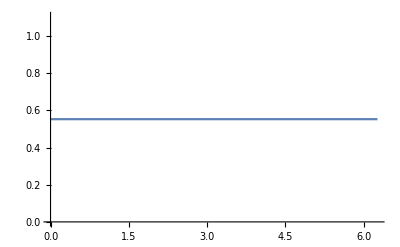

```mathematica
ListLinePlot[getTriAreaRatioHelman[1.5]]
```

```mathematica
getStats[Second/@getTriAreaRatioHelman[1.5]]
```

<|n→360,mean→0.552655,sd→1.22177×10^-15,z→2.21072×10^-15,min→0.552655,max→0.552655,median→0.552655|>

## Trilinears

Trilinears x : y : z convert via triangle vertices A, B, C  and sides a, b, c :

```mathematica
Clear@trilinearToCartesian;
trilinearToCartesian[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
safeDiv[#,denom]&/@(a x A+b y B+c z C)];
```

```mathematica
rotateSym[fabc_]:={fabc,fabc/.{a->b,b->c,c->a},fabc/.{a->c,b->a,c->b}}
```

```mathematica
(* trilinears: a:b:c *)
getIncenterTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,{1,1,1}];
getCircumcenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},{a(b2+c2-a2),b(c2+a2-b2),c(a2+b2-c2)}]];
getOrthocenterTrilin[orbit_,sides_]:=Module[{cs},
cs=getTriCosines[orbit];
trilinearToCartesian[orbit,sides,1/cs]
];
getCentroidTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c,c a,a b}];
getFeuerbachTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{b c(b+c-a)(b-c)^2,
c a(c+a-b)(c-a)^2,
a b(a+b-c)(a-b)^2}];
getNinepointCenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},
{b c(a2(b2+c2)-(b2-c2)^2),
c a(b2(c2+a2)-(c2-a2)^2),
a b(c2(a2+b2)-(a2-b2)^2)}]];
getFirstIsodynamicTrilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,sqrt3=Sqrt[3]},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
trilinearToCartesian[orbit,{a,b,c},
{3 cosA+sqrt3 sinA,
3 cosB+sqrt3 sinB,
3 cosC+sqrt3 sinC}]];
```

```mathematica
(* X(356) *)
getFirstMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,
{c3[[1]]+2c3[[2]] c3[[3]],
c3[[2]]+2c3[[3]] c3[[1]],
c3[[3]]+2c3[[1]] c3[[2]]}]
];
(* X(357) *)
getSecondMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,1/c3]
];
(* X(358) *)
getThirdMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,c3]
];
getSymmedianTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,sides];
getMittenTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-a,c+a-b,a+b-c}];
getBarycenterTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{a,b,c}];
getGergonneTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b*c/(b+c-a),c*a/(c+a-b),a*b/(a+b-c)}];
getNagelTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c}, {(b+c-a)/a,(c+a-b)/b,(a+b-c)/c}];
getSpiekerTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c(b+c),c a(c+a),a b (a+b)}];
(* X40 *)
getBevanTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{
b/(c+a-b)+c/(a+b-c)-a/(b+c-a),
c/(a+b-c)+a/(b+c-a)-b/(c+a-b),
a/(b+c-a)+b/(c+a-b)-c/(a+b-c)}];
```

```mathematica
getX12Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{
b c(b+c)^2/(b+c-a),
c a(c+a)^2/(c+a-b),
a b(a+b)^2/(a+b-c)
}];
```

```mathematica
Clear@getX59Trilin;getX59Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,cosBC,cosCA,cosAB},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBC=cosB*cosC+sinB*sinC;
cosCA=cosC*cosA+sinC*sinA;
cosAB=cosA*cosB+sinA*sinB;
trilinearToCartesian[orbit,{a,b,c},{
1/(1-cosBC),
1/(1-cosCA),
1/(1-cosAB)}]];
```

```mathematica
Clear@getX144Trilin;getX144Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,tanAov2,tanBov2,tanCov2},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
tanAov2=tanHalfAngle[sinA,cosA];
tanBov2=tanHalfAngle[sinB,cosB];tanCov2=tanHalfAngle[sinC,cosC];
(* (csc A)(tan B/2+tan C/2-tan A/2) *)
trilinearToCartesian[orbit,{a,b,c},{
(tanBov2+tanCov2-tanAov2)/sinA,
(tanCov2+tanAov2-tanBov2)/sinB,
(tanAov2+tanBov2-tanCov2)/sinC}]];
```

```mathematica
(* a(b^2 Cos[2B]+ c^2 Cos[2C] - a^2 Cos[2A]) *)
getX26Trilin[orbit_,{a_,b_,c_}]:=
Module[{cosA,cosB,cosC,cos2A,cos2B,cos2C,a2=a*a,b2=b*b,c2=c*c},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
cos2A=2 cosA^2-1;
cos2B=2 cosB^2-1;
cos2C=2 cosC^2-1;
trilinearToCartesian[orbit,{a,b,c},
{a(b2 cos2B+ c2 cos2C - a2 cos2A),
b(c2 cos2C+ a2 cos2A - b2 cos2B),
c(a2 cos2A+ b2 cos2B - c2 cos2C)}
]];
```

```mathematica
(* mittenpunkt of excentral triangle *)
getX168Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinAov2,sinBov2,sinCov2},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinAov2,sinBov2,sinCov2}=sinHalfAngle/@{cosA,cosB,cosC};
trilinearToCartesian[orbit,{a,b,c},{
b/(1-sinBov2)+c/(1-sinCov2)-a/(1-sinAov2),
c/(1-sinCov2)+a/(1-sinAov2)-b/(1-sinBov2),
a/(1-sinAov2)+b/(1-sinBov2)-c/(1-sinCov2)}]];
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,1.1];
getOrthocenterTrilin[o,s]]
```

{0.696532,1.04352}

```mathematica
Module[{o,n,s,cirs,incs},
{o,n,s}=orbitNormals[1.5,1.1];
cirs={getCircumcenterTrilin[o,s],getCircumcenter@@o};
incs={getIncenterTrilin[o,s],getIncenter[o[[1]],n[[1]],o[[2]],n[[2]]]};
{cirs,incs}//MatrixForm]
```

({-0.0701496,-0.336575} | getCircumcenter[{0.680394,0.891207},{1.3669,-0.41182},{-1.49106,-0.109019}]
{0.449317,0.210191} | getIncenter[{0.680394,0.891207},{-0.321319,-0.946971},{1.3669,-0.41182},{-0.827741,0.561111}])

#### Generate Billiard as Locus

```mathematica
getX100Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b-c,c-a,a-b}];
getX101Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{a/(b-c),b/(c-a),c/(a-b)}];

getX88Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b+c-2a,c+a-2b,a+b-2c}];
(* isogonal conjugate of X88, therefore all are inverted *)
getX44Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-2a,c+a-2b,a+b-2c}];
getX693Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{(b-c)/a^2,(c-a)/b^2,(a-b)/c^2}];
```

```mathematica
(* YFF PARABOLIC POINT *)
getX190Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c/(b-c),c a/(c-a),a b/(a-b)}];
(* TRILINEAR POLE OF LINE X(1)X(3) *)
getX651Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{(b-c)(b+c-a),(c-a)(c+a-b),(a-b)(a+b-c)}];
```

#### Barycentrics (does not appear to work!)

-Graphics-

```mathematica
barycentricToCartesian[orbit_,lambdas0_]:=Module[{x,y,area,lambdas},
(*area=Area[Polygon@orbit];*)
lambdas=lambdas0/Total@lambdas0;
x=Total@MapThread[(#1*#2)&,{First/@orbit,lambdas}];
y=Total@MapThread[(#1*#2)&,{Second/@orbit,lambdas}];
{x,y}];
```

```mathematica
Clear@X10405;X10405[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
1/{3a^2-2a b-2a c-(b-c)^2,
3b^2-2b c-2b a-(c-a)^2,
3c^2-2c a-2c b-(a-b)^2}];
```

```mathematica
(* perpector of anticomplementary on extouch: http://mathworld.wolfram.com/Perspector.html  *)
```

```mathematica
X144b[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
{1/(a-b-c)+1/(a-b+c)+1/(a+b-c),
1/(b-c-a)+1/(b-c+a)+1/(b+c-a),
1/(c-a-b)+1/(c-a+b)+1/(c+a-b)}];
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,.1];
{getX144Trilin[o,s],X144b[o,s]}
]
```

{{0.59009,0.346298},{0.59009,0.346298}}

```mathematica
equiError[tri_]:=Module[{s,bar,inc,savg},
s=RotateLeft@triLengths@tri;
savg=Total@s/Length@s;
bar=getBarycenterTrilin[tri,s];
inc=getIncenterTrilin[tri,s];
magn2[bar-inc]/savg]
```

```mathematica
isEqui[tri_]:=equiError[tri]<10^-6;
```

## Triangles form Trilinear Matrices

```mathematica
trilinearMatrixToCartesian[orbit_,sides_,tryM_]:=trilinearToCartesian[orbit,sides,#]&/@tryM;
```

to do : anticomplementary, external tangents triangle.

```mathematica
Clear@incentralTriangle;
incentralTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,1,1},
{1,0,1},
{1,1,0}}];
```

```mathematica
Clear@excentralTriangle;
excentralTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,1,1},
{1,-1,1},
{1,1,-1}}];
```

```mathematica
Clear@medialTriangle;
medialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,a*c,a*b},{b*c,0,a*b},{b*c,a*c,0}}];
```

```mathematica
Module[{tri={{0,0},{1,0},{1,1}}},
medialTriangle[tri,RotateLeft@triLengths@tri]]
```

{{1,1/2},{1/2,1/2},{1/2,0}}

```mathematica
Clear@orthicTriangle;
orthicTriangle[orbit_,sides_]:=Module[{secA,secB,secC},
{secA,secB,secC}=1./getTriCosines[orbit];trilinearMatrixToCartesian[orbit,sides,{{0,secB,secC},{secA,0,secC},{secA,secB,0}}]];
```

```mathematica
Clear@eulerTriangle;
eulerTriangle[orbit_,{a_,b_,c_}]:=Module[{cA,cB,cC,sA,sB,sC,tA,tB,tC},
{cA,cB,cC}={
lawOfCosines[a,b,c],
lawOfCosines[b,a,c],
lawOfCosines[c,a,b]};
{sA,sB,sC}=getSin/@{cA,cB,cC};
{tA,tB,tC}={sA/cA,sB/cB,sC/cC};
trilinearMatrixToCartesian[orbit,{a,b,c},{{2 tA+tB+tC,sA/cB,sA/cC},
{sB/cA,tA+2tB+tC,sB/cC},
{sC/cA,sC/cB,tA+tB+2tC}}]];
```

```mathematica
(* http://mathworld.wolfram.com/TangentialTriangle.html *)
tangentialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-a,b,c},{a,-b,c},{a,b,-c}}];
anticomplementaryTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{1/{-a,b,c},1/{a,-b,c},1/{a,b,-c}}];
externaltangentsTriangle[orbit_,sides_]:=Module[{x,y,z},
{x,y,z}=getTriCosines[orbit];
trilinearMatrixToCartesian[orbit,sides,
{{-(x+1),x+z,x+y},
{y+z,-(y+1),y+x},
{z+y,z+x,-(z+1)}
}]];
```

```mathematica
hexylTriangle[orbit_,{a_,b_,c_}]:=Module[{x,y,z,diag},
{x,y,z}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
diag=x+y+z+1;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{diag,x+y-z-1,x-y+z-1},
{x+y-z-1,diag,-x+y+z-1},
{x-y+z-1,-x+y+z-1,diag}}]];
```

```mathematica
outerNapoleonTriangle[orbit_,{a_,b_,c_}]:=Module[{
cosA,cosB,cosC,sinA,sinB,sinC,
cPi6,sPi6,
sApPi6,sBpPi6,sCpPi6,sAmPi6,sBmPi6,sCmPi6},
cPi6=Cos[π/6.];
sPi6=Sin[π/6.];
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{sApPi6,sAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sBpPi6,sBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sCpPi6,sCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,2sCpPi6,2sBpPi6},
{2sCpPi6,-1,2sApPi6},
{2sBpPi6,2sApPi6,-1}}]];
```

```mathematica
firstMorleyTriangle[orbit_,{a_,b_,c_}]:=Module[{cs,cs3},
cs={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
cs3=cosThird/@cs;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,2cs3[[3]],2cs3[[2]]},
{2cs3[[3]],1,2cs3[[1]]},
{2cs3[[2]],2cs3[[1]],1}}]];
```

```mathematica
cevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{0,t2,t3},{t1,0,t3},{t1,t2,0}}];antiCevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-t1,t2,t3},{t1,-t2,t3},{t1,t2,-t3}}];
```

```mathematica
pedalTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=Module[{cA,cB,cC},
{cA,cB,cC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
trilinearMatrixToCartesian[orbit,{a,b,c},{
{0,t2+t1 cC,t3+t1 cB},
{t1+t2 cC,0,t3+t2 cA},
{t1+t3 cB,t2+t3 cA,0}
}]];
```

```mathematica
trilinearCoords[tri_,p_]:=
RotateLeft@MapThread[magn[closestPerp[p,#1,#2]-p]&,
(* needs this crossed rotation so trilinears come out in the usual way *)
{tri,RotateLeft@tri}]
```

```mathematica
Module[{o,n,s,p,tril},
{o,n,s}=orbitNormals[1.5,toRad@35.];
p=getSymmedianTrilin[o,s];
tril=trilinearCoords[o,p];
tril
(*Print@(s/s[[1]]);
tril/tril[[1]]*)]
```

{0.551909,0.580316,0.273465}

```mathematica
intouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a c)/(a-b+c),(a b)/(a+b-c)},
{(b c)/(-a+b+c),0,(a b)/(a+b-c)},
{(b c)/(-a+b+c),(a c)/(a-b+c),0}}];
```

```mathematica
extouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a-b+c)/b,(a+b-c)/c},
{(-a+b+c)/a,0,(a+b-c)/c},
{(-a+b+c)/a,(a-b+c)/b,0}}];
```

```mathematica
symmedialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{0,b,c},{a,0,c},{a,b,0}}];
```

```mathematica
sinHalfAngle[theCos]^2
```

1/2 (1.-theCos)

```mathematica
cosHalfAngle[theCos]^2
```

1/2 (1.+theCos)

```mathematica
Clear@feuerbachTriangle;
feuerbachTriangle[orbit_,{a_,b_,c_}]:=Module[{
sinA,sinB,sinC,
cosA,cosB,cosC,
cosBmC,cosCmA,cosAmB,
c2haAmB,c2haBmC,c2haCmA,
m},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBmC=cosDiffAngle[sinB,cosB,sinC,cosC];
cosCmA=cosDiffAngle[sinC,cosC,sinA,cosA];
cosAmB=cosDiffAngle[sinA,cosA,sinB,cosB];
c2haAmB=cos2HalfAngle[cosAmB];
c2haBmC=cos2HalfAngle[cosBmC];
c2haCmA=cos2HalfAngle[cosCmA];
m={
{-sin2HalfAngle[cosBmC],c2haCmA,c2haAmB},
{c2haBmC,-sin2HalfAngle[cosCmA],c2haAmB},
{c2haBmC,c2haCmA,-sin2HalfAngle[cosAmB]}
};trilinearMatrixToCartesian[orbit,{a,b,c},m]];
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,.1];
feuerbachTriangle[o,s]]
```

{{-1.04832,-0.369712},{-0.112968,0.352287},{0.256211,-0.740368}}

#### The first point in the extouch triangle flows on caustic at the exact same parametric than P1

```mathematica
Manipulate[Module[{o,ett,ell,a=1.5,gr,ca,cb},
o=orbitNormals[a,t][[1]];
{ca,cb}=getTriCausticParams[a];
ett=extouchTriangle[o,RotateLeft@triLengths@o];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@{Blue,Thick},Polygon@o,Red,Point@First@o,Blue,Circle[First@o,.05]},
{EdgeForm@Darker@Green,Polygon@ett},
{Darker@Green,Circle[ett[[1]],.05]},
{Red,Point[{-ca Cos[t],-cb Sin[t]}]}}];
Show[{plotEll[a],plotEllb[ca,cb,Brown],gr},AspectRatio->Automatic,Frame->True]],{t,0,2π,π/360.}]
```

#### Anticomplementary triangle seems like the more stable, more useful to produce higher order points.

```mathematica
Module[{cc,vs,sides,cir,cirRad,tt,ac,et,ortTril,ortCev,clrs,ort,ortAntiCev,hexyl},
Manipulate[
vs={{-1,0},{1,0},p1}; (*N@{{0,0},{1,-.6},{.7,.5}};*)
sides=RotateLeft@triLengths@vs;
cir=getCircumcenterTrilin[vs,sides];
cirRad=magn[vs[[1]]-cir];
tt=tangentialTriangle[vs,sides];
ac=anticomplementaryTriangle[vs,sides];
et=externaltangentsTriangle[vs,sides];
hexyl=hexylTriangle[vs,sides];
ortTril=1/getTriCosines[vs];
ort=trilinearToCartesian[vs,sides,ortTril];
ortCev=cevianTriangle[vs,sides,ortTril];
ortAntiCev=antiCevianTriangle[vs,sides,ortTril];
clrs={Black,Red,Green,Blue,Purple,Cyan,Pink};
Legended[Graphics[{PointSize@Medium,Black,FaceForm@None,
MapThread[{EdgeForm@#1,#1,Polygon@#2,Point@#2}&,{clrs,{vs,tt,ac,et,ortCev,ortAntiCev,hexyl}}],
{Circle[cir,cirRad],Point@cir},
{Orange,Point@ort}},ImageSize->Medium,Frame->True,PlotRange->{{-5,5},{-5,5}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"reference","tangential","anticomplementary","external tangents","ortho cevian = orthic","ortho anticevian","hexyl"}]],
{{p1,{0,2}},Locator},SaveDefinitions->True]]
```

```mathematica
Manipulate[
DynamicModule[{cc,vs,normals,sides,ell,cir,cirRad,tt,ac,et,ortTril,ortCev,clrs,ort,ortAntiCev,hexyl,gr,xmax=3,ymax=3},
ell=plotEll[a];
{vs,normals,sides}=orbitNormals[a,toRad@tDeg];
sides=RotateLeft@triLengths@vs;
cir=getCircumcenterTrilin[vs,sides];
cirRad=magn[vs[[1]]-cir];
tt=tangentialTriangle[vs,sides];
ac=anticomplementaryTriangle[vs,sides];
et=externaltangentsTriangle[vs,sides];
hexyl=hexylTriangle[vs,sides];
ortTril=1/getTriCosines[vs];
ort=trilinearToCartesian[vs,sides,ortTril];
ortCev=cevianTriangle[vs,sides,ortTril];
ortAntiCev=antiCevianTriangle[vs,sides,ortTril];
clrs={Black,Red,Green,Blue,Purple,Cyan,Pink};
gr=Legended[Graphics[{PointSize@Medium,Black,FaceForm@None,
MapThread[{EdgeForm@#1,#1,Polygon@#2,Point@#2}&,{clrs,{vs,tt,ac,et,ortCev,ortAntiCev,hexyl}}],
{Circle[cir,cirRad],Point@cir},
{Orange,Point@ort}},ImageSize->Medium,Frame->True,PlotRange->{{-5,5},{-5,5}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"reference","tangential","anticomplementary","external tangents","ortho cevian = orthic","ortho anticevian","hexyl"}]];
Show[{ell,gr},PlotRange->{{-xmax,xmax},{-ymax,ymax}}]],
{{a,1.5},1.01,3,.05},
{{tDeg,0},-360,360,.1},SaveDefinitions->True]
```

-Graphics-

```mathematica
Clear@getInradius;getInradius[{a_,b_,c_}]:=Module[{num1,num2,num3,denom},
num1=b+c-a;
num2=c+a-b;
num3=a+b-c;
denom=a+b+c;
Sqrt[num1*num2*num3/denom]/2];
```

```mathematica
getInradius[{Subscript[s, 1],Subscript[s, 2],Subscript[s, 3]}]//TeXForm
```

\frac{1}{2} \sqrt{\frac{\left(s_1+s_2-s_3\right) \left(s_1-s_2+s_3\right) \left(-s_1+s_2+s_3\right)}{s_1+s_2+s_3}}

```mathematica
getInradius[{s1,s2,s3}]//CForm
```

Sqrt(((s1 + s2 - s3)*(s1 - s2 + s3)*(-s1 + s2 + s3))/(s1 + s2 + s3))/2.

```mathematica
getCircumradius[{a_,b_,c_}]:=Module[{s,num,denom1,denom2,denom3},
s=(a+b+c)/2;
num=a*b*c;
denom1=(a+b-s);
denom2=(a+c-s);
denom3=(b+c-s);
num/(4*Sqrt[s*denom1*denom2*denom3])];
```

```mathematica
getCircumradius[{Subscript[s, 1],Subscript[s, 2],Subscript[s, 3]}]/.{Subscript[s, 1]+Subscript[s, 2]+Subscript[s, 3]->L,-Subscript[s, 1]-Subscript[s, 2]-Subscript[s, 3]->-L}//TeXForm
```

\frac{s_1 s_2 s_3}{2 \sqrt{2} \sqrt{L \left(-\frac{L}{2}+s_1+s_2\right) \left(-\frac{L}{2}+s_1+s_3\right) \left(-\frac{L}{2}+s_2+s_3\right)}}

```mathematica
getCircumradius[{s1,s2,s3}]//CForm
```

(s1*s2*s3)/(2.*Sqrt(2)*Sqrt((s1 + s2 + (-s1 - s2 - s3)/2.)*(s1 + s2 + s3)*(s1 + (-s1 - s2 - s3)/2. + s3)*(s2 + (-s1 - s2 - s3)/2. + s3)))

```mathematica
getNinepointCircleRadius[sides_]:=getCircumradius[sides]/2;
```

```mathematica
getTriCosines[tri_]:=Module[{u12,u23,u31},
u12=norm[tri[[2]]-tri[[1]]];
u23=norm[tri[[3]]-tri[[2]]];
u31=norm[tri[[1]]-tri[[3]]];
{
-u12.u31,
-u23.u12,
-u31.u23
}];
```

```mathematica
getTriData[tri_]:=Module[{sides,perimeter,inc,inradius,circumradius,cosines,bisectors,area},
sides=RotateLeft@triLengths@tri;
perimeter=Total@sides;
inradius=getInradius[sides];
circumradius=getCircumradius[sides];
cosines=getTriCosines[tri];
bisectors=getTriBisectors@@tri;
area=inradius*perimeter/2;
{"sides"->sides,
"perimeter"->perimeter,
"inradius"->inradius,
"circumradius"->circumradius,
"rOvR"->inradius/circumradius,
"cosines"->cosines,
"area"->area,
"bisectors"->bisectors}];
```

```mathematica
getSubtriData[tri_]:=Module[{sides,inc,tps,incR,npc,npcR},
sides=RotateLeft[triLengths@tri];
inc=getIncenterTrilin[tri,sides];
(* the intouchpoints of this guy is on the billiard, needs to draw them *)
tps=intouchTriangle[tri,sides];
incR=getInradius[sides];
npc=getNinepointCenterTrilin[tri,sides];
npcR=getNinepointCircleRadius[sides];
<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];
```

```mathematica
Clear@getAnticomplData;
getAnticomplData[orbit_,sides_]:=
getSubtriData@anticomplementaryTriangle[orbit,sides];
```

```mathematica
Clear@getMedialData;
getMedialData[orbit_,sides_]:=
getSubtriData@medialTriangle[orbit,sides];
```

```mathematica
getTriDoubleCosineSum[tri_]:=Total[cosDoubleAngle/@getTriCosines@tri];
```

```mathematica
getBilliardAngleTrilin[a_,tDeg_,trilinFn_]:=Module[{o,n,s,xn},
{o,n,s}=orbitNormals[a,toRad@tDeg];
xn=trilinFn[o,s];
getBilliardAngle[a,1,xn]]
```

```mathematica
getTrilinXY[a_,tDeg_,trilinFn_]:=Module[{o,n,s,xn},
{o,n,s}=orbitNormals[a,toRad@tDeg];
xn=trilinFn[o,s];
xn]
```

## Major Triangular Centers (Notables)

#### Linha de Euler: bari, ortho, circum, 9-pc all lie on a line (but not incenter)

-Graphics-

```mathematica
getAltBases[p1_,p2_,p3_]:=Module[{sides},
sides={{p2,p3},{p3,p1},{p1,p2}};
MapThread[closestPerp[#1,#2[[1]],#2[[2]]]&,{{p1,p2,p3},sides}]];
```

```mathematica
getIncenter[p1_,n1_,p2_,n2_]:=interRays[p1,n1,p2,n2];
Clear@getBaricenter;getBaricenter[p1_,p2_,p3_]:=Module[{medians},(*(p1+p2+p3)/3;*)
medians=getMedians[p1,p2,p3];
interRays[p1,medians[[1]](*23*)-p1,p2,medians[[2]](*31*)-p2]
];
getOrthocenter[p1_,p2_,p3_]:=Module[{altBases},
altBases=getAltBases[p1,p2,p3];
interRays[p1,altBases[[1]]-p1,p2,altBases[[2]]-p2]
];
getCircumcenter[p1_,p2_,p3_]:=Module[{medians,medianPerps},
medians=getMedians[p1,p2,p3];
medianPerps={
medians[[1]]+norm[perp[p2-p3]],
medians[[2]]+norm[perp[p3-p1]],
medians[[3]]+norm[perp[p1-p2]]
};
interRays[medians[[1]](*2+3*),perp[p2-p3],medians[[2]](*3+1*),perp[p1-p3]]
];
```

#### Nine Point Circle: its center is the circumcenter of the medians, and is tangent to incircle (at Feuerbach point) and all 3 excircles

-Graphics--Graphics-

```mathematica
getNinepointcenter[p1_,p2_,p3_]:=Module[{medians},
medians=getMedians[p1,p2,p3];
getCircumcenter@@medians
];
```

```mathematica
Clear@inRadius0;
inRadius0[incenter_,p1_,p2_]:=Module[{ctr,foot},
foot=closestPerp[incenter,p1,p2];
magn[incenter-foot]];
```

```mathematica
circumRadius0[circumcenter_,p1_]:=magn[circumcenter-p1];
```

```mathematica
(* shoot ray from incenter *)
getFeuerbachpoint[npc_,incenter_,inradius_]:=Module[{inter},
ray[incenter,norm[incenter-npc],inradius]
];
```

```mathematica
getExcenters[orbit_,normals_]:=Module[{perps,perpsNeg,exc},
perps=perp/@normals;
perpsNeg=perpNeg/@normals;
exc=MapThread[interRays[#1,#2,#3,#4]&,{orbit,perps,RotateLeft@orbit,RotateLeft@perpsNeg}];
exc];
```

#### Gergonne Point: perspector of ABC and its contact triangle Ta, Tb, Tc

## Get Triangular Center (Notable) Info

```mathematica
Clear@getTouchPts;getTouchPts[orbit_,normals_]:=Module[{inc,tps},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
tps];
```

```mathematica
getAntiComplement[p_,bar_]:=bar-2(p-bar);
```

```mathematica
Clear@getNotables;
getNotables[orbit_,normals_]:=Module[{inc,inradius,cir,circumradius,npc,exc,tps,ort,medians,npcradius,sides,bar,feu,antifeu,x88,perimeter},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
inradius=inRadius0[inc,orbit[[1]],orbit[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
medians=getMedians@@orbit;
cir=getCircumcenter@@orbit;
circumradius=circumRadius0[cir,orbit[[1]]];
npc=getNinepointcenter@@orbit;
npcradius=magn[npc-medians[[1]]];
exc=getExcenters[orbit,normals];
sides=RotateLeft[triLengths@orbit];
feu=getFeuerbachpoint[npc,inc,inradius];
bar=getBaricenter@@orbit;
antifeu=getAntiComplement[feu,bar];(* anticomplement *)
x88=getX88Trilin[orbit,sides];
ort=getOrthocenter@@orbit;
perimeter=Total@sides;
(* we think this is constant for excentral triangle *)
{
"inc"->inc,
"bar"->bar,(* also: getCentroid[orbit,sides] *)
"ort"->ort,
"cir"->cir,
"npc"->npc,
"exc"->exc,
"ex12"->exc[[1]],
"ex23"->exc[[2]],
"ex31"->exc[[3]],
"feu"->feu,
"antifeu"->antifeu,
"x88"->x88,
(* all thru trilinears, each computing sides unnecessarily *)
"mit"->getMittenTrilin[orbit,sides],
"sym"->getSymmedianTrilin[orbit,sides],
"ger"->getGergonneTrilin[orbit,sides],
"nag"->getNagelTrilin[orbit,sides],
"spi"->getSpiekerTrilin[orbit,sides],
(* not really notables, aux info *)
"incRadius"->inradius,
"tps"-> tps,
"medians"->medians,
"cirRadius"->circumradius,
"npcRadius"->npcradius,
"sides"->sides,
"perimeter"->perimeter,
"area"->triAreaHeron@sides
}];
```

#### Orthic and orthic of orthic (similar to reference triangle?)

```mathematica
Clear@getOrthicData;getOrthicData[orbit_]:=Module[{feet,inc,sides,ort,
intouch,intouchSides,inradius,(* intouchInc = inc *)
intouchOrt,intouchOrtSides,intouchOrtInc,
intouchAnticompl,intouchAnticomplSides,
intouchAnticomplOrt,intouchAnticomplOrtSides,intouchAnticomplOrtInc,
orthic,orthicSides,orthicInc,
orthicAnticompl,orthicAnticomplSides,orthicAnticomplInc
},
(* orthic *)
feet=getAltBases@@orbit;
sides=RotateLeft@triLengths[feet];
inc=getIncenterTrilin[feet,sides];
ort=getOrthocenterTrilin[feet,sides];
(* intouch *)
intouch=intouchTriangle[feet,sides];
intouchSides=RotateLeft[triLengths@intouch];
inradius=magn[intouch[[1]]-inc];
intouchOrt=getAltBases@@intouch;
intouchOrtSides=RotateLeft[triLengths@intouchOrt];
intouchOrtInc=getIncenterTrilin[intouchOrt,intouchOrtSides];
(* anticomplement of intouch *)
intouchAnticompl=anticomplementaryTriangle[intouch,intouchSides];
intouchAnticomplSides=RotateLeft[triLengths@intouchAnticompl];
intouchAnticomplOrt=getAltBases@@intouchAnticompl;
intouchAnticomplOrtSides=RotateLeft[triLengths@intouchAnticomplOrt];
intouchAnticomplOrtInc=getIncenterTrilin[intouchAnticomplOrt,intouchAnticomplOrtSides];
(* orthic *)
orthic=getAltBases@@feet;
orthicSides=RotateLeft@triLengths[orthic];
orthicInc=getIncenterTrilin[orthic,orthicSides];
orthicAnticompl=anticomplementaryTriangle[orthic,orthicSides];
orthicAnticomplSides=RotateLeft@triLengths[orthicAnticompl];
orthicAnticomplInc=getIncenterTrilin[orthicAnticompl,orthicAnticomplSides];
{
(* orthic *)
"feet"->feet,
"sides"->sides,
"inc"->inc,
"ort"->ort,
(* intouch of orthic, we think similar to orbit *)
"intouch"->intouch,
"intouchSides"->intouchSides,
"inradius"->inradius,
(* orthic of intouch *)
"intouchOrt"->intouchOrt,
"intouchOrtSides"->intouchOrtSides,
"intouchOrtInc"->intouchOrtInc,
(* anticomplement of intouch of orthic, upside down orbit? *)
"intouchAnticompl"->intouchAnticompl,
"intouchAnticomplSides"->intouchAnticomplSides,
(*"intouchAnticomplInc"->intouchAnticomplInc,*)
(* orthic of anticomplement of intouch *)
"intouchAnticomplOrt"->intouchAnticompl,
"intouchAnticomplOrtSides"->intouchAnticomplOrtSides,
"intouchAnticomplOrtInc"->intouchAnticomplOrtInc,
(* orthic of orthic *)
"orthic"->orthic,
"orthicSides"->orthicSides,
"orthicInc"->orthicInc,
(* anticomplement of orthic's orthic *)
"orthicAnticompl"->orthicAnticompl;
"orthicAnticomplSides"->orthicAnticomplSides,
"orthicAnticomplInc"->orthicAnticomplInc
}];
```

#### Excenters and Excircles

```mathematica
Clear@showBisectors;showBisectors[vs_]:=Module[{bs},
bs=getTriBisectors@@vs;
Graphics[{FaceForm[None],EdgeForm[Black],Black,PointSize[Medium],
Polygon[vs],
Point[vs],
MapThread[Text[#1,#2,{1.5,0}]&,{{"P_1","P_2","P_3"},vs}],
MapThread[Arrow[{#1,ray[#1,#2,.25]}]&,{vs,bs}]},
ImageSize->Small]
];
```

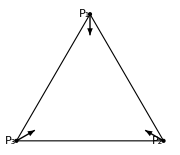

```mathematica
(* show bisectors computed from vertices for equilateral *)
showBisectors[Table[{Sin[a],Cos[a]},{a,0,2π-π/3,2π/3}]]
```

#### Nagel Point

```mathematica
getExtouchPoints[orbit_,exc_]:=MapThread[closestPerp[#1,#2,#3]&,{exc,orbit,RotateLeft[orbit]}];
```

```mathematica
Clear@getExcircleData;
getExcircleData[orbit_,exc_(*12,23,31*),npc_]:=Module[{excFeet,altLengths,tps,radii,feus,nagel,medians,mitten,mittenPedals,
mittenFeet,sides,cosABC,cosSum,cosProd,sideProd,altLengthsProd,feusCir,feusCirR,mittenFeetCir,mittenFeetCirR},
(* side touch points to sides: 12,23,31 *)
tps=getExtouchPoints[orbit,exc];
excFeet=getAltBases@@exc;
altLengths=MapThread[magn[#1-#2]&,{exc,excFeet}];
radii=MapThread[magn[#1-#2]&,{exc,tps}];
feus=MapThread[ray[#1,norm[npc-#1],#2]&,{exc,radii}];
feusCir=getCircumcenter@@feus;
feusCirR=magn[feus[[1]]-feusCir];
(*nagel=interRays[orbit[[1]],tps[[2]]-orbit[[1]],orbit[[2]],tps[[3]]-orbit[[2]]];*)
(* MapThread[Line[{#1,ray[#1,norm[#2-#1],10]}]&,{exc,RotateRight@medians}]}],{}],*)
medians=getMedians@@orbit;
mitten=interRays[exc[[1]],medians[[3]]-exc[[1]],exc[[2]],medians[[1]]-exc[[2]]];
mittenPedals=MapThread[closestPerp[mitten,#1,#2]&,{orbit,RotateLeft@orbit}];
(* symmedian triangle *)
mittenFeet=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{exc,RotateRight@medians,RotateLeft@exc,RotateRight@exc}];
mittenFeetCir=getCircumcenter@@mittenFeet;
mittenFeetCirR=magn[mittenFeet[[1]]-mittenFeetCir];
sides=RotateLeft[triLengths@exc];
cosABC=getTriCosines[exc];
cosSum=Total[cosABC];
cosProd=cosABC[[1]]*cosABC[[2]]*cosABC[[3]];
sideProd=sides[[1]]*sides[[2]]*sides[[3]];
altLengthsProd=altLengths[[1]]*altLengths[[2]]*altLengths[[3]];
{
"sides"->sides,
"perimeter"->Total[sides],
"cosABC"->cosABC,
"excFeet"->excFeet,
"altLengths"->altLengths,
"sumAltLengths"->Total@altLengths,
"prodAltLengths"->altLengthsProd,
"sumInvAltLengths"->Total[(1/#)&/@altLengths],
"cosSum"->cosSum,
"cosProd"->cosProd,
"sideProd"->sideProd,
"tps"->tps,(* extouchpoints*)
"radii"->radii,
"sumRadiiSqr"->Total[#^2&/@radii],
"sumInvRadiiSqr"->Total[(1/#^2)&/@radii],
"sumRadii"->Total@radii,
"sumInvRadii"->Total[(1/#)&/@radii],
"feus"->feus,
"feusCir"->feusCir,
"feusCirR"->feusCirR,
"mitten"->mitten,
"mittenPedals"->mittenPedals,
"mittenFeet"-> mittenFeet, (* BAD choice: intersecao do segm Vi-MITTEN com o lado oposto do extriangulo *)
"mittenFeetCir"->mittenFeetCir,
"mittenFeetCirR"->mittenFeetCirR
}
];
```

## Drawing Notables & Clrs

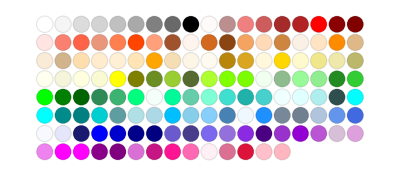

```mathematica
ColorData["HTML","Panel"]
```

```mathematica
ptClrs={
"ell"->Black,
"med"->Darker@Red,
"bar"->Brown,
"inc"->Darker@Green,
"ort"->Orange,
"cir"->Purple,
"npc"->ColorData["HTML","PaleVioletRed"],
"exc"->Darker@Green,
"ex12"->Darker@Green,
"ex23"->Darker@Green,
"ex31"->Darker@Green,
"dar"->ColorData["HTML","Navy"],
"x144"->ColorData["HTML","Navy"],
"x59"->ColorData["HTML","OrangeRed"],
"feu"-> ColorData["HTML","DarkKhaki"],
"antifeu"->ColorData["HTML","SlateGray"],
"anticompl"->Blue,
"steiner"->Brown,
"steinerinell"->Brown,
"x88"->Darker@Cyan,
"x100"->ColorData["HTML","SlateGray"],
"nag"->ColorData["HTML","MediumAquamarine"],
"mit"->Red(*Lighter@Blue*),
"sym"->ColorData["HTML","DodgerBlue"],
"bev"->Lighter@Purple,
"ger"->Darker@Cyan,
"spi"->ColorData["HTML","SpringGreen"],
"nap"->Red,
"hex"->Pink,
(* overrides *)
"red"->Red,
"green"->Green,
"blue"->Blue
};
```

```mathematica
ptClrs
```

{ell→-Graphics-,med→-Graphics-,bar→-Graphics-,inc→-Graphics-,ort→-Graphics-,cir→-Graphics-,npc→-Graphics-,exc→-Graphics-,ex12→-Graphics-,ex23→-Graphics-,ex31→-Graphics-,dar→-Graphics-,x144→-Graphics-,x59→-Graphics-,feu→-Graphics-,antifeu→-Graphics-,anticompl→-Graphics-,steiner→-Graphics-,steinerinell→-Graphics-,x88→-Graphics-,x100→-Graphics-,nag→-Graphics-,mit→-Graphics-,sym→-Graphics-,bev→-Graphics-,ger→-Graphics-,spi→-Graphics-,nap→-Graphics-,hex→-Graphics-,red→-Graphics-,green→-Graphics-,blue→-Graphics-}

```mathematica
Clear@plotEllb;
plotEllb[a_,b_,clr_:("ell"/.ptClrs)]:=Graphics@If[SameQ[clr,None],{},{If[ListQ@clr,Sequence@@clr,clr],Circle[{0,0},{a,b}]}];
Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=plotEllb[a,1,clr];
```

```mathematica
Clear@plotEllFillb;
plotEllFillb[a_,b_,clrFill_,clr_:("ell"/.ptClrs)]:=Graphics[{
If[SameQ[clrFill,None],{},{If[ListQ@clrFill,Sequence@@clrFill,clrFill],Disk[{0,0},{a,b}]}],
If[SameQ[clr,None],{},{If[ListQ@clr,Sequence@@clr,clr],Circle[{0,0},{a,b}]}]
}];
Clear@plotEllFill;plotEllFill[a_,clrFill_,clr_:("ell"/.ptClrs)]:=plotEllFillb[a,1,clrFill,clr];
```

```mathematica
(*Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];
plotEllFill[a_,clrFill_,clr_:("ell"/.ptClrs)]:=Module[{int,ext},
int=ParametricPlot[r{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},{r,0,1},
PlotStyle->clrFill,PerformanceGoal->"Quality"];
ext=plotEll[a,clr];
Show[{int,ext}]];
plotEllb[a_,b_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],N[b]Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];*)
```

```mathematica
drawArrow[p0_,phat_,l_]:=Arrow[{p0,ray[p0,phat,l]}];
```

```mathematica
Clear@drawOrbit;
Options@drawOrbit={lgt->.25,drNormals->True,pSize->16,drVtxLabels->True,clr->{Thick,Darker@Blue}};
drawOrbit[orbitData_,OptionsPattern[](*lgt_:.25,drawNormals_:True,psize_:16*)]:=Module[{normals,orbit,halfAlpha},
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
halfAlpha="halfAlpha"/.orbitData;
Graphics[{
PointSize[Large],Arrowheads[Medium],
{OptionValue@clr,Point@orbit},
{FaceForm[GrayLevel@.9],EdgeForm@OptionValue@clr,Polygon@orbit},
If[OptionValue@drNormals,
{Black,
MapThread[drawArrow[#1,#2,OptionValue@lgt]&,{orbit,normals}],
Dashed,
drawArrow[orbit[[1]],"nRot"/.orbitData,OptionValue@lgt],
drawArrow[orbit[[1]],"nRotNeg"/.orbitData,OptionValue@lgt],
Text["α",ray[orbit[[1]],halfAlpha ,.33OptionValue@lgt]]},{}],
If[OptionValue@drVtxLabels,MapThread[txtSubscript["P",ToString@#1,OptionValue@pSize,ray[#2,-#3,.33OptionValue@lgt]]&,
{{1,2,3},orbit,normals}],{}]}]
];
```

```mathematica
Clear@drawOneNotable;drawOneNotable[clr_,at_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Point@at,Text[Style[txt,fntSize],at,{dx,dy}]};
circOneNotable[clr_,at_,rad_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Circle[at,rad],Text[Style[txt,fntSize],at,{dx,dy}]};
Clear@drawNotableLines;drawNotableLines[notables_]:=Graphics@{Darker[Gray],Dashed,
(* euler line: cir,bar,npc,ort *)
Line[{"cir","ort"}/.notables],
(* npc to feuerbach: npc,inc,feu *)
Line[{"npc","feu"}/.notables],
(* mittenpunkt to symmedian: mit,inc,sym *)
Line[{"mit","sym"}/.notables],
(* gergonne to mit: ger,bar,mit *)
Line[{"mit","ger"}/.notables],
(* nagel line: nag,bar,spi,inc *)
Line[{"nag","inc"}/.notables]};
Clear@drawNotables;
drawNotables[notables_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
drawNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotables;
circNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotablesSingleClr;
circNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@drawSomeNotables;
drawSomeNotables[notables_,nots_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@nots}];
Clear@drawBasicNotables;
drawBasicNotables[notables_,prefix_:""]:=drawSomeNotables[notables,{"inc","bar","ort","cir","npc","mit","feu","ger"},prefix];
Clear@drawBasicNotablesSingleClr;
drawBasicNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotables;
circBasicNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotablesSingleClr;
circBasicNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
```

## Draw Orbits: Parametrize by x_1

```mathematica
Clear@drawSim;
Options@drawSim=Join[Options@getOrbitData,Options@drawOrbit,{drNotables->True,drLines->False,drTh->False,drVtxLabels->True,lgt->.5}];
drawSim[a_,x_,opts:OptionsPattern[]]:=Module[{ellPlot,orbitData,orbit,normals,notables,lab},
ellPlot=plotEll[a,{Thick,Black}];
orbitData=getOrbitData[N[a],N[x], FilterRules[{opts}, Options@getOrbitData]];(* N for speed *)
(* half-angle to display α at bisector *)
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
notables=getNotables[orbit,normals];
Show[{
ellPlot,
drawOrbit[orbitData,FilterRules[{opts},Options@drawOrbit]],
If[OptionValue@drNotables,drawNotables[notables],{}],
If[OptionValue@drLines,drawNotableLines[notables],{}]
},
ImageSize->Large,
AspectRatio->Automatic,
PlotRange->{{-2,2},{-1.1,1.1}},Frame->True,AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style["a="<>nf@a<>"; x="<>nf@x,20]]];
```

```mathematica
Clear@drawSimT;
Options@drawSimT=Options@drawSim;
drawSimT[a_,t_,opts:OptionsPattern[]]:=Module[{x,y},
x=a Cos@t;
y=Sin@t;
drawSim[a,x,{opts,posY->y>0}]];
```

```mathematica
Manipulate[
drawSim[a,clamp[x1,a],drLines->drLines0,posY->(!negY),drNotables->drNotables0],
{{a,1.5,"a/b"},1.01,3,.01,Appearance->"Labeled"},
{{x1,.5,"x_1"},-2,2,.01,Appearance->"Labeled"},
{{negY,False,"y_1<0"},{False,True}},
{{drNotables0,True,"show notables"},{False,True}},
{{drLines0,False,"show lines"},{False,True}},
SaveDefinitions->True]
```

## Orbit and Derived Triangles

```mathematica
(* {"billiard","caustic",
"orbit","medial","orthic","intouch","excentral","extouch","anticompl","exfeuer"} *)
```

```mathematica
showDerivedTris[a_,tDeg_]:=Module[{caustic,ell,ca,cb,ellCaustic,clrs,orbit,normals,sides,tris,gr,maxX=2,maxY=2},
{ca,cb}=getTriCausticParams[a];
ell=plotEll[a,{Thick,Black}];
ellCaustic=plotEllb[ca,cb,{Thick,Dashed,"feu"/.ptClrs}];
clrs={Black,{Dashed,"feu"/.ptClrs},Blue,Darker@Red,"ort"/.ptClrs,{Dashed,"inc"/.ptClrs},"inc"/.ptClrs,{Dashed,Orange},{Dashed,Blue},"feu"/.ptClrs};
{orbit,normals,sides}=orbitNormals[a,toRad@tDeg];
tris=(#[orbit,sides]&)/@{medialTriangle,orthicTriangle,intouchTriangle,
excentralTriangle,extouchTriangle,anticomplementaryTriangle,feuerbachTriangle};
gr=Graphics[{FaceForm@None,PointSize@Large ,Black,Point@{0,0},MapThread[{EdgeForm@{Thick,If[ListQ@#1,Sequence@@#1,#1]},Polygon@#2,If[ListQ@#1,Sequence@@#1,#1],Point@#2}&,
{Drop[clrs,2],Prepend[tris,orbit]}]}];
Legended[Show[{ell,ellCaustic,gr},
Frame->True,ImageSize->Large,PlotLabel->Style["Orbit and Derived Triangles",Directive[{Black,14}]],PlotRange->{{-maxX,maxX},{-maxY,maxY}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
Style[#,20]&/@{"billiard","caustic","orbit",
"medial","orthic","intouch","excentral","extouch","anticompl","feuerbach"}]]];
```

```mathematica
Manipulate[showDerivedTris[a,tDeg],
{{a,1.5},1.01,3.0,Appearance->"Labeled"},
{{tDeg,31},-180,180,1,Appearance->"Labeled"}]
```

```mathematica
(*DeleteFile[trisObj]*)
```

```mathematica
(*trisObj=CloudDeploy[%,"orbit and its derived triangles v1",Permissions->"Public"]*)
```

## Trilinears: X(1)~X(100)

```mathematica
newCentersFromFile=Get["data/x0001_0100.m"]; (*//Drop[#,{30}]&;*)(*EULER INFINITY POINT*)
```

```mathematica
newCentersFromFile[[30]]
```

{X(30),Hold[{b+c-a,c+a-b,a+b-c}],EULER INFINITY POINT}

```mathematica
Clear@getNewCenters;
getNewCenters[orbit_,{a0_,b0_,c0_},singles_:{}]:=Block[{a,b,c,eqns,
cosA,cosB,cosC,sinA,sinB,sinC,
secA,secB,secC,cscA,cscB,cscC,
tanA,tanB,tanC,cotA,cotB,cotC,
cos2A,cos2B,cos2C,sin2A,sin2B,sin2C,
sec2A,sec2B,sec2C,csc2A,csc2B,csc2C,
cos3A,sin3A,cos3B,sin3B,cos3C,sin3C,
sec3A,sec3B,sec3C,csc3A,csc3B,csc3C,
cPi3=Cos[π/3.],sPi3=Sin[π/3.],cPi6=Cos[π/6.],sPi6=Sin[π/6.],
sinApPi3,sinBpPi3,sinCpPi3,sinAmPi3,sinBmPi3,sinCmPi3,
sinApPi6,sinBpPi6,sinCpPi6,sinAmPi6,sinBmPi6,sinCmPi6,
cscApPi3,cscBpPi3,cscCpPi3,cscAmPi3,cscBmPi3,cscCmPi3,
cscApPi6,cscBpPi6,cscCpPi6,cscAmPi6,cscBmPi6,cscCmPi6},
a=a0;b=b0;c=c0;
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{secA,secB,secC}=1./{cosA,cosB,cosC};
{cscA,cscB,cscC}=1./{sinA,sinB,sinC};
{tanA,tanB,tanC}={sinA,sinB,sinC}/{cosA,cosB,cosC};
{cotA,cotB,cotC}=1./{tanA,tanB,tanC};
{cos2A,cos2B,cos2C}=cosDoubleAngle/@{cosA,cosB,cosC};
{sec2A,sec2B,sec2C}=1./{cos2A,cos2B,cos2C};
{sin2A,sin2B,sin2C}=getSin/@{cos2A,cos2B,cos2C};
{csc2A,csc2B,csc2C}=1./{sin2A,sin2B,sin2C};
{sin3A,cos3A}=sinCosTripleAngle[sinA,cosA,sin2A,cos2A];
{sin3B,cos3B}=sinCosTripleAngle[sinB,cosB,sin2B,cos2B];
{sin3C,cos3C}=sinCosTripleAngle[sinC,cosC,sin2C,cos2C];
{sec3A,sec3B,sec3C}=1./{cos3A,cos3B,cos3C};
{csc3A,csc3B,csc3C}=1./{sin3A,sin3B,sin3C};
{sinApPi3,sinAmPi3}=getSinApmB[sinA,sPi3,cosA,cPi3];
{sinBpPi3,sinBmPi3}=getSinApmB[sinB,sPi3,cosB,cPi3];
{sinCpPi3,sinCmPi3}=getSinApmB[sinC,sPi3,cosC,cPi3];
{sinApPi6,sinAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sinBpPi6,sinBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sinCpPi6,sinCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
{cscApPi3,cscBpPi3,cscCpPi3}=1./{sinApPi3,sinBpPi3,sinCpPi3};
{cscAmPi3,cscBmPi3,cscCmPi3}=1./{sinAmPi3,sinBmPi3,sinCmPi3};
{cscApPi6,cscBpPi6,cscCpPi6}=1./{sinApPi6,sinBpPi6,sinCpPi6};
{cscAmPi6,cscBmPi6,cscCmPi6}=1./{sinAmPi6,sinBmPi6,sinCmPi6};
eqns=Evaluate@newCentersFromFile;
Chop[{
#[[1]],#[[3]],
trilinearToCartesian[orbit,{a,b,c},N@ReleaseHold[#[[2]]]]}&/@
(* if singles ≠ {}, use the list to only evaluate requested indices *)
If[Length[singles]>0,eqns[[singles]],eqns]]
];
```

```mathematica
List@@@Take[((Second@#)&/@Get["data/x0001_0100.m"]),3]
```

{{{1,1,1}},{{b c,a c,a b}},{{cosA,cosB,cosC}}}

```mathematica
centerEqns=TraditionalForm@First@First@#&/@List@@@((Second@#)&/@Get["data/x0001_0100.m"]);
centerNames=(#[[1]]<>": "<>#[[2]])&/@Quiet@getNewCenters[{{0,0},{1,0},{1,1}},RotateLeft@{1,1,Sqrt[2.]}];
```

```mathematica
Clear@newCenters;newCenters[a_,t_,singles_:{}]:=Block[{orbit,normals,sides},
{orbit,normals,sides}=orbitNormals[a,t];
orbit=Reverse@orbit;
sides=Reverse@sides;
getNewCenters[orbit,sides,singles]
];
```

```mathematica
Module[{a=1.5,o,n,s},
{o,n,s}=orbitNormals[a,toDeg@33.];
Take[getNewCenters[o,s],3]]//Grid
```

X(1) | INCENTER | {0.521723,0.169577}
X(2) | CENTROID | {0.215289,0.099601}
X(3) | CIRCUMCENTER | {-0.081454,-0.27154}

```mathematica
Module[{a=1.5,o,n,s},
{o,n,s}=orbitNormals[a,toDeg@33.];
getNewCenters[o,s,{73,75,77}]]//Grid
```

X(73) | CROSSPOINT OF INCENTER AND CIRCUMCENTER | {0.311105,-0.323714}
X(75) | ISOTOMIC CONJUGATE OF INCENTER | {-0.167151,0.0345457}
X(77) | ISOGONAL CONJUGATE OF X(33) | {0.0776722,-0.292652}

```mathematica
Clear@newCentersAnticompl;
newCentersAnticompl[a_,t_,singles_:{}]:=Module[{orbit,normals,sides,act,sidesAct},
{orbit,normals,sides}=orbitNormals[a,t];
orbit=Reverse@orbit;
sides=Reverse@sides;
act=anticomplementaryTriangle[orbit,sides];
sidesAct=RotateLeft@triLengths[act];
getNewCenters[act,sidesAct,singles]
];
```

```mathematica
Clear@newCentersExc;newCentersExc[a_,t_,singles_:{}]:=Module[{orbit,normals,exc,sides,excSides},
{orbit,normals,sides}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
excSides=RotateLeft@triLengths[exc];
getNewCenters[exc,excSides,singles]
];
```

```mathematica
Clear@newCentersOrthic;newCentersOrthic[a_,t_,singles_:{}]:=Module[{orbit,normals,sides,feet,ortSides},
{orbit,normals,sides}=orbitNormals[a,t];
feet=getAltBases@@orbit;
ortSides=RotateLeft@triLengths[feet]; (* rotate left? *)
getNewCenters[feet,ortSides,singles]
];
```

```mathematica
Clear@newCentersMedial;newCentersMedial[a_,t_,singles_:{}]:=Module[{orbit,normals,sides,meds,medSides},
{orbit,normals,sides}=orbitNormals[a,t];
meds=getMedians@@orbit;
medSides=RotateLeft@triLengths[meds]; (* rotate left? *)
getNewCenters[meds,medSides,singles]
];
```

```mathematica
Clear@newCentersIntouch;newCentersIntouch[a_,t_,singles_:{}]:=Module[{orbit,normals,sides,tps,tpsSides},
{orbit,normals,sides}=orbitNormals[a,t];
tps=getTouchPts[orbit,normals];
tpsSides=RotateLeft@triLengths[tps]; (* rotate left? *)
getNewCenters[tps,tpsSides,singles]
];
```

```mathematica
Clear@newCentersExtouch;newCentersExtouch[a_,t_,singles_:{}]:=Module[{orbit,normals,exc,tps,sides,extouchSides},
{orbit,normals,sides}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
tps=getExtouchPoints[orbit,exc];
extouchSides=RotateLeft@triLengths[tps]; (* rotate left? *)
getNewCenters[tps,extouchSides,singles]
];
```

```mathematica
Clear@newCentersExfeuer;newCentersExfeuer[a_,t_,singles_:{}]:=Module[{orbit,normals,sides,exc,npc,excCircleData,feus,exfSides},
{orbit,normals,sides}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];(*12,23,31*)
npc=getNinepointcenter@@orbit;
excCircleData=getExcircleData[orbit,exc,npc];
feus=("feus"/.excCircleData);
exfSides=RotateLeft@triLengths[feus]; (* rotate left? *)
getNewCenters[feus,exfSides,singles]
];
```

## X88: always on billiard, and collinear with X1 and X100

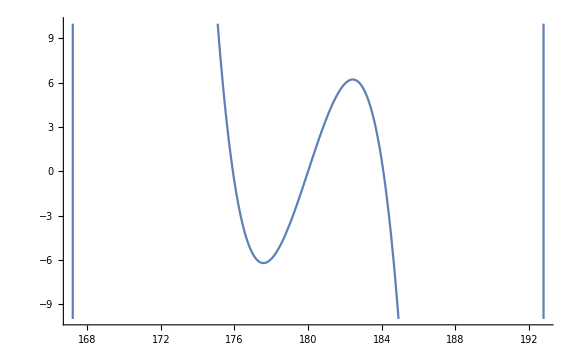

```mathematica
Plot[toDeg@getBilliardAngleTrilin[2,t,getX88Trilin],{t,180-25,180+25},ImageSize->Large,PlotRange->{All,{-10,10}}]
```

#### P1=(a cos t, sint) dado (x,y), qual o t: tan^-1(y/a x) t’ = a (y’ x - x’ y)/(a^2 x^2 + y^2) θ’ = (y' x - x' y)/(x^2 + y^2)

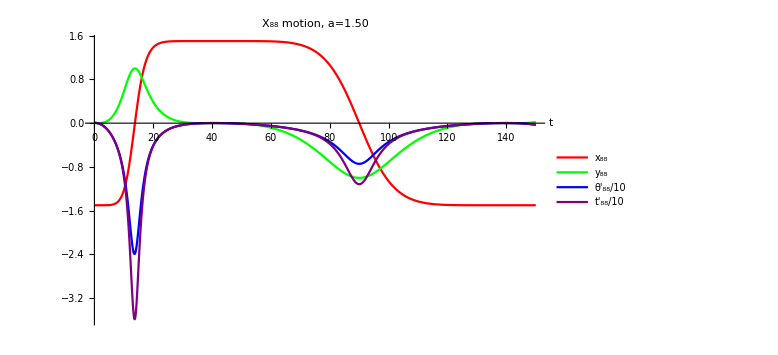

```mathematica
Module[{a=1.5,ts,xy,x,y,xdot,ydot,thdot,tdot,thlim=150,tstep=.1},
ts=Range[0,thlim,tstep];
xy=getTrilinXY[a,#,getX88Trilin]&/@ts;
x=First/@xy;
y=Second/@xy;
xdot=Differences[x]/toRad@tstep;
ydot=Differences[y]/toRad@tstep;
thdot=(ydot*Rest@x-xdot*Rest@y)/(Rest[x^2+y^2]);
tdot=a(ydot*Rest@x-xdot*Rest@y)/(Rest[a x^2+y^2]);
ListLinePlot[{Transpose@{ts,x},Transpose@{ts,y},Transpose@{Rest@ts,thdot/10},Transpose@{Rest@ts,tdot/10}},PlotStyle->{Red,Green,Blue,Purple},ImageSize->Large,AxesLabel->{"t",""},PlotRange->All,
PlotLabel->Style["X_88 motion, a="<>nfn[a,2],20],PlotLegends->(Style[#,20]&/@{"x_88","y_88","θ'_88/10","t'_88/10"})]]
```

#### Find Billiard Aspect Ratio for which X88 is on one vertex and X4 on another (right triangle)

```mathematica
Clear@x88err;
x88err[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,x88},
{o,n,s}=orbitNormals[a,toRad@tDeg];
x88=getX88Trilin[o,s];
magn2[o[[1]]-x88]]
```

```mathematica
FindMinimum[{x88err[1.5,tDeg]},{tDeg,20.5}]
```

{2.69178×10^-16,{tDeg→20.4318}}

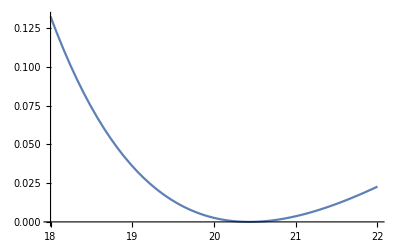

```mathematica
Plot[x88err[1.5,tDeg],{tDeg,18,22}]
```

```mathematica
(* for the x88 on vertex and right tri *)
Clear@x88errRect;
x88errRect[a_?NumericQ,tDeg_?NumericQ]:=Module[{o1,n1,s1,x88,x4,},
{o1,n1,s1}=orbitNormals[a,toRad@tDeg];
x88=getX88Trilin[o1,s1];
x4=getOrthocenterTrilin[o1,s1];
magn2[o1[[1]]-x88]+magn2[o1[[2]]-x4]];
```

```mathematica
FindMinimum[{x88errRect[a,tDeg],a>1.3&&a<1.5&&tDeg>23&&tDeg<24},{{a,1.4},{tDeg,23.5}}]
```

{3.13439×10^-9,{a→1.3924,tDeg→23.934}}

#### Ronaldo : X88 e X100, ponto medio, locus

```mathematica
Clear@getX88objs;
getX88objs[a_?NumericQ,t_?NumericQ]:=Module[{o,n,s,x1,x88,x100,mid},
{o,n,s}=orbitNormals[a,t];
x1=getIncenterTrilin[o,s];
x88=getX88Trilin[o,s];
x100=getX100Trilin[o,s];
mid=(x88+x100)/2;
{x1,x88,x100,mid}];
```

```mathematica
(* not sure how to add colors to list *)
```

```mathematica
Clear@showMid88to100;
showMid88to100[a_]:=
ListLinePlot[Transpose@Table[getX88objs[a,th],{th,0,2π,π/1000}]//Evaluate,
PlotLegends->{"x1","x88","x100","(x88+x100)/2"},AspectRatio->Automatic,Frame->True,FrameStyle->Medium,PlotRange->All,PlotLabel->Style["a="<>nfn[a,2],16]]
```

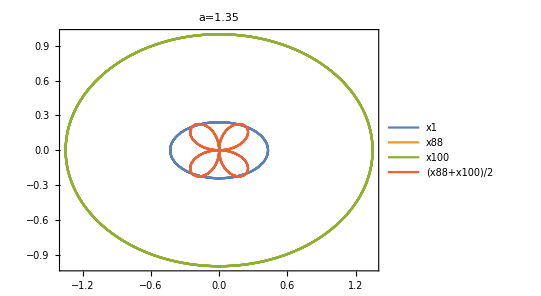

```mathematica
showMid88to100[1.35]
```

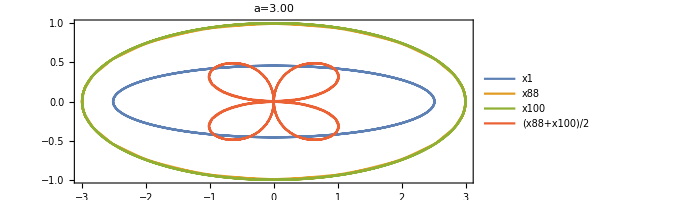

```mathematica
showMid88to100[3.]
```

## X59 four loops

#### X1, X100, X59, X88 are aligned

```mathematica
lawOfCosines[a,b,c]
```

(0.5 (-a^2+b^2+c^2))/(b c)

```mathematica
Module[{cosA,cosB,cosC,sinA,sinB,sinC,x59t1,x59t2,x59t3,a=1},
{cosA,cosB,cosC}={lawOfCosinesSymbol[a,b,c],lawOfCosinesSymbol[b,a,c],lawOfCosinesSymbol[c,a,b]};
{sinA,sinB,sinC}=getSinSymbol/@{cosA,cosB,cosC};
x59t1=FullSimplify[1/(1-cosB cosC-sinB sinC ),a>0&&b>a&&c>a];
x59t2=FullSimplify[1/(1-cosC cosA-sinC sinA ),a>0&&b>a&&c>a];
x59t3=FullSimplify[1/(1-cosA cosB-sinA sinB ),a>0&&b>a&&c>a];
Factor@FullSimplify[Det[{{1,1,1},
{1/(b-c),1/(c-a),1/(a-b)},
{x59t1,x59t2,x59t3}}]==0,b>0&&c>0]]
```

(2-3 b-2 b^2+6 b^3-2 b^4-3 b^5+2 b^6-3 c+8 b c-5 b^2 c-5 b^3 c+8 b^4 c-3 b^5 c-5 b c^2+10 b^2 c^2-5 b^3 c^2+2 c^3-b c^3-b^2 c^3+2 b^3 c^3-2 c^4-2 b^2 c^4+c^5+b c^5)/((-1+b) (-1+b-c) (b-c) (1+b-c) (-1+c) (-1+b+c))==(2 c)/(-1+b)

```mathematica
plotX59Yerror[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,x59},
{o,n,s}=orbitNormals[a,toRad@tDeg];
x59=getX59Trilin[o,s];
x59[[1]]^2]
```

```mathematica
FindMinimum[{plotX59Yerror[1.5,tDeg]},{tDeg,23.5}]
```

{7.00857×10^-16,{tDeg→29.085}}

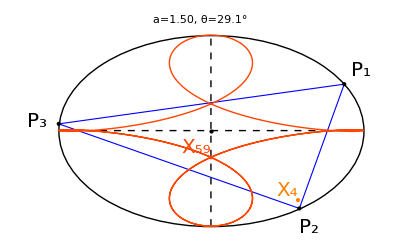

```mathematica
plotX59[1.5,deg1->29.085,drX4->True]
```

```mathematica
sols59=Table[FindMinimum[{plotX59Yerror[a,tDeg],tDeg>27&&tDeg<35},{tDeg,28.}],{a,1.2,1.5,.05}]
```

{{0.0228916,{tDeg→27.}},{7.49975×10^-11,{tDeg→33.5399}},{9.14886×10^-12,{tDeg→32.5263}},{2.76811×10^-14,{tDeg→31.5815}},{1.53697×10^-13,{tDeg→30.6974}},{1.0404×10^-15,{tDeg→29.8671}},{2.10419×10^-11,{tDeg→29.085}}}

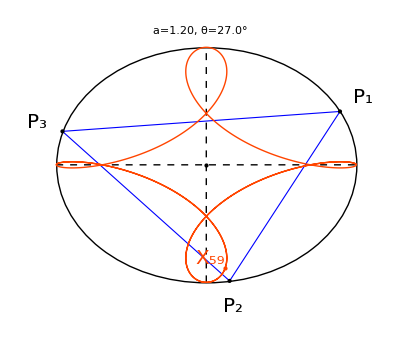
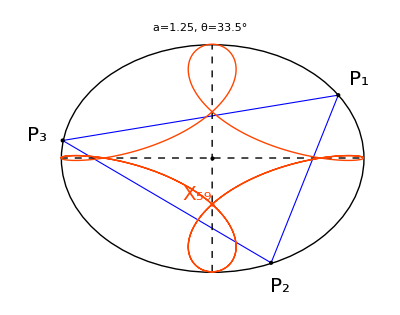
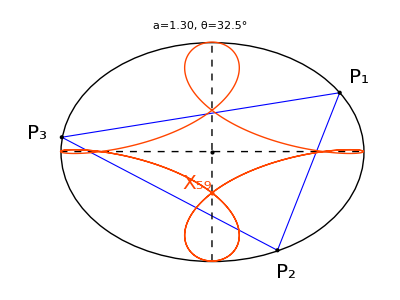
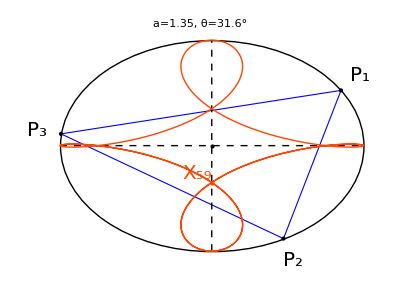
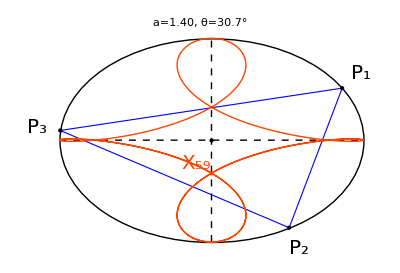
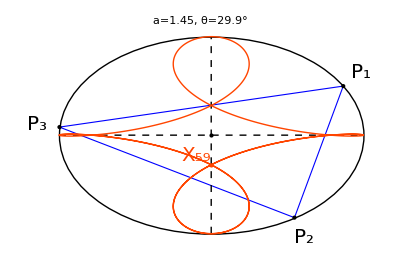
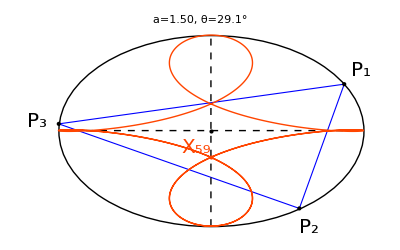

```mathematica
MapThread[plotX59[#1,deg1->#2]&,{Range[1.2,1.5,.05],(tDeg/.Second@#)&/@sols59}]
```

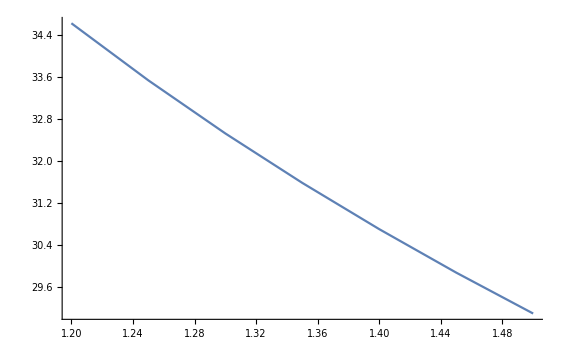

```mathematica
ListLinePlot[Transpose@{Range[1.2,2.0,.05],(tDeg/.Second@#)&/@sols59}]
```

```mathematica
plotX59YerrorRightTriangle[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,x59,x4},
{o,n,s}=orbitNormals[a,toRad@tDeg];
x59=getX59Trilin[o,s];
x4=getOrthocenterTrilin[o,s];
x59[[1]]^2+magn2[x4-o[[2]]]]
```

```mathematica
FindMinimum[{plotX59YerrorRightTriangle[a,tDeg],a>1.5&&a<2.},{{a,1.51},{tDeg,23.5}}]
```

{1.41212×10^-13,{a→1.58005,tDeg→27.9211}}

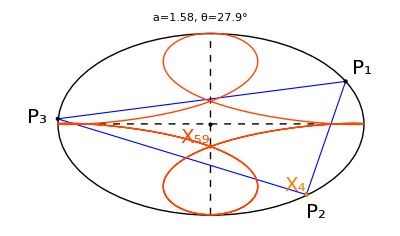

```mathematica
plotX59[1.58005,deg1->27.9211,drX4->True]
```

## X26: explodes when orbit is right triangle

```mathematica
ptClrs
```

{ell→-Graphics-,med→-Graphics-,bar→-Graphics-,inc→-Graphics-,ort→-Graphics-,cir→-Graphics-,npc→-Graphics-,exc→-Graphics-,ex12→-Graphics-,ex23→-Graphics-,ex31→-Graphics-,dar→-Graphics-,feu→-Graphics-,antifeu→-Graphics-,anticompl→-Graphics-,steiner→-Graphics-,steinerinell→-Graphics-,x88→-Graphics-,nag→-Graphics-,mit→-Graphics-,sym→-Graphics-,bev→-Graphics-,ger→-Graphics-,spi→-Graphics-,nap→-Graphics-,hex→-Graphics-,red→-Graphics-,green→-Graphics-,blue→-Graphics-}

```mathematica
Clear@plotX26;
Options@plotX26={xdispl->{0,-1.5},lgt->.22,degStep->.1,degMax->180.};plotX26[a_,tDeg_,OptionsPattern[]]:=Module[{ons,o1,n1,s1,x26,x26locus,deg0=0.1,x3,tangTri,degs,poly1,ell,gr,clr={Blue,Thick},xclr="hex"/.ptClrs,fontSize=20},
degs=.01+Range[0,OptionValue@degMax-OptionValue@degStep,OptionValue@degStep];
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@tDeg];
x26=getX26Trilin[o1,s1];
x3=getCircumcenterTrilin[o1,s1];
x26locus=MapThread[getX26Trilin[#1,#2]&,{First/@ons,Third/@ons}];
tangTri=tangentialTriangle[o1,s1];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@clr,Polygon@o1,Point@o1,ellLabelPoints[a,o1,"P",fontSize,OptionValue@lgt]},
(*{Dashed,pclr,Thick,Line@{#,p1}&/@o1},*)
{Dashed,Black,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Point@{0,0}},
{xclr,Thick,Line@x26locus},
{xclr,Point@x26,Text[Style["X_26",fontSize],x26,OptionValue@xdispl],
{EdgeForm@{Dashed,Thick,Darker@Green},Polygon@tangTri,Darker@Green,Point@tangTri},
{Darker@Green,Thick,Circle[x26,magn[x26-tangTri[[1]]]]}},{"cir"/.ptClrs,Thick,Circle[x3,magn[x3-o1[[1]]]],Point@x3,Text[Style["X_3",fontSize],x3,OptionValue@xdispl]}
}];
Show[{ell,gr},PlotLabel->Style["a="<>nfn[a,2]<>", t="<>nfn[tDeg,1]<>"°",20]]];
```

```mathematica
Manipulate[Show[plotX26[1.25,tDeg,xdispl->{-1.5,0}],PlotRange->{{-2,6},{-4,5}}],{{tDeg,5},-180,180}]
```

```mathematica
Manipulate[Show[plotX26[1.25,tDeg,xdispl->{-1.5,0}],PlotRange->{{-2,6},{-4,5}}],{{tDeg,5},-180,180}]
```

```mathematica
Clear@showX26;
Options@showX26={"proj"->"none"};
showX26[a_,OptionsPattern[]]:=Module[{o,n,s,p},
Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
p=getX26Trilin[o,s];
p=Switch[OptionValue@"proj","stereo",Take[stereographicProj@@p,2],"spherical",sphereProj@@p,"spherical2",sphereProj2@@p,"spherical3",sphereProj3@@p,"logProj",logProj@@p,_,p];
p,{t,0,2π},Frame->True,FrameStyle->Medium,PlotRange->All,PlotLabel->Style["a="<>nfn[a,2],16]]]
```

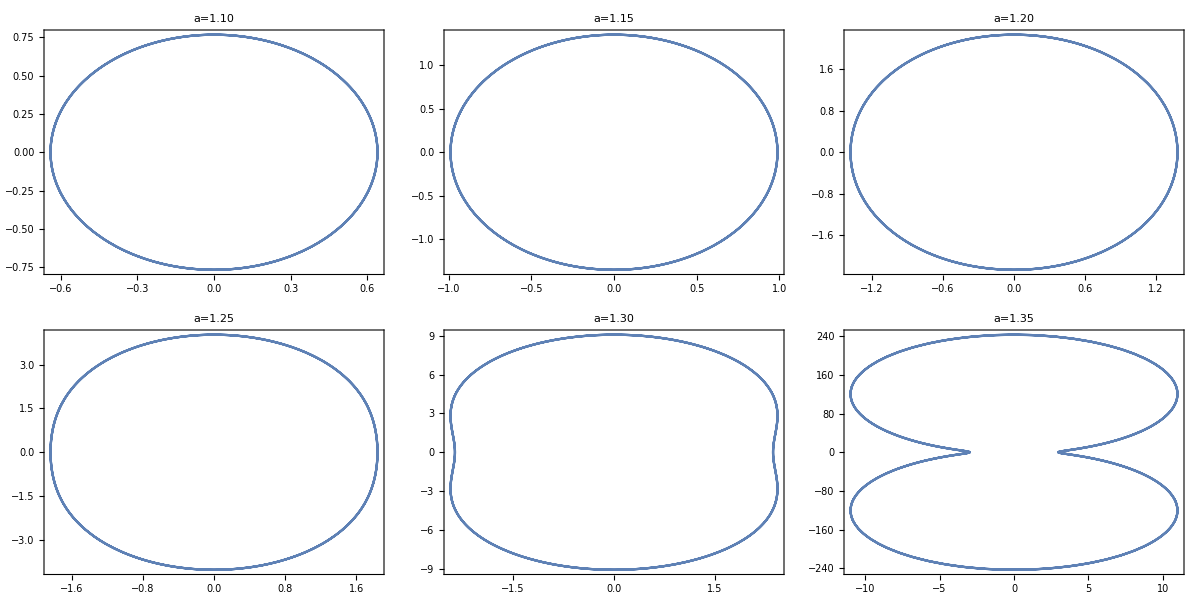

```mathematica
Partition[showX26/@Range[1.1,1.35,.05],3]//Grid
```

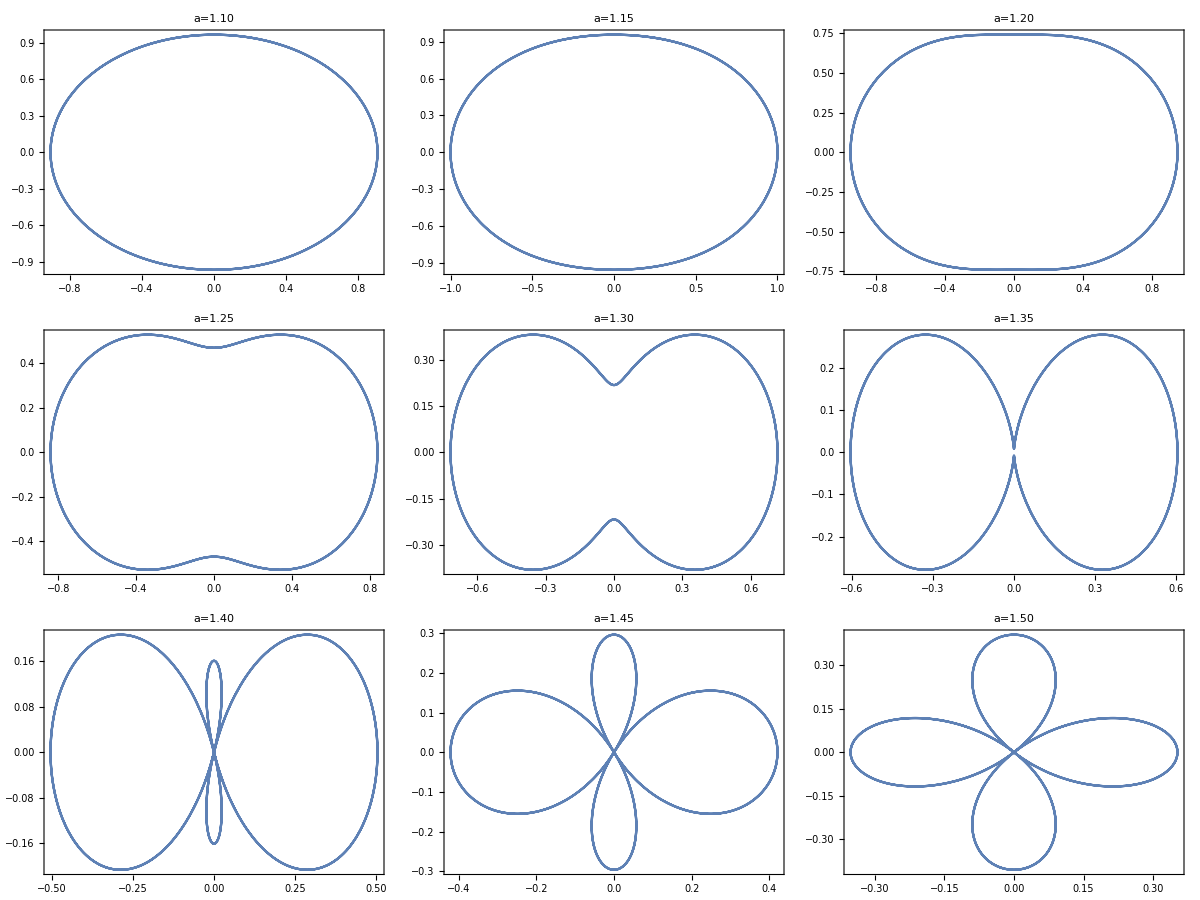

```mathematica
Partition[showX26[#,"proj"->"stereo"]&/@Range[1.1,1.5,.05],3]//Grid
```

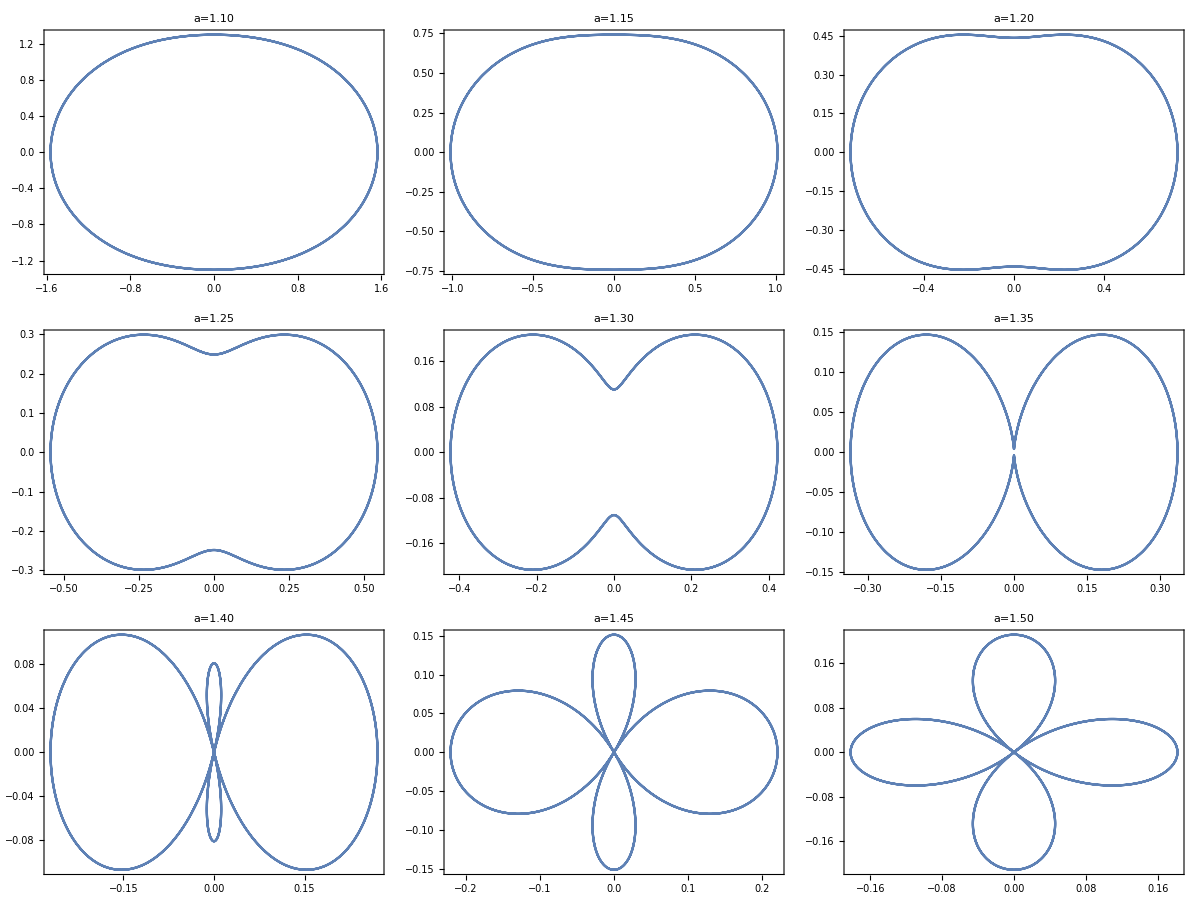

```mathematica
Partition[Show[showX26[#,"proj"->"spherical2"],AspectRatio->1]&/@Range[1.1,1.5,.05],3]//Grid
```

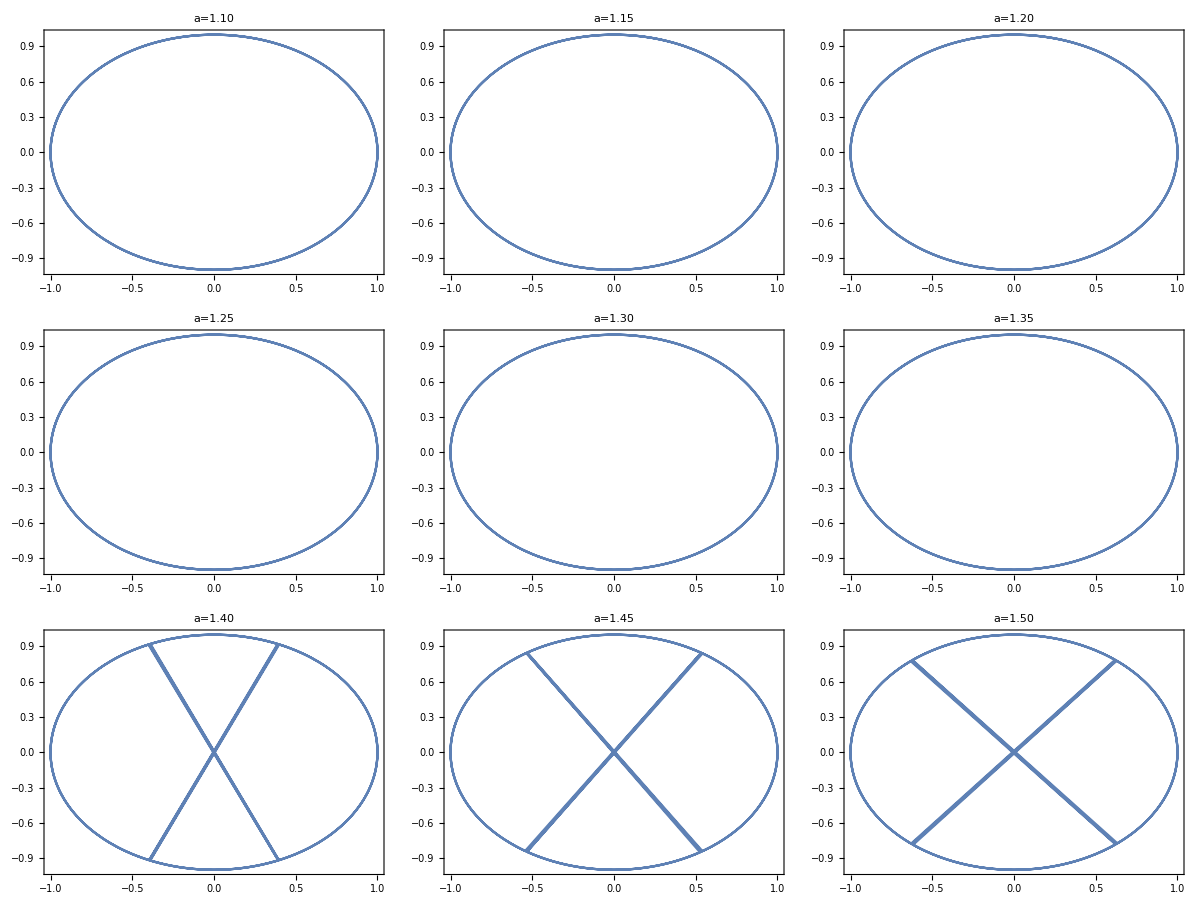

```mathematica
Partition[Show[showX26[#,"proj"->"spherical3"],AspectRatio->1]&/@Range[1.1,1.5,.05],3]//Grid
```

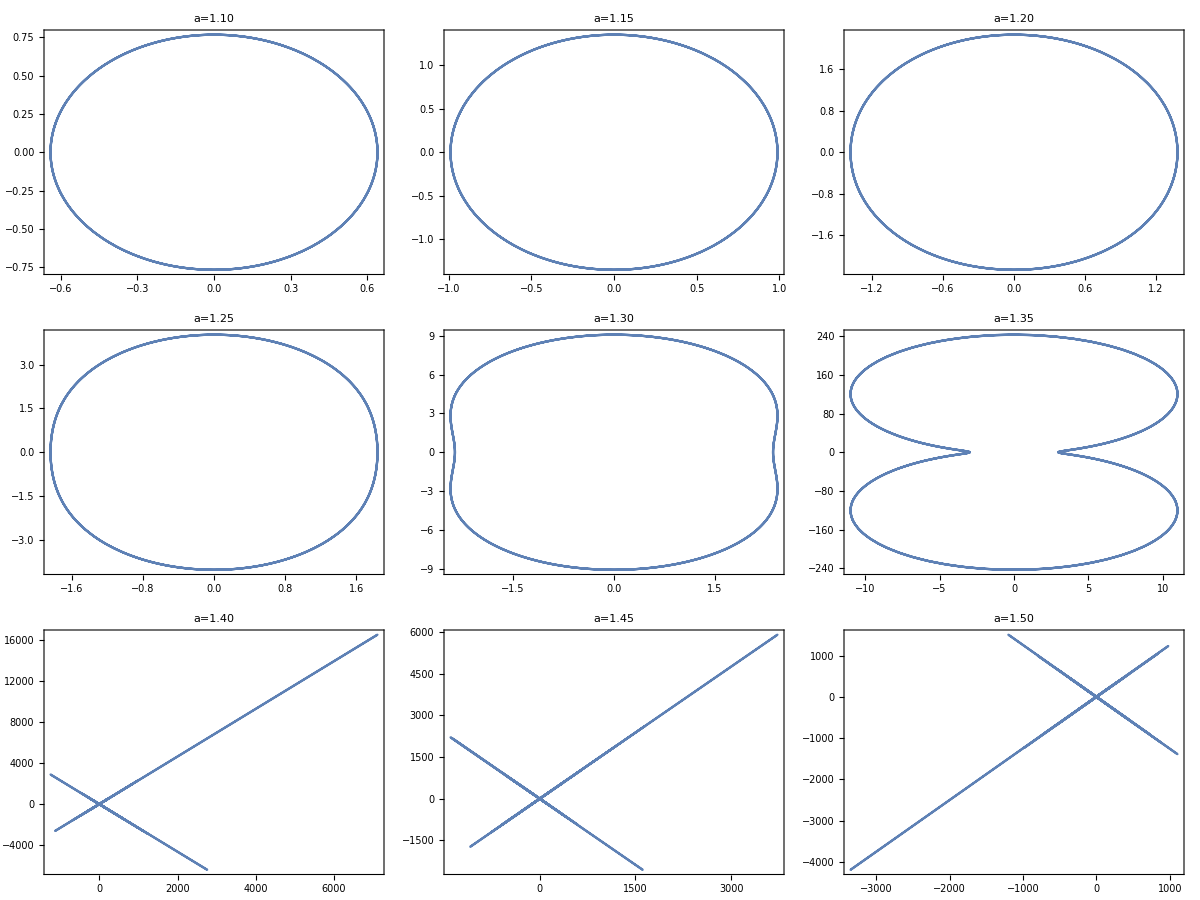

```mathematica
Partition[Show[showX26[#,"proj"->"logProj"],AspectRatio->1]&/@Range[1.1,1.5,.05],3]//Grid
```

## Incentral Triangle

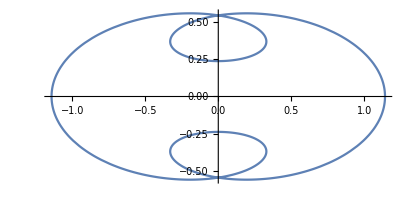

```mathematica
Module[{a=1.5,o,n,s,tri},
Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
tri=incentralTriangle[o,s];
tri[[1]],{t,0,2π}]]
```

## Ellipticity via Trilinears

```mathematica
getEllTrils[a_,t_]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,sinBC, cosBC,cosBmC,xell,xnonell},
{cosA,cosB,cosC}=getOrbitCosines[a,t];
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBC=cosB  cosC;
sinBC=sinB sinC;
cosBmC=cosBC+sinBC;
xell={
{2,cosA+cosBmC},
{3,cosA},
{4,cosA-cosBmC},
{5,cosBmC},
{7,1/(1+cosA)},
{20,cosA - cosBC}};
(*X(8):1/(1-cosA)
X(10):(cosB+cosC)/(1-cosA)
X(11):1-cos(B-C)
X(12):1+cos(B-C)
X(20):cosA-cosB cosC
X(21):1/(cosB+cosC)
X(35):1+2 cosA
X(36):1-2 cosA
X(40):cosB+cosC-cosA-1*)
xnonell={
{6,sinA},
{30,cosA-2 cosB cosC}
};
(*X(6):sinA[cosseno "fora de fase"]
X(13):1/cos(A-π/6)
X(14):1/cos(A+π/6)
X(15):cos(A-π/6)
X(16):cos(A+π/6)
X(17):1/cos(A-π/3)
X(18):1/cos(A+π/3)
X(19):tanA[ou:sin(2B)+sin(2C)-sin(2A)]
X(22):a(b^4+c^4-a^4)[quartica]
X(23):a(b^4+c^4-a^4-b^2 c^2)
X(24):cos2A/cosA
X(25):sinA tanA[ou:cosA-secA]
X(26):a[b^2 cos2B+c^2 cos2C-a^2 cos2A]
X(27):(secA)/(b+c)
X(28):(tanA)/(b+c)
X(29):(secA)/(cosB+cosC)
X(30):cosA-2 cosB cosC
X(31):1-cos2A
X(32):sin(A-ω)[ou:a^3]
X(33):1+1/cosA
X(34):1-1/cosA
X(37):b+c[angle form possible?]
X(38):sin(A+ω)/sinA
X(39):sin(A+ω)*)<|"xell"->xell,"xnonell"->xnonell|>];
```

{2,3,4,5,7,20}

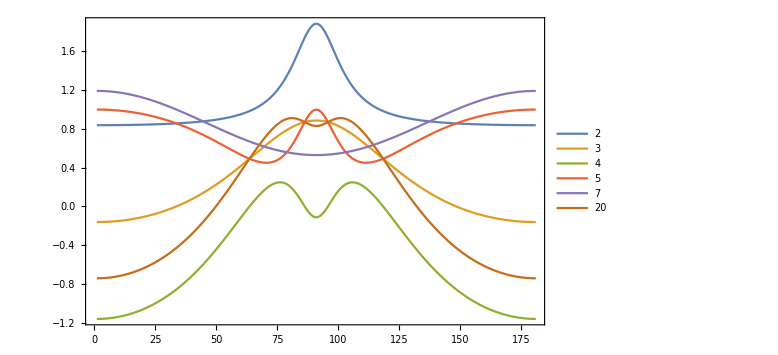
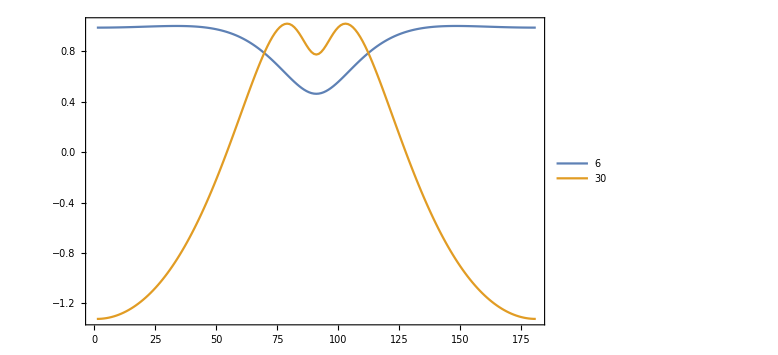

```mathematica
Module[{xs,xells,xnonells,plells,plnonells},
xs=Table[getEllTrils[1.5,toRad@tDeg],{tDeg,-90,90}];
xells=#["xell"]&/@xs;
xnonells=#["xnonell"]&/@xs;
plells=First/@Table[First/@Transpose[xells][[i]],{i,Length@Transpose@xells}];
plnonells=First/@Table[First/@Transpose[xnonells][[i]],{i,Length@Transpose@xnonells}];
Print@plells;
Grid[{
{ListLinePlot[Table[Second/@Transpose[xells][[i]],{i,Length@Transpose@xells}],PlotLegends->plells, Frame->True,ImageSize->Large]},
{ListLinePlot[Table[Second/@Transpose[xnonells][[i]],{i,Length@Transpose@xnonells}],PlotLegends->plnonells,Frame->True,ImageSize->Large]}}]
]
```

## Figures for Intelligencer and L’Enseignement Mathématique (EPS, PDF)

```mathematica
export3[name_,plot_]:=Module[{subdir="pics/"},
Export[subdir<>name<>".pdf",plot];
Export[subdir<>name<>".eps",plot];
Export[subdir<>name<>".png",plot];
];
```

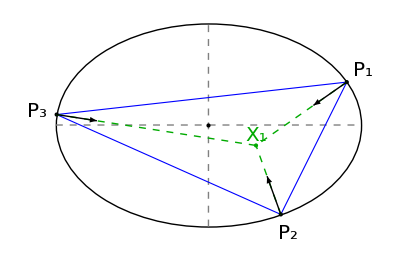

```mathematica
singleOrbitPlot=Module[{a=1.5,ons,deg1=25,poly1,ell,gr,grads1,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.2,inc,fontSize=20},
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@deg1];
poly1=ons[[1]];
inc=getIncenterTrilin[First@ons,Third@ons];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{EdgeForm@clr,Polygon@poly1,Point@poly1,ellLabelPoints[a,poly1,"P",{fontSize},lgt]},
{incClr,Point@inc,Text[Style["X_1",fontSize],inc,{0,-1.5}]},
{Dashed,incClr,Thick,Line@{#,inc}&/@poly1},
{Black,Thick,MapThread[Arrow@{#1,#1+2lgt*norm@#2}&,{poly1,grads1}]}
}];
Show[{ell,gr}]]
```

```mathematica
export3["0000_single_orbit",singleOrbitPlot]
```

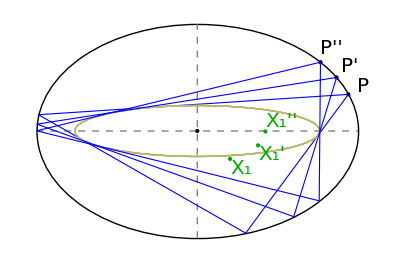

```mathematica
threeOrbitsPlot=Module[{a=1.5,ons,deg0=20,degStep=10,degRange=3,degs,poly1,caustic,ell,gr,grads1,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.33,incs,fontSize=20},
degs=(deg0+(#-1)*degStep)&/@Range@degRange;
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
poly1=ons[[1,1]];
incs=MapThread[getIncenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
caustic=Module[{o,n,s},Table[{o,n,s}=orbitNormals[a,toRad@i];getFeuerbachTrilin[o,s],{i,0,359}]];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{EdgeForm@clr,Polygon@poly1,Point[First/@First/@ons]},
{"feu"/.ptClrs,Thick,Line@caustic},
{MapThread[ellLabelTxt[a,#1,Style[#2,fontSize],.16]&,{First/@First/@ons,{"P","P'","P''"}}]},
{incClr,MapThread[Text[Style[#1,fontSize],#2,#3]&,{{"X_1","X_1'","X_1''"},incs,{{-1.1,1.1},{-1.25,.5},{-.5,-1.5}}}]},
{incClr,Point@incs(*,Thick,Line@incs*)},
{EdgeForm@{Dashed,Sequence@@clr},Polygon[First@#]&/@Rest@ons},
}];
Show[{ell,gr}]]
```

```mathematica
export3["0010_three_orbits",threeOrbitsPlot];
```

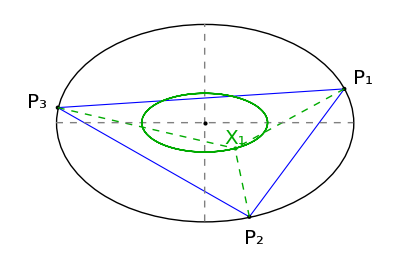

```mathematica
incenterLocusPlot=Module[{a=1.5,ons,o1,n1,s1,inc1,deg1=20,deg0=0,degStep=1,degRange=359,degs,poly1,ell,gr,grads1,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.22,incs,fontSize=20},
degs=(deg0+(#-1)*degStep)&/@Range@degRange;
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@deg1];
inc1=getIncenterTrilin[o1,s1];
incs=MapThread[getIncenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@clr,Polygon@o1,Point@o1,ellLabelPoints[a,o1,"P",fontSize,lgt]},
{Dashed,incClr,Thick,Line@{#,inc1}&/@o1},
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{incClr,Thick,Line@incs},
{incClr,Point@inc1,Text[Style["X_1",fontSize],inc1,{0,-1.5}]}
}];
Show[{ell,gr}]]
```

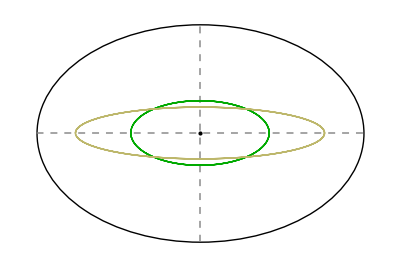

```mathematica
incenterLocusPlotClean=Module[{a=1.5,ons,o1,n1,s1,inc1,deg1=20,deg0=0,degStep=1,degRange=359,degs,poly1,ell,gr,grads1,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.22,incs,fontSize=20,caustic},
degs=(deg0+(#-1)*degStep)&/@Range@degRange;
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@deg1];
inc1=getIncenterTrilin[o1,s1];
incs=MapThread[getIncenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
caustic=Module[{o,n,s},Table[{o,n,s}=orbitNormals[a,toRad@i];getFeuerbachTrilin[o,s],{i,0,359}]];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
(*{EdgeForm@clr,Polygon@o1,Point@o1,ellLabelPoints[a,o1,"P",fontSize,lgt]},*)
(*{Dashed,incClr,Thick,Line@{#,inc1}&/@o1},*)
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{incClr,Thick,Line@incs},
{"feu"/.ptClrs,Thick,Line@caustic}
(*,{incClr,Point@inc1,Text[Style["X_1",fontSize],inc1,{0,-1.5}]}*)
}];
Show[{ell,gr}]]
```

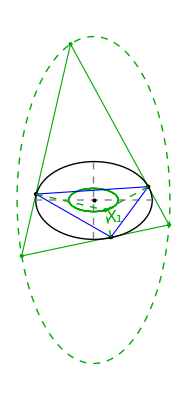

```mathematica
excenterLocusPlot=Module[{a=1.5,ons,deg1=20,poly1,ell,gr,grads1,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.33,inc,exc,incExc,grExc,fontSize=20},
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@deg1];
exc=excentralTriangle[ons[[1]],ons[[3]]];
poly1=ons[[1]];
inc=getIncenterTrilin[First@ons,Third@ons];
incExc=Transpose@Module[{o,n,s},
Table[{o,n,s}=orbitNormals[a,toRad@i];{getIncenterTrilin[o,s],excentralTriangle[o,s][[1]]},{i,0,359}]];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{EdgeForm@clr,Polygon@poly1,Point@poly1},
{incClr,Point@inc,Text[Style["X_1",16],inc,{-1.5,.75}]},
{Dashed,incClr,Line@{#,inc}&/@poly1}
}];
grExc=Graphics[{Thick,FaceForm@None,EdgeForm@{Thick,incClr},incClr,PointSize@Large,Point@exc,Polygon@exc,Line@incExc[[1]],Dashed,Line@incExc[[2]]}];
Show[{grExc,ell,gr}]]
```

```mathematica
export3["0019_excenter_locus",excenterLocusPlot];
```

```mathematica
export3["0020_incenter_locus",incenterLocusPlot];
```

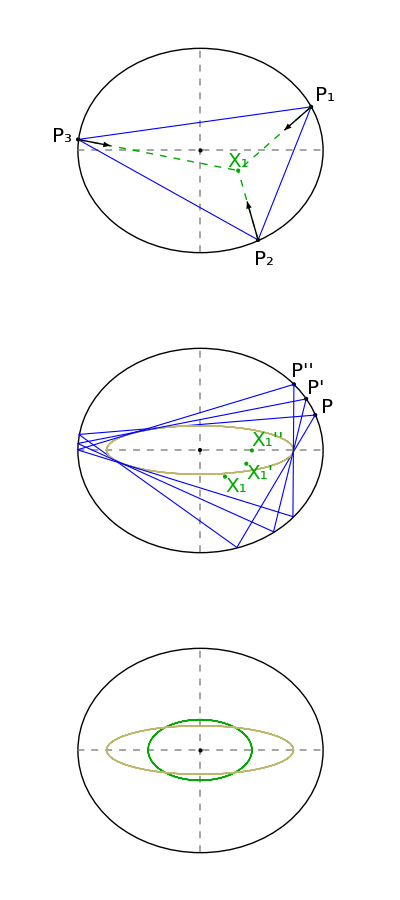
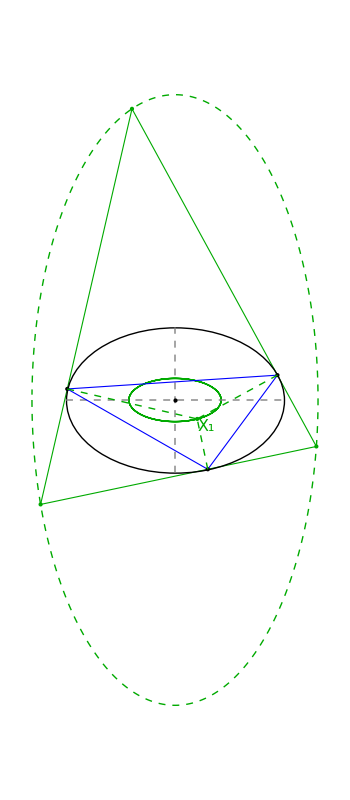
-Graphics- | -Graphics-

```mathematica
incenterLocusQuad=Grid[{{Grid[{Show[#,PlotRange->{{-2,2},{-1.2,1.2}},ImageSize->400]}&/@{singleOrbitPlot,threeOrbitsPlot,incenterLocusPlotClean},Spacings->0],Show[excenterLocusPlot,PlotRange->{Automatic,{-4.5,4.5}},ImageSize->350]}},Spacings->3,Frame->All]
```

```mathematica
export3["0021_incenter_locus_quad",incenterLocusQuad];
```

#### X59

```mathematica
Clear@plotX59;
Options@plotX59={drX4->False,deg1->20.,x59displ->{0,-1.5},lgt->.22,degStep->.1,degMax->180.};plotX59[a_,OptionsPattern[]]:=Module[{ons,o1,n1,s1,x59,x4,deg0=0.1,degs,poly1,ell,gr,grads1,clr={Blue,Thick},pclr="x59"/.ptClrs,ps,fontSize=20},
degs=.01+Range[0,OptionValue@degMax-OptionValue@degStep,OptionValue@degStep];
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@OptionValue@deg1];
x59=getX59Trilin[o1,s1];
x4=getOrthocenterTrilin[o1,s1];
ps=MapThread[getX59Trilin[#1,#2]&,{First/@ons,Third/@ons}];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@clr,Polygon@o1,Point@o1,ellLabelPoints[a,o1,"P",fontSize,OptionValue@lgt]},
(*{Dashed,pclr,Thick,Line@{#,p1}&/@o1},*)
{Dashed,Black,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Point@{0,0}},
{pclr,Thick,Line@ps},
{pclr,Point@x59,Text[Style["X_59",fontSize],x59,OptionValue@x59displ]},
If[OptionValue@drX4,{Purple,Point@x4,Text[Style["X_4",fontSize],x4,{1,-1.25}]},{}]
}];
Show[{ell,gr},PlotLabel->Style["a="<>nfn[a,2]<>", t="<>nfn[OptionValue@deg1,1]<>"°",20]]];
```

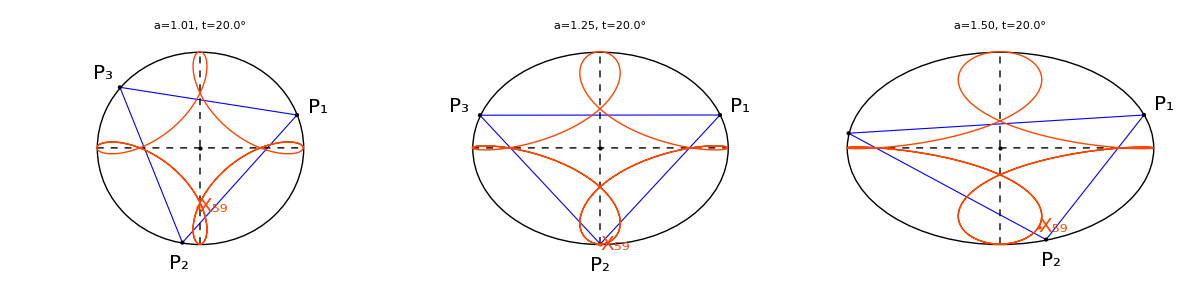

```mathematica
x59Plot=Module[{as},
Grid[{Show[plotX59[#,deg1->20,x59displ->{-1.5,0}],PlotRange->{{-1.6,1.6},{-1.3,1.1}},ImageSize->400]&/@{1.01,1.25,1.5}}]
]
```

```mathematica
export3["0050_x59_locus",x59Plot];
```

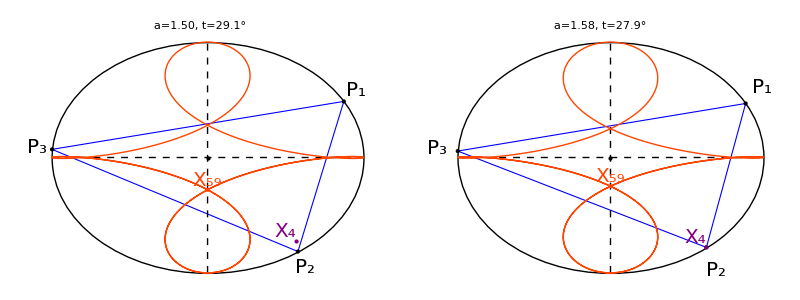

```mathematica
x59crossPlot=Grid[{Show[#,ImageSize->400]&/@{plotX59[1.5,deg1->29.085,drX4->True,x59displ->{0,-1.5},lgt->.15],plotX59[1.58005,deg1->27.9211,drX4->True]}}]
```

```mathematica
export3["0050_x59_center",x59crossPlot];
```

```mathematica
Clear@x88motion;
Options@x88motion={drX4locus->False,x4disp->{-1.25,1.25},drSides->False};x88motion[a_,tDeg_,OptionsPattern[]]:=Module[{o1,n1,s1,x88,x4,x100,x1,poly1,ell,rho,gr,clr={Blue,Thick},lgt=.2,incClr="inc"/.ptClrs,x100Clr=Black,x88Clr="x88"/.ptClrs,ortClr="ort"/.ptClrs,x4locus,mid,sidesLab},
ell=plotEll[a,{Thick,Black}];
{o1,n1,s1}=orbitNormals[a,toRad@tDeg];
x1=getIncenterTrilin[o1,s1];
x100=getX100Trilin[o1,s1];
x88=getX88Trilin[o1,s1];
x4=getOrthocenterTrilin[o1,s1];
x4locus=If[OptionValue@drX4locus,Quiet@Module[{ons},ParametricPlot[ons=orbitNormals[a,t];getOrthocenterTrilin[ons[[1]],ons[[3]]],{t,0.01,π},PlotStyle->{Thick,ortClr}]],{}];
rho=magn[x1-x100]/magn[x1-x88];
mid=medialTriangle[o1,s1];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@incClr,FaceForm@{Opacity@.1,incClr}},
{EdgeForm@clr,Polygon@o1,Point@o1(*,ellLabelPoints[a,o1,"P",{Bold,16},.15]*)},
(*{Dashed,incClr,Line@{#,inc1}&/@o1},*)
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{Dashed,Darker@Red,Thick,Line@{x100,x88}},
{incClr,Point@x1,Text[Style["X_1",20],x1,{0,-1.5}]},
{ortClr,Point@x4,Text[Style["X_4",20],x4,OptionValue@x4disp]},
{x100Clr,Point@x100,ellLabelTxt[a,x100,Style["X_100",20],lgt]},
{x88Clr,Point@x88,ellLabelTxt[a,x88,Style["X_88",20],lgt]},
If[OptionValue@drSides,{Blue,Point@mid,
ellLabelPointsSuffixb[a,a,mid,"s","="<>nfn[#,2]&/@s1,16]
(*ellLabelPoints[a,mid,"s",20,OptionValue@lgt]*)},{}]
}];
sidesLab=If[OptionValue@drSides,"\n(s_1,s_2,s_3)=("<>nfn[s1[[1]],2]<>","<>nfn[s1[[2]],2]<>","<>nfn[s1[[3]],2]<>")",""];
Show[{ell,x4locus,gr},PlotLabel->Style["a="<>nfn[a,2]<>", t="<>nfn[tDeg,2]<>"°, ρ="<>nfn[rho,2],{Black,20}]]]
```

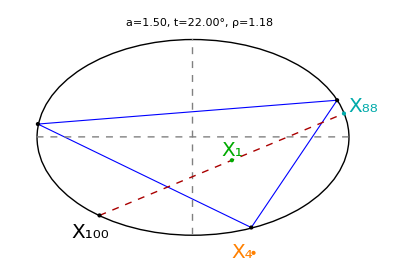

```mathematica
x88at15unalignedplot=x88motion[1.5,22,x4disp->{1.25,0},drSides->False]
```

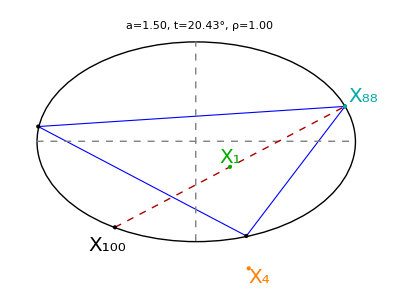

```mathematica
x88at15plot=x88motion[1.5,20.432,drSides->False]
```

### at 3:4:5 configuration

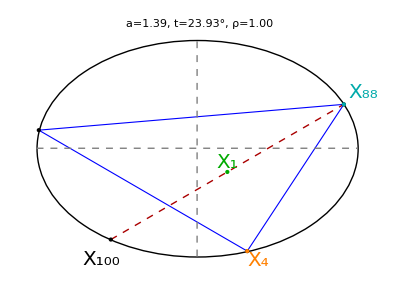

```mathematica
x88rightPlot=x88motion[1.3924,23.934,drSides->False]
```

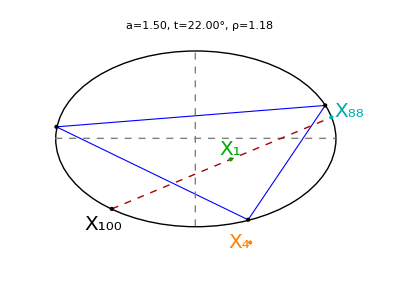
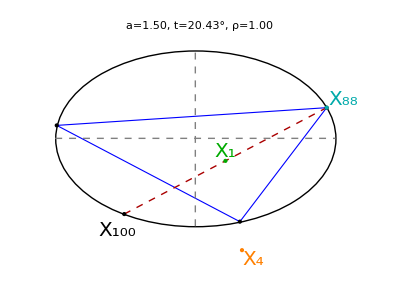
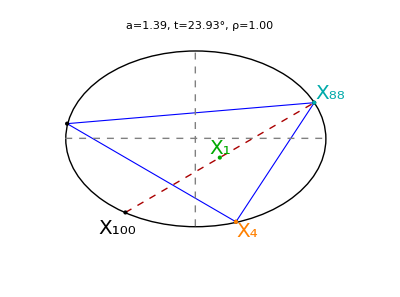
-Graphics- | -Graphics- | -Graphics-
(a) | (b) | (c)

```mathematica
x88both=Grid[{Show[#,PlotRange->{{-1.7,1.8},{-1.5,1.1}},ImageSize->400]&/@{x88at15unalignedplot,x88at15plot,x88rightPlot},Style[#,20]&/@{"(a)","(b)","(c)"}},Spacings->0]
```

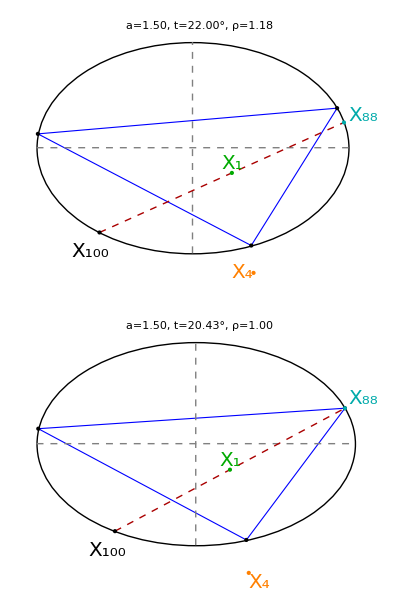
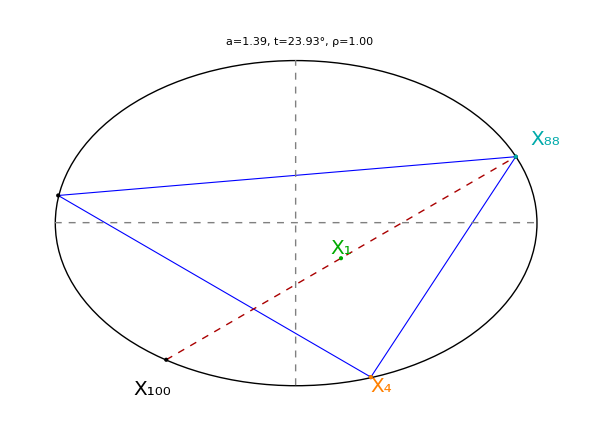
-Graphics- | -Graphics-

```mathematica
x88both2=Grid[{{Grid[{{Show[x88at15unalignedplot,ImageSize->400]},{Show[x88at15plot,ImageSize->400]}},Spacings->0],Show[x88rightPlot,ImageSize->600]}},Frame->All,Spacings->0]
```

```mathematica
export3["0052_x88_both",x88both2]
```

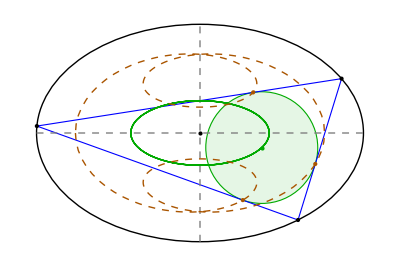

```mathematica
introPlot=Module[{a=1.5,ons,o1,n1,s1,inc1,ped1,deg100,deg1=30,degStep=1,degRange=360,degs,poly1,ell,gr,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.33,incs,peds,pedClr=Darker@Orange},
degs=Range[0,degRange,degStep];
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@deg1];
inc1=getIncenterTrilin[o1,s1];
ped1=intouchTriangle[o1,s1];
incs=getIncenterTrilin[#[[1]],#[[3]]]&/@ons;
peds=intouchTriangle[#[[1]],#[[3]]][[1]]&/@ons;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@incClr,FaceForm@{Opacity@.1,incClr},Disk[inc1,magn[ped1[[1]]-inc1]]},
{EdgeForm@clr,Polygon@o1,Point@o1(*,ellLabelPoints[a,o1,"P",{Bold,16},.15]*)},
(*{Dashed,incClr,Line@{#,inc1}&/@o1},*)
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Black,Point@{0,0}},
{incClr,Thick,Line@incs},
{pedClr,Point@ped1,Thick,Dashed,Line@peds},
{incClr,Point@inc1(*,Text[Style["X_1",16],inc1,{0,-1.5}]*)}
}];
Show[{ell,gr}]]
```

```mathematica
export3["0001_intro_plot",introPlot];
```

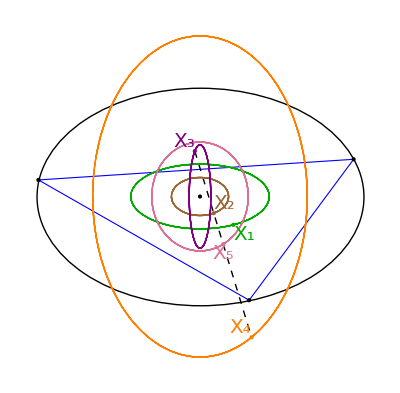

```mathematica
x12345Plot=Module[{a=1.5,ons,o1,n1,s1,inc1,bar1,cir1,ort1,,npc1,deg1=20,deg0=0,degStep=1,degRange=359,degs,poly1,ell,gr,clr={Blue,Thick},lgt=.33,incs,bars,cirs,orts,npcs,clrs,fontSize=20},
degs=(deg0+(#-1)*degStep)&/@Range@degRange;
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
{o1,n1,s1}=orbitNormals[a,toRad@deg1];
inc1=getIncenterTrilin[o1,s1];
bar1=getBarycenterTrilin[o1,s1];
cir1=getCircumcenterTrilin[o1,s1];
ort1=getOrthocenterTrilin[o1,s1];
npc1=getNinepointCenterTrilin[o1,s1];
incs=MapThread[getIncenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
bars=MapThread[getBarycenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
cirs=MapThread[getCircumcenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
orts=MapThread[getOrthocenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
npcs=MapThread[getNinepointCenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
clrs=#/.ptClrs&/@{"inc","bar","cir","ort","npc"};
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{EdgeForm@clr,Polygon@o1,Point@o1},
{Black,PointSize@Medium,Point@{0,0}},
{Black,Dashed,Line@{cir1,ort1}},
MapThread[{#1,Thick,Line@#2}&,{clrs,{incs,bars,cirs,orts,npcs}}],
MapThread[{#1,Point@#2,Text[Style[Subscript["X",#3],fontSize],#2,#4]}&,
{clrs,{inc1,bar1,cir1,ort1,npc1},{1,2,3,4,5},
{{-1.25,1.2},{-1.25,-1},{1.25,-.6},{1.25,-1.},{.25,1.25}}}]
}];
Show[{ell,gr}]]
```

```mathematica
export3["0030_x12345_locus",x12345Plot];
```

```mathematica
Clear@showOrt;
Options@showOrt={p1Dist->.125,drOrthic->False,drP1->True,drOrthicLocus->False,orthicLocusThickness->.0125,x4displ->{1.25,-1.25},drAlts->False};
showOrt[a_,tDeg_,OptionsPattern[]]:=Module[{ons,o1,n1,s1,ort1,degStep=.5,degs,poly1,ell,gr,grads1,clr={Blue,Thick},lgt=.33,orts,clrs,orthic,orthicLocus,ortFeet},
degs=Range[0,360-degStep,degStep];
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@#]&/@degs;
orthicLocus=If[OptionValue@drOrthicLocus,(orthic=orthicTriangle[#[[1]],#[[3]]]; getIncenterTrilin[orthic,RotateLeft@triLengths@orthic])&/@ons,{}];
{o1,n1,s1}=orbitNormals[a,toRad@tDeg];
ort1=getOrthocenterTrilin[o1,s1];
ortFeet=orthicTriangle[o1,s1];
orts=MapThread[getOrthocenterTrilin[#1,#2]&,{First/@ons,Third/@ons}];
orthic=orthicTriangle[o1,s1];
grads1=ellGrad[a,Sequence@@#]&/@poly1;
clrs=#/.ptClrs&/@{"ort"};
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Gray,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}},Point@{0,0}},
MapThread[{#1,Thick,Line@#2}&,{clrs,{orts}}],
MapThread[{#1,Point@#2,Text[Style[Subscript["X",#3],{Bold,20}],#2,#4]}&,
{clrs,{ort1},{4},
{OptionValue@x4displ}}],
If[OptionValue@drP1,{Black,ellLabelTxt[a,o1[[1]],Style["P_1(t)",{Bold,16}],OptionValue@p1Dist]},{}],
If[OptionValue@drOrthic,{EdgeForm@{Thick,Purple},Polygon@orthic,Purple,Point@orthic}],
If[OptionValue@drOrthicLocus,{Thickness@OptionValue@orthicLocusThickness,Purple,Line@orthicLocus}],
If[OptionValue@drAlts,{Thick,PointSize@Medium,Point@ortFeet,Dashed,Blue,MapThread[Line@{#1,#2}&,{o1,RotateLeft@ortFeet}],Orange,Line@{#,ort1}&/@o1},{}],
{EdgeForm@clr,Polygon@o1,Point@o1}
}];
Show[{ell,gr},PlotLabel->Style["a/b="<>nfn[a,2],20]]]
```

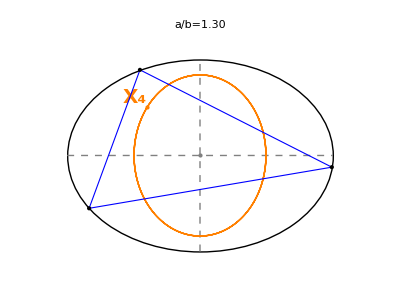
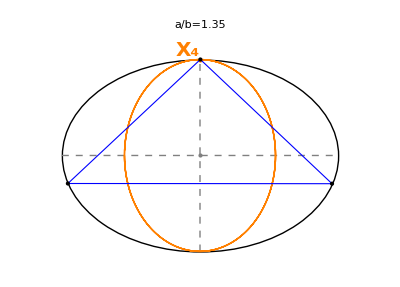
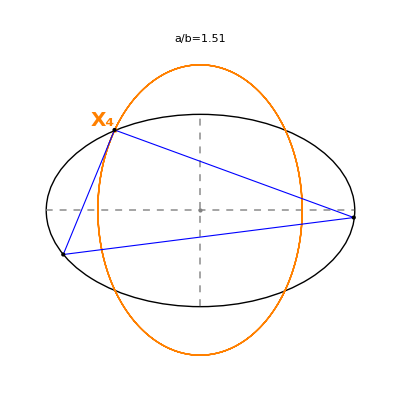
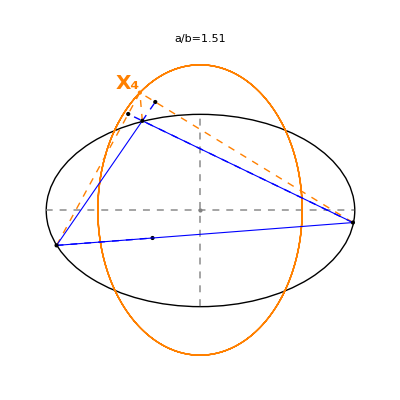
-Graphics-
(a) | -Graphics-
(b)
-Graphics-
(c) | -Graphics-
(d)

```mathematica
orthicLociPlot=Module[{orts},
orts={
showOrt[1.3,-7,drP1->False,p1Dist->.25],
showOrt[1.352,-17.1,drP1->False,p1Dist->.25],
showOrt[1.51,-9.0+4.5,drP1->False,p1Dist->.25],
showOrt[1.51,-9.0+1.5,drP1->False,p1Dist->.25,drAlts->True]
};
Grid[Partition[MapThread[Grid[{{Show[#1,PlotRange->{{-1.6,1.6},#3},ImageSize->400]},{#2}},Spacings->0]&,{orts,
Style[#,{Black,24}]&/@{"(a)","(b)","(c)","(d)"},{{-1.1,1.2},{-1.1,1.2},{-1.6,1.6},{-1.6,1.6}}}],2],Spacings->0]]
```

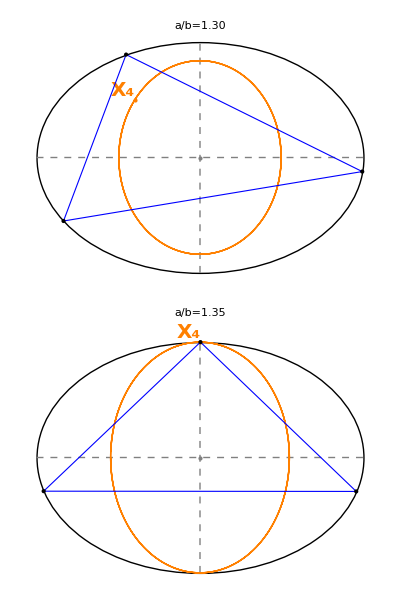
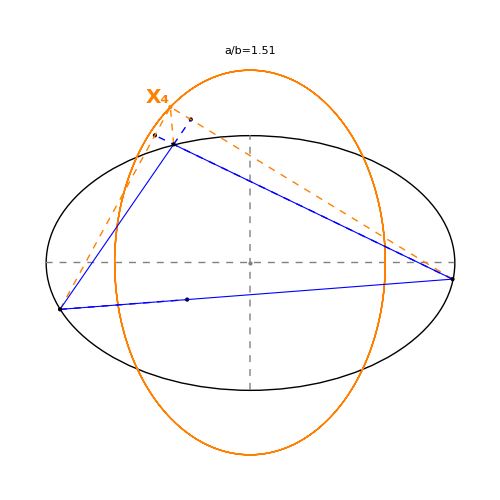
-Graphics- | -Graphics-

```mathematica
orthicLociPlot3=Module[{ort1,ort2,ort3},
ort1=showOrt[1.3,-7,drP1->False,p1Dist->.25];
ort2=showOrt[1.352,-17.1,drP1->False,p1Dist->.25];
ort3=showOrt[1.51,-9.0+1.5,drP1->False,p1Dist->.25,drAlts->True];
Grid[{{Grid[{{Show[ort1,ImageSize->300]},{Show[ort2,ImageSize->300]}},Spacings->0],Show[ort3,ImageSize->500]}},Spacings->0,Frame->All]]
```

```mathematica
export3["0045_ort_loci",orthicLociPlot3];
```

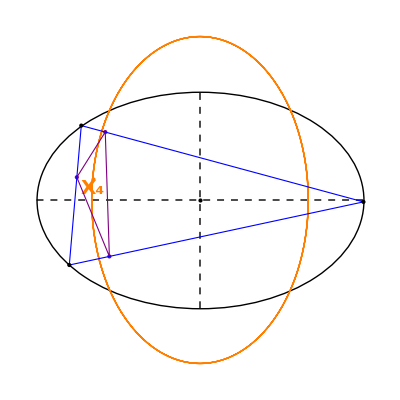
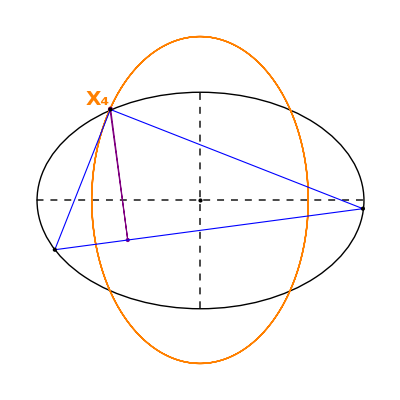
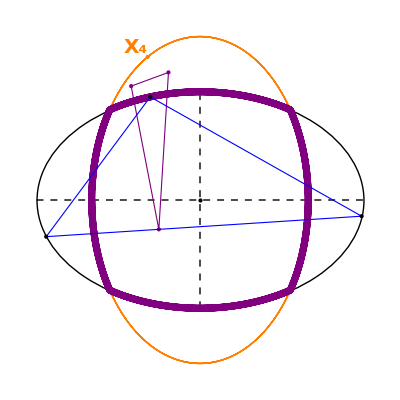
-Graphics- | -Graphics- | -Graphics-
(a) | (b) | (c)

```mathematica
orthicLociKinkPlot=Grid[{Show[#,ImageSize->400]&/@{
showOrt[1.51,-1,drP1->False,p1Dist->.25,drOrthic->True,x4displ->{0,1.25}],
showOrt[1.51,-9.1+4.5,drP1->False,p1Dist->.25,drOrthic->True],
showOrt[1.51,-13.1+4.5,drP1->False,p1Dist->.25,drOrthic->True,drOrthicLocus->True]},
Style[#,{Black,24}]&/@{"(a)","(b)","(c)"}}]
```

```mathematica
export3["0045_ort_loci_kink",orthicLociKinkPlot];
```

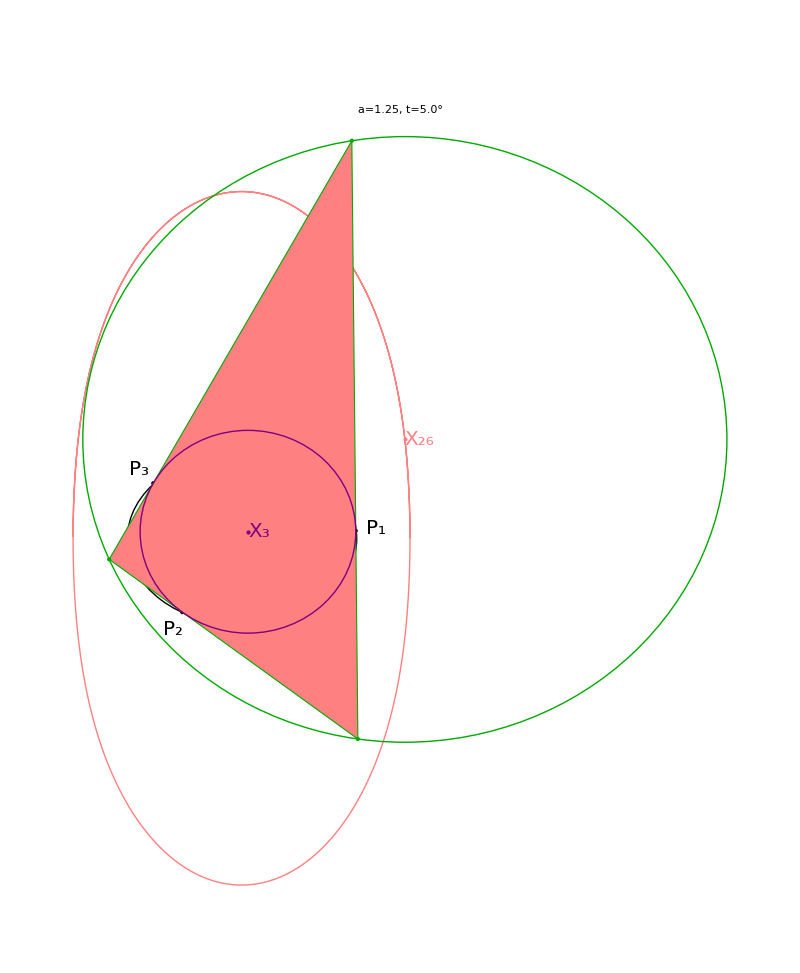

```mathematica
Show[plotX26[1.25,5.,xdispl->{-1.5,0}],PlotRange->All,Frame->None,ImageSize->800]
```

```mathematica
Clear@showMit;
Options@showMit={drEll->True,drNormals->False,drVtx->False,drExt->False,drFeuTri->False,lgt->.33,drMs->True,mSize->12,drCaustic->False,drExcPerps->False,drAxes->True};
showMit[a_,deg1_,OptionsPattern[]]:=Module[{ons,poly1,ell,gr,ext,meds,grads1,x5,feuTri,clr={Blue,Thick},incClr="inc"/.ptClrs,exc,mit,grExc,caustic},
ell=plotEll[a,{Thick,Black}];
ons=orbitNormals[a,toRad@deg1];
exc=excentralTriangle[ons[[1]],ons[[3]]];
ext=extouchTriangle[ons[[1]],ons[[3]]];
x5=getNinepointCenterTrilin[ons[[1]],ons[[3]]];
feuTri=feuerbachTriangle[ons[[1]],ons[[3]]];
poly1=ons[[1]];
meds=getMedians@@poly1;
grads1=ellGrad[a,Sequence@@#]&/@poly1;
caustic=Module[{o,n,s},Table[{o,n,s}=orbitNormals[a,toRad@i];getFeuerbachTrilin[o,s],{i,0,359}]];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,Arrowheads->Medium,
If[OptionValue@drAxes&&OptionValue@drEll,{Dashed,Black,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},{}],
If[OptionValue@drNormals,{Black,MapThread[Arrow@{#1,#1+OptionValue@lgt*norm[#2]}&,{poly1,grads1}]},{}],
{EdgeForm@clr,Polygon@poly1,Point@poly1},
If[OptionValue@drExcPerps,{Darker@Green,Dashed,Thick,MapThread[Line@{#1,#2}&,{exc,ext}]},{}],
If[OptionValue@drCaustic,{"feu"/.ptClrs,Thick,Line@caustic},{}],
If[OptionValue@drExt,{Darker@Green,Point@ext,
ellLabelPointsbInward[2a,a,ext,"e",OptionValue@mSize,OptionValue@lgt/2],
ellLabelPoints[2a,exc,"P'",OptionValue@mSize,OptionValue@lgt/2],
Dashed,Thick,MapThread[Circle[#1,magn[#1-#2]]&,{exc,ext}]},{}],
{Red,Dashed,Line@{#,ray[#,-#,1.5]}&/@exc},
If[OptionValue@drFeuTri,
{Pink,Thick,Circle[x5,magn[feuTri[[1]]-x5]],PointSize@Large,Point@feuTri},{}],
{Blue,Point@meds,If[OptionValue@drMs,MapThread[Text[Style[Subscript["M",#2],OptionValue@mSize],#1,#3]&,{meds,Range@Length@meds,
{{1,-1.5},{-1.5,-1.25},{-1.5,1.2}}}],{}]},
{Red,Point@{0,0},Text[Style["X_9",OptionValue@mSize],{0,0},{-1.5,-1.25}]},
If[OptionValue@drVtx,{Black,ellLabelPoints[a,poly1,"P",OptionValue@mSize,OptionValue@lgt/2]},,{}]
}];
grExc=Graphics[{Thick,FaceForm@None,EdgeForm@{Thick,incClr},incClr,PointSize@Large,Point@exc,Polygon@exc}];
Show[{grExc,If[OptionValue@drEll,ell,{}],gr},PlotRange->{{-2.2,2.2},{-4.2,4.2}},ImageSize->Large]]
```

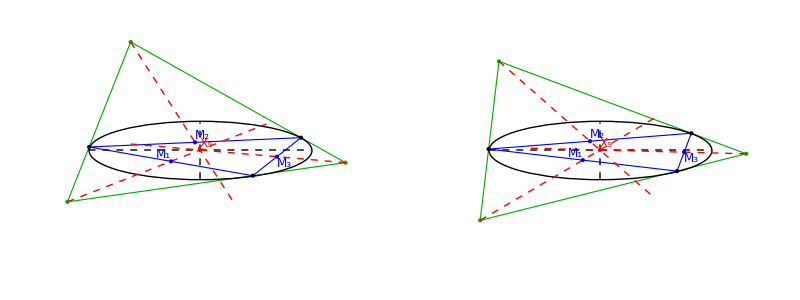

```mathematica
Grid[{showMit[1.5,#]&/@{25,35}}]
```

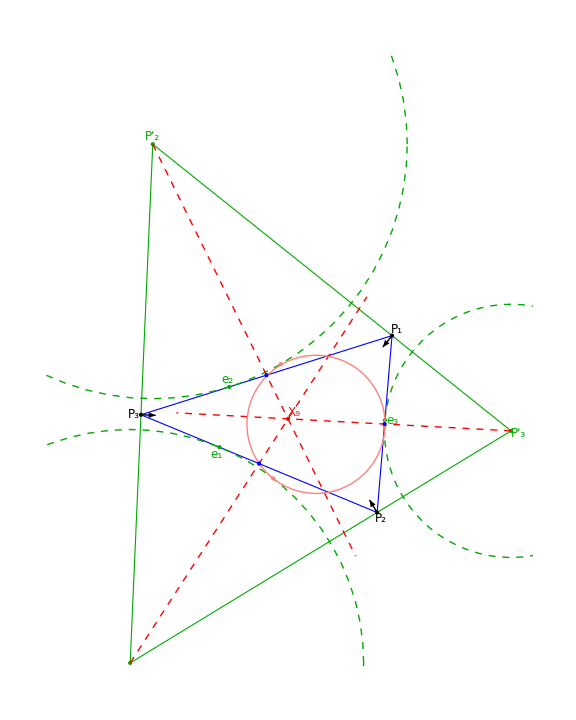

```mathematica
mittenExcPlot=Show[showMit[1.25,45,drEll->False,drNormals->True,lgt->.125,drVtx->True,drExt->True,drFeuTri->True,drMs->False],PlotRange->{{-2,2},{-2,3}},ImageMargins->10]
```

```mathematica
export3["0036_mittenExcPlot",mittenExcPlot];
```

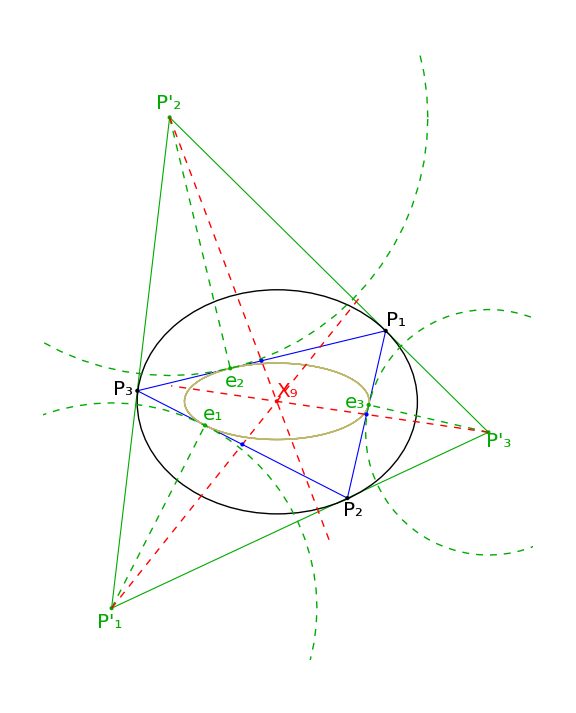

```mathematica
mittenExcPerpPlot=Show[showMit[1.25,39,drEll->True,drNormals->False,lgt->.25,drVtx->True,drExt->True,drMs->False,mSize->20,drCaustic->True,drExcPerps->True,drAxes->False],PlotRange->{{-2,2.2},{-2.2,3}},ImageMargins->10]
```

```mathematica
export3["0037_excenter_perps",mittenExcPerpPlot];
```

```mathematica
Clear@showMitScaled;showMitScaled[a_,deg1_,xScale_]:=Module[{ons,poly1,ell,gr,meds,clr={Blue,Thick},incClr="inc"/.ptClrs,lgt=.33,exc,mit,grExc},
ell=plotEll[a/xScale,{Thick,Black}];
ons=orbitNormals[a,toRad@deg1];
exc={#[[1]]/xScale,#[[2]]}&/@excentralTriangle[ons[[1]],ons[[3]]];
poly1={#[[1]]/xScale,#[[2]]}&/@ ons[[1]];
meds=getMedians@@poly1;
gr=Graphics[{clr,FaceForm@None,PointSize@Large,
{Dashed,Black,Line@{{-a/xScale,0},{a/xScale,0}},Line@{{0,-1},{0,1}}},
{EdgeForm@clr,Polygon@poly1,Point@poly1},
{Red,Dashed,Line@{#,ray[#,-#,1.5]}&/@exc},
{Blue,Point@meds,MapThread[Text[Style[Subscript["M",#2],20],#1,#3]&,{meds,Range@Length@meds,
{{.75,-1.5},{1.5,-1},{1.25,1}}}]},
{Red,Point@{0,0},Text[Style["X_9",{Bold,20}],{0,0},{-1.5,-1.25}]}
}];
grExc=Graphics[{Thick,FaceForm@None,EdgeForm@{Thick,incClr},incClr,PointSize@Large,Point@exc,Polygon@exc}];
Show[{grExc,ell,gr},PlotRange->{Automatic,{-2.75,3.75}},ImageSize->Large]]
```

```mathematica
(*Grid[{MapThread[showMitScaled[1.5,#1,#2]&,{{25,35,35},{1,1,1.5}}]}]*)
```

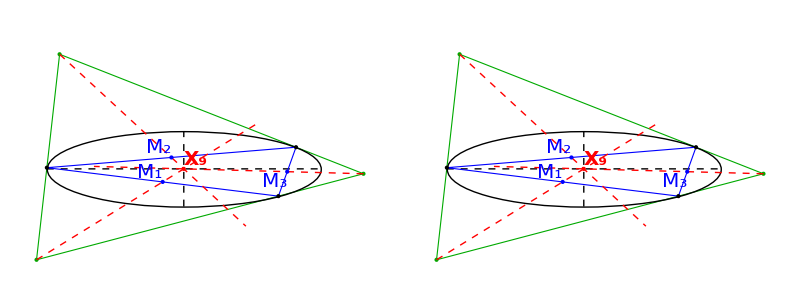

```mathematica
olgaPlot=Grid[{MapThread[showMitScaled[1.5,#1,#2]&,{{35,35},{1,1.5}}]}]
```

```mathematica
export3["0051_mitten_proof",olgaPlot];
```

```mathematica
Clear@showAntiCompl;
Options@showAntiCompl={"x100displ"->.15,"drCirc"->False};showAntiCompl[a_,deg1_,OptionsPattern[]]:=Module[{o,n,s,ell,gr,x11,x100,x2,clr={Blue,Thick},lgt=.33,mit,ctrs,rhat,rads,caustic,act,actInc,actInradius,actSides,actCtrs,actRads,actIntouch,ext},
ell=plotEll[a,{Thick,Black}];
{o,n,s}=orbitNormals[a,toRad@deg1];
ctrs={getIncenterTrilin[o,s],getNinepointCenterTrilin[o,s]};
rads={getInradius@s,getNinepointCircleRadius@s};
caustic=Module[{o2,n2,s2},Table[{o2,n2,s2}=orbitNormals[a,toRad@i];getFeuerbachTrilin[o2,s2],{i,0,359}]];
rhat=rot[{1,0},toRad@25];
x11=getFeuerbachTrilin[o,s];
x100=getX100Trilin[o,s];
act=anticomplementaryTriangle[o,s];
actInc=getNagelTrilin[o,s];
actSides=RotateLeft@triLengths@act;
actIntouch=intouchTriangle[act,actSides];
actInradius=magn[actInc-actIntouch[[1]]];
ext=extouchTriangle[o,s];
actCtrs={getIncenterTrilin[act,actSides],getNinepointCenterTrilin[act,actSides]};
actRads={getInradius@actSides,getNinepointCircleRadius@actSides};
x2=getBarycenterTrilin[o,s];
gr=Graphics[{clr,FaceForm@None,PointSize@Large,Arrowheads@Medium,
{Dashed,Black,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
(*MapThread[{#1/.ptClrs,Thick(*Point@#2,Text[Style[Subscript["X",#4],{Bold,16}],#2,{0,-1.5}]*),Circle[#2,#3]}&,{{"inc","npc"},ctrs,rads,{1,5}}],*)
{Red,Point@{0,0},Text[Style["X_9",{Bold,16}],{0,0},{-1.25,-1.25}]},
{Black,ellLabelPoints[a,o,"P",{Bold,16},0.15],Blue,ellLabelPointsb[3a,3a,act,"P'",{Bold,16},0.2](*,ellLabelTxt[a,o[[1]],Style["P_1",{Bold,16}],.25]*)},
{EdgeForm@{Dashed,Blue,Thick},Polygon@act},
(*{"bar"/.ptClrs,Point@x2,Dashed,Thick,Line@{x11,x100},Text[Style["X_2",{Bold,16}],x2,{-1.25,1.1}]},*)
{EdgeForm@clr,Polygon@o},
MapThread[{#1/.ptClrs,Thick,Circle[#2,#3]}&,{{"inc","npc"},actCtrs,actRads,{1,5}}],

{"feu"/.ptClrs,Thick,Line@caustic,Point@ext,ellLabelPointsb[1.5a,.5a,ext,"e",{Bold,16},0.15]},
{"inc"/.ptClrs,PointSize@Large,Point@actIntouch,Point@actInc,Text[Style["X_8",{Bold,16},Background->White],actInc,{1.25,1}],Thick,Circle[actInc,actInradius],ellLabelPoints[a,actIntouch,"i'",{Bold,16},0.15],Thickness@Large,Dashed,Line[{actInc,#}]&/@actIntouch},
{Black,Point@x100,ellLabelTxt[a,x100,Style["X_100",{Bold,16}],OptionValue@"x100displ"],Point@x11,Text[Style["X_11",{Bold,16}],x11,{-1.,-1.25}]},
{Black,Point@o,Blue,Point@act}
}];
Show[{ell,gr},ImageSize->800]];
```

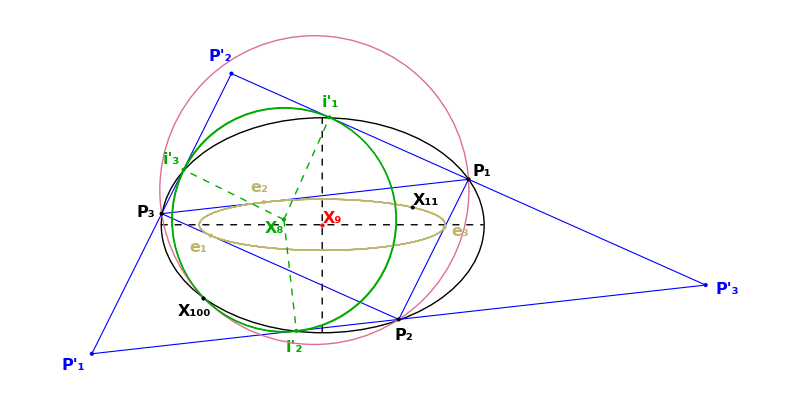

```mathematica
anticomlpPlot=showAntiCompl[1.5,25]
```

```mathematica
export3["0048_act_intouch",anticomlpPlot];
```

#### Anticomplementary Progress Along Billiard for Various Points

```mathematica
Clear@getAngularProgress;
Options@getAngularProgress={"clean"->False,"degStep"->1.};
getAngularProgress[a_,OptionsPattern[]]:=Module[{ts,ons,os,osSides,degStep=OptionValue@"degStep",
p1ths,p2ths,p3ths,
causticA,causticB,
osFs,osFths,
etts,ettTpths1,ettTpths2,ettTpths3,
acts,actSides,
actFs,actFths,
actTps,actTpths1,actTpths2,actTpths3},
ts=Range[0,360-degStep,degStep];
ons=orbitNormals[a,toRad@#]&/@ts;
os=First/@ons;
osSides=Third/@ons;
p1ths=toDeg[getBilliardAngle[a,1,#[[1]]]]&/@os;
p2ths=toDeg[getBilliardAngle[a,1,#[[2]]]]&/@os;
p3ths=toDeg[getBilliardAngle[a,1,#[[3]]]]&/@os;
(* these move along caustic *)
{causticA,causticB}=getTriCausticParams[a];
osFs=MapThread[getFeuerbachTrilin[#1,#2]&,{os,osSides}];
osFths=toDeg[getBilliardAngle[causticA,causticB,#]]&/@osFs;
etts=MapThread[extouchTriangle[#1,#2]&,{os,osSides}];
ettTpths1=toDeg[getBilliardAngle[causticA,causticB,#[[1]]]]&/@etts;
ettTpths2=toDeg[getBilliardAngle[causticA,causticB,#[[2]]]]&/@etts;
ettTpths3=toDeg[getBilliardAngle[causticA,causticB,#[[3]]]]&/@etts;

(* these sweep billiard {a Cos[t], Sin[t]} *)
acts=MapThread[anticomplementaryTriangle[#1,#2]&,{os,osSides}];
actSides=RotateLeft/@(triLengths/@acts);
actFs=MapThread[getFeuerbachTrilin[#1,#2]&,{acts,actSides}];
actTps=MapThread[intouchTriangle[#1,#2]&,{acts,actSides}];
actFths=toDeg[getBilliardAngle[a,1,#]]&/@actFs;
actTpths1=toDeg[getBilliardAngle[a,1,#[[1]]]]&/@actTps;
actTpths2=toDeg[getBilliardAngle[a,1,#[[2]]]]&/@actTps;
actTpths3=toDeg[getBilliardAngle[a,1,#[[3]]]]&/@actTps;
Transpose[{ts,#}]&/@If[OptionValue@"clean",
{p1ths,
osFths,ettTpths1,
actFths,actTpths1},
{p1ths,p2ths,p3ths,
osFths,ettTpths1,ettTpths2,ettTpths3,
actFths,actTpths1,actTpths2,actTpths3}]];
```

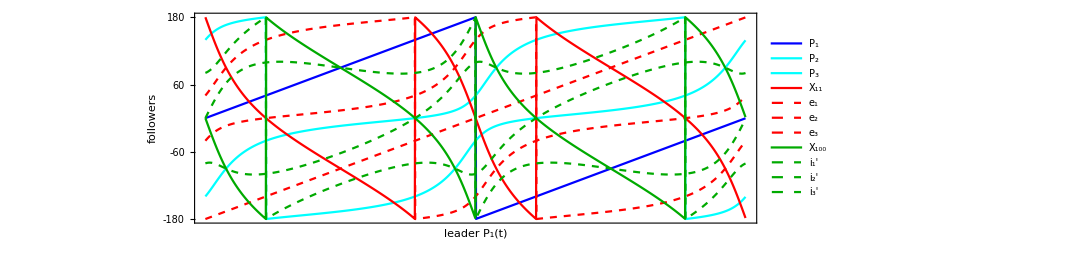

```mathematica
angularProgressPlot=ListLinePlot[getAngularProgress[1.5,"degStep"->.25],
PlotLegends->LineLegend[Style[#,16]&/@{
"P_1","P_2","P_3",
"X_11","e_1","e_2","e_3",
"X_100","i_1'","i_2'","i_3'"
},LegendLayout->{"Column",1}],
PlotStyle->{
{Thick,Blue},Sequence@@ConstantArray[Cyan,2],
Red,Sequence@@ConstantArray[{Dashed,Red},3],
Darker@Green,Sequence@@ConstantArray[{Dashed,Darker@Green},3]},
ImageSize->800,AspectRatio->.33,Frame->True,(*GridLines->Automatic,*)FrameStyle->Medium,
PlotRange->{{0,360},{-180,180}},
FrameTicks->{{Range[-180,180,60],None},{None,Range[0,360,60]}},
FrameLabel->(Style[#,{Black,16}]&/@{"leader P_1(t)","followers"})(*,
PlotLabel->Style["Angular Progress for N=3 Orbit Points",{Black,Large}]*)]
```

```mathematica
export3["0049_act_progress",angularProgressPlot];
```

```mathematica
Clear@getAngularPogressI1Diff;getAngularPogressI1Diff[a_,degStep_,yfact_:1]:=Module[{i1,i1t,i1v,i1vd},
i1=getAngularProgress[a,"degStep"->degStep,"clean"->True][[5]];
i1t=First/@i1;
i1v=Second/@i1;
i1vd=yfact Differences[i1v];
MapThread[{#1,#2}&,{Most@i1t,i1vd}]];
```

```mathematica
getAngPP[a_]:=Module[{degStep=.25,i1diff,llp},
i1diff=getAngularPogressI1Diff[a,degStep,500];
ListLinePlot[
Append[getAngularProgress[a,"degStep"->degStep,"clean"->True],i1diff],
PlotLegends->LineLegend[Style[#,16]&/@{
"P_1",
"X_11","e_1",
"X_100","i_1'","vel(i1')"
},LegendLayout->{"Column",1}],
PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Dashed,Blue},{Thick,Dashed,Red},{Darker@Green,Thick},{Dashed,Thick,Darker@Green}},
PlotLabel->Style["a="<>nfn[a,3],{Black,16}],
ImageSize->800,AspectRatio->.33,Frame->True,(*GridLines->Automatic,*)FrameStyle->Medium,
PlotRange->{{0,360},{-180,180}},
GridLines->{Range[0,360,30],Range[-180,180,30]},
FrameTicks->{{Range[-180,180,60],None},{Range[0,360,30],None}},
FrameLabel->(Style[#,{Black,16}]&/@{"t","t'"})(*,
PlotLabel->Style["Angular Progress for N=3 Orbit Points",{Black,Large}]*)]];
```

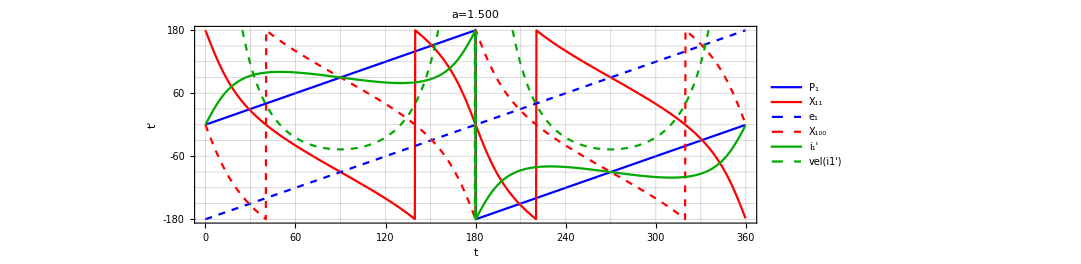

```mathematica
angularProgressPlotClean15=getAngPP[1.5]
```

```mathematica
export3["0049_act_progress_clean_15",angularProgressPlotClean15];
```

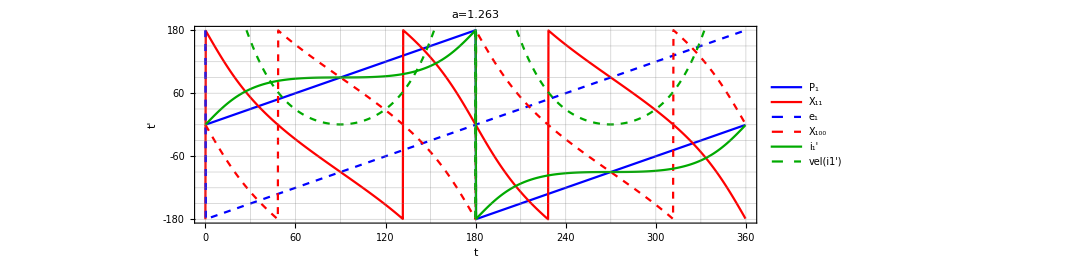

```mathematica
angularProgressPlotClean1263=getAngPP[1.263]
```

```mathematica
export3["0049_act_progress_clean_1263",angularProgressPlotClean1263];
```

#### Symmedian Quartic

```mathematica
Clear@showSymmErr;
Options@showSymmErr={symClr->Darker@Red,idealClr->Darker@Green,factor->10^7};showSymmErr[a_,tDeg2_,OptionsPattern[]]:=Module[{o,n,s,a6,b6,denom,gr,x6,x6i,x6mult,gr2,ell,b=1,δ,ell6,degStep=.25,tDegMax=360,x6s,x6sInter,x6sMult},
x6s=Table[t=toRad@tDeg;{o,n,s}=orbitNormals[a,t];getSymmedianTrilin[o,s],{tDeg,0,tDegMax-degStep,degStep}];
δ=Sqrt[a^4-a^2*b^2+b^4];
denom=(3*a^4-2*a^2*b^2+3*b^4);
a6=(-b^4-a^2*b^2-δ*b^2+3*δ*a^2)*a/denom;
b6=(a^4+b^2*a^2+δ*a^2-3*δ*b^2)*b/denom;
x6sInter=ellInterRaybUnprot[a6,b6,#,-#][[1]]&/@x6s;
x6sMult=MapThread[ray[#1,#2-#1,OptionValue@factor*magn[#2-#1]]&,{x6sInter,x6s}];
ell6=Table[t=toRad@tDeg;{a6 Cos@t,b6 Sin@t},{tDeg,0,tDegMax-degStep,degStep}];
gr=Graphics[{PointSize@Large,
{Black,Point@{0,0},Text[Style["O",{Bold,16}],{0,0},{0,-1.5}]},
{Thick,OptionValue@idealClr,Line@ell6},
{OptionValue@symClr,Thick,Dashed,Line@x6sMult}}];
ell=plotEll[a,{Thick,Black}];
{o,n,s}=orbitNormals[a,toRad@tDeg2];
x6=getSymmedianTrilin[o,s];
x6i=ellInterRaybUnprot[a6,b6,x6,-x6][[1]];
x6mult=ray[x6i,x6-x6i,OptionValue@factor*magn[x6-x6i]];
gr2=Graphics[{PointSize@Large,FaceForm@None,
{Black,Thick,Line@{{0,0},x6mult},ellLabelTxt[a,o[[1]],Style["P_1(t)",{Bold,16}],.075]},
{EdgeForm@{Thick,Blue},Polygon@o},
{Darker@Green,Point@x6,Text[Style["X_6",{16,Bold}],x6i,{.25,1.5}],Blue,Point@o[[1]],OptionValue@symClr,Point@x6mult,Text[Style["~X_6",{16,Bold}],x6,{-2,-1.5}]}}];
Show[{ell,gr,gr2},PlotRange->{{-1.6,1.6},{-1.1,1.1}},ImageSize->800]];
```

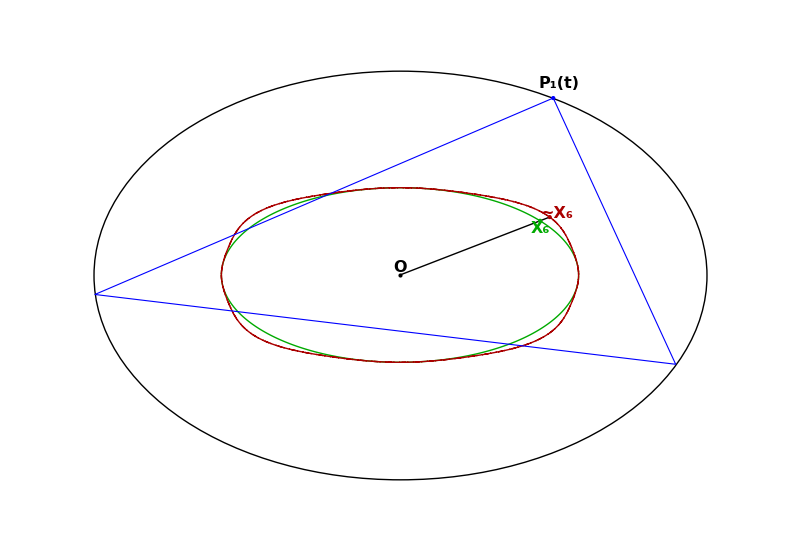

```mathematica
symmQuarticPlot=showSymmErr[1.5,60.,factor->2.*10^6]
```

```mathematica
export3["0041_symmedian",symmQuarticPlot];
```

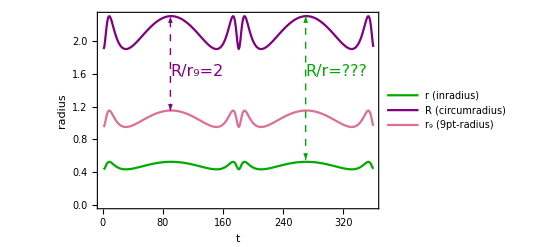

```mathematica
radiiGraphPlot=Module[{a=2,degStep=1,ons,rads,o,s,llp,clrs=(#/.ptClrs)&/@{"inc","cir","npc"},ps,epi},
ons=Table[orbitNormals[a,toRad@deg],{deg,0,360-degStep,degStep}];
rads={getInradius@#,getCircumradius@#,getNinepointCircleRadius@#}&/@Third/@ons;
ps={Thick,#}&/@clrs;
epi={Dashed,"cir"/.ptClrs,Arrowheads[{-.03,.03}],Arrow@{{90,1.15},{90,2.3}},Text[Style["R/r_9=2",16],{90,.5(1.15+2.3)},{-1.25,1}],
"inc"/.ptClrs,Arrowheads[{-.03,.03}],Arrow@{{270,.55},{270,2.3}},
Text[Style["R/r=???",16],{270,.5(1.15+2.3)},{-1.25,1}]};
llp=ListLinePlot[Transpose@rads,Frame->True,FrameStyle->{{Black,Medium},{Black,Medium}},FrameLabel->(Style[#,{Black,16}]&/@{"t","radius"}),Epilog->epi,PlotStyle->ps,PlotRange->{Automatic,Automatic}];
Legended[llp,LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"r (inradius)","R (circumradius)","r_9 (9pt-radius)"}]]]
```

```mathematica
export3["0075_radii_plot",radiiGraphPlot];
```

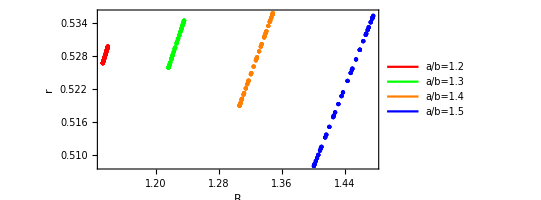

```mathematica
radiiScatterPlot=Module[{degStep=2.5,as={1.2,1.3,1.4,1.5},ons,rads,o,s,lp,Rr,Rr9,ps},
ons=Table[orbitNormals[#,toRad@deg],{deg,0,360-degStep,degStep}]&/@as;
rads=Table[{getInradius@#,getCircumradius@#,getNinepointCircleRadius@#}&/@Third/@ons[[i]],{i,Length@ons}];
Rr=Table[{#[[2]],#[[1]]}&/@rads[[i]],{i,Length@rads}];
Rr9=Table[{#[[2]],#[[3]]}&/@rads[[i]],{i,Length@rads}];
ps={Red,Green,Orange,Blue};
lp=Show[Table[Graphics[{ps[[i]],Point@Rr[[i]]}],{i,Length@rads}],PlotRange->All,Frame->True,FrameStyle->{{Black,Medium},{Black,Medium}},AspectRatio->.5,FrameLabel->(Style[#,{Black,Medium}]&/@{"R","r"})];
Legended[lp,LineLegend[Directive[{Thickness@Large,#}]&/@ps,
"a/b="<>nfn[#,1]&/@as]]]
```

```mathematica
export3["0080_radii_scatter",radiiScatterPlot];
```

```mathematica
Clear@getSumProdCosines;
getSumProdCosines[a_,tDeg_]:=Module[{o,n,s,exc,prod,cosSum,excCosProd},
{o,n,s}=orbitNormals[a,toRad@tDeg];
cosSum=Total@getTriCosines@o;
exc=excentralTriangle[o,s];
excCosProd=Apply[Times,getTriCosines@exc];
{cosSum,excCosProd}];
```

#### Sum of Cosines Divided by Product of Cosines vs a/b

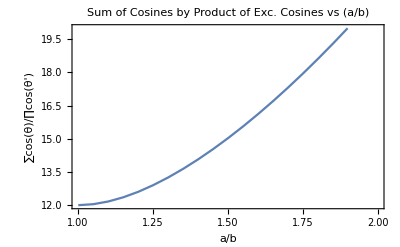

```mathematica
Module[{sp},
ListLinePlot[Table[sp=getSumProdCosines[a,0];{a,sp[[1]]/sp[[2]]},{a,1.001,2,.05}],Frame->True,PlotLabel->Style["Sum of Cosines by Product of Exc. Cosines vs (a/b)",{Black,Medium}],FrameStyle->15,PlotRange->{{1,2},{12,20}},FrameLabel->{"a/b","∑cos(θ)/∏cos(θ')"}]]
```

```mathematica
Clear@getRadiusRatio;
getRadiusRatio[a_,tDeg_]:=Module[{o,n,s},
{o,n,s}=orbitNormals[a,toRad@tDeg];
(getInradius@s/getCircumradius@s)];
```

```mathematica
Module[{aInfl= 1.372851,ratioInfl},
ratioInfl=getRadiusRatio[aInfl,0];
ratioInfl]
```

0.406909

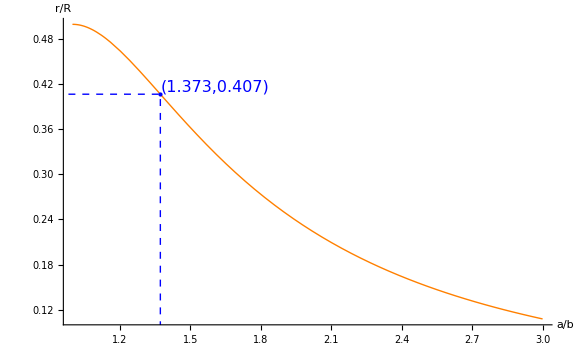

```mathematica
Module[{o,n,s,pl,aInfl,ratioInfl,pInfl},
aInfl= 1.372851;
ratioInfl=getRadiusRatio[aInfl,0];
pInfl={aInfl,ratioInfl};
pl=Quiet@Plot[getRadiusRatio[a,0],{a,1,3},PlotStyle->{Thick,Orange},AxesStyle->Large,AxesLabel->(Style[#,{Large,Black}]&/@{"a/b","r/R"}),Epilog->{PointSize@Large,Blue,Point@pInfl,Dashed,Line@{{aInfl,0},pInfl},Line@{{0,ratioInfl},pInfl},Text[Style["("<>nfn[pInfl[[1]],3]<>","<>nfn[pInfl[[2]],3]<>")",16],pInfl,{-1,-1.5}]}];
Show[pl,ImageSize->Large]]
```

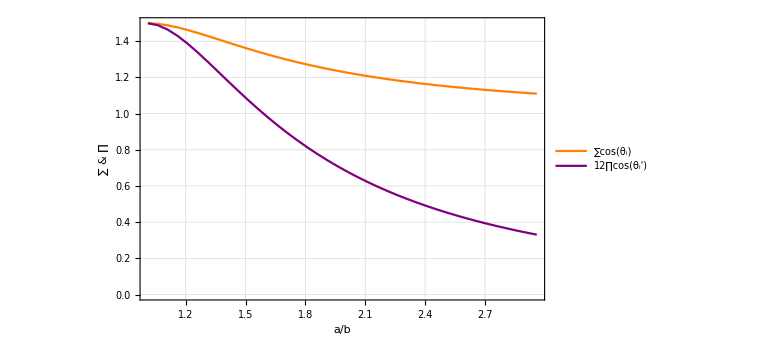

```mathematica
Module[{o,n,s,pl,sp},
pl=ListLinePlot[Transpose@Table[sp=getSumProdCosines[a,0];{{a,sp[[1]]},{a,12sp[[2]]}},{a,1.01,3,.05}],PlotStyle->{{Thick,Orange},{Thick,Purple}},Frame->True,FrameStyle->ConstantArray[{Black,12},4],ImageSize->Large,GridLines->Automatic,FrameLabel->(Style[#,{Large,Black}]&/@{"a/b","∑ & ∏"})];
Show[Legended[pl,LineLegend[Directive[{Thickness@Large,#}]&/@{Orange,Purple},{"∑cos(θ_i)","12∏cos(θ_i')"}]]]]
```

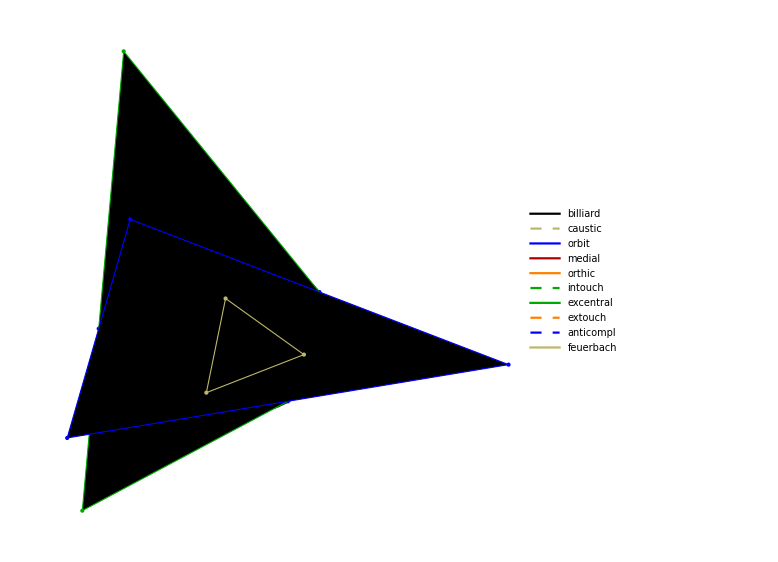

```mathematica
derivedTrisPlot=Show[showDerivedTris[1.5,30],PlotRange->All,Frame->None,PlotLabel->None]
```

```mathematica
export3["0043_derived-triangles",derivedTrisPlot];
```

#### Billiard Trajectories: needs to to to ngons_v1.nb

## Poncelet Triangles & Central Circles

What is the radius of a circle centered on (x, y) in an ellipse which permits a poncelet N = 3 polygon to be formed?

```mathematica
Clear@rPonceletCtrEqn;
rPonceletCtrEqn[a_,b_]=Module[{P,eqn1,eqn1coeffs,discr,cos2Alpha,tanAlpha,t0,Q,reqn,sa,tangs,ca},
P={0,b}+t{Sin@α,-Cos@α};
eqn1=P.P-r^2;
eqn1coeffs=FullSimplify@CoefficientList[eqn1,t];
discr=eqn1coeffs[[2]]^2-4eqn1coeffs[[3]]eqn1coeffs[[1]];
cos2Alpha=First[ca2/.Solve[(discr/.(Cos@α)^2->ca2)==0,ca2]];
ca=Sqrt[cos2Alpha];sa=Sqrt[1-cos2Alpha];
tanAlpha=Sqrt[(1-cos2Alpha)/cos2Alpha];
Q={(b+r)tanAlpha,-r};
reqn=FullSimplify[(Q[[1]]/a)^2+(Q[[2]]/b)^2==1,r>0&&a>0&&b>0];
(r/.Solve[reqn,r])
]
```

{(a b)/(a-b),(a b)/(a+b)}

```mathematica
Clear@TangsToCircTopEqn;
TangsToCircTopEqn[y_,r_]=Module[{P,eqn1,eqn1coeffs,discr,cos2Alpha,tanAlpha,t0,Q,reqn,sa,tangs,ca},
P={0,y}+t{Sin@α,-Cos@α};
eqn1=P.P-r^2;
eqn1coeffs=FullSimplify@CoefficientList[eqn1,t];
discr=eqn1coeffs[[2]]^2-4eqn1coeffs[[3]]eqn1coeffs[[1]];
cos2Alpha=First[ca2/.Solve[(discr/.(Cos@α)^2->ca2)==0,ca2]];
ca=Sqrt[cos2Alpha];sa=Sqrt[1-cos2Alpha];
t0=y*ca;
tangs=FullSimplify[{{0,y}+t0{sa,-ca},{0,y}+t0{-sa,-ca}},y>0&&r>0];
tangs
]
```

{{(r √(-r^2+y^2))/y,r^2/y},{-(r √(-r^2+y^2))/y,r^2/y}}

```mathematica
PonceletCtrRadius[a_,b_]:=(a*b)/(a+b);
```

```mathematica
(* from point (0,y) *)
Clear@TangsToCircTop;
TangsToCircTop[y_,r_]:=Module[{tang1,tang2},
tang1=(r/y){√((y-r) (y+r)),r};
tang2=flipX@tang1;
{tang1,tang2}];
```

```mathematica
PonceletCtrRadius[1.5,1]
```

0.6

```mathematica
TangsToCircTop[1,PonceletCtrRadius[1.5,1]]
```

{{0.48,0.36},{-0.48,0.36}}

```mathematica
Clear@TangsToCircAnyEqn;
TangsToCircAnyEqn[x_,y_,r_]:=Module[{b,tangs,yhat,xhat,rotInv},
b=magn[{x,y}];
yhat={x,y}/b;
xhat=perpNeg[yhat];
rotInv=Transpose@{xhat,yhat};
tangs=TangsToCircTop[b,r];
(rotInv.#)&/@tangs
]
```

```mathematica
Module[{u=π/2},
TangsToCircAnyEqn[1.5 Cos@u,Sin@u,PonceletCtrRadius[1.5,1]]]
```

{{0.48,0.36},{-0.48,0.36}}

#### N=3 externo elipse (a,b), interno circulo r = ab/(a+b)

```mathematica
getTriInfo[tri_,tangsU_,feetU_]:=Module[{sides,feu,bar,x100,coss,sins},
sides=RotateLeft@triLengths@tri;
feu=getFeuerbachTrilin[tri,sides];
bar=getBarycenterTrilin[tri,sides];
x100=bar+2(bar-feu);
coss=getTriCosines[tri];
sins=Sqrt[1-#]&/@coss;
<|"tri"->tri,
"sides"->sides,
"exc"->excentralTriangle[tri,sides],
"orthic"->orthicTriangle[tri,sides],
"act"->anticomplementaryTriangle[tri,sides],
"coss"->coss,
"cosSum"->Total@coss,
"sinSum"->Total@sins,
"sinProd"->Apply[Times,sins],
"cosProd"->Apply[Times,coss],
"tangs"->tangsU,
"feet"->feetU,
"per"->Total@sides,
"per2"->Total[sides^2],
"area"->Abs@signedArea@tri,
"r"-> getInradius@sides,
"R"->getCircumradius@sides,
"inc"->getIncenterTrilin[tri,sides],
"bar"->bar,
"cir"->getCircumcenterTrilin[tri,sides],
"ort"->getOrthocenterTrilin[tri,sides],
"npc"->getNinepointCenterTrilin[tri,sides],
"sym"->getSymmedianTrilin[tri,sides],
"ger"->getGergonneTrilin[tri,sides],
"nag"->getNagelTrilin[tri,sides],
"mit"->getMittenTrilin[tri,sides],
"spi"->getSpiekerTrilin[tri,sides],
"feu"->feu,
"x100"->x100
(*"x100t"->x100t,*)
|>];
```

```mathematica
Clear@getPoncU;
getPoncU[a_,u_]:=Module[{r,P1,tangsU,feetU,triPonc},
r = a/(a+1);
P1={a Cos@u,Sin@u};
tangsU=TangsToCircAnyEqn[Sequence@@P1,r];
feetU=ellInterRayUnprot[a,P1,#-P1][[2]]&/@tangsU;
triPonc={P1,Sequence@@feetU};
getTriInfo[triPonc,tangsU,feetU]];
```

```mathematica
getPoncU[1.4,.1]
```

<|tri→{{1.39301,0.0998334},{-0.492336,-0.936124},{-0.674196,0.876408}},sides→{1.82163,2.20826,2.15121},exc→{{-1.99977,-0.143319},{1.23224,2.34298},{1.544,-2.0071}},orthic→{{-0.576452,-0.0977715},{0.0818691,0.592381},{0.13296,-0.592537}},act→{{-2.55954,-0.15955},{1.21115,1.91237},{1.57487,-1.7127}},coss→{0.651074,0.391668,0.443369},cosSum→1.48611,sinSum→2.11673,sinProd→0.343732,cosProd→0.113061,tangs→{{0.280915,-0.511238},{0.20514,0.546073}},feet→{{-0.492336,-0.936124},{-0.674196,0.876408}},per→6.1811,per2→12.8225,area→1.80282,r→0.583333,R→1.2,inc→{-2.87385×10^-16,-1.07769×10^-16},bar→{0.075491,0.0133724},cir→{0.19412,0.0481407},ort→{-0.161766,-0.0561642},npc→{0.0161766,-0.00401173},sym→{-0.0700601,-0.0138704},ger→{-0.0595982,-0.0165189},nag→{0.226473,0.0401173},mit→{0.143036,0.0283181},spi→{0.113237,0.0200586},feu→{-0.566183,0.14041},x100→{1.35884,-0.240704}|>

#### Which are circular: X1,X3,X11

```mathematica
PonceletCircularity[a_,degStep_]:=Module[{ctrs,locs},
ctrs={"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi","feu","x100"};
locs=Transpose@Table[magn[getPoncU[a,toRad@(v+.001)][#]]&/@ctrs,{v,0,360,degStep}];
Pick[ctrs,negl[#["z"]]&/@getStats/@locs]]
```

```mathematica
PonceletCircularity[1.5,1]
```

{inc,cir,npc,feu}

```mathematica
Clear@drawPonceletCtr;
Options@drawPonceletCtr={drRefTri->False,drLabels->False,drLoci->False,drCircs->False,degStep->1.,drExc->False};
drawPonceletCtr[a_,u_,OptionsPattern[]]:=Module[{ell,r,gr,fs,c2a,ta,Q,tri,triPonc,lab,tangs,
locX2,locX3,locX4,locX5,locX9,locX11,locX100,clrs,ctrs,locis,lociExc},
clrs={Brown,Purple,Orange,Pink,Darker@Red,Gray,Gray};
ctrs={"bar","cir","ort","npc","mit","feu","x100"};
locis={True,True,True,True,True,False,False};
ell=plotEll[a,{Thick,Black}];
fs=getFoci[a];
r=PonceletCtrRadius[a,1];
c2a=(1-r)(1+r);
ta=Sqrt[(1-c2a)/c2a];
Q={(1+r)ta,-r};
tri={{0,1},Q,flipX@Q};
tangs=TangsToCircTop[1,r];
triPonc=getPoncU[a,u];
lociExc=If[OptionValue@drLoci,Table[getPoncU[a,toRad@(v+.001)]["exc"][[1]],{v,0,360,OptionValue@degStep}],{}];
If[OptionValue@drLoci,{locX2,locX3,locX4,locX5,locX9,locX11,locX100}=Transpose@Table[getPoncU[a,toRad@(v+.001)][#]&/@ctrs,{v,0,110,OptionValue@degStep}]];
gr=Graphics[{PointSize@Large,FaceForm@None,Thick,
{PointSize@Medium,Black,Point@fs,Darker@Green,Point@{0,0}},
{EdgeForm@{Thick,Darker@Green},FaceForm@{Darker@Green,Opacity@.1},Disk[{0,0},r]},
If[OptionValue@drRefTri,
{Blue,Point@tri,EdgeForm@{Thick,Blue},Polygon@tri(*,Blue,Point@tangs*)},{}],
{Blue,Point@triPonc["tri"][[1]],(*Point@triPonc["tangs"],*)Line@{triPonc["tri"][[1]],#}&/@triPonc["feet"],Point@triPonc["feet"],(*Dashed,*)Line@triPonc["feet"]},
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@triPonc["exc"]},{}],
If[OptionValue@drCircs,
{{Purple,Circle[triPonc["cir"],triPonc["R"]]},
{Pink,Circle[triPonc["npc"],triPonc["R"]/2]}},{}],
If[OptionValue@drLoci,
{MapThread[{#1,If[#3,Line@#2,{}]}&,{clrs,{locX2,locX3,locX4,locX5,locX9,locX11,locX100},locis}]},{}],
If[OptionValue@drLoci,{Thick,Darker@Green,Line@lociExc},{}],
If[OptionValue@drLabels,
MapThread[{#1,Text[Style[Subscript["X",#2],14],triPonc[#3],{0,-1.5}],Point@triPonc[#3]}&,
{clrs,
{2,3,4,5,9,11,100},
ctrs}],{}]
}];
lab="a="<>nfn[a,2]<>", r="<>nfn[r,3]<>" ,R="<>nfn[triPonc["R"],3](*<>"\nL="<>nfn[triPonc["per"],3]<>", A="<>nfn[triPonc["area"],3]*);
Show[{ell,gr},PlotLabel->Style[lab,{16,Black}],ImageSize->400,PlotRange->{1.1{-3,3},1.1{-3,3}}]];
```

```mathematica
Manipulate[drawPonceletCtr[a,toRad@tDeg,
drCircs->drCircs0,
drExc->drExc0,
drLoci->drLoci0,
drLabels->drLabels0],
{{a,2.},1.01,3},
{{tDeg,30},-180,180,1},
{{drExc0,False},{False,True}},
{{drCircs0,False},{False,True}},
{{drLoci0,False},{False,True}},
{{drLabels0,False},{False,True}}]
```

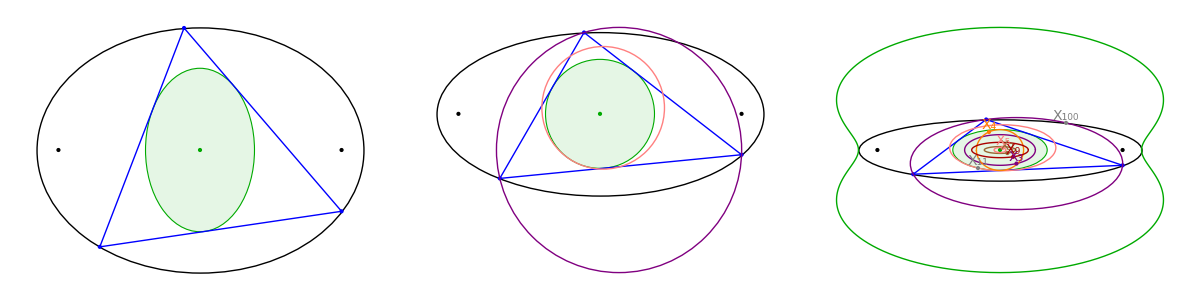

```mathematica
Module[{a=2.,tDeg=-30},Grid[{Show[#,PlotRange->{1.1{-a,a},{1.1,-2}},
PlotLabel->None]&/@
{drawPonceletCtr[a,toRad@tDeg,drCircs->False,drLoci->False],
drawPonceletCtr[a,toRad@tDeg,drCircs->True,drLoci->False],
drawPonceletCtr[a,toRad@tDeg,drCircs->True,drLoci->True,drLabels->True]}}]]
```

```mathematica
Clear@drOnePoncCirc;
drOnePoncCirc[a_,tDeg_]:=Show[drawPonceletCtr[a,toRad@tDeg,drCircs->True,drLoci->True,drLabels->True],
PlotRange->{1.1{-a,a},{a,-a}},
ImageSize->800,
PlotLabel->None];
```

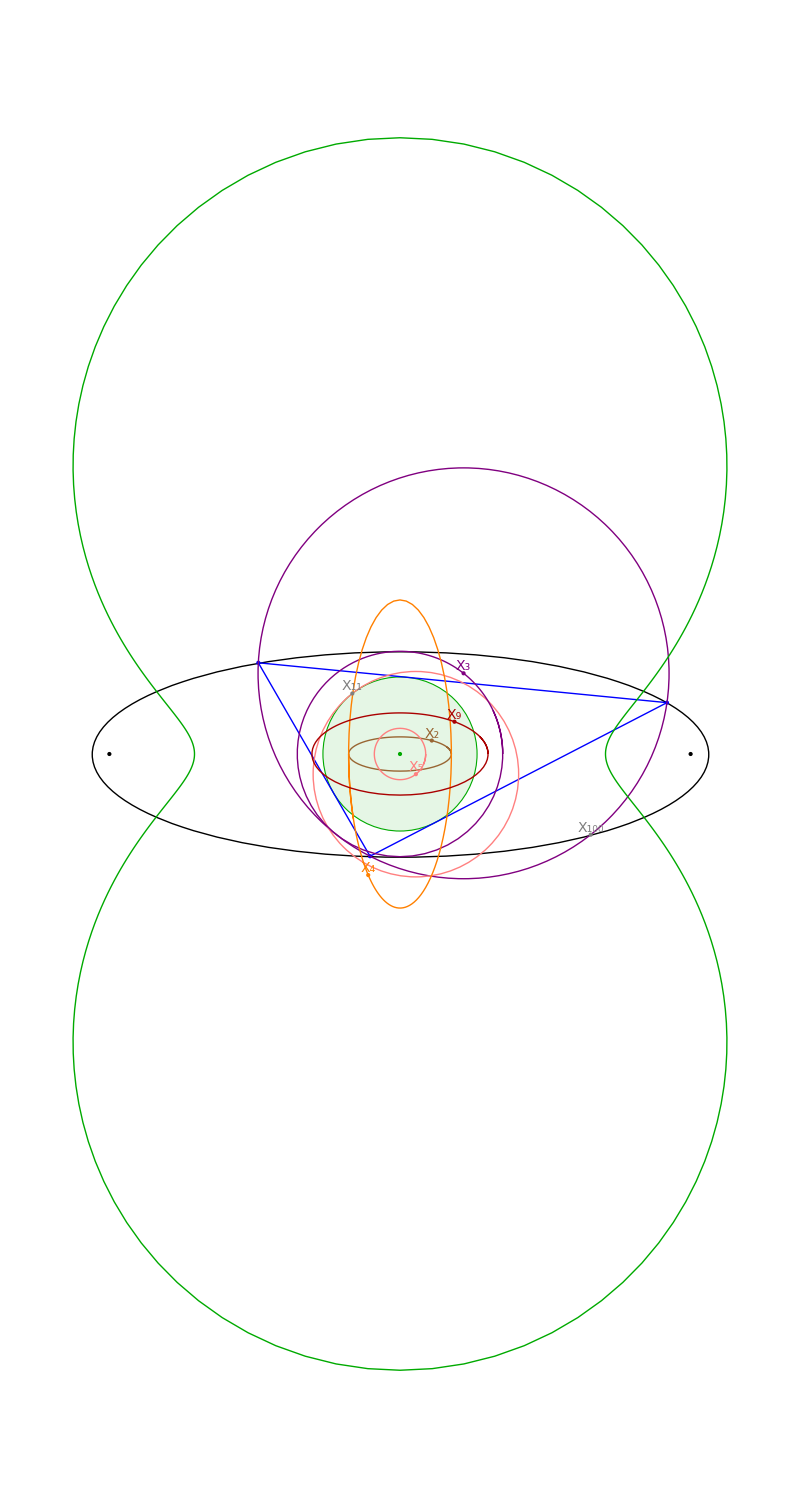

```mathematica
drOnePoncCirc[3.,30.]
```

#### N=3: externo circulo r=(a+b), interno elipse (a,b)

```mathematica
Clear@getPoncOuterU;
getPoncOuterU[a_,u_]:=Module[{r=a+1,Pinner,Pouter,ellTang,P1,tangsU,feetU,triPonc},
Pinner={a Cos@u,Sin@u};
ellTang=perp[ellGrad[a,Sequence@@Pinner]];
P1=ellInterRaybUnprot[r,r,Pinner,ellTang][[1]];
(*P1=r{Cos@u,Sin@u};*)
tangsU=ellTangents[a,P1];
(* should be inter w circ *)
feetU=(ellInterRaybUnprot[r,r,P1,#-P1][[2]])&/@tangsU;
triPonc={P1,Sequence@@feetU};
getTriInfo[triPonc,tangsU,feetU]];
```

```mathematica
getPoncOuterU[1.5,0.1]
```

<|tri→{{1.17546,2.20642},{1.77282,-1.7627},{-2.48751,-0.249584}},exc→{{-1.91661,-4.80434},{-3.0277,4.06021},{4.70111,0.651443}},coss→{0.427086,0.471198,0.596297},cosSum→1.49458,cosProd→0.12,tangs→{{1.49251,0.0998334},{-1.06369,0.705079}},feet→{{1.77282,-1.7627},{-2.48751,-0.249584}},per→12.945,area→8.00294,r→1.23645,R→2.5,inc→{0.243205,0.0926862},bar→{0.15359,0.0647129},cir→{2.21881×10^-16,-3.88292×10^-16},ort→{0.460771,0.194139},npc→{0.230386,0.0970694},sym→{0.329122,0.121337},ger→{0.32067,0.124248},nag→{-0.0256384,0.00876634},mit→{0.0700507,0.0349453},spi→{0.108783,0.0507263},feu→{1.41316,-0.307346},x100→{-2.36554,0.80883}|>

```mathematica
Clear@drawPonceletOuterCtr;
Options@drawPonceletOuterCtr={drLabels->False,drLoci->False,drCircs->False,degStep->1.,drExc->False};
drawPonceletOuterCtr[a_,u_,OptionsPattern[]]:=Module[{ell,r,gr,fs,triPonc,lab,
locX1,locX2,locX4,locX5,locX9,locX11,locX100,clrs,ctrs,locis,lociExc},
clrs={Darker@Green,Brown,Orange,Pink,Darker@Red,Gray,Gray};
ctrs={"inc","bar","ort","npc","mit","feu","x100"};
locis={True,True,True,True,True,False,False};
ell=plotEll[a,{Thick,Black}];
fs=getFoci[a];
r=a+1;
triPonc=getPoncOuterU[a,u];
lociExc=If[OptionValue@drLoci,Table[getPoncOuterU[a,toRad@(v+.001)]["exc"][[1]],{v,0,360,OptionValue@degStep}],{}];
If[OptionValue@drLoci,{locX1,locX2,locX4,locX5,locX9,locX11,locX100}=Transpose@Table[getPoncOuterU[a,toRad@(v+.001)][#]&/@ctrs,{v,0,150,OptionValue@degStep}],{}];
gr=Graphics[{PointSize@Large,FaceForm@None,Thick,Dashed,
{PointSize@Medium,Black,Point@fs,Purple,Point@{0,0}},
{Purple,Circle[{0,0},r]},
{Blue,Point@triPonc["tri"][[1]],(*Point@triPonc["tangs"],*)Line@{triPonc["tri"][[1]],#}&/@triPonc["feet"],Point@triPonc["feet"],(*Dashed,*)Line@triPonc["feet"]},
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@triPonc["exc"]},{}],
If[OptionValue@drCircs,
{{Darker@Green,Circle[triPonc["inc"],triPonc["r"]]},
{Pink,Circle[triPonc["npc"],triPonc["R"]/2]}},{}],
If[OptionValue@drLoci,{Thick,Darker@Green,Line@lociExc},{}],
If[OptionValue@drLoci,
{MapThread[{#1,If[#3,Line@#2,{}]}&,{clrs,{locX1,locX2,locX4,locX5,locX9,locX11,locX100},locis}]},{}],
If[OptionValue@drLabels,
MapThread[{#1,Text[Style[Subscript["X",#2],14],triPonc[#3],{0,-1.5}],Point@triPonc[#3]}&,
{clrs,
{1,2,4,5,9,11,100},
ctrs}],{}]
}];
lab="a="<>nfn[a,2]<>", r="<>nfn[triPonc["r"],3]<>", ∏cos="<>nfn[triPonc["cosProd"],4]<>"\nL="<>nfn[triPonc["per"],3]<>", A="<>nfn[triPonc["area"],3];
Show[{ell,gr},PlotLabel->Style[lab,{16,Black}],ImageSize->400,PlotRange->{1.1{-6,6},1.1{-6,6}}]];
```

```mathematica
Manipulate[drawPonceletOuterCtr[a,toRad@tDeg,
drCircs->drCircs0,
drExc->drExc0,
drLoci->drLoci0,
drLabels->drLabels0],
{{a,2.},1.01,3},
{{tDeg,30},-180,180,1},
{{drExc0,False},{False,True}},
{{drCircs0,False},{False,True}},
{{drLoci0,False},{False,True}},
{{drLabels0,False},{False,True}}]
```

```mathematica
Clear@drOnePoncCircOuter;
drOnePoncCircOuter[a_,tDeg_]:=Module[{r=a+1},
Show[drawPonceletOuterCtr[a,toRad@tDeg,drCircs->True,drLoci->True,drLabels->True],
PlotRange->{1.1{-r,r},1.1{r,-r}},
ImageSize->800,
PlotLabel->None]];
```

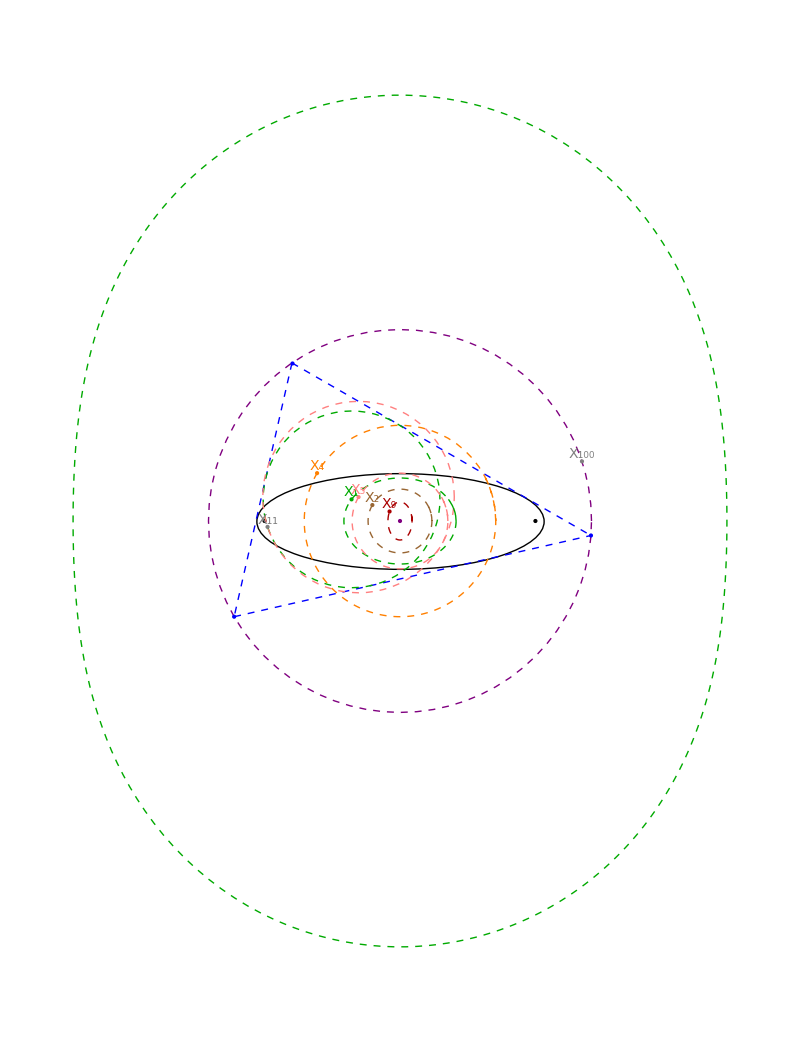

```mathematica
drOnePoncCircOuter[3,30.]
```

```mathematica
getPoncAreaRatio[a_,tDeg_]:=Module[{out,in,tRad},
tRad=toRad@tDeg;
out=getPoncOuterU[a,tRad]["area"];
in=getPoncU[a,tRad]["area"];
out/in];
```

```mathematica
getStats@Table[getPoncAreaRatio[3,tDeg+.001],{tDeg,0,360}]
```

<|n→361,mean→5.3333,sd→0.0814917,z→0.0152798,min→5.1007,max→5.57657,median→5.33333|>

#### Which are circular: X1,X3,X11

```mathematica
PonceletOuterCircularity[a_,degStep_]:=Module[{ctrs,locs},
ctrs={"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi","feu","x100"};
locs=Transpose@Table[magn[getPoncOuterU[a,toRad@(v+.001)][#]]&/@ctrs,{v,0,360,degStep}];
Pick[ctrs,negl[#["z"]]&/@getStats/@locs]]
```

```mathematica
PonceletOuterCircularity[1.5,1]
```

{bar,cir,ort,npc,x100}

```mathematica
Clear@showPoncInvariants;
Options@showPoncInvariants={drLoci->False,drCircs->False,drIntExc->False,drExtExc->False,showR0->0,drLabels->False};
showPoncInvariants[a_,tDeg_,opts:OptionsPattern[]]:=Module[{rint,rext,cosProdExt,cosSumInt,u,lab,showR,poncInt,cosProdIntExc},
rext=a+1;
rint=a/(a+1);
showR=If[OptionValue@showR0==0,rext,OptionValue@showR0];
u=toRad@tDeg;
poncInt=getPoncU[a,u];
cosSumInt=poncInt["cosSum"];
cosProdIntExc=Apply[Times,getTriCosines@poncInt["exc"]];
cosProdExt=getPoncOuterU[a,u]["cosProd"];
lab="a="<>nfn[a,2]<>", r_int="<>nfn[rint,3]<>", r_ext="<>nfn[rext,3]<>"\n∑cos_int="<>nfn[cosSumInt,3]<>", ∏cos_ext="<>nfn[cosProdExt,3]<>"\n∏cos_(int, exc)="<>nfn[cosProdIntExc,3];
Show[{
drawPonceletCtr[a,u,FilterRules[{opts},Options@drawPonceletCtr],drExc->OptionValue@drIntExc],
drawPonceletOuterCtr[a,u,FilterRules[{opts},Options@drawPonceletCtr],drExc->OptionValue@drExtExc]},
PlotLabel->Style[lab,{Black,16}],PlotRange->{1.1{-showR,showR},1.1{-showR,showR}}]];
```

#### Novas Invariantes para familias de poncelet N=3: 1) caustica interna é circulo: conserva circumraio. como r é constante, conserva r/R ou ∑cos_int ; corolario: ∏cos_(exc,int) é conservado 2) caustica interna é elipse, circumelipse é circulo. conserva produto de cossenos ∏cos_ext. 3) bonus do ronaldo: ∏cos_ext=∏cos_(exc,int)

```mathematica
Manipulate[showPoncInvariants[a,tDeg,drCircs->drCircs0,drIntExc->drExc0],
{{a,1.5},1.1,3,.05},
{{tDeg,30.},-180,180,.1},
{{drCircs0,False},{True,False}},
{{drExc0,False},{True,False}}]
```

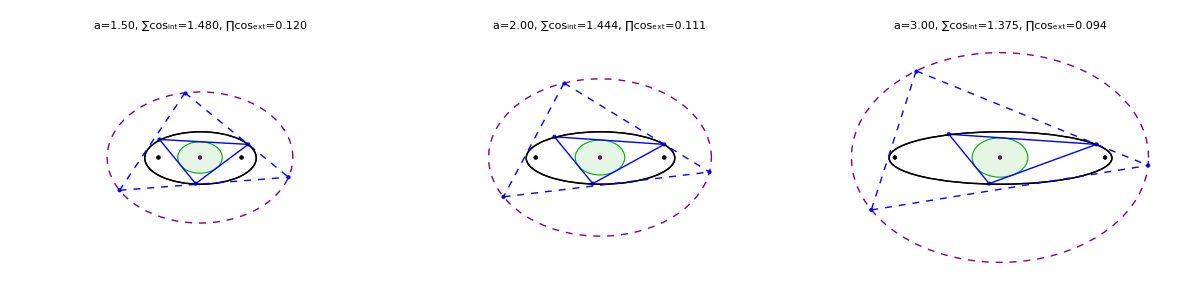

```mathematica
Grid[{showPoncInvariants[#,30.,False,4]&/@{1.5,2,3}}]
```

```mathematica
Clear@getPoncInvariants;
getPoncInvariants[a_,tDeg_]:=Module[{r,cosProdExt,cosSumInt,u},
r=a+1;
u=toRad@tDeg;
cosSumInt=getPoncU[a,u]["cosSum"];
cosProdExt=getPoncOuterU[a,u]["cosProd"];
{cosSumInt,cosProdExt}];
```

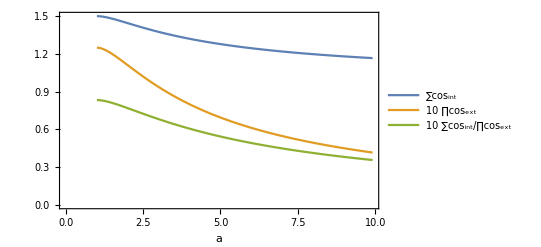

```mathematica
ListLinePlot[Transpose@Table[({{a,#[[1]]},{a,10#[[2]]},{a,10#[[2]]/#[[1]]}}&@getPoncInvariants[a,30.]),{a,1.01,10,.1}],PlotLegends->{"∑cos_int","10 ∏cos_ext","10 ∑cos_int/∏cos_ext"},FrameStyle->Medium,Frame->True,FrameLabel->{Style["a",{Black,16}],None}]
```

#### N = 3 external ellipse (a, b), internal ellipse (a0, b0), st a0/a + b0/b = 1, a0=a-b0(a/b), b0 ∈ (0,1)

```mathematica
Clear@getPoncPencil;
getPoncPencil[a_,a0_,b0_,u_]:=Module[{Pouter,tangs,feet,triPonc},
Pouter={a Cos@u,Sin@u};
tangs=ellTangentsb[a0,b0,Pouter];
feet=(ellInterRayUnprot[a,Pouter,#-Pouter][[2]])&/@tangs;
triPonc={Pouter,Sequence@@feet};
getTriInfo[triPonc,tangs,feet]];
```

```mathematica
getPoncPencil[1.5,.5,1.,.1]
```

<|tri→{{1.49251,0.0998334},{0.0975126,-0.997885},{0.0798378,0.998583}},sides→{1.99655,1.67433,1.7751},exc→{{-1.84107,-0.0671238},{1.41052,1.73684},{1.58321,-1.7112}},orthic→{{0.0879046,0.0873984},{0.996608,0.415327},{1.05683,-0.242996}},act→{{-1.31516,-0.0991356},{1.47483,2.0963},{1.51018,-1.89663}},coss→{0.331108,0.611415,0.544229},cosSum→1.48675,sinSum→2.11633,sinProd→0.344186,cosProd→0.110176,tangs→{{0.183065,-0.930564},{0.151568,0.952947}},feet→{{0.0975126,-0.997885},{0.0798378,0.998583}},per→5.44598,per2→9.94057,area→1.40223,r→0.51496,R→1.05795,inc→{0.603169,0.0552923},bar→{0.556619,0.0335104},cir→{0.438957,0.00344998},ort→{0.791942,0.0936313},npc→{0.61545,0.0485406},sym→{0.651306,0.0751495},ger→{0.659278,0.0707},nag→{0.463519,-0.0100533},mit→{0.505289,0.0149156},spi→{0.533344,0.0226195},feu→{0.151909,0.303381},x100→{1.36604,-0.506231}|>

```mathematica
ptClrs
```

{ell→-Graphics-,med→-Graphics-,bar→-Graphics-,inc→-Graphics-,ort→-Graphics-,cir→-Graphics-,npc→-Graphics-,exc→-Graphics-,ex12→-Graphics-,ex23→-Graphics-,ex31→-Graphics-,dar→-Graphics-,x144→-Graphics-,feu→-Graphics-,antifeu→-Graphics-,anticompl→-Graphics-,steiner→-Graphics-,steinerinell→-Graphics-,x88→-Graphics-,x100→-Graphics-,nag→-Graphics-,mit→-Graphics-,sym→-Graphics-,bev→-Graphics-,ger→-Graphics-,spi→-Graphics-,nap→-Graphics-,hex→-Graphics-,red→-Graphics-,green→-Graphics-,blue→-Graphics-}

```mathematica
Clear@drawPonceletPencil;
Options@drawPonceletPencil={drLabels->False,drLoci->False,drExc->False,drOrthic->False,drAct->False,drCircs->False,degStep->1.,degMax->360};
drawPonceletPencil[a_,b0_,u_,OptionsPattern[]]:=Module[{a0,ell,ellInt,gr,fs,tri,lab,
locs,ctrs,lociExc},
ctrs={"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi","feu","x100"};
ell=plotEll[a,{Thick,Black}];
a0=a(1-b0);(* Cayley *)
ellInt=plotEllb[a0,b0,{Thick,Gray}];
fs=getFoci[a];
tri=getPoncPencil[a,a0,b0,u];
lociExc=If[OptionValue@drLoci&&OptionValue@drExc,Table[getPoncPencil[a,a0,b0,toRad@(v+.001)]["exc"][[1]],{v,0,OptionValue@degMax,OptionValue@degStep}],{}];
If[OptionValue@drLoci,locs=Transpose@Table[getPoncPencil[a,a0,b0,toRad@(v+.001)][#]&/@ctrs,{v,0,OptionValue@degMax,OptionValue@degStep}]];
gr=Graphics[{PointSize@Large,FaceForm@None,Thick,
{PointSize@Medium,Black,Point@fs,Gray,Point@{0,0}},
{Blue,Point@tri["tri"][[1]],(*Point@tri["tangs"],*)Line@{tri["tri"][[1]],#}&/@tri["feet"],Point@tri["feet"],(*Dashed,*)Line@tri["feet"]},
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@tri["exc"]},{}],
If[OptionValue@drAct,{EdgeForm@{Thick,Lighter@Blue},Polygon@tri["act"],Lighter@Blue,Point[getCircumcenter@@tri["act"]]},{}],
If[OptionValue@drOrthic,{EdgeForm@{Thick,Orange},Polygon@tri["orthic"],Red,Point@tri["orthic"][[1]],Point@tri["tri"][[1]]},{}],
If[OptionValue@drCircs,
{{Purple,Circle[tri["cir"],tri["R"]]},
{Pink,Circle[tri["npc"],tri["R"]/2]}},{}],
If[OptionValue@drLoci,
{MapThread[{#1/.ptClrs,Line@#2}&,{ctrs,locs}]},{}],
If[OptionValue@drLoci&&OptionValue@drExc,{Thick,Darker@Green,Line@lociExc},{}],
If[OptionValue@drLabels,
MapThread[{#2/.ptClrs,Text[Style[Subscript["X",#1],14],tri[#2],{0,-1.5}],Point@tri[#2]}&,
{{1,2,3,4,5,6,7,8,9,10,11,100},ctrs}],
{}]
}];
lab="a="<>nfn[a,2]<>", (a_(0,)b_0)=("<>nfn[a0,3]<>","<>nfn[b0,3]<>")"<>", r="<>nfn[tri["r"],3]<>", R="<>nfn[tri["R"],3]<>", L="<>nfn[tri["per"],3]<>", A="<>nfn[tri["area"],3]<>", r*R="<>nfn[tri["r"]*tri["R"],3]<>"\n∑cos="<>nfn[tri["cosSum"],3]<>", ∏cos="<>nfn[tri["cosProd"],3]<>", ∑sin="<>nfn[tri["sinSum"],3]<>", ∏sin="<>nfn[tri["sinProd"],3]<>", ∑l^2="<>nfn[tri["per2"],3];
If[OptionValue@drExc,Module[{s,re,Re,Ae},
s=triLengths@tri["exc"];
re=getInradius[s];
Re=getCircumradius[s];
Ae=signedArea[tri["exc"]];
lab=lab<>"\nL_e="<>nfn[Total@s,3]<>", A_e="<>nfn[Ae,3]<>", r_e="<>nfn[re,3]<>", R_e="<>nfn[Re,3]<>", r_e/R_e="<>nfn[re/Re,3]]];
If[OptionValue@drOrthic,Module[{s,rh,Rh,Ah,altSum,altSumInv,altProd,Aratio},
s=triLengths@tri["orthic"];
rh=getInradius[s];
Rh=getCircumradius[s];
Ah=signedArea[tri["orthic"]];
Aratio=tri["area"]/Ah;
altSum=Total@MapThread[magn[#1-#2]&,{tri["tri"],tri["orthic"]}];
altProd=Apply[Times,MapThread[magn[#1-#2]&,{tri["tri"],tri["orthic"]}]];
altSumInv=Total@MapThread[1/magn[#1-#2]&,{tri["tri"],tri["orthic"]}];
lab=lab<>"\nL_h="<>nfn[Total@s,3]<>", A_h="<>nfn[Ah,3]<>", r_h="<>nfn[rh,3]<>", R_h="<>nfn[Rh,3]<>", r_h/R_h="<>nfn[rh/Rh,3]<>", ∑alts="<>nfn[altSum,3]<>", ∏alts="<>nfn[altProd,3]<>", A/A_h="<>nfn[Aratio,3]]];
If[OptionValue@drAct,Module[{s,ra,Ra,Aa},
s=triLengths@tri["act"];
ra=getInradius[s];
Ra=getCircumradius[s];
Aa=signedArea[tri["act"]];
lab=lab<>"\nL_act="<>nfn[Total@s,3]<>", A_act="<>nfn[Aa,3]<>", r_act="<>nfn[ra,3]<>", R_a="<>nfn[Ra,3]<>", r_act/R_act="<>nfn[ra/Ra,3]]];
Show[{ell,ellInt,gr},PlotLabel->Style[lab,{16,Black}],ImageSize->800,
PlotRange->{1.1{-a,a},1.1{-1,1}}]];
```

#### a0/a + b0 == 1 (1) a^2 - 1 = c^2 = a0^2 - b0^2 a0^2= b0^2 + a^2 -1 Sqrt[b0^2 + a^2 -1] + a b0 == a b0^2 == a0^2 - a^2 + 1 a0/a + Sqrt[a0^2 - a^2 + 1] = 1

```mathematica
confocalN3b0dsr[a_]=1/(a^2+√(1-a^2+a^4));
```

```mathematica
confocalN3b0dsr[2.]
```

0.131483

```mathematica
confocalN3b0[a_]=b0/.Solve[Sqrt[b0^2+a^2-1]+a b0==a,b0][[1]]
```

(a^2-√(1-a^2+a^4))/(-1+a^2)

```mathematica
confocalN3b0[1.5]
```

0.23795

```mathematica
confocalN3a0[a_]=a0/.Solve[a0/a + Sqrt[a0^2 - a^2 + 1] ==1,a0][[2]]
```

(-a+√(a^2-a^4+a^6))/(-1+a^2)

```mathematica
Manipulate[
b0=If[inner=="billiard",N@confocalN3b0[a],b0];
b0=If[inner=="circle",a/(a+1),b0];
b0=N@b0;
drawPonceletPencil[N@a,N@b0,toRad@(tDeg+10^-5),
drCircs->drCircs0,
drExc->drExc0,drOrthic->drOrthic0,drAct->drAct0,
drLoci->drLoci0,
drLabels->drLabels0,
degStep->.5,
degMax->150.],
{{inner,"none"},{"none","billiard","circle"}},
{{a,2},1.01,3},
{{b0,.25},0.05,.95,.01},
{{tDeg,30},-180,180,1},
{{drCircs0,False},{False,True}},
{{drLoci0,False},{False,True}},
{{drLabels0,False},{False,True}},
{{drExc0,False},{False,True}},
{{drAct0,False},{False,True}},
{{drOrthic0,False},{False,True}}]
```

#### X4 is point: Prof. Arseniy: when circumellipse and inellipse w/ center at orthocenter are dual, so it does not depend on triangles Check that a0*a = b0*b

a0*a = b0*b ⇒ a0=b0*(b/a)
with a0/a+b0/b=1 ⇒ b0/a^2+b0=b ⇒ b0(1/a^2+1)=b ⇒b0=b(a^2+1)

```mathematica
b0forX4point[a_,b_]=b0/.First@Solve[{(b0(b/a))/a+b0/b==1},b0]
```

(a^2 b)/(a^2+b^2)

```mathematica
b0forX4point[a,1]
```

a^2/(1+a^2)

```mathematica
N@b0forX4point[2.,1]
```

0.8

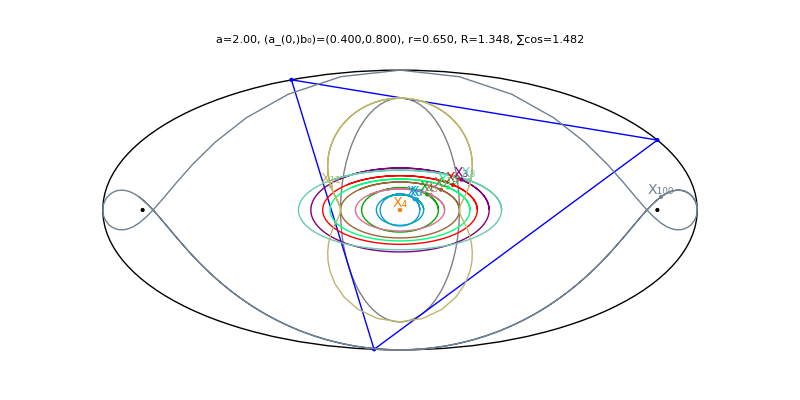

```mathematica
drawPonceletPencil[N@2,N@b0forX4point[2.,1.],toRad@30,
drLoci->True,
drLabels->True,
degStep->.5,
degMax->150.]
```

#### Next steps : - Analisar loci dos pontos onde (a0, b0) é fixo, e variamos a elipse externa. - Já sabemos que quando a=b=(a0+b0), X3 fica estacionário. - Será q outros pontos ficam estacionários neste sub-espaço?

```mathematica
Clear@getPoncPencilOuter;
getPoncPencilOuter[a_,a1_,b1_,u_]:=Module[{Pouter,tangs,feet,triPonc},
Pouter={a1 Cos@u,b1 Sin@u};
tangs=ellTangents[a,Pouter];
feet=(ellInterRaybUnprot[a1,b1,Pouter,#-Pouter][[2]])&/@tangs;
triPonc={Pouter,Sequence@@feet};
getTriInfo[triPonc,tangs,feet]];
```

#### when: external (a,1), internal (a0,b0): a0/a+b0/b=1 here internal (a,1). external = (a1,b1) ⇒ a/a1+1/b1=1⇒ a + a1 / b1 = a1 ⇒ a1(1-1/b1)=a ⇒a1 = a b1 /(b1-1)

```mathematica
Clear@drawPonceletPencilOuter;
Options@drawPonceletPencilOuter={drLabels->False,drLoci->False,drExc->False,drOrthic->False,drAct->False,drCircs->False,degStep->1.,degMax->360,drFeu->True};
drawPonceletPencilOuter[a_,b1_,u_,OptionsPattern[]]:=Module[{a1,ell,ellOut,gr,fs,tri,lab,
locs,ctrs,lociExc},
ctrs=If[OptionValue@drFeu,
{"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi","feu","x100"},
{"inc","bar","cir","ort","npc","sym","ger","nag","mit","spi"}];
ell=plotEll[a,{Thick,Black}];
a1=a b1/(b1-1);(* Cayley *)
ellOut=plotEllb[a1,b1,{Thick,Gray}];
fs=getFoci[a];
tri=getPoncPencilOuter[a,a1,b1,u];
lociExc=If[OptionValue@drLoci&&OptionValue@drExc,Table[getPoncPencilOuter[a,a1,b1,toRad@(v+.001)]["exc"][[1]],{v,0,OptionValue@degMax,OptionValue@degStep}],{}];
If[OptionValue@drLoci,locs=Transpose@Table[getPoncPencilOuter[a,a1,b1,toRad@(v+.001)][#]&/@ctrs,{v,0,OptionValue@degMax,OptionValue@degStep}]];
gr=Graphics[{PointSize@Large,FaceForm@None,Thick,
{PointSize@Medium,Black,Point@fs,Gray,Point@{0,0}},
{Blue,Point@tri["tri"][[1]],(*Point@tri["tangs"],*)Line@{tri["tri"][[1]],#}&/@tri["feet"],Point@tri["feet"],(*Dashed,*)Line@tri["feet"]},
If[OptionValue@drExc,{EdgeForm@{Thick,Darker@Green},Polygon@tri["exc"]},{}],
If[OptionValue@drAct,{EdgeForm@{Thick,Lighter@Blue},Polygon@tri["act"],Lighter@Blue,Point[getCircumcenter@@tri["act"]]},{}],
If[OptionValue@drOrthic,{EdgeForm@{Thick,Orange},Polygon@tri["orthic"],Red,Point@tri["orthic"][[1]],Point@tri["tri"][[1]]},{}],
If[OptionValue@drCircs,
{{Purple,Circle[tri["cir"],tri["R"]]},
{Pink,Circle[tri["npc"],tri["R"]/2]},
{Darker@Green,Circle[tri["inc"],tri["r"]]}},{}],
If[OptionValue@drLoci,
{MapThread[{#1/.ptClrs,Line@#2}&,{ctrs,locs}]},{}],
If[OptionValue@drLoci&&OptionValue@drExc,{Thick,Darker@Green,Line@lociExc},{}],
If[OptionValue@drLabels,
MapThread[{#2/.ptClrs,Text[Style[Subscript["X",#1],14],tri[#2],{0,-1.5}],Point@tri[#2]}&,
{If[OptionValue@drFeu,{1,2,3,4,5,6,7,8,9,10,11,100},{1,2,3,4,5,6,7,8,9,10}],ctrs}],
{}]
}];
lab="a="<>nfn[a,2]<>", (a_(1,)b_1)=("<>nfn[a1,3]<>","<>nfn[b1,3]<>")"<>", r="<>nfn[tri["r"],3]<>", R="<>nfn[tri["R"],3]<>", L="<>nfn[tri["per"],3]<>", A="<>nfn[tri["area"],3]<>", A/L="<>nfn[tri["area"]/tri["per"],3]<>"\n∑cos="<>nfn[tri["cosSum"],3]<>", ∏cos="<>nfn[tri["cosProd"],3]<>", ∑sin="<>nfn[tri["sinSum"],3]<>", ∏sin="<>nfn[tri["sinProd"],3]<>", ∑l^2="<>nfn[tri["per2"],3];
If[OptionValue@drExc,Module[{s,re,Re,Ae},
s=triLengths@tri["exc"];
re=getInradius[s];
Re=getCircumradius[s];
Ae=signedArea[tri["exc"]];
lab=lab<>"\nL_e="<>nfn[Total@s,3]<>", A_e="<>nfn[Ae,3]<>", r_e="<>nfn[re,3]<>", R_e="<>nfn[Re,3]<>", r_e/R_e="<>nfn[re/Re,3]]];
If[OptionValue@drOrthic,Module[{s,rh,Rh,Ah,altSum,altSumInv,altProd,Aratio},
s=triLengths@tri["orthic"];
rh=getInradius[s];
Rh=getCircumradius[s];
Ah=signedArea[tri["orthic"]];
Aratio=tri["area"]/Ah;
altSum=Total@MapThread[magn[#1-#2]&,{tri["tri"],tri["orthic"]}];
altProd=Apply[Times,MapThread[magn[#1-#2]&,{tri["tri"],tri["orthic"]}]];
altSumInv=Total@MapThread[1/magn[#1-#2]&,{tri["tri"],tri["orthic"]}];
lab=lab<>"\nL_h="<>nfn[Total@s,3]<>", A_h="<>nfn[Ah,3]<>", r_h="<>nfn[rh,3]<>", R_h="<>nfn[Rh,3]<>", r_h/R_h="<>nfn[rh/Rh,3]<>", ∑alts="<>nfn[altSum,3]<>", ∏alts="<>nfn[altProd,3]<>", A/A_h="<>nfn[Aratio,3]]];
If[OptionValue@drAct,Module[{s,ra,Ra,Aa},
s=triLengths@tri["act"];
ra=getInradius[s];
Ra=getCircumradius[s];
Aa=signedArea[tri["act"]];
lab=lab<>"\nL_act="<>nfn[Total@s,3]<>", A_act="<>nfn[Aa,3]<>", r_act="<>nfn[ra,3]<>", R_a="<>nfn[Ra,3]<>", r_act/R_act="<>nfn[ra/Ra,3]]];
Show[{ell,ellOut,gr},PlotLabel->Style[lab,{16,Black}],ImageSize->800,
PlotRange->{1.1{-2a,2a},1.1{-b1,b1}}]];
```

a/a1 + 1/b0 == 1 (1)
a^2 - 1 = c^2 = a1^2 - b1^2

a1 = Sqrt[ b1^2 + a^2 - 1]

a/Sqrt[b1^2 + a^2 - 1] + 1/ b1 == 1
b1 a/Sqrt[b1^2 + a^2 - 1] + 1 == b1
b1 a  = (b1-1)Sqrt[b1^2 + a^2 - 1] 
b1^2 a^2 == (b1-1)^2 (b1^2 + a^2 - 1)

```mathematica
Manipulate[
(*b1=If[inner=="billiard",N@confocalN3b1[a],b1];*)
b1=If[inner=="circle",(a+1),b1];
b1=N@b1;
drawPonceletPencilOuter[N@a,N@b1,toRad@(tDeg+10^-5),
drCircs->drCircs0,
drExc->drExc0,drOrthic->drOrthic0,
drAct->drAct0,
drLoci->drLoci0,
drLabels->drLabels0,
drFeu->drFeu0,
degStep->2.5,
degMax->150.],
{{inner,"none"},{"none","billiard","circle"}},
{{a,2},1.01,3},
{{b1,2},1.05,5,.01,AnimationRate->10},
{{tDeg,30},-180,180,1},
{{drCircs0,False},{False,True}},
{{drFeu0,True},{False,True}},
{{drLoci0,False},{False,True}},
{{drLabels0,False},{False,True}},
{{drExc0,False},{False,True}},
{{drAct0,False},{False,True}},
{{drOrthic0,False},{False,True}}]
```

#### Scan for Point Loci

```mathematica
Clear@getPoncPencilb;
getPoncPencilb[a_,b_,a0_,b0_,u_]:=Module[{Pouter,tangs,feet,triPonc},
Pouter={a Cos@u,b Sin@u};
tangs=ellTangentsb[a0,b0,Pouter];
feet=(ellInterRaybUnprot[a,b,Pouter,#-Pouter][[2]])&/@tangs;
triPonc={Pouter,Sequence@@feet};
getTriInfo[triPonc,tangs,feet]];
```

#### a0/a + b0/b == 1 ⇒ a0 = a - b0 (a/b) = a(1-b0/b)

```mathematica
Clear@getOnePoncLow;
getOnePoncLow[a_,b_,b0_,t_]:=Module[{a0,tri},
a0=a(1-b0/b);
tri=getPoncPencilb[a,b,a0,b0,t];
tri];
```

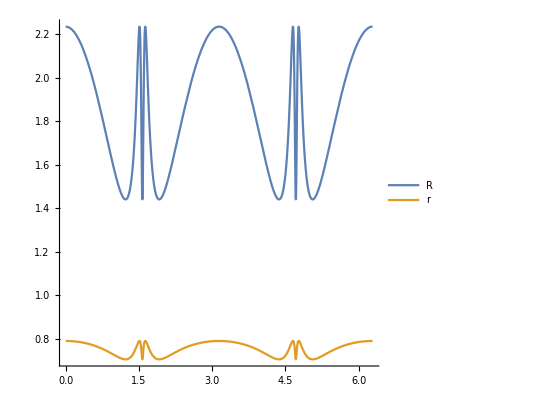

```mathematica
Module[{p,eps=10^-9,a=4},
Quiet@Plot[
Evaluate[p=getOnePoncLow[a,1,b0forX4point[a,1],t+eps];
{p["R"],p["r"]}],{t,0,2π},AspectRatio->1,PlotLegends->{"R","r"}]]
```

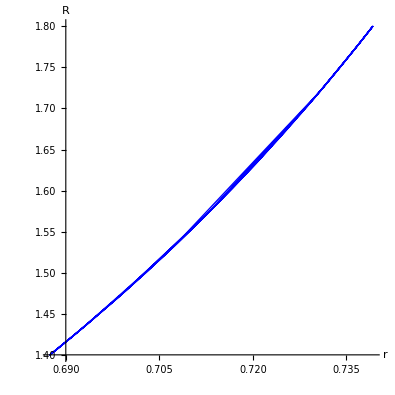

```mathematica
rRplot=Module[{p,eps=10^-9,a=3},
Quiet@ParametricPlot[
p=getOnePoncLow[a,1,b0forX4point[a,1],t+eps];
{p["r"],p["R"]},{t,0,π},PerformanceGoal->"Quality",PlotStyle->{Thick,Blue},AspectRatio->1,AxesLabel->(Style[#,20]&/@{"r","R"})]]
```

{0.999989}

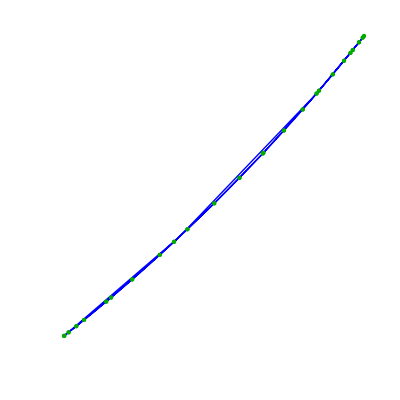

```mathematica
Module[{p,a=3,eps=10^-6,rR,fit,fitPlot,rMin,rMax,rRplot},
rR=Table[p=getOnePoncLow[a,1,b0forX4point[a,1],t+eps];
{p["r"],p["R"]},{t,0,π,π/50}];
rMin=Min[First/@rR];
rMax=Max[First/@rR];
fit=LinearModelFit[rR,{1,x,x^2},x];
Print[fit[{"RSquared"}]];
rRplot=Quiet@Graphics[{Thick,Blue,
Line@Table[p=getOnePoncLow[a,1,b0forX4point[a,1],t+eps];
{p["r"],p["R"]},{t,π/2,π-eps,π/100}]}];
fitPlot=Plot[fit,{x,rMin,rMax},PlotStyle->Red];
Show[{rRplot,fitPlot,Graphics[{Darker@Green,PointSize@Large,Point@rR}]},PlotRange->All,AspectRatio->1,AxesLabel->(Style[#,20]&/@{"r","R"})]
]
```

```mathematica
Clear@getOnePonc;
getOnePonc[a_,b_,b0_,t_]:=Module[{a0,tri},
a0=a(1-b0/b);
tri=getPoncPencilb[a,b,a0,b0,t];
{tri["tri"],tri["sides"]}];
```

```mathematica
getOnePonc[2,1,.8,.1]
```

{{{1.99001,0.0998334},{-0.352627,-0.984334},{-0.450884,0.974257}},{1.96105,2.59279,2.58135}}

```mathematica
Clear@getPoncRads;getPoncRads[a_,b_,b0_]:=Module[{o,n,s,tri,kimbs,names,xys,rads0,rads90},
{o,s}=getOnePonc[a,b,b0,π/4.];
{kimbs,names,xys}=Transpose@getNewCenters[o,s];
rads0=magn2/@xys;
{o,s}=getOnePonc[a,b,b0,π/4+π/2.];
{kimbs,names,xys}=Transpose@getNewCenters[o,s];
rads90=magn2/@xys;
<|"rads0"->rads0,"rads90"->rads90,"radsSum"->rads0+rads90|>];
```

```mathematica
Clear@getPoncAxes;getPoncAxes[a_,b_]:=Module[{xs,ys},
ListLinePlot[Table[getPoncRads[a,b,b0]["radsSum"],{b0,.1,b-.1,.1}],PlotLegends->centerNames,ImageSize->Large]]
```

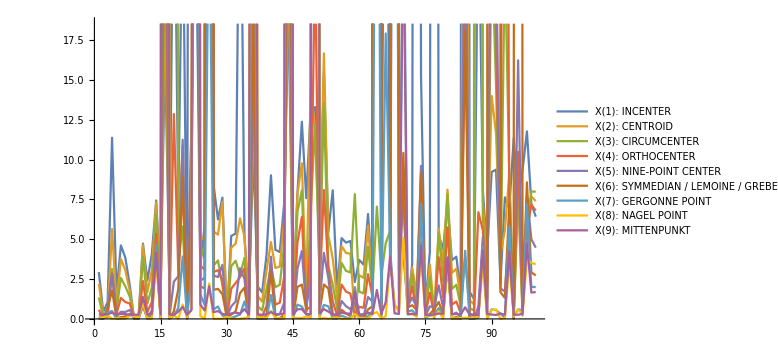

```mathematica
getPoncAxes[2,1]
```

```mathematica
Clear@getPoncRadsOne;getPoncRadsOne[a_,b_,b0_,kimb_]:=Module[{o,s,xys,rads0,rads90},
{o,s}=getOnePonc[a,b,b0,π/1000.];
xys=First@(Transpose@getNewCenters[o,s,{kimb}])[[3]];
rads0=magn2@xys;
{o,s}=getOnePonc[a,b,b0,π/1000+π/2.];
xys=First@(Transpose@getNewCenters[o,s,{kimb}])[[3]];
rads90=magn2@xys;
<|"rads0"->rads0,"rads90"->rads90,"radsSum"->rads0+rads90|>];
```

Plot radius sum

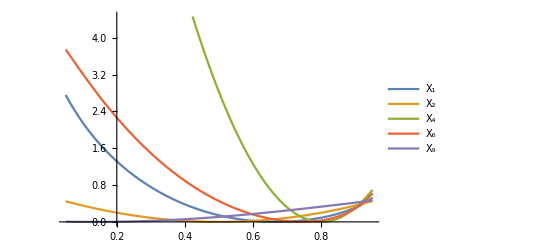

```mathematica
Plot[{
getPoncRadsOne[2,1,b0,1]["radsSum"],
getPoncRadsOne[2,1,b0,2]["radsSum"],
getPoncRadsOne[2,1,b0,4]["radsSum"],
getPoncRadsOne[2,1,b0,6]["radsSum"],
getPoncRadsOne[2,1,b0,9]["radsSum"]},{b0,.05,.95},
PlotLegends->{"X_1","X_2","X_4","X_6","X_9"}]
```

## Jair: Excentral-to-Orbit Area Ratio is Constant, and Quad/Tri Spatial Integral

```mathematica
Clear@getAreaRatio;
getAreaRatio[a_,tDeg_]:=Module[{o,n,s,exc,excSides},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
excSides=RotateLeft@triLengths@exc;
triAreaHeron@excSides/triAreaHeron@s
];
```

```mathematica
getAreaRatio[2.5,50]
```

13.1552

```mathematica
getSumProdCosines[2.5,0]
```

{1.15203,0.0380077}

```mathematica
2/(1.15203-1)
```

13.1553

```mathematica
getRadiusRatio[2.5,0]
```

0.152031

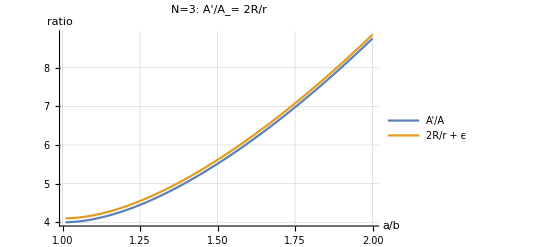

```mathematica
Plot[{Legended[getAreaRatio[a,0],"A'/A"],Legended[.1+2/getRadiusRatio[a,0],"2R/r + ϵ"]},{a,1.01,2},PlotLabel->Style["N=3: A'/A_= 2R/r",{Black,16}],GridLines->Automatic,AxesLabel->{"a/b","ratio"},AxesStyle->{{Black,Medium},{Black,Medium}}]
```

```mathematica
Clear@getAreaRatioOneSubtri;
Options@getAreaRatioOneSubtri={drGr->False};
getAreaRatioOneSubtri[a_,tDeg_,OptionsPattern[]]:=Module[{o,n,s,exc,ptri,pquad,atri,aquad},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
ptri={{0,0},o[[1]],o[[2]]};
atri=signedArea@ptri;
pquad={{0,0},o[[1]],exc[[3]],o[[2]]};
aquad=signedArea@pquad;
If[OptionValue@drGr,
Module[{ell,gr},
ell=plotEll[a,{Thick,Black}];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@Blue,Polygon@o,Blue,,Point@ptri,FaceForm@{Opacity@.2,Blue},Polygon@ptri},
{EdgeForm@Darker@Green,Polygon@exc,FaceForm@{Opacity@.2,Green},Polygon@pquad,Darker@Green,Point@exc[[3]]},
{Black,MapThread[Text[Style[#2,16],#1,{-1.5,-1.5}]&,{pquad,{"O","P_1","Q","P_2"}}]}}];
Print[Show[{ell,gr}]]]];
aquad/atri
];
```

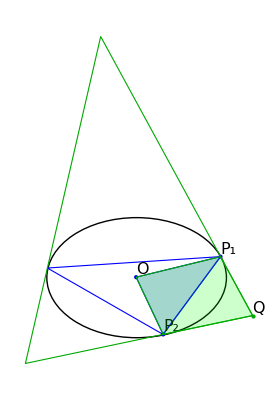

```mathematica
getAreaRatioOneSubtri[1.5,20,drGr->True];
```

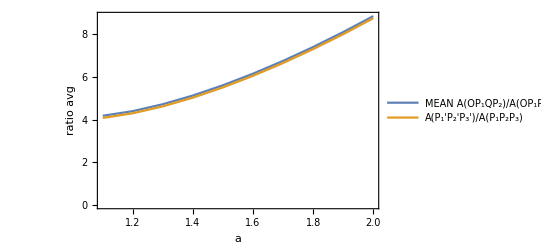

```mathematica
Module[{ratioAvgs,quadAvgs,as,epsilon=.1},
as=Range[1.1,2,.1];
quadAvgs={#,epsilon+Mean@Table[getAreaRatioOneSubtri[#,tDeg],{tDeg,0,359,1}]}&/@as;
ratioAvgs={#,getAreaRatio[#,0]}&/@as;
ListLinePlot[{Legended[quadAvgs,"MEAN A(OP_1QP_2)/A(OP_1P_2) + ϵ"],Legended[ratioAvgs,"A(P_1'P_2'P_3')/A(P_1P_2P_3)"]},
Frame->True,FrameStyle->{{Black,16},{Black,16}},FrameLabel->(Style[#,{Black,16}]&/@{"a","ratio avg"})]]
```

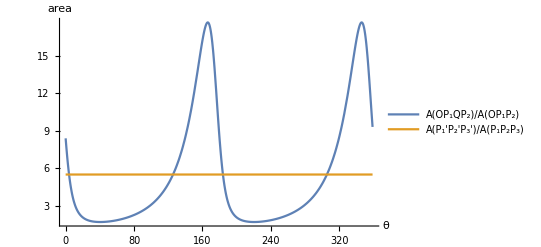

```mathematica
Plot[{
Legended[getAreaRatioOneSubtri[1.5,tDeg],"A(OP_1QP_2)/A(OP_1P_2)"],
Legended[getAreaRatio[1.5,tDeg],"A(P_1'P_2'P_3')/A(P_1P_2P_3)"]
},{tDeg,0,359},PlotRange->All,AxesLabel->{"θ","area"}]
```

## Load Loci Tables for X(1) ~ X(100) [[or generate/save]]

```mathematica
Directory[]
```

C:\Users\drezn\Dropbox\Mathematica\Billiards

```mathematica
Clear@getLociTable;
getLociTable[a_,ctrFn_,tmax_:π/1.2,step_:toRad[.1]]:=Module[{nc,pts,loci},
loci=Table[
nc=ctrFn[a,t]//Quiet;
pts=(#[[3]]&/@nc);
{t,pts},
{t,.5*step,tmax,step}];
Transpose[#[[2]]&/@loci]];
```

```mathematica
(*loci15t=getLociTable[1.5,newCenters];*)
```

```mathematica
doLociTables=False;
Module[{a=1.5,fname="data/loci15t.m"},
If[doLociTables,
loci15t=getLociTable[a,newCenters];
lociOrt15t=getLociTable[a,newCentersOrthic];
lociMed15t=getLociTable[a,newCentersMedial];
lociExc15t=getLociTable[a,newCentersExc,π/1.28];
lociIntouch15t=getLociTable[a,newCentersIntouch,π/1.2];
lociExtouch15t=getLociTable[a,newCentersExtouch,π/1.27];
lociAnticompl15t=getLociTable[a,newCentersAnticompl,π/1.28];
lociExfeuerbach15t=getLociTable[a,newCentersExfeuer];
Print@"saving..." ;
Save[fname,{loci15t,lociOrt15t,lociMed15t,lociExc15t,lociIntouch15t,lociExtouch15t,lociAnticompl15t,lociExfeuerbach15t}],
Print@"loading...";Get[fname]]];
```

loading...

*** GENERATES BILLIARD
X(100)  ANTICOMPLEMENT OF FEUERBACH POINT IS THE BILLIARD

*** GENERATES BILLIARD
X(88) = ISOGONAL CONJUGATE OF X(44)

X(44) = X(6)-LINE CONJUGATE OF X(1)
*** X(44) lies on these lines:
Trilinears       b + c - 2a : c + a - 2b : a + b - 2c
Barycentrics  a(b + c - 2a) : b(c + a - 2b) : c(a + b - 2c)
X(44) = (3r2 + 6rR + s2)*X(1) - 18rR*X(2) - 6r2*X(3)    (Peter Moses, April 2, 2013)

LINE-CONJUGATE: (looked up glossary)
Let P = p : q : r, U = u : v : w
The P-line conjugate of U is the point of intersection of line PU and the trilinear polar of the isogonal conjugate of U.

I.e., intersect line X(6)X(1) with the trilinear polar (TP) of the isog conjugate of X(1) which is X(1) itself.

The TP of X(1) is L1, the antiorthic axis, i.e., the orthic axis of the excentral triangle.

the orthic axis of a triangle are give by points (Oa, Ob,Oc) where each side of the orthic triangle meet the triangle sides (Oa, Ob, Oc)

-Graphics-
*** to summarize:

1) to get X(44) intersect the line connecting the incenter X(1) and the symmedian point X(6) with the orthic axis of the extriangle.
2) to get X(88) which generates the billiard, get the isogonal conjugate of X(44).

```mathematica
DynamicModule[{a=1.5,o,n,s,gr,ell,o2,o3,locus2,exc,exc2,locusExc2,causticAB,ellCaustic},
ell=plotEll[a,{Thick,Black}];
locus2=Table[Module[{o2a,n2a,s2a},
{o2a,n2a,s2a}=orbitNormals[a,toRad@tDeg2+.01];
{o2a[[1,1]]/a,o2a[[1,2]]}],{tDeg2,0,359,1}];
locusExc2=Table[Module[{o2a,n2a,s2a,exc2a},
{o2a,n2a,s2a}=orbitNormals[a,toRad@tDeg2+.01];
exc2a=excentralTriangle[o2a,s2a];
{exc2a[[1,1]]/a,exc2a[[1,2]]}],{tDeg2,0,359,1}];
causticAB=getTriCausticParams[a];
ellCaustic=plotEllb[Sequence@@causticAB,{Thick,Brown}];
Manipulate[
{o,n,s}=orbitNormals[a,toRad@tDeg+.01];
exc=excentralTriangle[o,s];
o2={#[[1]]a/ causticAB[[1]],#[[2]]/causticAB[[2]]}&/@o;
exc2={#[[1]]/a,#[[2]]}&/@exc;
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@o,Blue,Point@o},
{EdgeForm@{Thick,Dashed,Blue},Polygon@o2,Blue,Point@o2}
(*,{EdgeForm@{Thick,Darker@Green},Polygon@exc,Darker@Green,Point@exc},
{EdgeForm@{Thick,Dashed,Darker@Green},Polygon@exc2,Darker@Green,Point@exc2},
{Blue,Line@locus2},
{Darker@Green,Line@locusExc2}*)
}];
Show[{ell,ellCaustic,gr},PlotRange->{{-3,3},{-3,3}}],
{{tDeg,30},-180,180,1}]]
```

Show::gcomb: Could not combine the graphics objects in {plotEll[1.5`, {Thickness[Large], InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

#### Order - Dependent has to change that

```mathematica
Clear@showLoci;
showLoci[locus_,a_,lociList_,
auto_,range_,imgSize_:400]:=Module[{ell,ellCaustic,ca,cb,name,lociMaxX,maxX,lociMaxY,maxY,pts,clrs,ncs,lls},
ell=plotEll[a,Black];
{ca,cb}=getTriCausticParams[a];
ellCaustic=plotEllb[ca,cb,{Dashed,Black}];
ncs=#[[locus]]&/@lociList;
clrs={
Black(* billiard *),
{Dashed,Black}(*caustic*),
Blue,(* orbit *)
Red,(* medial *)
"ort"/.ptClrs,(* orthic *)
"inc"/.ptClrs,(* intouch *)
{Dashed,Blue},(* excentral *)
{Dashed,"inc"/.ptClrs},(* extouch *)
{Dashed,Red},(* anticompl *)
"feu"/.ptClrs (* feuer *)
};
pts={PointSize@Medium,MapThread[{If[ListQ@#1,Second@#1,#1],Point@#2[[1]]}&,{Drop[clrs,2],ncs}]};
name=centerNames[[locus]];
(* NEED NOT DO THIS FOR ALL LOCI!!! *)
lociMaxX=clamp[#,10]&/@Table[Max[Select[Join[{a},Sequence@@((First/@(#[[l]]))&/@lociList)],NumberQ]],
{l,1,Length@lociList[[1]]}];
lociMaxY=clamp[#,10]&/@Table[Max[Select[Join[{1},(* b = 1 *) Sequence@@((Second/@(#[[l]]))&/@lociList)],NumberQ]],
{l,1,Length@lociList[[1]]}];
lls=MapThread[ListLinePlot[#1[[locus]],ClippingStyle->None,PlotStyle->#2]&,{lociList,Drop[clrs,2]}];
{maxX,maxY}=If[auto,
1.1{lociMaxX[[locus]],lociMaxY[[locus]]},
{range,range}];
Legended[Show[{ell,ellCaustic,Sequence@lls,Graphics@pts},
ImageSize->{imgSize,imgSize},
Axes->True,
PlotLabel->Style[name,Directive[{Black,14}]],
PlotRange->{{-maxX,maxX},{-maxY,maxY}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"billiard","caustic","orbit",
"medial","orthic","intouch","excentral","extouch","anticompl","feuerbach"}]]];
```

```mathematica
lociList15t={loci15t,lociMed15t,lociOrt15t,lociIntouch15t,lociExc15t,lociExtouch15t,lociAnticompl15t,lociExfeuerbach15t};
```

```mathematica
showLoci[2,1.5,lociList15t, True,2,200]
```

Part::partd: Part specification loci15t ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification lociMed15t ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification lociOrt15t ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ReplaceAll::reps: {ptClrs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ListLinePlot::lpn: loci15t ⟦ 2 ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

Show::gcomb: Could not combine the graphics objects in {plotEll[1.5`, InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

Show[{plotEll[1.5,-Graphics-],plotEllb[1.14307,0.23795,{Dashing[{Small,Small}],-Graphics-}],{ListLinePlot[loci15t⟦2⟧,ClippingStyle→None,PlotStyle→-Graphics-],ListLinePlot[lociMed15t⟦2⟧,ClippingStyle→None,PlotStyle→-Graphics-],ListLinePlot[lociOrt15t⟦2⟧,ClippingStyle→None,PlotStyle→(ort/.ptClrs)],ListLinePlot[lociIntouch15t⟦2⟧,ClippingStyle→None,PlotStyle→(inc/.ptClrs)],ListLinePlot[lociExc15t⟦2⟧,ClippingStyle→None,PlotStyle→{Dashing[{Small,Small}],-Graphics-}],ListLinePlot[lociExtouch15t⟦2⟧,ClippingStyle→None,PlotStyle→{Dashing[{Small,Small}],inc/.ptClrs}],ListLinePlot[lociAnticompl15t⟦2⟧,ClippingStyle→None,PlotStyle→{Dashing[{Small,Small}],-Graphics-}],ListLinePlot[lociExfeuerbach15t⟦2⟧,ClippingStyle→None,PlotStyle→(feu/.ptClrs)]},-Graphics-},ImageSize→{200,200},Axes→True,PlotLabel→centerNames⟦2⟧,PlotRange→{{-1.1 {}⟦2⟧,1.1 {}⟦2⟧},{-1.1 {}⟦2⟧,1.1 {}⟦2⟧}}]

#### Feuerbach point of anticomplementary triangle sweeps the billiard just like the anticomplement of feuerbach of reference triangle.

Part::partd: Part specification loci15t ⟦ 11 ⟧ is longer than depth of object.

Part::partd: Part specification lociAnticompl15t ⟦ 11 ⟧ is longer than depth of object.

Part::partd: Part specification centerNames ⟦ 11 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListLinePlot::lpn: loci15t ⟦ 11 ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Part::partw: Part 11 of {} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

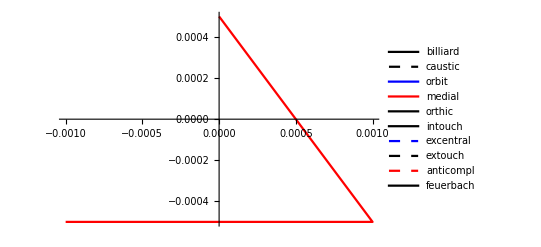
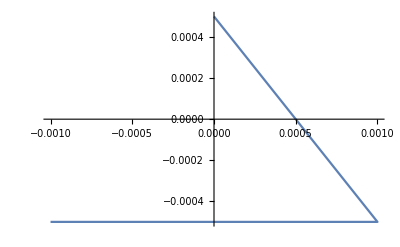
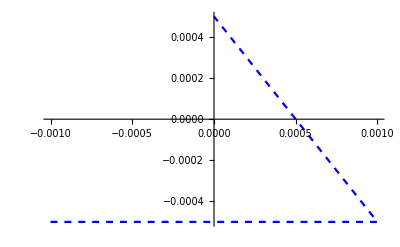
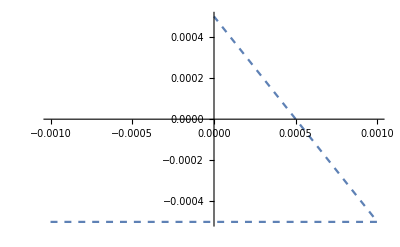
Show[{plotEll[1.5,-Graphics-],plotEllb[1.14307,0.23795,{Dashing[{Small,Small}],-Graphics-}],{ListLinePlot[loci15t⟦11⟧,ClippingStyle→None,PlotStyle→-Graphics-],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,ListLinePlot[lociAnticompl15t⟦11⟧,ClippingStyle→None,PlotStyle→{Dashing[{Small,Small}],-Graphics-}],-Graphics-},-Graphics-},ImageSize→{500,500},Axes→True,PlotLabel→centerNames⟦11⟧,PlotRange→{{-1.1 {}⟦11⟧,1.1 {}⟦11⟧},{-1.1 {}⟦11⟧,1.1 {}⟦11⟧}}]

```mathematica
Module[{d=.001,loci0},
(* fake other empty loci *)
loci0=ConstantArray[{{-d,-d/2},{d,-d/2},{0,d/2}},100];
showLoci[11,1.5,{loci15t,loci0,loci0,loci0,loci0,loci0,lociAnticompl15t,loci0},
True,2,500]]
```

Part::partd: Part specification loci15t ⟦ 6 ⟧ is longer than depth of object.

Part::partd: Part specification centerNames ⟦ 6 ⟧ is longer than depth of object.

Part::partd: Part specification loci15t ⟦ 6 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListLinePlot::lpn: loci15t ⟦ 6 ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Part::partw: Part 6 of {} does not exist.

Show::gcomb: Could not combine the graphics objects in ….

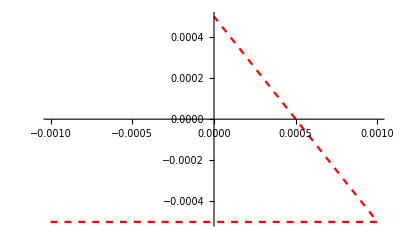
Show[{plotEll[1.5,-Graphics-],plotEllb[1.14307,0.23795,{Dashing[{Small,Small}],-Graphics-}],{ListLinePlot[loci15t⟦6⟧,ClippingStyle→None,PlotStyle→-Graphics-],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-},ImageSize→{500,500},Axes→True,PlotLabel→centerNames⟦6⟧,PlotRange→{{-1.1 {}⟦6⟧,1.1 {}⟦6⟧},{-1.1 {}⟦6⟧,1.1 {}⟦6⟧}}]

```mathematica
Module[{d=.001,loci0},
(* fake other empty loci *)
loci0=ConstantArray[{{-d,-d/2},{d,-d/2},{0,d/2}},100];
showLoci[6,1.5,{loci15t,loci0,loci0,loci0,loci0,loci0,loci0,loci0},
True,2,500]]
```

```mathematica
showAllLoci=False;
If[showAllLoci,
Manipulate[showLoci[locus,1.5,lociList15t,
auto,range,500],
{{locus,1},1,Length@loci15t,1,Appearance->"Open"},
{{auto,True},{True,False}},
{{range,2},{1,2,4,8,16}},SaveDefinitions->True]];
```

## Save Loci Frames to File

```mathematica
createLociFrames=False;
If[createLociFrames,showLociFrames=Table[Print@locus;showLoci[locus,1.5,lociList15t,
True,2,500],{locus,1,Length@loci15t,1}]; 
Length@showLociFrames];
```

```mathematica
Directory[]
```

C:\Users\drezn\Dropbox\Mathematica

```mathematica
Clear@padZ;padZ[v_,n_:4]:=ToString@NumberForm[v,{n,0},NumberPadding->{"0",""},NumberPoint->""];
getLocusFname[i_]:="loci/locus_"<>padZ[i]<>".png";
```

```mathematica
createLociFrames=False;If[createLociFrames,
If[!DirectoryQ["loci"],CreateDirectory["loci"]];
MapIndexed[Export[getLocusFname[First[#2]],#1]&,showLociFrames]];
```

## Ideal Ellipses Ellliptic: X(1),X(5),X(8),X(10),X(40) Non-Elliptic: X(6)

```mathematica
Clear@xError;
xError[a_,a0_,b0_,fnTrilin_]:=Module[{o,n,s,x1s,b=1,ell1,t,gr,ell,errs,degStep=1},
x1s=Table[t=toRad@tDeg;{o,n,s}=orbitNormals[a,t];
fnTrilin[o,s],{tDeg,0,360-degStep,degStep}];
ell1=Table[t=toRad@tDeg;{a0 Cos@t,b0 Sin@t},{tDeg,0,360-degStep,degStep}];
gr=Graphics[{
{Darker@Green,Line@ell1},
{Red,Line@x1s}}];
ell=plotEll[a];
errs=Abs[ellError[a0,b0,#]]&/@x1s;
Print@getStats[errs];
Show[{ell,gr}]];
```

```mathematica
Clear@xErrorAbs;
xErrorAbs[a_,a0_,b0_,fnTrilin_]:=Module[{o,n,s,x1s,b=1,ell1,t,gr,ell,errs,degStep=1},
x1s=Table[t=toRad@tDeg;{o,n,s}=orbitNormals[a,t];
fnTrilin[o,s],{tDeg,0,360-degStep,degStep}];
ell1=Table[t=toRad@tDeg;{a0 Cos@t,b0 Sin@t},{tDeg,0,360-degStep,degStep}];
gr=Graphics[{
{Darker@Green,Line@ell1},
{Red,Line@x1s}}];
ell=plotEll[a];
errs=Abs[ellError[a0,b0,#]]&/@x1s;
getStats[errs]];
```

```mathematica
Clear@x1Error;
x1Error[a_]:=Module[{b=1,a1,b1,δ},
δ=√(a^4-a^2 b^2+b^4);
a1=(-b^2+δ)/a; 
b1=(a^2-δ)/b;
xError[a,a1,b1,getIncenterTrilin]];
```

<|n→360,mean→3.47993×10^-15,sd→4.06659×10^-15,z→0.,min→0.,max→2.25375×10^-14,median→1.55431×10^-15|>

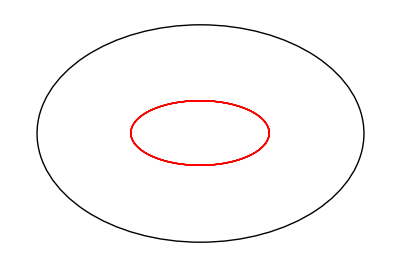

```mathematica
x1Error[1.5]
```

```mathematica
x5Error[a_]:=Module[{b=1,a5,b5,δ},
δ=√(a^4-a^2 b^2+b^4);
a5=(-a^4-3a^2b^2+3δ a^2+δ b^2)/(4a(a^2-b^2));
b5=(-b^4-3a^2b^2+3δ b^2+δ a^2)/(4b(a^2-b^2));
xError[a,a5,b5,getNinepointCenterTrilin]];
```

<|n→360,mean→3.08735×10^-15,sd→3.52527×10^-15,z→0.,min→0.,max→1.9984×10^-14,median→1.66533×10^-15|>

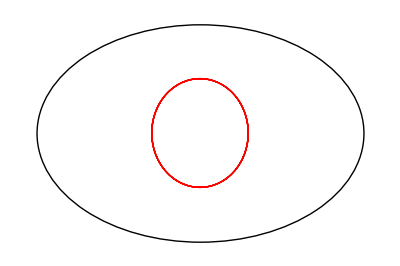

```mathematica
x5Error[1.5]
```

```mathematica
x6Error[a_]:=Module[{b=1,a6,b6,δ,denom},
δ=√(a^4-a^2 b^2+b^4);
denom=a^4+b^4+2 δ^2;
a6=(-a^2-b^4+δ(3 a^2- b^2))a/denom;
b6=(a^4+a^2 b^2+δ(a^2-3 b^2))b/denom;
xError[a,a6,b6,getSymmedianTrilin]];
```

<|n→360,mean→0.00022624,sd→0.000160217,z→0.708171,min→8.88178×10^-16,max→0.000452407,median→0.000217201|>

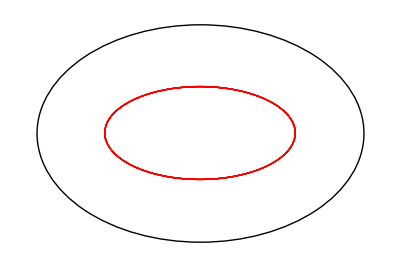

```mathematica
x6Error[1.5]
```

```mathematica
x6ErrorAbs[a_]:=Module[{b=1,a6,b6,δ,denom},
δ=√(a^4-a^2 b^2+b^4);
denom=a^4+b^4+2 δ^2;
a6=(-a^2-b^4+δ(3 a^2- b^2))a/denom;
b6=(a^4+a^2 b^2+δ(a^2-3 b^2))b/denom;
xErrorAbs[a,a6,b6,getSymmedianTrilin]["mean"]];
```

```mathematica
x6ErrorAbs[15]
```

0.0100111

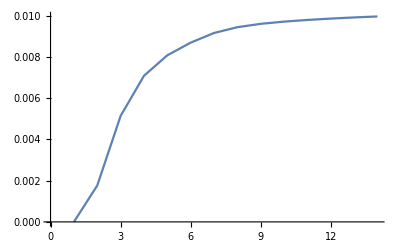

```mathematica
ListLinePlot[Table[x6ErrorAbs[a],{a,1.01,15,1}]]
```

```mathematica
x8Error[a_]:=Module[{b=1,a8,b8,δ},
δ=√(a^4-a^2 b^2+b^4);
a8=-(-a^4+a^2 b^2-2b^4+2δ b^2)/(a(a^2-b^2));
b8=(-2a^4+a^2*b^2-b^4+2δ a^2)/(b(a^2-b^2));
xError[a,a8,b8,getNagelTrilin]];
```

<|n→360,mean→1.35586×10^-14,sd→9.6563×10^-15,z→0.,min→0.,max→4.08562×10^-14,median→1.2601×10^-14|>

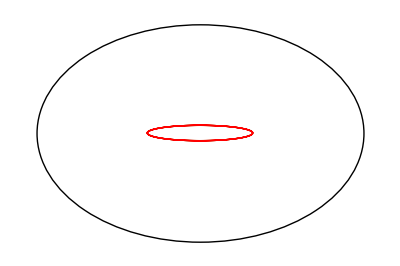

```mathematica
x8Error[1.5]
```

```mathematica
x10Error[a_]:=Module[{b=1,a10,b10,δ},
δ=√(a^4-a^2 b^2+b^4);
a10=((a^2+b^2) δ-a^4-b^4)/(2 (a^2-b^2) a);
b10=((a^2+b^2) δ-a^4-b^4)/(2 (a^2-b^2) b);
xError[a,a10,b10,getSpiekerTrilin]];
```

<|n→360,mean→7.13534×10^-15,sd→5.76233×10^-15,z→0.,min→0.,max→3.39728×10^-14,median→5.9952×10^-15|>

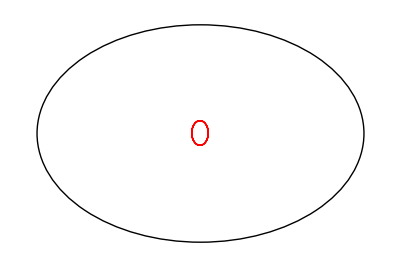

```mathematica
x10Error[1.5]
```

```mathematica
x12Error[a_]:=Module[{b=1,a12,b12,δ},
δ=√(a^4-a^2 b^2+b^4);a12=(-b^2*(15*a^6+12*a^4*b^2+3*a^2*b^4+2*b^6)+(7*a^6+12*a^4*b^2+11*a^2*b^4+2*b^6)δ)/(a(7*a^6+11*a^4*b^2-11*a^2*b^4-7*b^6));b12=(-2*a^8-3*b^2*a^6-12*a^4*b^4-15*b^6*a^2+(2*a^6+11*a^4*b^2+12*a^2*b^4+7*b^6)δ)/(b(7*a^6+11*a^4*b^2-11*a^2*b^4-7*b^6));
xError[a,a12,b12,getX12Trilin]];
```

<|n→360,mean→3.20423×10^-15,sd→3.77101×10^-15,z→0.,min→0.,max→2.26485×10^-14,median→1.66533×10^-15|>

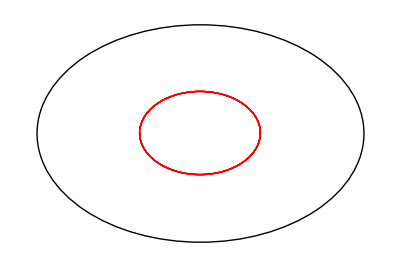

```mathematica
x12Error[1.5]
```

```mathematica
x40Error[a_]:=Module[{b=1,a40,b40},
a40=(a^2-b^2)/a;(*c^2/a*)
b40=(a^2-b^2)/b;(*c^2/b*)
xError[a,a40,b40,getBevanTrilin]];
```

<|n→360,mean→2.12793×10^-15,sd→2.00791×10^-15,z→0.,min→0.,max→1.11022×10^-14,median→1.55431×10^-15|>

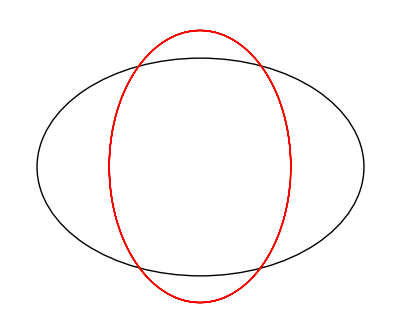

```mathematica
x40Error[1.5]
```

## Symmedian X (6) non-elliptic quadric

signed area: v1, v2, v3: (v2-v1) x (v3-v2)
v1,v2,v3,v4,v5

V=(v1,v2,v3)
U=(v2,v3,v4)
W=(v3,v4,v5)

```mathematica
Clear@symmedianErr;
Options@symmedianErr={factor->10^7,showAreas->True,symClr->Darker@Red};
symmedianErr[a_,OptionsPattern[]]:=DynamicModule[{o,n,s,x6s,a6,b6,b=1,ell6,t,gr,gr2,ell,errs,degStep=.25,tDegMax=360,x6sInter,x6,x6sMult,x6i,x6mult,signedAreas,δ,denom},
x6s=Table[t=toRad@tDeg;{o,n,s}=orbitNormals[a,t];getSymmedianTrilin[o,s],{tDeg,0,tDegMax-degStep,degStep}];
signedAreas=If[OptionValue@showAreas,MapThread[crossProduct[(#2-#1),(#3-#2)]&,{Drop[x6s,-2],Drop[RotateLeft[x6s,1],-2],Drop[RotateLeft[x6s,2],-2]}],{}];
δ=Sqrt[a^4-a^2*b^2+b^4];
denom=(3*a^4-2*a^2*b^2+3*b^4);
a6=(-b^4-a^2*b^2-δ*b^2+3*δ*a^2)*a/denom;
b6=(a^4+b^2*a^2+δ*a^2-3*δ*b^2)*b/denom;
x6sInter=ellInterRaybUnprot[a6,b6,#,-#][[1]]&/@x6s;
x6sMult=MapThread[ray[#1,#2-#1,OptionValue@factor*magn[#2-#1]]&,{x6sInter,x6s}];
ell6=Table[t=toRad@tDeg;{a6 Cos@t,b6 Sin@t},{tDeg,0,tDegMax-degStep,degStep}];
gr=Graphics[{PointSize@Large,
{Black,Point@{0,0},Text[Style["O",{Bold,16}],{0,0},{0,-1.5}]},
{Thick,Darker@Green,Line@ell6},
{OptionValue@symClr,Thick,Dashed,Line@x6sMult}}];
ell=plotEll[a,{Thick,Black}];
errs=ellError[a6,b6,#]&/@x6s;
(*Print@getStats[errs];
Print@ListLinePlot[errs];*)
If[OptionValue@showAreas,Print@ListLinePlot@signedAreas];
Manipulate[
{o,n,s}=orbitNormals[a,toRad@tDeg2];
x6=getSymmedianTrilin[o,s];
x6i=ellInterRaybUnprot[a6,b6,x6,-x6][[1]];
x6mult=ray[x6i,x6-x6i,OptionValue@factor*magn[x6-x6i]];
gr2=Graphics[{PointSize@Large,FaceForm@None,
{Black,Thick,Line@{{0,0},x6mult},ellLabelTxt[a,o[[1]],Style["P_1(t)",{Bold,16}],.075]},
{EdgeForm@{Thick,Blue},Polygon@o},
{Darker@Green,Point@x6,Text[Style["X_6",{16,Bold}],x6i,{.25,1.5}],Blue,Point@o[[1]],OptionValue@symClr,Point@x6mult,Text[Style["~X_6",{16,Bold}],x6,{-2,-1.5}]}}];
Show[{ell,gr,gr2},PlotRange->{{-1.6,1.6},{-1.1,1.1}},ImageSize->800],
{{tDeg2,60},-180,180,.1,Appearance->"Labeled"}]];
```

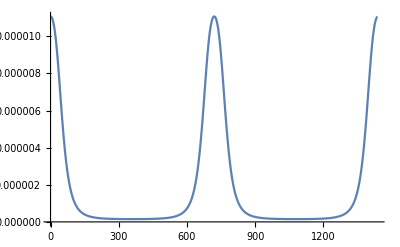

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

OptionValue::nodef: Unknown option "showAreas" for symmedianErr.

OptionValue::nodef: Unknown option "factor" for symmedianErr.

General::stop: Further output of OptionValue :: nodef will be suppressed during this calculation.

OptionValue::optnf: Option name symClr not found in defaults for symmedianErr.

```mathematica
symmedianErr[1.5,factor->2 10^6,showAreas->True]
```

#### Ronaldo's Quartic for X(6)

```mathematica
Solve[cx2 X+cy2 Y+cx2y2 X Y+cx4 X^2 +cy4 Y^2==0,Y]
```

{{Y→(-cy2-cx2y2 X-√((cy2+cx2y2 X)^2-4 cy4 (cx2 X+cx4 X^2)))/(2 cy4)},{Y→(-cy2-cx2y2 X+√((cy2+cx2y2 X)^2-4 cy4 (cx2 X+cx4 X^2)))/(2 cy4)}}

```mathematica
Clear@x6quadricY;x6quadricY[a_,b_,x_]:=Module[{a2,a4,b2,b4,a2b2,x2,x4,delta,cx4,cy4,cx2,cy2,cx2y2,discr,(* r1, *)r2},
a2=a*a;a4=a2*a2;
b2=b*b;b4=b2*b2;
a2b2=a2*b2;
x2=x*x;x4=x2*x2;
delta=Sqrt@(a4-a2b2+b4);
cx2=a2*b4(-5*a4+5*a2b2-2*b4+4*delta a2-2*delta*b2);
cy2=-a2*a2b2(2*a4-5*a2b2+5*b4+2*delta *a2-4*delta*b2);
cx2y2=2*a2b2(3*a4-2*a2b2+3*b4);
cx4=-b4*(-5*a4+6*a2b2-5*b4+4*delta a2-4*delta*b2);
cy4=a4(5*a4-6*a2b2+5*b4+4*delta a2-4*delta*b2);
discr=(cy2+cx2y2 x2)^2-4 cy4 (cx2 x2+cx4 x4);
(* r1=(-cy2-cx2y2 x2-Sqrt@discr)/(2 cy4); *)
r2=(-cy2-cx2y2 x2+Sqrt@discr)/(2 cy4);
Sqrt@r2
];
```

```mathematica
x6quadricY[1.5,1,x]
```

0.0609626 √(24.5596-61.5938 x^2+√((-24.5596+61.5938 x^2)^2-538.15 (-5.38777 x^2+7.04969 x^4)))

<|n→180,mean→3.44726×10^-15,sd→2.09183×10^-14,z→0.,min→0.,max→2.64492×10^-13,median→3.88578×10^-16|>

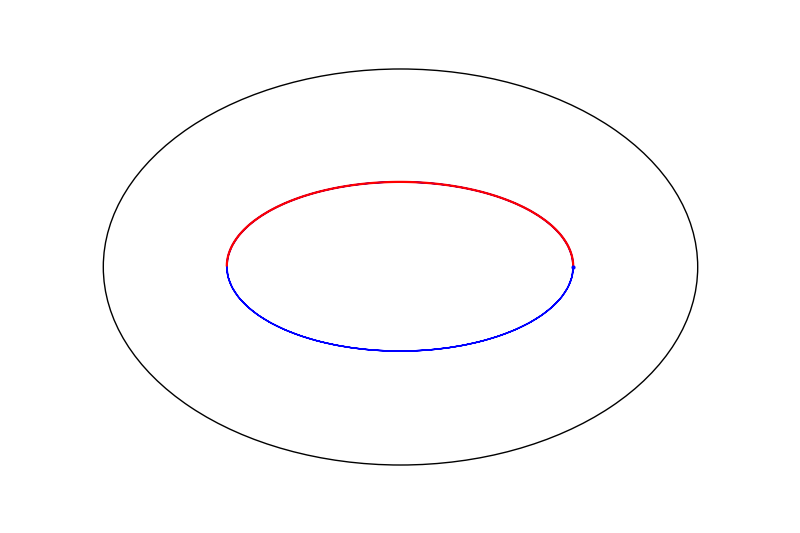

```mathematica
Module[{a=1.5,b=1,o,n,s,ell,syms,gr,delta,symMaxX,quadric,errAbs},
ell=plotEll[a,{Black,Thick}];
delta=Sqrt@(a^4-a^2*b^2+b^4);
symMaxX=(-a^2-b^4+3*delta*a^2-delta*b^2)*a/(3*a^4-2*a^2*b^2+3*b^4);
syms=Table[{o,n,s}=orbitNormals[a,toRad@t];
getSymmedianTrilin[o,s],{t,0,360,1}];
errAbs=getStats[Abs[#[[2]]-x6quadricY[a,b,#[[1]]]]&/@Select[syms,#[[2]]≥0&]];
Print@errAbs;
quadric=ParametricPlot[{x,x6quadricY[a,b,x]},{x,-symMaxX,symMaxX},PlotStyle->Red];
gr=Graphics[{Thick,PointSize@Large,
{Blue,Line@syms,Point@{symMaxX,0}}}];
Show[{ell,gr,quadric},PlotRange->{1.1{-a,a},{-1.1,1.1}}]]
```

## Predict which loci are elliptic w/ least squares

```mathematica
Clear@findEllParams;
findEllParams[a_,i_,locus_,name_]:=Module[{m,b,c,lsc,causticC,ls,lsa,lsb,err,causticA,causticB,abRatio,causticRatio,lsRatio},
abRatio=a;
c=Sqrt@Abs[a^2-1];
m=(#^2)&/@locus;(* { {x1^2,y1^2}, {x2^2,y2^2}, ... } *)
b=ConstantArray[1,Length@locus];
ls=LeastSquares[m,b];
{lsa,lsb}=Sqrt[1/#]&/@ls;
lsRatio=lsa/lsb;
lsc=Sqrt@Abs[lsa^2-lsb^2];
err=Norm[m.ls-b];
{causticA,causticB}=getTriCausticParams[a];
causticRatio=causticA/causticB;
causticC=Sqrt@Abs[causticA^2-causticB^2];
<|"i"->i,
"name"->name,
"errNegl"->(Abs[err]<10^-6),
"ellSim"->negl[abRatio-lsRatio],
"ellSimInv"->negl[abRatio-1/lsRatio],
"ellEq"->(negl[a-lsa]&&negl[1-lsb]),
"ellEqInv"->(negl[1-lsa]&&negl[a-lsb]),
"causticSim"->negl[causticRatio-lsRatio],
"causticSimInv"->negl[causticRatio-1/lsRatio],
"causticEq"->(negl[causticA-lsa]&&negl[causticB-lsb]),
"causticEqInv"->(negl[causticB-lsa]&&negl[causticA-lsb]),
"confocal"->negl[c-lsc],
"err"->err,
"a"->a,"b"->1,"a/b"->abRatio,"b/a"->(1/abRatio),
"c"->c,"lsc2"->lsc,
"lsA"->lsa,"lsB"->lsb,"lsA/lsB"->lsRatio,"lsB/lsA"->(1/lsRatio),
"caustic_a"->causticA,"caustic_b"->causticB,"caustic_a/b"->causticRatio,"caustic_b/a"->(1/causticRatio),
"caustic_c"->causticC
|>];
```

```mathematica
findEllParams[1.5,6,loci15t[[6]],centerNames[[6]]]
```

<|i→6,name→X(6): SYMMEDIAN / LEMOINE / GREBE POINT,errNegl→False,ellSim→False,ellSimInv→False,ellEq→False,ellEqInv→False,causticSim→False,causticSimInv→False,causticEq→False,causticEqInv→False,confocal→False,err→0.00616005,a→1.5,b→1,a/b→1.5,b/a→0.666667,c→1.11803,lsc2→0.762775,lsA→0.874309,lsB→0.427306,lsA/lsB→2.0461,lsB/lsA→0.488735,caustic_a→1.14307,caustic_b→0.23795,caustic_a/b→4.80384,caustic_b/a→0.208167,caustic_c→1.11803|>

```mathematica
ellParams=Quiet@Table[findEllParams[1.5,i,loci15t[[i]],centerNames[[i]]],{i,Length@loci15t}]//Sort[#,#1["err"]<#2["err"]&]&;
```

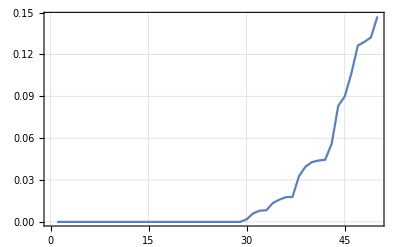

```mathematica
ListLinePlot[#["err"]&/@Take[ellParams,50],Frame->True,GridLines->Automatic]
```

```mathematica
ellParams[[1]][[Keys[ellParams[[1]]]]]
```

<|i→100,name→X(100): ANTICOMPLEMENT OF FEUERBACH POINT,errNegl→True,ellSim→True,ellSimInv→False,ellEq→True,ellEqInv→False,causticSim→False,causticSimInv→False,causticEq→False,causticEqInv→False,confocal→True,err→5.89234×10^-14,a→1.5,b→1,a/b→1.5,b/a→0.666667,c→1.11803,lsc2→1.11803,lsA→1.5,lsB→1.,lsA/lsB→1.5,lsB/lsA→0.666667,caustic_a→1.14307,caustic_b→0.23795,caustic_a/b→4.80384,caustic_b/a→0.208167,caustic_c→1.11803|>

```mathematica
MapIndexed[{First@#2,#1["i"],#1["errNegl"],#1["err"]}&,ellParams]//TableForm
```

1 | 100 | True | 5.89234×10^-14
2 | 80 | True | 8.05734×10^-14
3 | 46 | True | 8.34044×10^-14
4 | 36 | True | 1.01236×10^-13
5 | 88 | True | 1.01408×10^-13
6 | 56 | True | 1.09409×10^-13
7 | 20 | True | 1.10374×10^-13
8 | 72 | True | 1.14669×10^-13
9 | 63 | True | 1.19054×10^-13
10 | 40 | True | 1.26619×10^-13
11 | 78 | True | 1.34563×10^-13
12 | 57 | True | 1.35063×10^-13
13 | 79 | True | 1.40052×10^-13
14 | 4 | True | 1.40381×10^-13
15 | 65 | True | 1.43881×10^-13
16 | 7 | True | 1.54638×10^-13
17 | 11 | True | 1.68244×10^-13
18 | 5 | True | 1.72675×10^-13
19 | 84 | True | 1.81063×10^-13
20 | 12 | True | 1.83606×10^-13
21 | 1 | True | 1.83897×10^-13
22 | 2 | True | 2.31696×10^-13
23 | 3 | True | 2.54243×10^-13
24 | 55 | True | 2.93299×10^-13
25 | 8 | True | 3.28066×10^-13
26 | 10 | True | 3.62802×10^-13
27 | 90 | True | 3.97907×10^-13
28 | 21 | True | 4.58184×10^-13
29 | 35 | True | 4.8273×10^-13
30 | 37 | False | 0.001875
31 | 6 | False | 0.00616005
32 | 45 | False | 0.00804758
33 | 60 | False | 0.00832603
34 | 86 | False | 0.0134948
35 | 71 | False | 0.0159259
36 | 41 | False | 0.0177562
37 | 81 | False | 0.0178618
38 | 58 | False | 0.032818
39 | 62 | False | 0.0396101
40 | 31 | False | 0.0428697
41 | 89 | False | 0.0439806
42 | 42 | False | 0.0445034
43 | 17 | False | 0.0560081
44 | 13 | False | 0.0831384
45 | 83 | False | 0.0899336
46 | 48 | False | 0.106175
47 | 32 | False | 0.126369
48 | 61 | False | 0.12898
49 | 82 | False | 0.132174
50 | 43 | False | 0.147194
51 | 51 | False | 0.155813
52 | 85 | False | 0.160266
53 | 19 | False | 0.171116
54 | 27 | False | 0.187703
55 | 69 | False | 0.193692
56 | 47 | False | 0.246165
57 | 39 | False | 0.271223
58 | 38 | False | 0.276966
59 | 16 | False | 0.342152
60 | 52 | False | 0.528059
61 | 28 | False | 0.561038
62 | 25 | False | 0.747756
63 | 99 | False | 0.820477
64 | 14 | False | 0.831732
65 | 98 | False | 0.851148
66 | 44 | False | 1.67662
67 | 22 | False | 1.68695
68 | 34 | False | 1.73446
69 | 75 | False | 1.88261
70 | 54 | False | 2.11186
71 | 53 | False | 2.19901
72 | 29 | False | 2.38587
73 | 15 | False | 2.49647
74 | 33 | False | 2.57977
75 | 24 | False | 2.58527
76 | 74 | False | 3.17424
77 | 97 | False | 3.2723
78 | 67 | False | 4.00418
79 | 23 | False | 4.55139
80 | 91 | False | 5.17209
81 | 96 | False | 5.21018
82 | 76 | False | 5.75147
83 | 18 | False | 7.55133
84 | 73 | False | 8.46659
85 | 94 | False | 9.32732
86 | 70 | False | 9.34429
87 | 92 | False | 11.8932
88 | 77 | False | 14.39
89 | 95 | False | 15.3179
90 | 49 | False | 17.7177
91 | 87 | False | 18.2216
92 | 59 | False | 19.4435
93 | 64 | False | 38.57
94 | 68 | False | 38.638
95 | 26 | False | 38.6602
96 | 66 | False | 38.665
97 | 50 | False | 38.6701
98 | 93 | False | 38.6815
99 | 30 | False | 10 √15
100 | 9 | False | 10 √15

```mathematica
ellParamsSorted=Sort[Select[ellParams,(#["errNegl"])&],#1["i"]<#2["i"]&];
```

#### Which are ellipses?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,ellParamsSorted]//TableForm
```

1 | X(1): INCENTER
2 | X(2): CENTROID
3 | X(3): CIRCUMCENTER
4 | X(4): ORTHOCENTER
5 | X(5): NINE-POINT CENTER
6 | X(7): GERGONNE POINT
7 | X(8): NAGEL POINT
8 | X(10): SPIEKER CENTER
9 | X(11): FEUERBACH POINT
10 | X(12): {X(1),X(5)}-HARMONIC CONJUGATE OF X(11)
11 | X(20): DE LONGCHAMPS POINT
12 | X(21): SCHIFFLER POINT
13 | X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
14 | X(36): INVERSE-IN-CIRCUMCIRCLE OF INCENTER
15 | X(40): BEVAN POINT
16 | X(46): X(4)-CEVA CONJUGATE OF X(1)
17 | X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
18 | X(56): EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
19 | X(57): ISOGONAL CONJUGATE OF X(9)
20 | X(63): ISOGONAL CONJUGATE OF X(19)
21 | X(65): ORTHOCENTER OF THE INTOUCH TRIANGLE
22 | X(72): ISOGONAL CONJUGATE OF X(28)
23 | X(78): ISOGONAL CONJUGATE OF X(34)
24 | X(79): ISOGONAL CONJUGATE OF X(35)
25 | X(80): REFLECTION OF INCENTER IN FEUERBACH POINT
26 | X(84): ISOGONAL CONJUGATE OF X(40)
27 | X(88): ISOGONAL CONJUGATE OF X(44)
28 | X(90): X(3)-CROSS CONJUGATE OF X(1)
29 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

#### What are their trilinears

```mathematica
Module[{ell,notEll,both},
notEll=Sort[Select[ellParams,(!#["errNegl"])&],#1["i"]<#2["i"]&];
ell=Sort[Select[ellParams,(#["errNegl"])&],#1["i"]<#2["i"]&];
both=Join[ell,notEll];
Grid[Append[#,centerEqns[[#[[1]]]]]&/@MapIndexed[{First@#2,#1["name"]}&,both],ItemStyle->{Automatic,Join[ConstantArray[Blue,Length@ell],ConstantArray[Red,Length@notEll]]}, Alignment->Left]]
```

1 | X(1): INCENTER | 1
2 | X(2): CENTROID | b c
3 | X(3): CIRCUMCENTER | cosA
4 | X(4): ORTHOCENTER | secA
5 | X(5): NINE-POINT CENTER | cosB cosC+sinB sinC
6 | X(7): GERGONNE POINT | a
7 | X(8): NAGEL POINT | (b c)/(-a+b+c)
8 | X(10): SPIEKER CENTER | (-a+b+c)/a
9 | X(11): FEUERBACH POINT | -a+b+c
10 | X(12): {X(1),X(5)}-HARMONIC CONJUGATE OF X(11) | b c (b+c)
11 | X(20): DE LONGCHAMPS POINT | -cosB cosC-sinB sinC+1
12 | X(21): SCHIFFLER POINT | cosB cosC+sinB sinC+1
13 | X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36) | cscApPi3
14 | X(36): INVERSE-IN-CIRCUMCIRCLE OF INCENTER | cscAmPi3
15 | X(40): BEVAN POINT | sinApPi3
16 | X(46): X(4)-CEVA CONJUGATE OF X(1) | sinAmPi3
17 | X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) | cscApPi6
18 | X(56): EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) | cscAmPi6
19 | X(57): ISOGONAL CONJUGATE OF X(9) | 1/(-a^2+b^2+c^2)
20 | X(63): ISOGONAL CONJUGATE OF X(19) | cosA-cosB cosC
21 | X(65): ORTHOCENTER OF THE INTOUCH TRIANGLE | (-a+b+c)/(b+c)
22 | X(72): ISOGONAL CONJUGATE OF X(28) | a (-a^4+b^4+c^4)
23 | X(78): ISOGONAL CONJUGATE OF X(34) | a (-a^4+b^4-b^2 c^2+c^4)
24 | X(79): ISOGONAL CONJUGATE OF X(35) | cos2A secA
25 | X(80): REFLECTION OF INCENTER IN FEUERBACH POINT | a/(-a^2+b^2+c^2)
26 | X(84): ISOGONAL CONJUGATE OF X(40) | a (a^2 (-cos2A)+b^2 cos2B+c^2 cos2C)
27 | X(88): ISOGONAL CONJUGATE OF X(44) | secA/(b+c)
28 | X(90): X(3)-CROSS CONJUGATE OF X(1) | tanA/(b+c)
29 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT | secA/(cosB+cosC)
30 | X(6): SYMMEDIAN / LEMOINE / GREBE POINT | -a+b+c
31 | X(9): MITTENPUNKT | a^2
32 | X(13): 1st ISOGONIC CENTER (FERMAT / TORRICELLI POINT) | a^3
33 | X(14): 2nd ISOGONIC CENTER | secA+1
34 | X(15): 1st ISODYNAMIC POINT | 1-secA
35 | X(16): 2nd ISODYNAMIC POINT | 2 cosA+1
36 | X(17): 1st NAPOLEON POINT | 1-2 cosA
37 | X(18): 2nd NAPOLEON POINT | b+c
38 | X(19): CLAWSON POINT | b^2+c^2
39 | X(22): EXETER POINT | a (b^2+c^2)
40 | X(23): FAR-OUT POINT | -cosA+cosB+cosC-1
41 | X(24): PERSPECTOR OF ABC AND ORTHIC-OF-ORTHIC TRIANGLE | a^2 (-a+b+c)
42 | X(25): HOMOTHETIC CENTER OF ORTHIC AND TANGENTIAL TRIANGLES | a (b+c)
43 | X(26): CIRCUMCENTER OF THE TANGENTIAL TRIANGLE | a b+a c-b c
44 | X(27): CEVAPOINT OF ORTHOCENTER AND CLAWSON CENTER | -2 a+b+c
45 | X(28): CEVAPOINT OF X(19) AND X(25) | -a+2 b+2 c
46 | X(29): CEVAPOINT OF INCENTER AND ORTHOCENTER | -cosA+cosB+cosC
47 | X(30): EULER INFINITY POINT | cos2A
48 | X(31): 2nd POWER POINT | tanB+tanC
49 | X(32): 3rd POWER POINT | cos3A
50 | X(33): PERSPECTOR OF THE ORTHIC AND INTANGENTS TRIANGLES | sin3A
51 | X(34): X(4)-BETH CONJUGATE OF X(4) | a^2 (cosB cosC+sinB sinC)
52 | X(37): CROSSPOINT OF INCENTER AND CENTROID | cos2A (cosB cosC+sinB sinC)
53 | X(38): CROSSPOINT OF X(1) AND X(75) | tanA (cosB cosC+sinB sinC)
54 | X(39): BROCARD MIDPOINT | 1/(cosB cosC+sinB sinC)
55 | X(41): X(6)-CEVA CONJUGATE OF X(31) | a (-a+b+c)
56 | X(42): CROSSPOINT OF INCENTER AND SYMMEDIAN POINT | a/(-a+b+c)
57 | X(43): X(6)-CEVA CONJUGATE OF X(1) | 1/(-a+b+c)
58 | X(44): X(6)-LINE CONJUGATE OF X(1) | a/(b+c)
59 | X(45): X(9)-BETH CONJUGATE OF X(1) | 1/(-cosB cosC-sinB sinC+1)
60 | X(47): X(110)-BETH CONJUGATE OF X(34) | 1/(cosB cosC+sinB sinC+1)
61 | X(48): CROSSPOINT OF X(1) AND X(63) | cosA sPi6+cPi6 sinA
62 | X(49): CENTER OF SINE-TRIPLE-ANGLE CIRCLE | cPi6 sinA-cosA sPi6
63 | X(50): X(74)-CEVA CONJUGATE OF X(184) | cotA
64 | X(51): CENTROID OF ORTHIC TRIANGLE | 1/(cosA-cosB cosC)
65 | X(52): ORTHOCENTER OF ORTHIC TRIANGLE | cosB+cosC
66 | X(53): SYMMEDIAN POINT OF ORTHIC TRIANGLE | (b c)/(-a^4+b^4+c^4)
67 | X(54): KOSNITA POINT | (b c)/(-a^4+b^4-b^2 c^2+c^4)
68 | X(58): ISOGONAL CONJUGATE OF X(10) | cosA sec2A
69 | X(59): ISOGONAL CONJUGATE OF X(11) | cosA/a^2
70 | X(60): ISOGONAL CONJUGATE OF X(12) | (b c)/(a^2 (-cos2A)+b^2 cos2B+c^2 cos2C)
71 | X(61): ISOGONAL CONJUGATE OF X(17) | cosA (b+c)
72 | X(62): ISOGONAL CONJUGATE OF X(18) | cotA (b+c)
73 | X(64): ISOGONAL CONJUGATE OF X(20) | secB+secC
74 | X(66): ISOGONAL CONJUGATE OF X(22) | 1/(cosA-2 cosB cosC)
75 | X(67): ISOGONAL CONJUGATE OF X(23) | 1/a^2
76 | X(68): PRASOLOV POINT | 1/a^3
77 | X(69): SYMMEDIAN POINT OF THE ANTICOMPLEMENTARY TRIANGLE | 1/(secA+1)
78 | X(70): ISOGONAL CONJUGATE OF X(26) | 1/(1-secA)
79 | X(71): ISOGONAL CONJUGATE OF X(27) | 1/(2 cosA+1)
80 | X(73): CROSSPOINT OF INCENTER AND CIRCUMCENTER | 1/(1-2 cosA)
81 | X(74): ISOGONAL CONJUGATE OF EULER INFINITY POINT | 1/(b+c)
82 | X(75): ISOTOMIC CONJUGATE OF INCENTER | 1/(b^2+c^2)
83 | X(76): 3rd BROCARD POINT | (b c)/(b^2+c^2)
84 | X(77): ISOGONAL CONJUGATE OF X(33) | 1/(-cosA+cosB+cosC-1)
85 | X(81): CEVAPOINT OF INCENTER AND SYMMEDIAN POINT | (b^2 c^2)/(-a+b+c)
86 | X(82): ISOGONAL CONJUGATE OF X(38) | (b c)/(b+c)
87 | X(83): CEVAPOINT OF CENTROID AND SYMMEDIAN POINT | 1/(a b+a c-b c)
88 | X(85): ISOTOMIC CONJUGATE OF X(9) | 1/(-2 a+b+c)
89 | X(86): CEVAPOINT OF INCENTER AND CENTROID | 1/(-a+2 b+2 c)
90 | X(87): X(2)-CROSS CONJUGATE OF X(1) | 1/(-cosA+cosB+cosC)
91 | X(89): ISOGONAL CONJUGATE OF X(45) | sec2A
92 | X(91): ISOGONAL CONJUGATE OF X(47) | csc2A
93 | X(92): CEVAPOINT OF INCENTER AND CLAWSON POINT | sec3A
94 | X(93): ISOGONAL CONJUGATE OF X(49) | csc3A
95 | X(94): ISOGONAL CONJUGATE OF X(50) | (b^2 c^2)/(cosB cosC+sinB sinC)
96 | X(95): CEVAPOINT OF CENTROID AND CIRCUMCENTER | sec2A/(cosB cosC+sinB sinC)
97 | X(96): ISOGONAL CONJUGATE OF X(52) | cotA/(cosB cosC+sinB sinC)
98 | X(97): ISOGONAL CONJUGATE OF X(53) | (b c)/(-a^2 b^2-a^2 c^2+b^4+c^4)
99 | X(98): TARRY POINT | (b c)/(b^2-c^2)
100 | X(99): STEINER POINT | 1/(b-c)

#### Which are similar to the billiard?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["ellSim"])&]]//TableForm
```

1 | X(2): CENTROID
2 | X(7): GERGONNE POINT
3 | X(57): ISOGONAL CONJUGATE OF X(9)
4 | X(63): ISOGONAL CONJUGATE OF X(19)
5 | X(88): ISOGONAL CONJUGATE OF X(44)
6 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

#### Which are similar to rotated billiard?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["ellSimInv"])&]]//TableForm
```

1 | X(4): ORTHOCENTER
2 | X(10): SPIEKER CENTER
3 | X(40): BEVAN POINT

#### Which are identical to the billiard?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["ellEq"]||#["ellEqInv"])&]]//TableForm
```

1 | X(88): ISOGONAL CONJUGATE OF X(44)
2 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

#### Which are similar to the caustic?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["causticSim"])&]]//TableForm
```

1 | X(11): FEUERBACH POINT
2 | X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)

#### Which are similar to rotated caustic?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["causticSimInv"])&]]//TableForm
```

1 | X(3): CIRCUMCENTER
2 | X(84): ISOGONAL CONJUGATE OF X(40)

#### Which are identical to the caustic?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["causticEq"]||#["causticEqInv"])&]]//TableForm
```

1 | X(11): FEUERBACH POINT

#### Which are confocal?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["confocal"])&]]//TableForm
```

1 | X(11): FEUERBACH POINT
2 | X(88): ISOGONAL CONJUGATE OF X(44)
3 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

```mathematica
Clear@tab2TeX;tab2TeX[ellParams_,test_]:=TeXForm@MapIndexed[{First@#2,#1["name"]}&,Select[ellParams,test]];
```

```mathematica
allTeXtables=Module[{texEll,texBilSim,texBilEq,texCauSim,texCauEq,texConf},
MapThread[{#1,tab2TeX[ellParamsSorted,#2]}&,
Transpose@{
{"00_ell",True&},
{"11_simBill",(#["ellSim"])&},
{"12_simBillRot",(#["ellSimInv"])&},
{"13_eqBill",(#["ellEq"]||#["ellEqInv"])&},
{"21_simCaus",(#["causticSim"])&},
{"21_simCausRot",(#["causticSimInv"])&},
{"23_causEq",(#["causticEq"]||#["causticEqInv"])&},
{"31_confoc",(#["confocal"])&}
}]];
```

```mathematica
Export["tex/tex_"<>#[[1]]<>".txt",#[[2]]]&/@allTeXtables
```

{tex/tex_00_ell.txt,tex/tex_11_simBill.txt,tex/tex_12_simBillRot.txt,tex/tex_13_eqBill.txt,tex/tex_21_simCaus.txt,tex/tex_21_simCausRot.txt,tex/tex_23_causEq.txt,tex/tex_31_confoc.txt}

#### Export to XLS

```mathematica
Export["ellParams.xlsx",{Keys[ellParams[[1]]],
Sequence@@(Values/@Sort[Select[ellParams,#["errNegl"]&],#1["i"]<#2["i"]&])}]
```

$Aborted

## Draw Loci: w/ and without lobes

```mathematica
Clear@medianLocus;
medianLocus[a_,tmax_,ps_:("med"/.ptClrs)]:=Module[{orbit,normals,sides,meds},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
meds=getMedians@@orbit;
meds[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@symmedianLocus;
symmedianLocus[a_,tmax_,ps_:("sym"/.ptClrs),psExc_:("exc"/.ptClrs)]:=Module[{o,n,s,ppOrbit,ppExc,exc,syms},
ppOrbit=Quiet@ParametricPlot[
{o,n,s}=Evaluate[orbitNormals[a,t]];
syms=symmedialTriangle[o,s];
syms[[1]],
{t,0,tmax},PlotStyle->ps];
ppExc=Quiet@ParametricPlot[
{o,n,s}=Evaluate[orbitNormals[a,t]];
exc=excentralTriangle[o,s];
syms=symmedialTriangle[exc,RotateLeft@triLengths@exc];
syms[[1]],
{t,0,tmax},PlotStyle->psExc];
Show[{ppOrbit,ppExc},PlotRange->All]
];
```

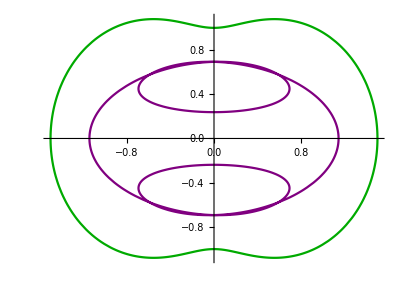

```mathematica
symmedianLocus[1.5,2π]
```

```mathematica
Clear@incenterLocus;
incenterLocus[a_,tmax_,ps_:("inc"/.ptClrs)]:=Module[{orbit,normals,sides},
Quiet@ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@baricenterLocus;
baricenterLocus[a_,tmax_,ps_:("bar"/.ptClrs)]:=Module[{orbit,normals,sides},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
(*getCentroid[orbit,triLengths@orbit]*)
getBaricenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@orthocenterLocus;
orthocenterLocus[a_,tmax_,ps_:("ort"/.ptClrs)]:=Module[{orbit,normals,sides},
Quiet@ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getOrthocenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@circumcenterLocus;
circumcenterLocus[a_,tmax_,ps_:("cir"/.ptClrs)]:=Module[{orbit,normals,sides},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getCircumcenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@ninepointcenterLocus;
ninepointcenterLocus[a_,tmax_,ps_:("npc"/.ptClrs)]:=Module[{orbit,normals,sides},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getNinepointcenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@excenterLocus;
excenterLocus[a_,tmax_,ps_:("exc"/.ptClrs)]:=Module[{orbit,normals,sides},
Quiet@ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getExcenters[orbit,normals][[1]],
{t,0,tmax},PlotStyle->ps]
];
```

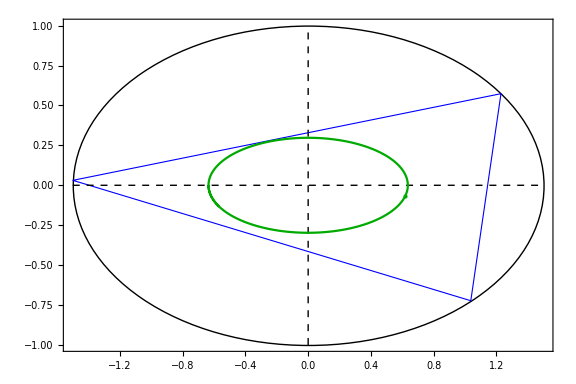

```mathematica
Module[{a=1.5,o,n,s,tDeg=35.,gr,inc},
{o,n,s}=orbitNormals[a,toRad@tDeg];
inc=getIncenterTrilin[o,s];
gr=Graphics[{FaceForm@None,
{EdgeForm@{Thick,Blue},Polygon@o,EdgeForm@{Thick,Darker@Green,Dashed}},
{PointSize@Large,Darker@Green,Point@inc},
{Dashed,Black,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}}}];
Show[{plotEll[a,{Thick,Black}],gr,incenterLocus[a,π/1.2,Darker@Green]},Frame->True,PlotRange->All,ImageSize->Large]]
```

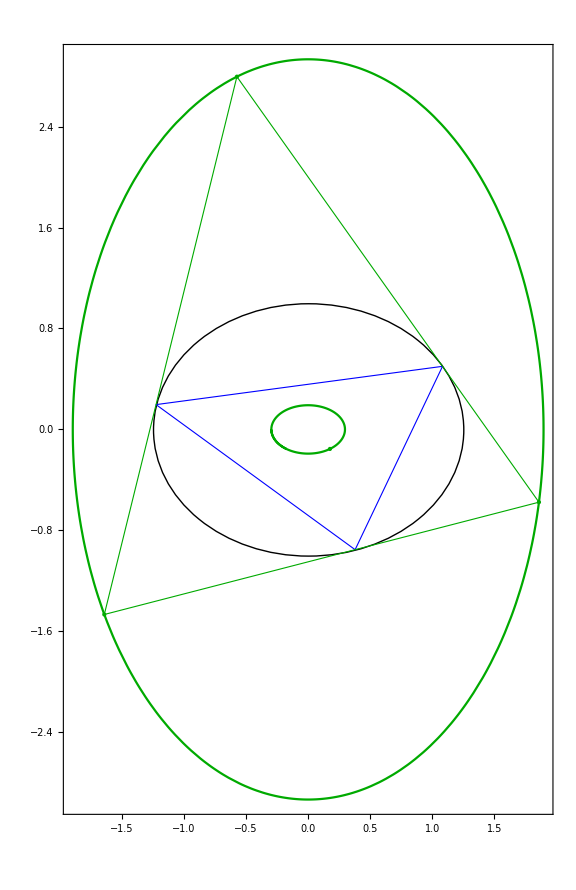

```mathematica
Module[{a=1.25,o,n,s,tDeg=30.,gr,exc,inc},
{o,n,s}=orbitNormals[a,toRad@tDeg];
inc=getIncenterTrilin[o,s];
exc=excentralTriangle[o,s];
gr=Graphics[{FaceForm@None,EdgeForm@{Thick,Blue},Polygon@o,EdgeForm@{Thick,Darker@Green,Dashed},Polygon@exc,PointSize@Large,Darker@Green,Point@exc,Point@inc}];
Show[{plotEll[a,{Thick,Black}],gr,incenterLocus[a,π/1.2,Darker@Green],excenterLocus[a,2π,Darker@Green]},Frame->True,PlotRange->All,ImageSize->Large]]
```

```mathematica
Clear@feuerbachcenterLocus;
feuerbachcenterLocus[a_,tmax_,ps_:("feu"/.ptClrs)]:=Module[{orbit,normals,sides,npc,inc,inradius,feu},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
npc=getNinepointcenter@@orbit;
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
inradius=inRadius0[inc,orbit[[1]],orbit[[2]]];
getFeuerbachpoint[npc,inc,inradius],
{t,0,tmax},PlotStyle->ps]
];
```

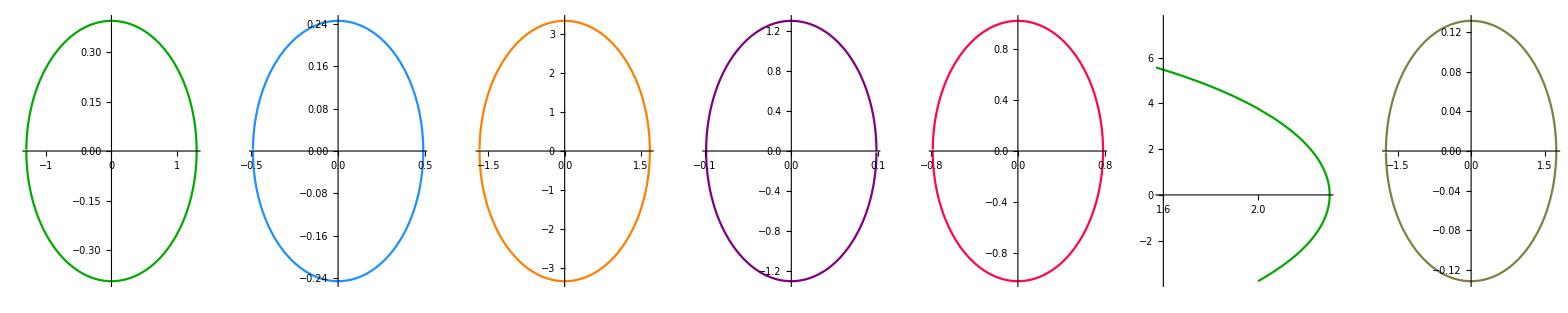

```mathematica
GraphicsRow[{
incenterLocus[2,π/1.2]//Quiet,
baricenterLocus[2,π/1.2]//Quiet,
orthocenterLocus[2,π/1.2]//Quiet,
circumcenterLocus[2,π/1.2]//Quiet,
ninepointcenterLocus[2,π/1.2]//Quiet,
excenterLocus[2,π]//Quiet,
feuerbachcenterLocus[2,π/1.2]//Quiet}
]
```

```mathematica
Clear@exFeuerbachcenterLocus;
exFeuerbachcenterLocus[a_,tmax_,ps_:("feu"/.ptClrs)]:=Module[{orbit,normals,sides,npc,exc,excCircleData},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
exc=getExcenters[orbit,normals];(*12,23,31*)
npc=getNinepointcenter@@orbit;
excCircleData=getExcircleData[orbit,exc,npc];
("feus"/.excCircleData)[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@intouchLocus;
intouchLocus[a_,tmax_,ps_:("exc"/.ptClrs)]:=Module[{orbit,normals,sides,tps},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
tps=getTouchPts[orbit,normals];
tps[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

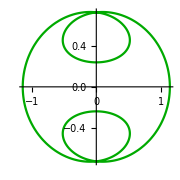

```mathematica
Show[intouchLocus[1.5,2π]//Quiet,ImageSize->Small]
```

```mathematica
Clear@getFeuLoci;getFeuLoci[a_,showExFeu_:False]:=Show[{
plotEll[a],
feuerbachcenterLocus[a,π/1.2]//Quiet,
If[showExFeu,exFeuerbachcenterLocus[a,2π]//Quiet,{}]}];
```

```mathematica
Clear@getDashedFeuLoci;
getDashedFeuLoci[a_]:=feuerbachcenterLocus[a,π/1.2,{Dashed,"feu"/.ptClrs}]//Quiet
```

```mathematica
Clear@getAntiComplementaryVertexLocus;
getAntiComplementaryVertexLocus[a_,tmax_:2π,ps_:{Dashed,Blue}]:=Module[{orbit,normals,sides,act},
Quiet@ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
act=anticomplementaryTriangle[orbit,RotateLeft@triLengths[orbit]];
act[[1]],
{t,0,tmax},PlotStyle->ps]];
```

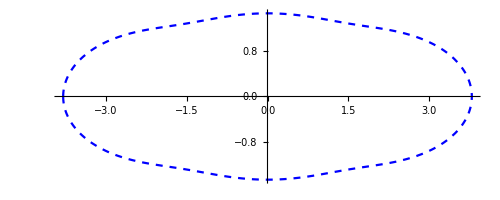

```mathematica
getAntiComplementaryVertexLocus[1.5]
```

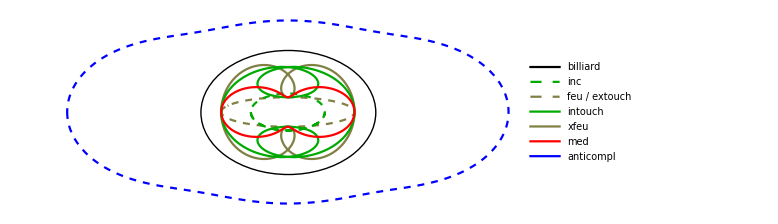

```mathematica
Module[{a=1.5,orbitData,lgt=.2},
orbitData=getOrbitData[a,toRad[30.]];
Legended[Show[{
(*drawOrbit[orbitData,lgt],*)
plotEll[a],
feuerbachcenterLocus[a,π/1.2,{Dashed,"feu"/.ptClrs}],
exFeuerbachcenterLocus[a,2π],
intouchLocus[a,2π],
incenterLocus[a,π,{Dashed,"exc"/.ptClrs}],
medianLocus[a,2π],
getAntiComplementaryVertexLocus[a]
}, PlotRange->All,ImageSize->Large],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell","inc","feu","inc","feu","med","anticompl"},
{{},Dashed,Dashed,{},{},{},{}}}],
{"billiard","inc","feu / extouch","intouch","xfeu","med","anticompl"}]]]//Quiet
```

```mathematica
nonEllipticPlot=Module[{a=1.5,orbitData,lgt=.2},
orbitData=getOrbitData[a,toRad[30.]];
Legended[Show[{
(*drawOrbit[orbitData,lgt],*)
plotEll[a,{Thick,Black}],
feuerbachcenterLocus[a,π/1.2,{"bar"/.ptClrs}],
feuerbachcenterLocus[a,π/1.2,{"bar"/.ptClrs}],
exFeuerbachcenterLocus[a,2π,"sym"/.ptClrs],
intouchLocus[a,2π],
medianLocus[a,2π]
}, PlotRange->All,ImageSize->Large],
LineLegend[MapThread[
Directive[{Thickness@.0125,#2,#1/.ptClrs}]&,
{{"ell","bar","bar","inc","sym","med"},
{{},{},{},{},{},{}}}],
Style[#,20]&/@{"Billiard","Feuerbach Point","Extouch Triangle","Intouch Triangle","Feuerbach Triangle","Medial Triangle"}]]]//Quiet;
```

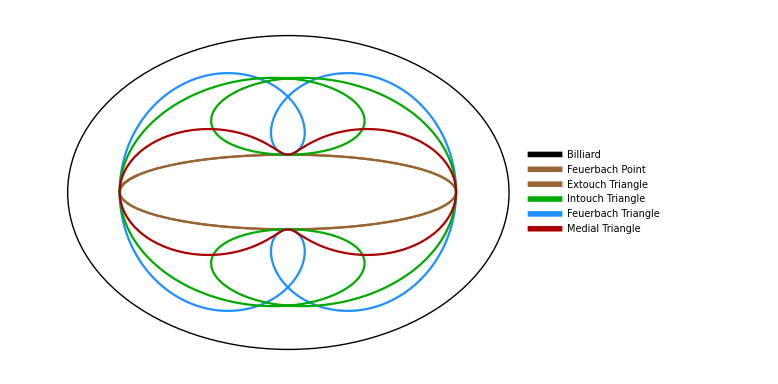

```mathematica
nonEllipticPlot
```

```mathematica
Export["0040_non_elliptic.pdf",nonEllipticPlot]
```

0040_non_elliptic.pdf

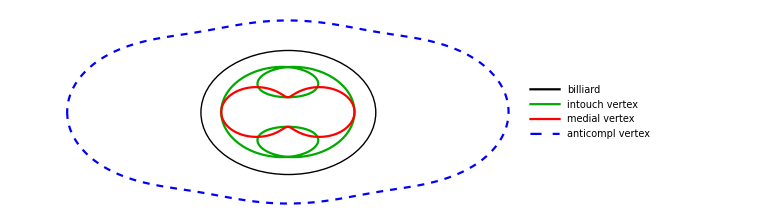

```mathematica
Module[{a=1.5,orbitData,lgt=.2},
orbitData=getOrbitData[a,toRad[30.]];
Legended[Show[{
(*drawOrbit[orbitData,lgt],*)
plotEll[a],
intouchLocus[a,2π],
medianLocus[a,2π,"med"/.ptClrs],
getAntiComplementaryVertexLocus[a]
}, PlotRange->All,ImageSize->Large],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell","inc","med","anticompl"},
{{},{},{},Dashed}}],
{"billiard","intouch vertex","medial vertex","anticompl vertex"}]]]//Quiet
```

#### The locus of the Outer Napoleon Point is not particularly interesting

```mathematica
Clear@outerNapoleonLocus;
outerNapoleonLocus[a_,tmax_,ps_:("nap"/.ptClrs)]:=Module[{orbit,normals,sides,nap},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
nap=outerNapoleonTriangle[orbit,sides];
nap[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

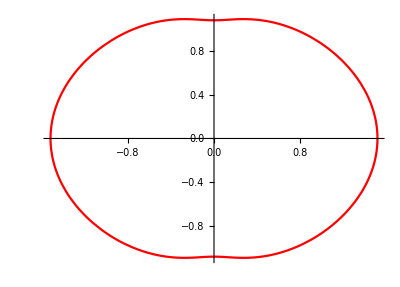

```mathematica
outerNapoleonLocus[1.5,2π]//Quiet
```

#### Path of First Morley Center Just outside Incenter' s

```mathematica
Clear@morleyIncenterLocus;
morleyIncenterLocus[a_,tmax_]:=Module[{orbit,normals,sides,mor1,mor2,mor3,inc},
ListLinePlot[Transpose@Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
mor1=getFirstMorleyTrilin[orbit,sides];
mor2=getSecondMorleyTrilin[orbit,sides];
mor3=getThirdMorleyTrilin[orbit,sides];
inc=getIncenterTrilin[orbit,sides];
{inc,mor1,mor2,mor3},
{t,0,tmax,tmax/100}],PlotStyle->{Darker@Green,Automatic,Automatic,Automatic},
PlotLegends->{"inc","morley 1","morley 2","morley 3"},ImageSize->Large]
];
```

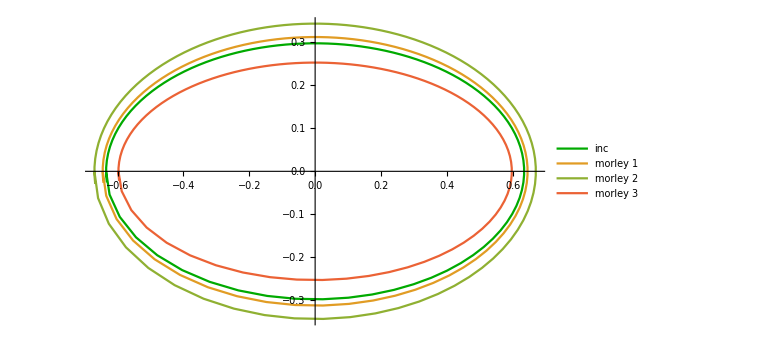

```mathematica
Quiet@morleyIncenterLocus[1.5,π/1.27]
```

```mathematica
Clear@orthicIncenterLocus;
orthicIncenterLocus[a_,tmax_,ps_:("inc"/.ptClrs)]:=Module[{orbit,normals,sides,feet,ortInc,ortSides},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
feet=getAltBases@@orbit;
ortSides=RotateLeft[triLengths@feet];
ortInc=getIncenterTrilin[feet,ortSides];
ortInc,
{t,0,tmax},PlotStyle->ps]
];
```

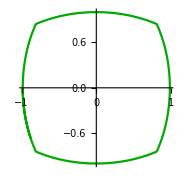

```mathematica
Show[orthicIncenterLocus[1.5,π/1.2]//Quiet,ImageSize->Small]
```

```mathematica
(* using anticomplementary triangle, but needs higher frequency *)
Clear@orthicIntouchTriangleIncenterLocus;
orthicIntouchTriangleIncenterLocus[a_,tmax_,ps_:Red]:=Module[{orbit,normals,sides,orthic},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"intouchAnticomplOrtInc"/.orthic,
{t,0,tmax},PlotStyle->ps]
];
```

#### Shows orthic' s orthocenter (dashed) too

```mathematica
getOrthicIncOrt[a_,t_]:=Module[{orbit,normals,sides,orthic,ort,inc},
{orbit,normals,sides}=orbitNormals[a,t];
orthic=getOrthicData@orbit;
inc="orthicInc"/.orthic;
ort="ort"/.orthic;
{inc,ort}];
```

```mathematica
Clear@orthicsOrthicIncenterLocus2;
orthicsOrthicIncenterLocus2[a_,tmax_:π/1.2,ps_:Blue]:=
ParametricPlot[
Evaluate@List@@getOrthicIncOrt[a,t],{t,0,tmax},
PlotStyle->({ps,{Dashed,ps}}),
PlotRange->All];
```

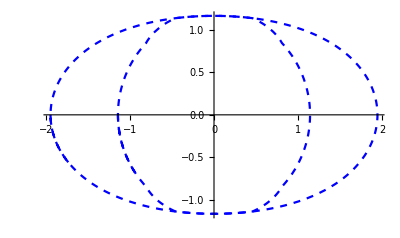

```mathematica
orthicsOrthicIncenterLocus2[1.5]//Quiet
```

```mathematica
Clear@orthicsOrthicIncenterLocus;
orthicsOrthicIncenterLocus[a_,tmaxInc_:π/1.2,tmaxOrt_:π/1.2,psOrthicOrt_:{Dashed,Blue},psOrtOrtInc_:Blue]:=Module[{orbit,normals,sides,orthic,ppInc,ppOrt,mr=8},
ppInc=ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"orthicInc"/.orthic,
{t,0,tmaxInc},PlotStyle->Directive[Thick,psOrtOrtInc],PerformanceGoal->"Quality",MaxRecursion->mr];
ppOrt=ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"ort"/.orthic,
{t,0,tmaxOrt},PlotStyle->psOrthicOrt,PerformanceGoal->"Quality",MaxRecursion->mr];
Show[{ppOrt,ppInc},PlotRange->All]
];
```

```mathematica
Clear@orthicsOrthicAnticomplIncenterLocus;
orthicsOrthicAnticomplIncenterLocus[a_,tmax_,ps_:Pink]:=Module[{orbit,normals,sides,orthic},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"orthicAnticomplInc"/.orthic,
{t,0,tmax},PlotStyle->ps]
];
```

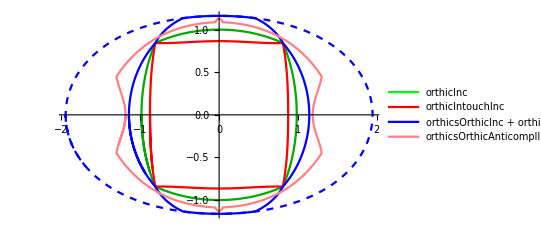

```mathematica
Legended[Show[{
orthicIncenterLocus[1.5,π/1.2],
orthicIntouchTriangleIncenterLocus[1.5,π/1.2],
orthicsOrthicIncenterLocus[1.5,π/1.2],
orthicsOrthicAnticomplIncenterLocus[1.5,π/1.2]},PlotRange->All
]//Quiet,
LineLegend[Directive[{Thickness@Large,#}]&/@{Green,Red,Blue,Pink},
{"orthicInc","orthicIntouchInc","orthicsOrthicInc + orthicOrthocenter (dashed)","orthicsOrthicAnticomplInc"}]]
```

## Study Symmedial Triangle

```mathematica
Clear@symmedialCircle;
symmedialCircle[tri_,sides_]:=Module[{center,radius,symTri,R},
R=getCircumradius@sides;
symTri=symmedialTriangle[tri,sides];
center=getCircumcenter@@symTri;
radius=magn[symTri[[1]]-center];
{center,radius}];
```

```mathematica
DynamicModule[{symLocus,a=1.5,ell,o,n,s,exc,symCirCtr,symCirRad,symCirCtrExc,symCirRadExc,gr},
symLocus=symmedianLocus[a,2π];
Manipulate[
{o,n,s}=orbitNormals[a,toRad@tDeg];
{symCirCtr,symCirRad}=symmedialCircle[o,s];
exc=excentralTriangle[o,s];
{symCirCtrExc,symCirRadExc}=symmedialCircle[exc,RotateLeft@triLengths@exc];
gr=Graphics[{PointSize@Medium,
{"sym"/.ptClrs,Circle[symCirCtr,symCirRad],Point@symCirCtr},
{"exc"/.ptClrs,Circle[symCirCtrExc,symCirRadExc],Point@symCirCtrExc}
}];
Show[{drawSimT[a,toRad@tDeg,drNotables->True],symLocus,gr},
PlotRange->{{-a,a},{-1.1,1.1}},
ImageSize->600],
{{tDeg,30},-180,180,1}]]
```

Set::shape: Lists {FE`symCirCtr$$48, FE`symCirRad$$48} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$48, FE`symCirRadExc$$48} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$48, FE`symCirRad$$48} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$48, FE`symCirRadExc$$48} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$48, FE`symCirRad$$48} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$48, FE`symCirRadExc$$48} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$48, FE`symCirRad$$48} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$48, FE`symCirRadExc$$48} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$48, FE`symCirRad$$48} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$48, FE`symCirRadExc$$48} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$48, FE`symCirRad$$48} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$48, FE`symCirRadExc$$48} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$52, FE`symCirRad$$52} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$52, FE`symCirRadExc$$52} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$43, FE`symCirRad$$43} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$43, FE`symCirRadExc$$43} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$43, FE`symCirRad$$43} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$43, FE`symCirRadExc$$43} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$516, FE`symCirRad$$516} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$516, FE`symCirRadExc$$516} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$192, FE`symCirRad$$192} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$192, FE`symCirRadExc$$192} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$192, FE`symCirRad$$192} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$192, FE`symCirRadExc$$192} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$2750, FE`symCirRad$$2750} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$2750, FE`symCirRadExc$$2750} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$80, FE`symCirRad$$80} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$80, FE`symCirRadExc$$80} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, 0.9773843811168246`, drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`symCirCtr$$80, FE`symCirRad$$80} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$80, FE`symCirRadExc$$80} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, 0.9773843811168246`, drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`symCirCtr$$101, FE`symCirRad$$101} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$101, FE`symCirRadExc$$101} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$60, FE`symCirRad$$60} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$60, FE`symCirRadExc$$60} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$60, FE`symCirRad$$60} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$60, FE`symCirRadExc$$60} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$60, FE`symCirRad$$60} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$60, FE`symCirRadExc$$60} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$60, FE`symCirRad$$60} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$60, FE`symCirRadExc$$60} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$73, FE`symCirRad$$73} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$73, FE`symCirRadExc$$73} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$73, FE`symCirRad$$73} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$73, FE`symCirRadExc$$73} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$64, FE`symCirRad$$64} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$64, FE`symCirRadExc$$64} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$41, FE`symCirRad$$41} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$41, FE`symCirRadExc$$41} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$41, FE`symCirRad$$41} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$41, FE`symCirRadExc$$41} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$74, FE`symCirRad$$74} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$74, FE`symCirRadExc$$74} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, 0.9773843811168246`, drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`symCirCtr$$74, FE`symCirRad$$74} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$74, FE`symCirRadExc$$74} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, 0.9773843811168246`, drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`symCirCtr$$80, FE`symCirRad$$80} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$80, FE`symCirRadExc$$80} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, 0.9773843811168246`, drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`symCirCtr$$300, FE`symCirRad$$300} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$300, FE`symCirRadExc$$300} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, 0.9773843811168246`, drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`o$$15, FE`n$$15, FE`s$$15} and orbitNormals[1.5, toRad[56]] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$15, FE`symCirRad$$15} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$15, FE`symCirRadExc$$15} and symmedialCircle[excentralTriangle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}], triLengths[excentralTriangle[« 1 », {« 1 »}]]] are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

ReplaceAll::reps: {ptClrs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, toRad[56], drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`symCirCtr$$62, FE`symCirRad$$62} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$62, FE`symCirRadExc$$62} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$62, FE`symCirRad$$62} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$62, FE`symCirRadExc$$62} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, 0.9773843811168246`, drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, 0.9773843811168246`, drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Show::gcomb: Could not combine the graphics objects in {drawSimT[1.5`, 0.9773843811168246`, drNotables → True], GraphicsBox[List[List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]], List[List[List[], List[], List[Directive[Skeleton[4]], LineBox[Skeleton[1]]]]]], List[Rule[PlotRange, All], Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$74, FE`symCirRad$$74} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$74, FE`symCirRadExc$$74} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$74, FE`symCirRad$$74} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$74, FE`symCirRadExc$$74} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$113, FE`symCirRad$$113} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$113, FE`symCirRadExc$$113} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$113, FE`symCirRad$$113} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$113, FE`symCirRadExc$$113} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$113, FE`symCirRad$$113} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$113, FE`symCirRadExc$$113} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$113, FE`symCirRad$$113} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$113, FE`symCirRadExc$$113} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$42, FE`symCirRad$$42} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$42, FE`symCirRadExc$$42} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$42, FE`symCirRad$$42} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$42, FE`symCirRadExc$$42} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$42, FE`symCirRad$$42} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$42, FE`symCirRadExc$$42} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$82, FE`symCirRad$$82} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$82, FE`symCirRadExc$$82} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$175, FE`symCirRad$$175} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$175, FE`symCirRadExc$$175} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$42, FE`symCirRad$$42} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$42, FE`symCirRadExc$$42} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$42, FE`symCirRad$$42} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$42, FE`symCirRadExc$$42} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$80, FE`symCirRad$$80} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$80, FE`symCirRadExc$$80} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$80, FE`symCirRad$$80} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$80, FE`symCirRadExc$$80} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$80, FE`symCirRad$$80} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$80, FE`symCirRadExc$$80} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$80, FE`symCirRad$$80} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$80, FE`symCirRadExc$$80} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$452, FE`symCirRad$$452} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$452, FE`symCirRadExc$$452} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$452, FE`symCirRad$$452} and symmedialCircle[{{0.838789, 0.829038}, {1.32189, -0.472627}, {-1.49554, -0.0770302}}, {2.84507, 2.50401, 1.38842}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$452, FE`symCirRadExc$$452} and symmedialCircle[{{-1.1007, -3.48408}, {-1.73466, 1.98624}, {1.96253, 0.323724}}, {4.05378, 4.887, 5.50694}] are not the same shape.

### Radii do not seem constant

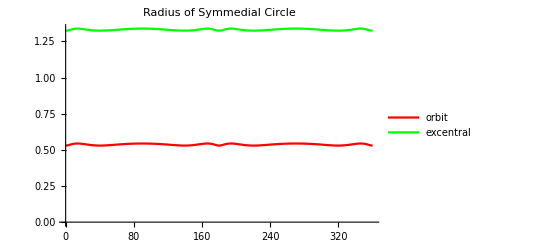

```mathematica
Module[{a=1.5,ell,o,n,s,exc,symCirCtr,symCirRad,symCirCtrExc,symCirRadExc},
ListLinePlot[
Transpose@Table[{o,n,s}=orbitNormals[a,toRad@tDeg];
{symCirCtr,symCirRad}=symmedialCircle[o,s];
exc=excentralTriangle[o,s];
{symCirCtrExc,symCirRadExc}=symmedialCircle[exc,RotateLeft@triLengths@exc];
{{tDeg,symCirRad},{tDeg,symCirRadExc}},{tDeg,0,360,1}],PlotStyle->{Red,Green},PlotLegends->{"orbit","excentral"},PlotLabel->"Radius of Symmedial Circle"]]
```

#### And their Ratio is not seem constant

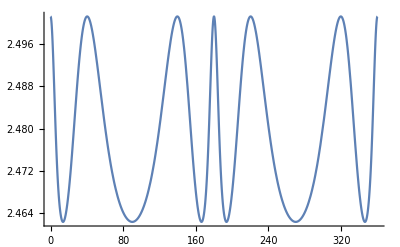

```mathematica
Module[{a=1.5,ell,o,n,s,exc,symCirCtr,symCirRad,symCirCtrExc,symCirRadExc},
Plot[
{o,n,s}=orbitNormals[a,toRad@tDeg];
{symCirCtr,symCirRad}=symmedialCircle[o,s];
exc=excentralTriangle[o,s];
{symCirCtrExc,symCirRadExc}=symmedialCircle[exc,RotateLeft@triLengths@exc];
symCirRadExc/symCirRad,{tDeg,0,360}]]
```

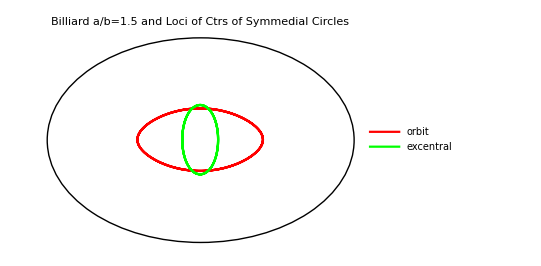

```mathematica
Module[{a=1.5,ell,o,n,s,exc,symCirCtr,symCirRad,symCirCtrExc,symCirRadExc,llp},
ell=plotEll[a,{Thick,Black}];
llp=ListLinePlot[
Transpose@Table[{o,n,s}=orbitNormals[a,toRad@tDeg];
{symCirCtr,symCirRad}=symmedialCircle[o,s];
exc=excentralTriangle[o,s];
{symCirCtrExc,symCirRadExc}=symmedialCircle[exc,RotateLeft@triLengths@exc];
{symCirCtr,symCirCtrExc},{tDeg,0,360,1}],PlotStyle->{Red,Green},PlotLegends->{"orbit","excentral"}];
Show[{ell,llp},PlotLabel->"Billiard a/b=1.5 and Loci of Ctrs of Symmedial Circles"]]
```

## Precomp Loci

```mathematica
Clear@precompLoci;
precompLoci[a_]:=Module[{ell,tmax=π/1.2},
Show[{
incenterLocus[a,tmax]//Quiet,
baricenterLocus[a,tmax]//Quiet,
orthocenterLocus[a,tmax]//Quiet,
circumcenterLocus[a,tmax]//Quiet,
ninepointcenterLocus[a,tmax]//Quiet,
(* note excenters require full 2π *)
excenterLocus[a,2π]//Quiet,
feuerbachcenterLocus[a,tmax]//Quiet
}]];
```

```mathematica
precompLociBasic[a_]:=Module[{ell,tmax=π/1.2},
Show[{
incenterLocus[a,tmax]//Quiet,
baricenterLocus[a,tmax]//Quiet,
orthocenterLocus[a,tmax]//Quiet,
circumcenterLocus[a,tmax]//Quiet,
ninepointcenterLocus[a,tmax]//Quiet
}]];
```

```mathematica
precompLociNonEll[a_]:=Module[{ell,tmax=π/1.2},
Quiet@Show[{
exFeuerbachcenterLocus[a,2π],
intouchLocus[a,2π,{Dashed,"inc"/.ptClrs}],
medianLocus[a,2π,{Dashed,"npc"/.ptClrs}]
}]];
```

```mathematica
Show[precompLociNonEll[1.5],PlotRange->All]
```

-Graphics-

## Napoleon Summits and Loci

```mathematica
getOuterNapoleonInfoLow[orbit_,sides_]:=Module[{sqrt3ov2=.5Sqrt@3.,meds,naps,napGs,side,area,centroid,tri},
meds=getMedians@@orbit;
naps=MapThread[#1+#2sqrt3ov2 perp[norm@(#4-#3)]&,{meds,sides,RotateLeft@orbit,RotateRight@orbit}];
napGs=MapThread[#1+(#2-#1)/3&,{meds,naps}];
side=magn[napGs[[2]]-napGs[[1]]];
area=.5sqrt3ov2*(side^2);
centroid=Total[napGs]/3;
<|"summits"->naps,"tri"->napGs,"side"->side,"area"->area,"meds"->meds,"centroid"->centroid,"orbit"->orbit|>];
```

```mathematica
Clear@getOuterNapoleonSummits;
getOuterNapoleonSummits[a_,t_]:=Module[{sqrt3ov2=.5Sqrt@3.,o,n,s},
{o,n,s}=orbitNormals[a,t];
getOuterNapoleonInfoLow[o,s]];
```

```mathematica
Clear@getOuterNapoleonExcSummits;
getOuterNapoleonExcSummits[a_,t_]:=Module[{sqrt3ov2=.5Sqrt@3.,o,n,s,exc,excSides},
{o,n,s}=orbitNormals[a,t];
exc=excentralTriangle[o,s];
excSides=RotateLeft@triLengths@exc;
Join[getOuterNapoleonInfoLow[exc,excSides],<|"baseOrbit"->o,"baseSides"->s|>]];
```

```mathematica
Clear@makeOneNapoleonFrame;
makeOneNapoleonFrame[a_,ell_,napPts_,tDeg_]:=Module[{ons,gr,aequi,lab},
ons=getOuterNapoleonSummits[a,toRad@tDeg];
gr=Graphics[{FaceForm@None,PointSize@Large,Point@{0,0},ellLabelPoints[a,ons["orbit"],"P",14,.15],
{EdgeForm@{Blue,Thick},Polygon@ons["orbit"],Blue,Point@ons["meds"]},{Darker@Green,MapThread[{{Dashed,Line@{#1,#2}},{Thick,Line@{#3,#2},Line@{#4,#2}},Point@#2}&,{ons["meds"],ons["summits"],RotateLeft@ons["orbit"],RotateRight@ons["orbit"]}]},
{EdgeForm@{Thick,Purple},FaceForm@{Purple,Opacity@.1},Polygon@ons["tri"],Purple,Point@ons["tri"],Point@ons["centroid"]},
(* loci *)
{{EdgeForm@{Thick,Dashed,Blue},Polygon@(First[#@"meds"]&/@napPts)},
{EdgeForm@{Thick,Dashed,Darker@Green},Polygon@(First[#@"summits"]&/@napPts)},
{EdgeForm@{Thick,Dashed,Purple},Polygon@(First[#@"tri"]&/@napPts)},
{EdgeForm@{Purple},Polygon@(#["centroid"]&/@napPts)}}}];
lab="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°, L_equi="<>nfn[ons["side"],3]<>", A_equi="<>nfn[ons["area"],3];
Show[{gr,ell},PlotRange->{{-3,3},{-3,3}},PlotLabel->Style[lab,{20,Black}],ImageSize->Large,Frame->True]];
```

```mathematica
DynamicModule[{ell,ons,gr,napPts},
Manipulate[
ell=plotEll[a,{Black,Thick}];
napPts=Table[getOuterNapoleonSummits[a,toRad@tDeg0],{tDeg0,0,359,1}];
Dynamic@makeOneNapoleonFrame[a,ell,napPts,tDeg],
{{a,1.5},1.01,3,.1,Appearance->"Open"},
{{tDeg,30},-360,360,1,Appearance->"Open"},SaveDefinitions->True]]
```

```mathematica
Clear@makeOneNapoleonFrameExc;
makeOneNapoleonFrameExc[a_,ell_,napPts_,tDeg_]:=Module[{ons,gr,aequi,lab,o},
ons=getOuterNapoleonExcSummits[a,toRad@tDeg];
o=orbitNormals[a,toRad@tDeg][[1]];
gr=Graphics[{FaceForm@None,PointSize@Large,Point@{0,0},ellLabelPoints[a,ons["orbit"],"P",14,.15],
{EdgeForm@{Black},Polygon@o},
{EdgeForm@{Blue,Thick},Polygon@ons["orbit"],Blue,Point@ons["meds"]},{Darker@Green,MapThread[{{Dashed,Line@{#1,#2}},{Thick,Line@{#3,#2},Line@{#4,#2}},Point@#2}&,{ons["meds"],ons["summits"],RotateLeft@ons["orbit"],RotateRight@ons["orbit"]}]},
{EdgeForm@{Thick,Purple},FaceForm@{Purple,Opacity@.1},Polygon@ons["tri"],Purple,Point@ons["tri"],Point@ons["centroid"]},
(* loci *)
{{EdgeForm@{Thick,Dashed,Blue},Polygon@(First[#@"meds"]&/@napPts)},
{EdgeForm@{Thick,Dashed,Darker@Green},Polygon@(First[#@"summits"]&/@napPts)},
{EdgeForm@{Thick,Dashed,Purple},Polygon@(First[#@"tri"]&/@napPts)},
{EdgeForm@{Purple},Polygon@(#["centroid"]&/@napPts)}}}];
lab="a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>"°, L_equi="<>nfn[ons["side"],3]<>", A_equi="<>nfn[ons["area"],3];
Show[{gr,ell},PlotRange->{{-8,8},{-5,5}},PlotLabel->Style[lab,{20,Black}],ImageSize->Large,Frame->True]];
```

```mathematica
DynamicModule[{ell,ons,gr,napPts},
Manipulate[
ell=plotEll[a,{Black,Thick}];
napPts=Table[getOuterNapoleonExcSummits[a,toRad@tDeg0],{tDeg0,0,359,1}];
Dynamic@makeOneNapoleonFrameExc[a,ell,napPts,tDeg],
{{a,1.5},1.01,3,.1,Appearance->"Open"},
{{tDeg,30},-360,360,1,Appearance->"Open"},SaveDefinitions->True]]
```

```mathematica
(*DeleteFile[napApp];*)
```

```mathematica
(*napApp=CloudDeploy[%,"napoleon summits v1",Permissions->"Public"]*)
```

#### Outer locus is *not* elliptic

```mathematica
Module[{a=2.,napPts,outerEllPars,centroidEllPars,summitLocus,centroidLocus},
napPts=Table[getOuterNapoleonSummits[a,toRad@tDeg0],{tDeg0,0,359,1}];
summitLocus=First[#@"summits"]&/@napPts;
centroidLocus=#["centroid"]&/@napPts;
centroidEllPars=findEllParams[a,1,centroidLocus,"centroid"];
outerEllPars=findEllParams[a,1,summitLocus,"outer"];
<|"centroidEllErr"->centroidEllPars["err"],"outerEllErr"->outerEllPars["err"]|>]
```

<|centroidEllErr→1.37509×10^-13,outerEllErr→0.268304|>

## Loci w/ Convex Combinations

```mathematica
convexPts[p_,q_,t_]:=(1-t)p+t q;
```

#### Convex Comb of edges

```mathematica
Clear@convVtx;
convVtx[a_,u_,tDeg_]:=Module[{lgt=.2,o1,ps,gr,o,n,s,ell,locus},
ell=plotEll[a];
o1=orbitNormals[a,toRad@tDeg][[1]];
ps=MapThread[convexPts[#1,#2,u]&,{o1,RotateLeft@o1}];
locus=Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
convexPts[o[[1]],o[[2]],u],
{t,0,2π},PlotStyle->Red];
gr=Graphics[{FaceForm@None,PointSize@Large,Blue,Point@ps,EdgeForm@{Thick,Blue},Polygon@o1}];
Show[{ell,gr,locus}]];
```

```mathematica
Manipulate[convVtx[1.5,u,tDeg],{{u,.5},0,1,.01},{{tDeg,120},-180,180,1}]
```

#### trilineares: f(a,b,c) = 1/a. f(a,b,c) = f(a,c,b) f(a,b,c) = sin(A)*cos(B)*cos(C) tril = [ f(a,b,c) : f(b,c,a) : f(c,a,b) ] BARICENTRO : 1/a , 1/b, 1/c

```mathematica
Clear@convCevian;
convCevian[a_,p_,tDeg_]:=Module[{lgt=.2,o1,s1,cevs1,peds1,gr,cevs,peds,o,n,s,ell,locus,locusPedal,trils,trils1},
ell=plotEll[a,{Thick,Black}];
{o1,s1}=Part[orbitNormals[a,toRad@tDeg],{1,3}];
trils1=trilinearCoords[o1,p];
cevs1=cevianTriangle[o1,s1,trils1];
peds1=pedalTriangle[o1,s1,trils1];
(*locus=Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
trils=trilinearCoords[o,p];
cevs=cevianTriangle[o,s,trils];
cevs[[1]],
{t,0,2π},PlotStyle->Red];
locusPedal=Quiet@ParametricPlot[
{o,n,s}=orbitNormals[a,t];
trils=trilinearCoords[o,p];
peds=pedalTriangle[o,s,trils];
peds[[1]],
{t,0,2π},PlotStyle->Darker@Green];*)
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@o1},
{Brown,Point@getBarycenterTrilin[o1,s1]},
{Lighter@Red,EdgeForm@Lighter@Red,Polygon@cevs1,Dashed,Point@cevs1,MapThread[Line@{#1,#2}&,{o1,cevs1}]},
{Green,EdgeForm@Green,Polygon@peds1,Dashed,Point@peds1,Line@{p,#}&/@peds1}}];
Show[{ell,gr(*,locus,locusPedal*)},ImageSize->Large]];
```

#### Locating point and calculate its trilinears with respect to a triangle (blue below) this won' t work because trilinears are *functions* of sidelengths or angles, e.g.: f(a,b,c)= k + a1 a + a2 a^2 + a3 a^3 +b1b + b2 b^2 + b3 b^3 + c1 c + c2 c^2 + c3 c^3.

```mathematica
Manipulate[convCevian[1.5,p,30],{{p,{0,0}},Locator}]
```

#### Incenter with First Intouch Point

```mathematica
Clear@getConvexIntouchLocus;
getConvexIntouchLocus[a_,tmax_,s_,(* 0 = incenter, 1 = intouch *)
ps_:("inc"/.ptClrs)]:=Module[{orbit,normals,sides,tps,inc},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
tps=getTouchPts[orbit,normals];
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
convexPts[inc,tps[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convIncTps[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
incenterLocus[a,π,{"exc"/.ptClrs}],
getConvexIntouchLocus[a,2π,s,{Dashed,"inc"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"inc","inc"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"incenter","incenter-to-pedal"}]]]//Quiet
```

```mathematica
Show[convIncTps[1.75,.5],ImageSize->Small]
```

-Graphics-

#### Baricenter with First Median

```mathematica
Clear@getConvexMedianLocus;
getConvexMedianLocus[a_,tmax_,s_,(* 0 = baricenter, 1 = median *)
ps_:("bar"/.ptClrs)]:=Module[{orbit,normals,sides,meds,bar},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
meds=getMedians@@orbit;
bar=getBaricenter@@orbit;
convexPts[bar,meds[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convBariMed[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
baricenterLocus[a,π/1.2,{"bar"/.ptClrs}],
getConvexMedianLocus[a,2π,s,{Dashed,"bar"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"bar","bar"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"baricenter","baricenter-to-median"}]]]//Quiet
```

```mathematica
Show[convBariMed[1.5,0.85],ImageSize->800,PlotRange->{{-1.5,1.5},{-.5,.5}}]
```

-Graphics-

```mathematica
Clear@combineConvexBarInc;combineConvexBarInc[a_,s_,imgSize_:800]:=Row[{convBariMed[a,s],convIncTps[a,s]}];
```

```mathematica
combineConvexBarInc[1.5,.5,800]
```

-Graphics--Graphics-

#### First Excenter with First Extouch

```mathematica
Clear@getConvexExtouchLocus;
getConvexExtouchLocus[a_,tmax_,s_,(* 0 = excenter, 1 = extouch *)
ps_:("exc"/.ptClrs)]:=Module[{orbit,normals,sides,exc,tps},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
(*&&&*)
exc=getExcenters[orbit,normals];
tps=getExtouchPoints[orbit,exc];
convexPts[exc[[1]],tps[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convExcTps[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
excenterLocus[a,2π,{"exc"/.ptClrs}],
getConvexExtouchLocus[a,2π,s,{Dashed,"exc"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,PlotRange->All,
PlotLabel->Style["s = "<>nf[s],20]],
Placed[LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"exc","exc"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"excenter","exc-to-extouch"}],Below]]]//Quiet
```

```mathematica
convExcTps[1.5,1]
```

-Graphics-

#### Orthocenter to First Foot

```mathematica
Clear@getConvexOrtLocus;
getConvexOrtLocus[a_,tmax_,s_,(* 0 = orthocenter, 1 = foot *)
ps_:("ort"/.ptClrs)]:=Module[{orbit,normals,sides,ort,feet},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
ort=getOrthocenter@@orbit;
feet=getAltBases@@orbit;
convexPts[ort,feet[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convOrtFoot[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
orthocenterLocus[a,π/1.2,{"ort"/.ptClrs}],
getConvexOrtLocus[a,2π,s,{Dashed,"ort"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,PlotRange->All,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"ort","ort"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"orthocenter","ort-to-foot"}]]]//Quiet
```

```mathematica
convOrtFoot[1.5,1]
```

-Graphics-

#### Circumcenter to First Vertex

```mathematica
Clear@getConvexCirLocus;
getConvexCirLocus[a_,tmax_,s_,(* 0 = circumcenter, 1 = vertex *)
ps_:("cir"/.ptClrs)]:=Module[{orbit,normals,sides,cir},
ParametricPlot[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
(*&&&*)
cir=getCircumcenter@@orbit;
convexPts[cir,orbit[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convCirVtx[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
circumcenterLocus[a,π/1.2,{"cir"/.ptClrs}],
getConvexCirLocus[a,2π,s,{Dashed,"cir"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,PlotRange->All,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"cir","cir"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"circumcenter","circ-to-vertex"}]]]//Quiet
```

```mathematica
convCirVtx[1.5,.585]
```

-Graphics-

```mathematica
Clear@combineConvexOrtCir;combineConvexOrtCir[a_,s_,imgSize_:800]:=
Grid[{{},
{convOrtFoot[a,s],convCirVtx[a,s]}}
];
```

```mathematica
combineConvexOrtCir[1.5,.5]
```

| 
-Graphics- | -Graphics-

## Miquel Point (on Extouchpoints) Locus

```mathematica
Clear@getMiquelPoint;
getMiquelPoint[a_,t_]:=Module[{o,n,s,ext,c1,r1,c2,r2,c3,r3,miquel1,miquel2,miquel,bevan},
{o,n,s}=orbitNormals[a,t];
bevan=getBevanTrilin[o,s];
ext=extouchTriangle[o,s];
c1=getCircumcenter[o[[1]],ext[[2]],ext[[3]]];r1=magn[c1-o[[1]]];
c2=getCircumcenter[o[[2]],ext[[3]],ext[[1]]];r2=magn[c2-o[[2]]];
c3=getCircumcenter[o[[3]],ext[[1]],ext[[2]]];r3=magn[c3-o[[3]]];
miquel1=circleInter[c1,r1,c2,r2];
miquel2=circleInter[c1,r1,c3,r3];
(* return the one common point of intersection *)
miquel=First@Intersection[miquel1,miquel2,SameTest->(negl@magn2[#1-#2]&)];
<|"o"->o,"ext"->ext,"cs"->{c1,c2,c3},"rs"->{r1,r2,r3},"bevan"->bevan,"miquel"->miquel|>];
```

```mathematica
Clear@getMiquelPointExc;
getMiquelPointExc[a_,t_]:=Module[{o,n,s,exc,c1,r1,c2,r2,c3,r3,miquel1,miquel2,miquel,inc},
{o,n,s}=orbitNormals[a,t];
inc=getIncenterTrilin[o,s];
exc=excentralTriangle[o,s];
c1=getCircumcenter[exc[[1]],o[[2]],o[[3]]];r1=magn[c1-exc[[1]]];
c2=getCircumcenter[exc[[2]],o[[3]],o[[1]]];r2=magn[c2-exc[[2]]];
c3=getCircumcenter[exc[[3]],o[[1]],o[[2]]];r3=magn[c3-exc[[3]]];
miquel1=circleInter[c1,r1,c2,r2];
miquel2=circleInter[c1,r1,c3,r3];
(* return the one common point of intersection *)
miquel=First@Intersection[miquel1,miquel2,SameTest->(negl@magn2[#1-#2]&)];
<|"o"->o,"exc"->exc,"inc"->inc,"cs"->{c1,c2,c3},"rs"->{r1,r2,r3},"miquel"->miquel|>];
```

```mathematica
Clear@miquelOfExtouchPoints;
miquelOfExtouchPoints[a_,t_,objs_]:=Module[{miquelData,gr},
miquelData=getMiquelPoint[a,t];
getNewCenters[];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@miquelData["o"],Blue,Point@miquelData["o"],ellLabelPoints[a,miquelData["o"],"P",16,.15]},
{(*EdgeForm@Darker@Green,Polygon@ext,*)Darker@Green,Point@miquelData["ext"],ellLabelPoints[a,miquelData["ext"],"P'",16,.15]},
{Red,MapThread[Circle[#1,#2]&,{miquelData["cs"],miquelData["rs"]}],Point@miquelData["miquel"]},
{Darker@Cyan,Point@miquelData["cs"],EdgeForm@{Thick,Darker@Cyan},Polygon@miquelData["cs"]},
{Purple,Thick,Circle[miquelData["bevan"],.05]}
}];
Show[{objs["ell"],objs["caustic"],gr,objs["locus"],objs["locusCtrs"]},PlotRange->{{-2,2},{-1.75,1.75}},Frame->True,ImageSize->Large]];
```

```mathematica
DynamicModule[{cachedObjs},
Manipulate[
cachedObjs=<|
"ell"->plotEll[a,{Black,Thick}],
"caustic"->(plotEllb[Sequence@@getTriCausticParams[a],{Thick,"feu"/.ptClrs}]),
"locusCtrs"->Quiet@ParametricPlot[getMiquelPoint[a,t]["cs"][[1]],{t,0,2π},PlotStyle->{Darker@Cyan,Dashed,Thick}],
(*"ortlocus"->orthocenterLocus[a,π/1.2],*)
"locus"->Quiet@ParametricPlot[getMiquelPoint[a,t]["miquel"],{t,0,π/1.2},PlotStyle->{Red,Dashed,Thick}]|>;
Dynamic@miquelOfExtouchPoints[a,toRad@tDeg,cachedObjs],
{{a,1.5},1.01,2,.01},
{{tDeg,30},-180,180,.1,Appearance->"Open"}]]
```

```mathematica
Clear@miquelOfExcentral;
miquelOfExcentral[a_,t_,objs_]:=Module[{miquelData,gr},
miquelData=getMiquelPointExc[a,t];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Thick,Blue},Polygon@miquelData["o"],Blue,Point@miquelData["o"],ellLabelPoints[a,miquelData["o"],"P",16,.15]},
{EdgeForm@{Thick,Darker@Green},Polygon@miquelData["exc"],Darker@Green,Point@miquelData["exc"],ellLabelPoints[a,miquelData["exc"],"P'",16,.15]},
{Red,MapThread[Circle[#1,#2]&,{miquelData["cs"],miquelData["rs"]}],Point@miquelData["miquel"],Darker@Cyan,Point@miquelData["cs"],EdgeForm@{Thick,Darker@Cyan},Polygon@miquelData["cs"]},
{Darker@Green,Thick,Circle[miquelData["inc"],.075]}
}];
Show[{objs["ell"],gr,objs["locus"],objs["locusCtrs"]},PlotRange->{{-2.5,2.5},{-3.75,3.75}},Frame->True,ImageSize->Large]];
```

```mathematica
DynamicModule[{cachedObjs},
Manipulate[
cachedObjs=<|
"ell"->plotEll[a,{Black,Thick}],
"locusCtrs"->Quiet@ParametricPlot[getMiquelPointExc[a,t]["cs"][[1]],{t,0,2π},PlotStyle->{Darker@Cyan,Dashed,Thick}],
(*"ortlocus"->orthocenterLocus[a,π/1.2],*)
"locus"->Quiet@ParametricPlot[getMiquelPointExc[a,t]["miquel"],{t,0,π/1.305},PlotStyle->{Red,Dashed,Thick}]|>;
Dynamic@miquelOfExcentral[a,toRad@tDeg,cachedObjs],
{{a,1.5},1.01,2,.01},
{{tDeg,30},-180,180,.1,Appearance->"Open"}]]
```

## Circumbilliard II (using linear algebra)

```mathematica
ellExtremum[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_},t_]=Module[{xt,yt},
xt=mx+t vx;
yt=my+t vy;
Collect[1+c1 xt+c2 yt+c3 xt yt+c4 xt^2+c5 yt^2,t]]
```

1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2+t (c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy)+t^2 (c4 vx^2+c3 vx vy+c5 vy^2)

```mathematica
(* by symmetry, b=0 of the quadratic*)
Clear@ellExtremumSym;
ellExtremumSym[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_}]:=Module[{a,c,d,sqrtd,sol},
a=c4 vx^2+c3 vx vy+c5 vy^2;
(* b=c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy; *)
c=1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2;
(*(-b + sqrt(b2-4ac)/(2a)) => sqrt(-4ac)/(2a) => sqrt(-ac)/a*)  
sol=Sqrt[-c/a];(*Sqrt[-a*c]/a;*)(* sqrt(-a)*sqrt(c)/a => sqrt(c/a) *)
{sol,-sol}];
```

```mathematica
(* grad = { c1 + c3 y + 2 c4 x, c2 + c3 x + 2 c5 y *)
circumTangent[{c1_,c2_,c3_,c4_,c5_},{x_,y_}]:=Module[{grad,tang},
grad={c1+c3 y+2c4 x,c2+c3 x+2c5 y};
tang=perp@grad;
tang];
```

```mathematica
Clear@getCircumAny;
getCircumAny[orbit_,ctr_]:=Module[{mtx123,mtx45,mtx,rhs,ls,hess,vals,vects,lengths,lgt1,lgt2,vertices,orbitTangents,area},
(* c1 x + c2 y + c3 x y + c4 x^2 + c5 y^2 == -1 *)
(* grad = { c1 + c3 y + 2 c4 x, c2 + c3 x + 2 c5 y *)
mtx123={#[[1]],#[[2]],#[[1]]*#[[2]],#[[1]]^2,#[[2]]^2}&/@orbit;
mtx45={
{1,0,ctr[[2]],2ctr[[1]],0},
{0,1,ctr[[1]],0,2ctr[[2]]}};
mtx=Join[mtx123,mtx45];
rhs={-1,-1,-1,0,0};
ls=LinearSolve[mtx,rhs];
hess={{2ls[[4]],ls[[3]]},{ls[[3]],2ls[[5]]}};
{vals,vects}=Eigensystem@hess;
lgt1=Abs[First@ellExtremumSym[ctr,vects[[1]],ls]];
lgt2=lgt1*Sqrt[vals[[1]]/vals[[2]]];
lengths={lgt1,lgt2};
orbitTangents=circumTangent[ls,#]&/@orbit;
vertices=MapThread[(ctr+#1*#2)&,{lengths,vects}];
area=π*lengths[[1]]*lengths[[2]];
<|"ctr"->ctr,"coeffs"->Chop@ls,"vals"->Chop@vals,"axes"->Chop@vects,"lengths"->lengths,"vertices"->Chop@vertices,
"orbit"->orbit,"orbitTangents"->orbitTangents,"area"->area|>];
```

```mathematica
-Graphics-
-Graphics-
```

```mathematica
Clear@getEll5ctr;
getEll5ctr[ctrs5_]:=Module[{mtx,rhs,ls,discr,x0,y0},
(* A x^2 + B x y + C y^2 + D x + E y == -1 *)
mtx={#[[1]]^2,#[[1]]*#[[2]],#[[2]]^2,#[[1]],#[[2]]}&/@ctrs5;
rhs={-1,-1,-1,-1,-1};
ls=LinearSolve[mtx,rhs];
discr=ls[[2]]^2-4ls[[1]]ls[[3]];
x0=(2*ls[[3]]*ls[[4]]-ls[[2]]ls[[5]])/discr;
y0=(2*ls[[1]]*ls[[5]]-ls[[2]]ls[[4]])/discr;
{x0,y0}];
```

```mathematica
Module[{a=1.5,ps},
ps=Table[N@{a Cos[t]+5,Sin[t]+7},{t,0,2π,2π/7}];
getEll5ctr[Take[ps,5]]]
```

{5.,7.}

## Circum

```mathematica
Clear@getCircumMit;
getCircumMit[orbit_]:=Module[{ctr},
ctr=getMittenTrilin[orbit,RotateLeft@triLengths@orbit];
getCircumAny[orbit,ctr]];
(* Steiner Circumellipse *)
Clear@getCircumBar;getCircumBar[orbit_]:=getCircumAny[orbit,getBaricenter@@orbit];
```

```mathematica
getCircumMit[orbitNormals[1.5,π/3.][[1]]]
```

<|ctr→{0.,-6.24567×10^-16},coeffs→{0,0,0,-0.444444,-1.},vals→{-2.,-0.888889},axes→{{0,1.},{-1.,0}},lengths→{1.,1.5},vertices→{{0,1.},{-1.5,0}},orbit→{{0.75,0.866025},{1.34925,-0.436921},{-1.49317,-0.0953041}},orbitTangents→{{1.73205,-0.666667},{-0.873842,-1.19933},{-0.190608,1.32726}},area→4.71239|>

```mathematica
Clear@drawCircumAnyLow;
Options@drawCircumAnyLow={ctrLab->"*",drTri->False,drOrbitTangents->False,ps->Black,drVertices->False,drLgl->.2};
drawCircumAnyLow[cII_,tri_,OptionsPattern[]]:=Module[{o,vl,v,ul,u,pp,ax1,ax2,gr,grTri,grGrads,ps2},
o=cII["ctr"];
vl=cII["lengths"][[1]];
v=cII["axes"][[1]];
ul=cII["lengths"][[2]];
u=cII["axes"][[2]];
pp=ParametricPlot[o+vl Cos[t]v+ul Sin[t] u,{t,0,2π},PlotStyle->OptionValue@ps];
ax1=ParametricPlot[(o+vl v)t+(o-vl v)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];
ax2=ParametricPlot[(o+ul u)t+(o-ul u)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];
grTri=If[OptionValue@drTri,{FaceForm@{OptionValue@ps,Opacity@.1},EdgeForm@OptionValue@ps,EdgeForm@{Thick,Blue},Polygon@tri},{}];
grGrads=If[OptionValue@drOrbitTangents,{Arrowheads@Medium,OptionValue@ps,MapThread[Arrow@{#1,#2}&,{cII["orbit"],cII["orbit"]+.5norm/@cII["orbitTangents"]}]},{}];
ps2=OptionValue@ps;
gr={
If[OptionValue@drVertices,{PointSize@Large,Black,Point@tri,ellLabelPoints[1,tri,"P",16,OptionValue@drLgl]},{}],
If[ListQ@ps2,Sequence@@ps2,ps2],
{PointSize@Large,Point@o,Text[Style[OptionValue@ctrLab,{OptionValue@ps,16}],o,{-1.5,-1.5}]}
};
Show[{pp,ax1,ax2,Graphics/@{gr,grTri,grGrads}}]];
```

```mathematica
Clear@drawCircumAny;
Options@drawCircumAny=Options@drawCircumAnyLow;
drawCircumAny[tri_,ctr_,opts:OptionsPattern[]]:=drawCircumAnyLow[getCircumAny[tri,ctr],tri,{opts}];
```

```mathematica
Clear@drawCircumMit;
Options@drawCircumMit=Options@drawCircumAnyLow;drawCircumMit[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getMittenTrilin[tri,RotateLeft@triLengths@tri],{opts}];
(* Steiner Circumellipse *)
Clear@drawCircumBar;
drawCircumBar[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getBaricenter@@tri,{opts}];
Clear@drawSteinerInellipse;
drawSteinerInellipse[tri_,opts:OptionsPattern[]]:=Module[{meds},
meds=getMedians@@tri;
drawCircumAny[meds,getBaricenter@@tri,{opts}]
];
Clear@drawCircumExc;drawCircumExc[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getMittenTrilin[tri,RotateLeft@triLengths@tri],{opts}];
Clear@drawCircumInc;drawCircumInc[tri_,opts:OptionsPattern[]]:=drawCircumAny[tri,getIncenterTrilin[tri,RotateLeft@triLengths@tri],{opts}];
```

```mathematica
DynamicModule[{tri,act},
Manipulate[
tri={P1,P2,P3};
act=If[showAnticompl,anticomplementaryTriangle[tri,RotateLeft@triLengths@tri],{}];
Show[{
drawCircumMit[tri,drTri->True,ctrLab->"M",drOrbitTangents->drOrbitTangents0],
If[showSteiner,drawCircumBar[tri,ctrLab->"G",ps->Darker@Pink,drOrbitTangents->drOrbitTangents0],{}],
If[showInc,drawCircumInc[tri,ctrLab->"I",ps->Darker@Green,drOrbitTangents->drOrbitTangents0],{}],
If[showAnticompl,drawCircumMit[act,drTri->True,ctrLab->"X_7",ps->Blue,drOrbitTangents->drOrbitTangents0],{}],
If[showSteinerInell,drawSteinerInellipse[tri,drTri->True,ctrLab->"G",ps->Purple,drOrbitTangents->drOrbitTangents0],{}]
},PlotLabel->(Style["Circumbilliard of N=3 Orbit and\nits Anticomplementary Triangle",{Black,Medium}]),
Frame->True,ImageSize->Large,GridLines->Automatic,PlotRange->{{-2,3},{-2,3}}],
{{P1,{0.0,0.001}},Locator},
{{P2,{1,0}},Locator},
{{P3,{1.5,1.5}},Locator},
{{showInc,False,"incenter circumell"},{True,False}},
{{showSteiner,False,"steiner circumell"},{True,False}},
{{showSteinerInell,False,"steiner inellipse"},{True,False}},
{{showAnticompl,False,"anticomplementary"},{True,False}},
{{drOrbitTangents0,False,"orbit tangents"},{True,False}}
]]
```

Show::gcomb: Could not combine the graphics objects in {drawCircumMit[{{0.`, 0.001`}, {1, 0}, {1.5`, 1.5`}}, drTri → True, ctrLab → .

```mathematica
(*DeleteFile[circumApp]*)
```

```mathematica
(*circumApp=CloudDeploy[%,"circumbilliard and anticomplementary",Permissions->"Public"]*)
```

```mathematica
circumPlot=Show[drawCircumMit[{{-1.5,1.25},{-.75,-1},{2.5,1.25}},drTri->True,ctrLab->"X_9",drVertices->True],Axes->False]
```

-Graphics-

```mathematica
Export["0056_circumplot.png",circumPlot];
Export["0056_circumplot.svg",circumPlot];
```

## X168 : Mittenpunkt of Excentral Triangle

```mathematica
Clear@showX168Locus;showX168Locus[a_,ps_:Darker@Red]:=Module[{o,n,s,x168,x168ps},
Quiet@ParametricPlot[{o,n,s}=orbitNormals[a,toRad@tDeg];
x168=getX168Trilin[o,s];
x168,{tDeg,0,360},PlotStyle->ps,PerformanceGoal->"Speed"]]
```

#### Length of Excentral Circumbilliard Axes: their ratio is *not* constant

```mathematica
plotExcCircAxes[a_]:=
ListLinePlot[
Transpose@Module[{o,n,s,exc,excCirc,lgts},
Table[{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
excCirc=getCircumMit[exc];
lgts=excCirc["lengths"];
Append[lgts,lgts[[1]]/lgts[[2]]],
{tDeg,0,360,1}]],PlotStyle->Automatic,
PlotLegends->{"circumA","circumB","circumA/circumB"}]
```

```mathematica
plotExcCircAxes[1.5]
```

-Graphics-

```mathematica
DynamicModule[{a=1.5,ell,x168locus,x168,o,n,s,exc,gr,excCirc,excBis,excBisexcCirc,x168ic},
ell=plotEll[a];
x168locus=showX168Locus[1.5];
Manipulate[
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
excCirc=getCircumMit[exc];
(* mitten of excentral *)
x168=getX168Trilin[o,s];
excBis=getTriBisectors@@exc;
x168ic=isogonalConjugate[x168,exc,excBis];
gr=Graphics[{FaceForm@None,EdgeForm@Blue,Polygon@o,EdgeForm@Darker@Green,Polygon@exc,PointSize@Medium,Point@x168,Orange,Point@x168ic}];
Show[{ell,x168locus,gr,If[drExcCirc,drawCircumAnyLow[excCirc,exc,ctrLab->"X_168"],{}]},PlotRange->{{-2,2},{-2,2}},GridLines->{Range[-2,2,.2],Range[-2,2,.2]},Frame->True],
{{tDeg,30},-360,360,1},
{{drExcCirc,False},{True,False}}]]
```

## Five Point Hyperbola

```mathematica
(* https://en.wikipedia.org/wiki/Hyperbola *)
(* axx x^2 + 2 axy xy + ayy y^2 + 2 bx x + 2by y + C = 0 *) Clear@getHypCoeffs5b;
Clear@getHypCoeffs5b;
getHypCoeffs5b[fivePs_,tr_]:=Module[{mtx,rhs,axx,ayy,axy,bx,by,discr,det,xc,yc,phi,a,b,l1,l2,cos2phi,sin2phi,c},
mtx={
(* axx *) #[[1]]^2,
(* ayy *) #[[2]]^2,
(* 2 axy *) 2#[[1]]*#[[2]],
(* 2 bx *) 2#[[1]],
(* 2 by *) 2#[[2]]
}&/@((#-tr)&/@fivePs);(* trick to remove ill conditioning on origin-centered *)
(*Print["m=",MatrixForm@mtx,"; det=",Det[mtx]];*)
rhs=ConstantArray[-1,5];
{axx,ayy,axy,bx,by}=LinearSolve[mtx,rhs];
(* axx * ayy - axy^2 *)
discr=Det[{{axx,axy,bx},{axy,ayy,by},{bx,by,1}}];
det=axx*ayy-axy^2;
xc=-(bx*ayy-axy*by)/det;
yc=-(axx*by-axy*bx)/det;
(*tan2phi=(2axy)/(axx-ayy);*)
sin2phi=axy;
cos2phi=(axx-ayy)/2;
phi=ArcTan[cos2phi,sin2phi]/2;
{l1,l2}=quadRootsUnprot[1,-axx-ayy,det];
a=Sqrt@Abs[-discr/(l1 det)];
b=Sqrt@Abs[-discr/(l2 det)];
c=Sqrt[a^2+b^2];
<|"tr"->tr,"fivePs"->fivePs,"discr"->discr,"det"->det,"isHyp"->det<0,"ctr"->({xc,yc}+tr)(*,"cot2phi"->cot2phi*),"phi"->phi,"l1"->l1,"l2"->l2,"a"->a,"b"->b,"cos2phi"->cos2phi,"sin2phi"->sin2phi,"c"->c|>];
```

```mathematica
Clear@drawHyp5b;
Options@drawHyp5b={ctrLab->"",ps->Darker@Red,useSinCos->False,lgt->.1,showFoci->False};
drawHyp5b[hyp5_,OptionsPattern[]]:=Module[{o,vl,v,ul,u,ctr,fs,pp1,pp2,ax1,ax2,gr,foci,maxAsymptT=3,maxT=π,c2p},
o=hyp5["ctr"];
vl=hyp5["a"];
c2p=hyp5["cos2phi"];
v=If[OptionValue@useSinCos,
{Sqrt@cos2HalfAngle[c2p],-Sqrt@sin2HalfAngle[c2p]},
{Cos[hyp5["phi"]],-Sin[hyp5["phi"]]}];
ul=hyp5["b"];
u=perp@v;
foci={o+v hyp5["c"],o-v hyp5["c"]};
pp1=ParametricPlot[o+vl Cosh[t]v+ul Sinh[t] u,{t,-maxT,maxT},PlotStyle->OptionValue@ps];
pp2=ParametricPlot[o-vl Cosh[t]v-ul Sinh[t] u,{t,-maxT,maxT},PlotStyle->OptionValue@ps];
ax1=ParametricPlot[o+v t+u (ul/vl)t,{t,-maxAsymptT,maxAsymptT},PlotStyle->{Dashed,OptionValue@ps}];
ax2=ParametricPlot[o+v t-u (ul/vl)t,{t,-maxAsymptT,maxAsymptT},PlotStyle->{Dashed,OptionValue@ps}];
fs=Graphics@If[OptionValue@showFoci,{PointSize@Medium,OptionValue@ps,Point@foci,Text["f",#,{0,-1}]&/@foci},{}];
gr=Graphics[{OptionValue@ps,PointSize@Large,Point@o,If[OptionValue@ctrLab!="",ellLabelTxt[hyp5["ellA"],o,Style[OptionValue@ctrLab,16],OptionValue@lgt],{}]}];
Show[{fs,pp1,pp2,ax1,ax2,gr}]];
```

```mathematica
Clear@getHypX100;
getHypX100[a_,tDeg_]:=Module[{o,n,s,exc,inc,mit,x100,fivePs,hyp5},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
inc=getIncenterTrilin[o,s];
mit=getMittenTrilin[o,s];
x100=getX100Trilin[o,s];
fivePs={inc,Sequence@@exc,mit};
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,x100]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->o,"sides"->s,"ctr"->x100,"ellA"->a,
"labels"->{"I_1","E_12","E_23","E_31","M_9"},
"ctrLabel"->"X_100",
"colors"->({"inc","inc","inc","inc","mit"}/.ptClrs)|>]
];
```

```mathematica
Clear@getHypFeuerbach;
getHypFeuerbach[a_,tDeg_]:=Module[{o,n,s,inc,ort,feu,fivePs,hyp5},
{o,n,s}=orbitNormals[a,toRad@tDeg];
inc=getIncenterTrilin[o,s];
ort=getOrthocenterTrilin[o,s];
feu=getFeuerbachTrilin[o,s];
fivePs={Sequence@@o,inc,ort};
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=getHypCoeffs5b[fivePs,feu]; (*RandomReal[{-1,1},2]];*)
Append[hyp5,<|"orbit"->o,"sides"->s,"ctr"->feu,"ellA"->a,
"labels"->{"","","","I_1","H_4"},
"ctrLabel"->"X_11",
"colors"->({"ell","ell","ell","inc","ort"}/.ptClrs)|>]
];
```

```mathematica
Clear@showHyp5vizapp;
Options@showHyp5vizapp=Options@drawHyp5b;
showHyp5vizapp[a_,tDeg_,hypFn_,opts:OptionsPattern[]]:=Module[{hyp5,gr},
(* displace origin to avoid ill-conditioning, since mit=0 *)
hyp5=hypFn[a,tDeg];
gr=Graphics[{PointSize@Large,FaceForm@None,
MapThread[{#1,Point@#2,Text[Style[#3,16],#2,{-1.5,-1.5}]}&,
{hyp5["colors"],
hyp5["fivePs"],
hyp5["labels"]}]}];
Show[{drawHyp5b[hyp5,FilterRules[{opts,ctrLab->hyp5["ctrLabel"]},Options@drawHyp5b]],gr}]];
```

```mathematica
(* for movie *)
Clear@showOneHyp5;
Options@showOneHyp5=Options@drawHyp5b;
showOneHyp5[a_,tDeg_,hypFn_,opts:OptionsPattern[]]:=Module[{ell,hyp5b,grHyp5,gr,maxX=3,maxY=3},
ell=plotEll[a];
hyp5b=hypFn[a,tDeg];
gr=Graphics[{PointSize@Large,FaceForm@None,
MapThread[{#1,Point@#2,Text[Style[#3,16],#2,{-1.5,-1.5}]}&,
{hyp5b["colors"],
hyp5b["fivePs"],
hyp5b["labels"]}],
{EdgeForm@{Thick,Blue},Polygon@hyp5b["orbit"]}}];
grHyp5=drawHyp5b[hyp5b,FilterRules[{opts},Options@drawHyp5b]];
Show[{ell,grHyp5,gr},
PlotRange->{{-maxX,maxX},{-maxY,maxY}},Frame->True,ImageSize->800]];
```

```mathematica
Manipulate[
Module[{hypX100,hypFeu},
hypX100=showOneHyp5[a,tDeg,getHypX100,useSinCos->False,ps->Lighter@Red,lgt->.3,ctrLab->"X_100",showFoci->True];
hypFeu=showOneHyp5[a,tDeg,getHypFeuerbach,useSinCos->False,ps->Lighter@Blue,lgt->.3,ctrLab->"X_11",showFoci->True];
Show[{hypX100,hypFeu},ImageSize->Large]],
{{a,1.5},1.01,3,.1,Appearance->"Labeled"},
{{tDeg,30},-360,360,1,Appearance->"Labeled"}
(* not working *)
(*,{{useSinCos0,False,"use sin/cos"},{True,False}}*)
]
```

Show::gcomb: Could not combine the graphics objects in {showOneHyp5[1.5`, 30, getHypX100, useSinCos → False, ps → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[1, Rational[1, 3], Rational[1, 3]], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.6666666666666666`, 0.2222222222222222`, 0.2222222222222222`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

```mathematica
(*DeleteFile[hypObj]*)
```

```mathematica
(*hypObj=CloudDeploy[%,"Feuerbach and Jerabek Hyperbolae v1",Permissions->"Public"]*)
```

## Which Trilinears Lie on Hyperbola

```mathematica
Clear@sortHypPts;
sortHypPts[hyp_]:=Module[{ctr,hypA,hypB,xhat,yhat,ctrs},
ctr=hyp["ctr"];
ctrs=MapIndexed[Append[#1,First@#2]&,getNewCenters[hyp["orbit"],hyp["sides"]]]//Drop[#,{30,30}]&;
{hypA,hypB}={hyp["a"],hyp["b"]};
xhat={Cos[hyp["phi"]],-Sin[hyp["phi"]]};
yhat=perp@xhat;
{#[[1]],#[[2]],Abs@hypErr[hypA,hypB,{xhat.(#[[3]]-ctr),yhat.(#[[3]]-ctr)}],#[[4]]}&/@ctrs//Sort[#,#1[[3]]<#2[[3]]&]&//Select[#,#[[3]]<.001&]&//Sort[#,#1[[4]]<#2[[4]]&]&];
```

```mathematica
Clear@showHypLoci;
showHypLoci[hyp_]:=Module[{loci,ellA,ell,fs,ll,gr},
ellA=hyp["ellA"];
ell=plotEll[ellA,{Dashed,Gray}];
fs=getFoci[ellA];
ll=ListLinePlot[Legended[loci15t[[#[[4]]]],#[[1]]<>": "<>#[[2]]]&/@sortHypPts[hyp]];
gr=Graphics[{PointSize@Medium,Black,Point@fs}];
Show[{ell,ll,gr},Epilog->{Sequence@@drawHyp5b[hyp]},PlotRange->All,ImageSize->400,Frame->True]];(*{{-ellA,ellA},{-1.1,1.1}}]];*)
```

#### Which lie on the X100 hyperbola: only X(40) does

```mathematica
Module[{a=1.5,tDeg=33.,hyp},
hyp=getHypX100[a,tDeg];
(* remove euler infinity point *)
sortHypPts[hyp]//TableForm
]
```

X(1) | INCENTER | 1.55431×10^-15 | 1
X(9) | MITTENPUNKT | 8.88178×10^-16 | 9
X(40) | BEVAN POINT | 4.44089×10^-16 | 39

```mathematica
showHypLoci[getHypX100[1.5,33.]]
```

-Graphics-

#### Which lie on the Feuerbach X11 hyperbola

```mathematica
Module[{a=1.5,tDeg=33.,hyp},
hyp=getHypFeuerbach[a,tDeg];
sortHypPts[hyp]//TableForm
]
```

X(1) | INCENTER | 0. | 1
X(4) | ORTHOCENTER | 1.33227×10^-15 | 4
X(7) | GERGONNE POINT | 0. | 7
X(8) | NAGEL POINT | 2.04281×10^-14 | 8
X(9) | MITTENPUNKT | 5.77316×10^-15 | 9
X(21) | SCHIFFLER POINT | 5.77316×10^-15 | 21
X(79) | ISOGONAL CONJUGATE OF X(35) | 1.11022×10^-15 | 78
X(80) | REFLECTION OF INCENTER IN FEUERBACH POINT | 1.33227×10^-15 | 79
X(84) | ISOGONAL CONJUGATE OF X(40) | 1.77636×10^-15 | 83
X(90) | X(3)-CROSS CONJUGATE OF X(1) | 5.32907×10^-14 | 89

```mathematica
showHypLoci[getHypFeuerbach[1.5,33.]]
```

-Graphics-

## Isotomic and Isogonal Axes (to get X44)

#### Iosogonal / Antiorthic

```mathematica
Clear@getAntiOrthicAxis;
getAntiOrthicAxis[tri_,exc_]:=Module[{inters},
inters=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{tri,RotateLeft@tri,exc,RotateLeft@exc}];
inters];
```

```mathematica
Clear@drawAntiOrthicAxis;
Options@drawAntiOrthicAxis={"clr"->("inc"/.ptClrs),"drConstr"->False};
drawAntiOrthicAxis[orbit_,exc_,OptionsPattern[]]:=Module[{aoa,gr},
aoa=getAntiOrthicAxis[orbit,exc];
gr=Graphics[{FaceForm@None,PointSize@Large,
(*{MapThread[Text[#1,#2,{-1.5,-1.5}]&,{{"P_1","P_2","P_3"},orbit}]},
{MapThread[Text[#1,#2,{-1.5,-1.5}]&,{{"X_1","X_2","X_3"},exc}]},*)
{OptionValue@"clr",Point@aoa,Thick,Line[Part[aoa,{1,2,3}]]},
If[OptionValue@"drConstr",{
{"inc"/.ptClrs,Dashed,MapThread[Line@{#1,#2}&,{exc,aoa}]},
{"ell"/.ptClrs,Dashed,MapThread[Line@{#1,#2}&,{orbit,aoa}]}},{}]}]];
```

```mathematica
Clear@getOrthicAxisFoot;getOrthicAxisFoot[a_,pt_,t_]:=Module[{o,n,s,exc,aoa,oaFoot},
{o,n,s}=orbitNormals[a,t];
exc=excentralTriangle[o,s];
aoa=getAntiOrthicAxis[o,exc];
oaFoot=closestPerp[pt,First@aoa,Second@aoa];
oaFoot];
```

```mathematica
Clear@getIsotomicAxisLow;
getIsotomicAxisLow[tri_,sides_,actData_]:=Module[{axisPts},
(*<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];*)
axisPts=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{actData["tri"],RotateLeft@actData["tri"],actData["tps"],RotateLeft@actData["tps"]}];
axisPts];
```

#### Isotomic (should contain X(693) =X’(100), e os conj. isot dos pes dos incirculo do ACT)

#### Also: X (100) = trilinear pole of line X(1)X (6) (and PU (28)) (van Aubel line of excentral triangle)

```mathematica
(*CloudDeploy[%,"isotomic axis",Permissions->"Public"]*)
```

```mathematica
Clear@drawIsotomicAxis;
Options@drawIsotomicAxis={"clr"->("anticompl"/.ptClrs),"drConstr"->False};
drawIsotomicAxis[tri_,sides_,actData_,OptionsPattern[]]:=Module[{isoAxis,gr},
isoAxis=getIsotomicAxisLow[tri,sides,actData];
gr=Graphics[{FaceForm@None,PointSize@Large,
{OptionValue@"clr",PointSize@Large,Point@isoAxis,Thick,Line[Part[isoAxis,{1,2,3}]]},
If[OptionValue@"drConstr",{
{"anticompl"/.ptClrs,Dashed,MapThread[Line@{#1,#2}&,{actData["tri"],isoAxis}]},
{"anticompl"/.ptClrs,Dashed,MapThread[Line@{#1,#2}&,{actData["tps"],isoAxis}]}},{}]}];
gr];
```

```mathematica
Clear@getIsotomicAxis;
getIsotomicAxis[tri_]:=Module[{sides,actData,x100,x693,x693trilin,
(*actTpsIsotConj*)
actTpsIsogConj,axisPts,noise},
sides=RotateLeft@triLengths@tri;
(*<|"tri"->tri,"sides"->sides,"inc"->inc,"incR"->incR,"npc"->npc,"npcR"->npcR,"tps"->tps|>];*)
actData=getAnticomplData[tri,sides];
x100=getX100Trilin[tri,sides];
x693=isotomicConjugate[x100,tri][[1]];
x693trilin=getX693Trilin[tri,sides];
axisPts=getIsotomicAxisLow[tri,sides,actData];
actTpsIsogConj=isogonalConjugate[#,tri,getTriBisectors@@tri]&/@(actData["tps"]);
(*noise=RandomReal[{-1,1},2]*10^-6;
actTpsIsotConj=(isotomicConjugate[#+noise,tri][[1]])&/@(actData["tps"]);
*)
<|"x100"->x100,
"x693"->x693,
"x693trilin"->x693trilin,
"act"->actData["tri"],
"actTps"->actData["tps"],
"actInc"->actData["inc"],
"actIncR"->actData["incR"],
"axisPts"->axisPts,
"actTpsIsogConj"->actTpsIsogConj
(*,"actTpsIsotConj"->actTpsIsotConj*)|>];
```

```mathematica
getIsotomicAxis[{{0,0},{1.,0},{2,2}}]
```

<|x100→{2.05725,1.22621},x693→{7.66134,5.5968},x693trilin→{7.66134,5.5968},act→{{3.,2.},{1.,2.},{-1.,-2.}},actTps→{{0.817697,1.63539},{1.87403,0.874032},{1.40764,2.}},actInc→{1.40764,1.34042},actIncR→0.659577,axisPts→{{0.311835,2.},{1.22295,2.44589},{5.57649,4.57649}},actTpsIsogConj→{{2.06078,-0.686928},{-10.9078,-3.96926},{2.83069,-0.492066}}|>

## Peter Moses' Billiard Points

```mathematica
Clear@getMosesTrilinears;
getMosesTrilinears[tri_,{a_,b_,c_}]:=Module[{ctrs,
sinA,sinB,sinC,
cosA,cosB,cosC,
cosA2,cosB2,cosC2,(*squared*)
cosA3,cosB3,cosC3,(*cubed*)
secA,secB,secC,
a2,b2,c2,a3,b3,c3,a4,b4,c4,
cirR,cir,ort,d34},
a2=a*a;b2=b*b;c2=c*c;
a3=a2*a;b3=b2*b;c3=c2*c;
a4=a2*a2;b4=b2*b2;c4=c2*c2;
cirR=getCircumradius[{a,b,c}];
cir=getCircumcenter@@tri;
ort=getOrthocenter@@tri;
d34=magn[cir-ort];
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{secA,secB,secC}=1./{cosA,cosB,cosC};
{cosA2,cosB2,cosC2}=(#^2)&/@{cosA,cosB,cosC};
{cosA3,cosB3,cosC3}=(#^3)&/@{cosA,cosB,cosC};
ctrs={
{"X","name","trilinears"},
{190,"YFF PARABOLIC POINT",{b c/(b-c),c a/(c-a),a b/(a-b)}},
{651,"TRILINEAR POLE OF LINE X(1)X(3)",1/{(b-c)(b+c-a),(c-a)(c+a-b),(a-b)(a+b-c)}},
{653,"TRILINEAR POLE OF LINE X(1)X(4)",1/{(secB - secC),(secC - secA),(secA - secB),{}}},
{655,"TRILINEAR POLE OF LINE X(1)X(5)",1/{
cosA cosB+sinA sinB-cosC cosA-sinA sinB,
cosB cosC+sinB sinC-cosA cosB-sinB sinC,
cosC cosA+sinC sinA-cosB cosC-sinC sinA}
},
{658,"TRILINEAR POLE OF LINE X(1)X(7)",1/{
(1+cosA)(cosB-cosC),
(1+cosB)(cosC-cosA),
(1+cosC)(cosA-cosB)}
},
{660,"TRILINEAR POLE OF LINE X(1)X(39)",1/{
(a2-b c)(b-c),
(b2-c a)(c-a),
(c2-a b)(a-b)}},
{662,"TRILINEAR POLE OF LINE X(1)X(21)",1/{b2-c2,c2-a2,a2-b2}},
{673,"TRILINEAR POLE OF LINE X(1)X(514)",{
(b c)/(b2+c2-a(b+c)),
(c a)/(c2+a2-b(c+a)),
(a b)/(a2+b2-c(a+b))}
},
{771,"ISOGONAL CONJUGATE OF X(770)", 1/{cosB3-cosC3,cosC3-cosA3,cosA3-cosB3}},
{799,"ISOGONAL CONJUGATE OF X(798)",1{(1-cosA2)(cosB2-cosC2),(1-cosB2)(cosC2-cosA2),(1-cosC2)(cosA2-cosB2)}},
{823,"ISOGONAL CONJUGATE OF X(822)",{
b2 c2/((b2-c2)(b2+c2-a2)^2),
c2 a2/((c2-a2)(c2+a2-b2)^2),
a2 b2/((a2-b2)(a2+b2-c2)^2)}},
{897,"ISOGONAL CONJUGATE OF X(896)",1/{2a2-b2-c2,2 b2-c2-a2,2c2-a2-b2}},
{1156,"ISOGONAL CONJUGATE OF X(1155)",1/{
(b-c)^2 + a(b+c-2a),
(c-a)^2 + b(c+a-2b),
(a-b)^2 + c(a+b-2c)
}
},
{1492,"COLUMBUS POINT",1/{b3-c3,c3-a3,a3-b3}},
{1821,"ISOGONAL CONJUGATE OF MIMOSA TRANSFORM OF X(287)", 1/{
a2(a2 b2+a2 c2-b4-c4),
b2(b2 c2+b2 a2-c4-a4),
c2(c2 a2+c2 b2-a4-b4)}
},
{2349,"X(2)-ISOCONJUGATE OF X(1495)",1/{
(b2-c2)^2+a2(b2+c2-2a2),
(c2-a2)^2+b2(c2+a2-2b2),
(a2-b2)^2+c2(a2+b2-2c2)}
},
(* X(1113)=1st EULER-LINE-CIRCUMCIRCLE INTERSECTION
Trilinears (R-d) cosA - 2R cosB cosC,where R=circumradius,d=distance|OH|between X(3) and X(4).(Joe Goggins,2002)*)
{2580,"X(6)-ISOCONJUGATE OF X(2574)",{
((cirR-d34)cosA-2cirR cosB cosC)/a,
((cirR-d34)cosB-2cirR cosC cosA)/b,
((cirR-d34)cosC-2cirR cosA cosB)/c
}
},
(* Trilinears (1/a)f(a,b,c):(1/b)f(b,c,a):(1/c)/f(c,a,b),where f(a,b,c) is as at X(1114):
Trilinears (R+d) cosA - 2R cosB cosC *)
{2581,"X(6)-ISOCONJUGATE OF X(2575)",{
((cirR+d34)cosA-2cirR cosB cosC)/a,
((cirR+d34)cosB-2cirR cosC cosA)/b,
((cirR+d34)cosC-2cirR cosA cosB)/c}
},
{3257,"ISOGONAL CONJUGATE OF X(1635)",1/{
(b-c)(b+c-2a),
(c-a)(c+a -2b),
(a-b)(a+b -2c)}
},
(*Barycentrics: 1/[(b - c)(ab + ac - bc)]*)
{4598,"TRILINEAR POLE OF THE LINE X(1)X(87)",1/{
a(b-c)(a b+a c-b c),
b(c-a)(b c+b a-c a),
c(a-b)(c a+c b-a b)}
},
(* Barycentrics: a/(b4 - c4)*) 
{4599,"TRILINEAR POLE OF THE LINE X(1)X(82)",1/
{b4-c4,
c4-a4,
a4-b4}},
(* Barycentrics: a/[(b - c)(2b+2c-a)]*)
{4604,"TRILINEAR POLE OF THE LINE X(1)X(89)",1/{
(b-c)(2b+2c-a),
(c-a)(2c+2a-b),
(a-b)(2a+2b-c)
}},
(* Barycentrics: a/[(b - c)(3a + b + c)] *)
{4606,"TRILINEAR POLE OF THE LINE X(1)X(210)",1/{
(b-c)(3a+b+c),
(c-a)(3b+c+a),
(a-b)(3c+a+b)
}},
(* Barycentrics: 1/[(b - c)(ab + ac - 2bc)] *)
{4607,"TRILINEAR POLE OF THE LINE X(1)X(190)",1/{
a(b-c)(a b+a c-2b c),
b(c-a)(b c+b a-2c a),
c(a-b)(c a+c b-2a b)
}
},
(* Barycentrics: 1/[(b - c)(a^3 + b^3 + c^3 + abc + 2b^2 c + 2bc^2)] *)
{8052,"ISOTOMIC CONJUGATE OF X(8045)",1/{
a(b-c)(a3+b3+c3 + a b c + 2b2 c + 2b c2),
b(c-a)(b3+c3+a3 + a b c + 2c2 a + 2c a2),
c(a-b)(c3+a3+b3 + a b c + 2a2 b + 2a b2)}
},
(* Barycentrics: a/(a b^2 + a c^2 - b^2 c - b c^2) *)
{20332,"(name pending)",1/{
a b2+a c2-b2 c-b c2,
b c2+b a2-c2 a-c a2,
c a2+c b2-a2 b-a b2}
},
(* not working *)
{23707,"ISOGONAL CONJUGATE OF X(2635)", 1/{
2 secA-secB-secC,
2 secB-secC-secA,
2 secC-secA-secB}
},
(* 1/(sin(A-B)+sin(A-C)) *)
{24624,"(A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2",1/{
sinA cosB-sinB cosA+sinA cosC-sinC cosA,
sinB cosC-sinC cosB+sinB cosA-sinA cosB,
sinC cosA-sinA cosC+sinC cosB-sinB cosC
}
},
(* Barycentrics: a (a - b) (a + b - 3 c) (a - c) (a - 3 b + c) *)
{27834,"(A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71",{(a-b) (a+b-3c)(a-c)(a-3 b+c) ,
(b-c) (b+c-3a)(b-a)(b-3 c+a) ,
(c-a) (c+a-3b)(c-b)(c-3 a+b) }
},
(* Barycentrics: b c/((b^2-c^2) ((a^2-b^2-c^2)^2-b^2 c^2)) *)
{32680,"TRILINEAR PRODUCT X(2)*X(476)",{
b c/((b2-c2) ((a2-b2-c2)^2-b2 c2))/a,
c a/((c2-a2) ((b2-c2-a2)^2-c2 a2))/b,
a b/((a2-b2) ((c2-a2-b2)^2-a2 b2))/c}}
};
{#[[1]],#[[2]],trilinearToCartesian[tri,{a,b,c},#[[3]]]}&/@Select[Rest@ctrs,Length@#[[3]]==3&]];
```

#### Test it

```mathematica
Module[{o,n,s,mosesCtrs},
{o,n,s}=orbitNormals[1.5,.1];
mosesCtrs=getMosesTrilinears[o,s];
("X("<>ToString@#<>")")&/@First/@mosesCtrs]
```

{X(190),X(651),X(655),X(658),X(660),X(662),X(673),X(771),X(799),X(823),X(897),X(1156),X(1492),X(1821),X(2349),X(2580),X(2581),X(3257),X(4598),X(4599),X(4604),X(4606),X(4607),X(8052),X(20332),X(23707),X(24624),X(27834),X(32680)}

```mathematica
Module[{o,n,s,mosesCtrs},
{o,n,s}=orbitNormals[1.5,.1];
mosesCtrs=getMosesTrilinears[o,s];
MapIndexed[Prepend[#1,First@#2]&,mosesCtrs]]//Grid[#,Alignment->Left]&
```

1 | 190 | YFF PARABOLIC POINT | {1.38967,-0.376432}
2 | 651 | TRILINEAR POLE OF LINE X(1)X(3) | {0.129019,-0.996294}
3 | 655 | TRILINEAR POLE OF LINE X(1)X(5) | {-0.766378,-0.859629}
4 | 658 | TRILINEAR POLE OF LINE X(1)X(7) | {-0.249697,-0.986047}
5 | 660 | TRILINEAR POLE OF LINE X(1)X(39) | {0.115533,0.997029}
6 | 662 | TRILINEAR POLE OF LINE X(1)X(21) | {0.926486,-0.786448}
7 | 673 | TRILINEAR POLE OF LINE X(1)X(514) | {-1.38967,0.376432}
8 | 771 | ISOGONAL CONJUGATE OF X(770) | {1.29874,-0.500345}
9 | 799 | ISOGONAL CONJUGATE OF X(798) | {7.13486,-12.7793}
10 | 823 | ISOGONAL CONJUGATE OF X(822) | {-0.722758,-0.87626}
11 | 897 | ISOGONAL CONJUGATE OF X(896) | {-1.46377,0.218467}
12 | 1156 | ISOGONAL CONJUGATE OF X(1155) | {-1.12591,0.660748}
13 | 1492 | COLUMBUS POINT | {0.703777,-0.8831}
14 | 1821 | ISOGONAL CONJUGATE OF MIMOSA TRANSFORM OF X(287) | {-0.780268,0.854057}
15 | 2349 | X(2)-ISOCONJUGATE OF X(1495) | {0.0800296,0.998576}
16 | 2580 | X(6)-ISOCONJUGATE OF X(2574) | {-0.667218,-0.895624}
17 | 2581 | X(6)-ISOCONJUGATE OF X(2575) | {0.937082,0.780848}
18 | 3257 | ISOGONAL CONJUGATE OF X(1635) | {-0.383844,0.966704}
19 | 4598 | TRILINEAR POLE OF THE LINE X(1)X(87) | {1.49828,0.0478784}
20 | 4599 | TRILINEAR POLE OF THE LINE X(1)X(82) | {0.48072,-0.947255}
21 | 4604 | TRILINEAR POLE OF THE LINE X(1)X(89) | {0.686489,-0.889128}
22 | 4606 | TRILINEAR POLE OF THE LINE X(1)X(210) | {1.25297,-0.549769}
23 | 4607 | TRILINEAR POLE OF THE LINE X(1)X(190) | {0.643039,0.90345}
24 | 8052 | ISOTOMIC CONJUGATE OF X(8045) | {1.23517,-0.567397}
25 | 20332 | (name pending) | {-1.4573,-0.236892}
26 | 23707 | ISOGONAL CONJUGATE OF X(2635) | {0.0458986,0.999532}
27 | 24624 | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2 | {-1.27381,0.52806}
28 | 27834 | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71 | {1.41399,0.333757}
29 | 32680 | TRILINEAR PRODUCT X(2)*X(476) | {-1.48265,0.151654}

```mathematica
Clear@showMosesPts;
Options@showMosesPts={drPeterMoses1k->True,drPeterMosesAbove1k->False,drPeterMosesAbove4k->False,labelDist->.1};
showMosesPts[a_,mosesCtrs_,OptionsPattern[]]:=Module[{pmCtrs},
{
{If[OptionValue@drPeterMoses1k,
pmCtrs=Select[mosesCtrs,#[[1]]<=1000&];
{Point[Third/@pmCtrs],ellLabelTxt[a,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist]&/@pmCtrs},{}],
If[OptionValue@drPeterMosesAbove1k,
pmCtrs=Select[mosesCtrs,(#[[1]]>1000&&#[[1]]<=4000)&];
{Red,Point[Third/@pmCtrs],ellLabelTxt[a,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist]&/@pmCtrs},{}],
If[OptionValue@drPeterMosesAbove4k,
pmCtrs=Select[mosesCtrs,(#[[1]]>4000)&];
{Blue,Point[Third/@pmCtrs],ellLabelTxt[a,#[[3]],Subscript["X",#[[1]]],OptionValue@labelDist,inward->True]&/@pmCtrs},{}]
}
}];
```

#### Find where tangents to incenter circumellipse fall

```mathematica
Manipulate[
DynamicModule[{ell,orbit,normals,sides,grMoses,grOrbit,x100,x190,x651,
barCircum,bar,grBarCircum,barX190tang,barX190tangInter,
incCircum,inc,grIncCircum,incX100tang,incX100tangInter,incTangsInters,incTangsIntersFarther,
grTangs,gr100,gr651,gr190},
ell=plotEll[a];
Dynamic[
{orbit,normals,sides}=orbitNormals[a,toRad@tDeg];
grMoses=If[moses1k||moses4k||mosesAbove4k,Module[{mosesPts},
mosesPts=getMosesTrilinears[orbit,sides];
Graphics[{PointSize@Medium,showMosesPts[a,mosesPts,
drPeterMoses1k->moses1k,
drPeterMosesAbove1k->moses4k,
drPeterMosesAbove4k->mosesAbove4k]}]],{}];
x100=getX100Trilin[orbit,sides];
x190=getX190Trilin[orbit,sides];
x651=getX651Trilin[orbit,sides];
grOrbit=Graphics[{FaceForm@None,EdgeForm@{Thick,Blue},Polygon@orbit,"mit"/.ptClrs,PointSize@Large,Point@{0,0},Text[Style["X_9",16],{0,0},{-1.5,-1.5}]}];
inc=getIncenterTrilin[orbit,sides];
incCircum=getCircumAny[orbit,inc];
incX100tang=circumTangent[incCircum["coeffs"],x100];
incX100tangInter=First@Select[ellInterRay[a,x100,incX100tang],!negl[magn[x100-#]]&];
(* to the vertices *)
incTangsInters=MapThread[ellInterRay[a,#1,#2]&,{orbit,incCircum["orbitTangents"]}];
incTangsIntersFarther=MapThread[Function[{vtx,tangs},First@Select[tangs,!negl[magn[vtx-#]]&]],{orbit,incTangsInters}];

bar=getBaricenter@@orbit;
barCircum=getCircumAny[orbit,bar];
barX190tang=circumTangent[barCircum["coeffs"],x190];
barX190tangInter=First@Select[ellInterRay[a,x190,barX190tang],!negl[magn[x190-#]]&];

grTangs=Graphics@{PointSize@Medium,Red,Dashed,MapThread[Line@{#1,#2}&,{orbit,incTangsIntersFarther}],Point@incTangsIntersFarther};
gr100=Graphics@{Black,PointSize@Large,Point@x100,ellLabelTxt[a,x100,Style[Subscript["X","100"],Medium],.1]};
gr651=Graphics@{Darker@Green,PointSize@Large,Point@x651,ellLabelTxt[a,x651,Style[Subscript["X","651"],Medium],.1]};
gr190=Graphics@{Darker@Pink,PointSize@Large,Point@x190,ellLabelTxt[a,x190,Style[Subscript["X","190"],Medium],.1]};
grIncCircum=If[drX1,Show[{drawCircumAnyLow[incCircum,orbit,ctrLab->"X_1",ps->Darker@Green,drOrbitTangents->showVtxInters],Graphics@{Thick,Darker@Green,Dashed,Line@{2x100-incX100tangInter,incX100tangInter},Point@incX100tangInter}}],{}];
grBarCircum=If[drSteiner,Show[{drawCircumAnyLow[barCircum,orbit,ctrLab->"X_2",ps->Darker@Pink,drOrbitTangents->showVtxInters],Graphics@{Thick,Darker@Pink,Dashed,Line@{x190-2(barX190tangInter-x190),x190+3(barX190tangInter-x190)},Point@barX190tangInter}}],{}];
Show[{ell,grOrbit,grMoses,grIncCircum,grBarCircum,If[showVtxInters,grTangs,{}],gr100,gr651,gr190},Frame->True,ImageSize->Large,PlotRange->{{-2,2},{-1.,1.2}}]]],
{{a,1.5},1.01,3,.1},
{{tDeg,30},-360,360,1},
{{drX1,True,"incenter circumell"},{False,True}},
{{drSteiner,False,"steiner circumell"},{False,True}},
{{moses1k,False},{False,True}},
{{moses4k,False},{False,True}},
{{mosesAbove4k,False},{False,True}},
{{showVtxInters,False},{False,True}}
]
```

```mathematica
(*DeleteFile[x651app];*)
(*x651app=CloudDeploy[%,"tangent at X100 to X1-circumellipse intersects billiard at X651",Permissions->"Public"]*)
```

## Hunt for Equilaterals II: X370 [Needs for Cosine Circle Sim]

#### X369 : perimeter trisector

```mathematica
(*,as follows:x=bc(r-c+a)(r-a+b).Here x(a,c,b)≠x(a,b,c),so that y and z are not obtained from x by cyclically permutating a,b,c.At the geometry conference held at Miami University of Ohio,October 2,2004,Yff,proved that X(369) is also given by x1:y1:z1 where y1:z1 are given by cyclic permutations of a,b,c,in x1,where*)

(*x1=bc[r2-(2c+a)r+(-a2+b2+2c2+2bc+3ca+2ab].*)
```

-Graphics-

```mathematica
Clear@getPerimeterTrisector;getPerimeterTrisector[tri_,{a_,b_,c_}]:=Module[{a2,b2,c2,r,r2,x1,y1,z1,x369,x369tri},
a2=a*a;b2=b*b;c2=c*c;
r=t/.First@Solve[2t^3-3(a+b+c)t^2+(a2+b2+c2+8b c+8c a+8a b)t-(c b2+a c2+b a2+5b c2+5c a2+5a b2+9a b c)==0,t,Reals];
r2=r*r;
x1=b c(r2-(2c+a)r+(-a2+b2+2c2+2b c+3c a+2a b));
y1=c a(r2-(2a+b)r+(-b2+c2+2a2+2c a+3a b+2b c));
z1=a b(r2-(2b+c)r+(-c2+a2+2b2+2a b+3b c+2c a));
x369=trilinearToCartesian[tri,{a,b,c},{x1,y1,z1}];
x369tri=cevianTriangle[tri,{a,b,c},{x1,y1,z1}];
{x369,x369tri}];
```

```mathematica
getPerimeterTrisector@@Part[orbitNormals[1.5,0],{1,3}]
```

{{-0.0441403,-8.88203×10^-16},{{-1.14307,-1.52032×10^-15},{0.409335,0.267198},{0.409335,-0.267198}}}

```mathematica
Module[{a=1.5,t=0,trisectCtr,trisectTri,trisectSides,inc,bar},
{trisectCtr,trisectTri}=getPerimeterTrisector@@Part[orbitNormals[a,t],{1,3}];
trisectSides=RotateLeft@triLengths@trisectTri;
inc=getIncenterTrilin[trisectTri,trisectSides];
bar=getBarycenterTrilin[trisectTri,trisectSides];
{inc,bar}]
```

{{0.184197,-6.47778×10^-16},{-0.108135,-9.62193×10^-16}}

#### Simpler construction : single point of intersection of anti-tangent and excentral: X370

```mathematica
equilateralCevianCenter[tri_,{a_,b_,c_}]:=Module[{SA,SB,SC,a2=a^2,b2=b^2,c2=c^2,area,F,sols,solsSelBary,solsSelTrilin},
SA=(b2+c2-a2)/2;
SB=(c2+a2-b2)/2;
SC=(a2+b2-c2)/2;
area=triAreaHeron[{a,b,c}];
F=(2 area)/Sqrt@3;
sols={x,y,z}/.NSolve[{
y(1-y)SB+z(1-z)SC==x(1+x)F,
z(1-z)SC+x(1-x)SA==y(1+y)F,
x(1-x)SA+y(1-y)SB==z(1+z)F},{x,y,z}];
solsSelBary=First@Select[sols,(#[[1]]∈Reals)&&(#[[2]]∈Reals&&#[[3]]∈Reals)&&!negl@magn2@#&];
solsSelTrilin=MapThread[#1/#2&,{solsSelBary,{a,b,c}}];
trilinearToCartesian[tri,{a,b,c},solsSelTrilin]
]
```

```mathematica
Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,toRad@33.];
equilateralCevianCenter[o,s]]
```

{0.64606,-0.120931}

## Cosine Circle is STATIONARY! (And Equilaterals)

```mathematica
(* http://mathworld.wolfram.com/BrocardAngle.html *)
tanBrocardAngle[{a_,b_,c_}]:=Module[{area,tanOmega},
area=triAreaHeron[{a,b,c}];
tanOmega=4*area/(a^2+b^2+c^2);
tanOmega];
```

```mathematica
(* http://mathworld.wolfram.com/TuckerCircles.html *)tuckerCircleRadius[R_,lambda_,tanOmega_]:=R*Sqrt[lambda^2+((1-lambda) tanOmega)^2]
```

```mathematica
Clear@getExcentralTuckerCircleRadius;
getExcentralTuckerCircleRadius[a_,t_,lambda_]:=Module[{o,n,s,exc,excSides,tanOmega,excR},
{o,n,s}=orbitNormals[a,t];
exc=excentralTriangle[o,s];
excSides=RotateLeft@triLengths@exc;
tanOmega=tanBrocardAngle@excSides;
excR=getCircumradius[excSides];
tuckerCircleRadius[excR,lambda,tanOmega]];
```

#### It does not work for the 1st lemoine circle (λ = .5)

```mathematica
Table[getExcentralTuckerCircleRadius[1.5,toRad@t,.5],{t,0,360,10}]
```

{1.59958,1.65758,1.6509,1.61332,1.59959,1.60798,1.62686,1.64663,1.66089,1.66603,1.66089,1.64663,1.62686,1.60798,1.59959,1.61332,1.6509,1.65758,1.59958,1.65758,1.6509,1.61332,1.59959,1.60798,1.62686,1.64663,1.66089,1.66603,1.66089,1.64663,1.62686,1.60798,1.59959,1.61332,1.6509,1.65758,1.59958}

#### It does not work for the circumcircle (λ = 1)

```mathematica
Table[getExcentralTuckerCircleRadius[1.5,toRad@t,1],{t,0,360,10}]
```

{2.80171,2.93346,2.91836,2.83305,2.80174,2.82088,2.86386,2.90871,2.94096,2.95256,2.94096,2.90871,2.86386,2.82088,2.80174,2.83305,2.91836,2.93346,2.80171,2.93346,2.91836,2.83305,2.80174,2.82088,2.86386,2.90871,2.94096,2.95256,2.94096,2.90871,2.86386,2.82088,2.80174,2.83305,2.91836,2.93346,2.80171}

#### It ***works*** for the cosine circle (λ = 0)

```mathematica
Table[getExcentralTuckerCircleRadius[1.5,toRad@t,0],{t,0,360,10}]
```

{1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436,1.54436}

#### Ronaldo Gave closed - form eqn for Cosine Circle Radius

```mathematica
cosineCircleRadiusRonaldo[a_,b_]:=(1/3)*Sqrt[3*a^2+3*b^2+6*Sqrt[a^4-a^2*b^2+b^4]]
```

```mathematica
Table[{a,getExcentralTuckerCircleRadius[a,0,0],cosineCircleRadiusRonaldo[a,1]},{a,1.1,3,.1}]//Prepend[#,{"a","R*tan[ω]","ronaldo"}]&//Grid[#,Frame->All]&
```

a | R*tan[ω] | ronaldo
1.1 | 1.21789 | 1.21789
1.2 | 1.29051 | 1.29051
1.3 | 1.37034 | 1.37034
1.4 | 1.45546 | 1.45546
1.5 | 1.54436 | 1.54436
1.6 | 1.63598 | 1.63598
1.7 | 1.72956 | 1.72956
1.8 | 1.82457 | 1.82457
1.9 | 1.92065 | 1.92065
2. | 2.01752 | 2.01752
2.1 | 2.11499 | 2.11499
2.2 | 2.21293 | 2.21293
2.3 | 2.31123 | 2.31123
2.4 | 2.40982 | 2.40982
2.5 | 2.50863 | 2.50863
2.6 | 2.60763 | 2.60763
2.7 | 2.70678 | 2.70678
2.8 | 2.80605 | 2.80605
2.9 | 2.90543 | 2.90543
3. | 3.00489 | 3.00489

```mathematica
ParametricPlot[{a,cosineCircleRadiusRonaldo[a,1]},{a,1.01,3},Epilog->{Dashed,Line@{{1,1},{3,3}}},Frame->True,FrameLabel->(Style[#,{Large,Black}]&/@{"a/b","r^*"}),FrameStyle->{Black,Medium},PlotLabel->Style["r^* vs a/b",{Black,Large}]]
```

-Graphics-

```mathematica
Plot[cosineCircleRadiusRonaldo[a,1]/a,{a,1.001,3},Frame->True,FrameLabel->(Style[#,{Large,Black}]&/@{"a/b","r^*/(a/b)"}),FrameStyle->{Black,Medium},ImageSize->Large,PlotLabel->Style["r^*/(a/b) vs a/b",{Black,Large}]]
```

-Graphics-

-Graphics--Graphics-
Two lines PQ and RS are said to be antiparallel with respect to the sides of an angle A if they make the same angle in the opposite senses with the bisector of that angle.
The tangent to a triangle's circumcircle at a vertex is antiparallel to the opposite side.

```mathematica
Clear@drawCosineCircle
Options@drawCosineCircle={"drHex"->False,"drHexNonSI"->False,"hexStats"->False,"drMedTri"->False,"drBisTri"->False,"drExcTri"->False,"drAntiParallels"->False};
drawCosineCircle[a_,tDeg_,opts:OptionsPattern[]]:=Module[{ell,orbit,normals,sides,
mit,
exc,excSides,excCir,excCirTangs,excR,tuckerRadius,
antiparallels,inter1a,inter2a,inter3a,inter1b,inter2b,inter3b,
polyHex,perHex,areaHex,
polyHexNonSI,perHexNonSI,areaHexNonSI,
medTri,medTriOnExcCir,
bisTri,bisTriOnExcCir,
excTriOnExcCir,
gr,rayL=1,lgt=.25,lab},
ell=plotEll[a];
{orbit,normals,sides}=orbitNormals[a,toRad@tDeg];
(*notables=getNotables[orbit,normals];*)
exc=excentralTriangle[orbit,sides];
excSides=RotateLeft@triLengths@exc;
excR=getCircumradius@excSides;
(* for cosine circle, lambda=0 *)
tuckerRadius=tuckerCircleRadius[excR,0,tanBrocardAngle@excSides];
excCir=getCircumcenter@@exc;
mit=getMittenTrilin[orbit,sides];
excCirTangs=perp[#-excCir]&/@exc;
antiparallels=ray[mit,#,rayL]&/@excCirTangs;
inter1a=interRays[mit,antiparallels[[1]]-mit,exc[[1]],exc[[2]]-exc[[1]]];
inter2a=interRays[mit,antiparallels[[2]]-mit,exc[[2]],exc[[3]]-exc[[2]]];
inter3a=interRays[mit,antiparallels[[3]]-mit,exc[[3]],exc[[1]]-exc[[3]]];

inter1b=interRays[mit,antiparallels[[1]]-mit,exc[[3]],exc[[1]]-exc[[3]]];
inter2b=interRays[mit,antiparallels[[2]]-mit,exc[[1]],exc[[2]]-exc[[1]]];
inter3b=interRays[mit,antiparallels[[3]]-mit,exc[[2]],exc[[3]]-exc[[2]]];

polyHex = {inter1a,inter1b,inter2a,inter2b,inter3a,inter3b};
perHex=Total[MapThread[magn[#1-#2]&,{polyHex,RotateLeft@polyHex}]];
areaHex=signedArea@polyHex;
medTri={inter1b+inter2a,inter2b+inter3a,inter3b+inter1a}/2;
medTriOnExcCir=tuckerRadius*(norm/@medTri);
excTriOnExcCir=tuckerRadius*(norm/@exc);
bisTri={
getBisector[mit,inter1b,inter2a],
getBisector[mit,inter2b,inter3a],
getBisector[mit,inter3b,inter1a]};
bisTriOnExcCir=tuckerRadius*bisTri;(*they are unit*)
polyHexNonSI = {inter1a,inter2b,inter3a,inter1b,inter2a,inter3b};
perHexNonSI=Total[MapThread[magn[#1-#2]&,{polyHexNonSI,RotateLeft@polyHexNonSI}]];
areaHexNonSI=signedArea@polyHexNonSI;

lab="a="<>nf@a<>"; t="<>nfn[tDeg,1]<>"; r_cos="<>nfn[tuckerRadius,3]<>If[OptionValue@"drHex"&&OptionValue@"hexStats","\nperHex="<>nfn[perHex,3]<>"; areaHex="<>nfn[areaHex,3],""]<>
If[OptionValue@"drHexNonSI"&&OptionValue@"hexStats","\nperHexNonSI="<>nfn[perHexNonSI,3]<>"; areaHexNonSI="<>nfn[areaHexNonSI,3],""]
;
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{"inc"/.ptClrs,Thick},Polygon@exc},
{"inc"/.ptClrs,Dashed,Circle[excCir,excR],Point@exc,Point@excCir,Text[Style["X_40",16],excCir,{-1.25,-1.25}]},
(*{Arrowheads@Medium,Red,MapThread[Arrow@{#1,#1+norm@#2}&,{exc,excCirTangs}]},*)
{EdgeForm@{Thick,Blue},FaceForm@{Blue,Opacity@.2},Polygon@orbit,PointSize@Medium,Blue,Point[getMedians@@orbit]},
{Red,Point@mit,Text[Style["X_9",16],mit,{-1.25,-1.25}]},
{Red,Dashed,Line@{2mit-#,#}&/@antiparallels},
If[OptionValue@"drAntiParallels",{Darker@Green,Thick,MapThread[Line@{#1-.5rayL #2,#1+.5rayL#2}&,{exc,excCirTangs}]},{}],
{Red,Thick,Circle[mit,tuckerRadius]},
{Red,PointSize@Large,Point@polyHex(*,MapIndexed[Text[Style[First@#2,16],#1,{-1.5,-1.5}]&,polyHex]*)},
If[OptionValue@"drHex",{EdgeForm@{Red},FaceForm@{Red,Opacity@.1},Polygon@polyHex},{}],
If[OptionValue@"drHexNonSI",{EdgeForm@{Purple},FaceForm@{Purple,Opacity@.1},Polygon@polyHexNonSI},{}],
If[OptionValue@"drMedTri",{PointSize@Medium,Red,Point@medTri,EdgeForm@{Thick,Red,Dashed},Polygon@medTriOnExcCir,Point@medTriOnExcCir,Point[getBaricenter@@medTriOnExcCir]}],
If[OptionValue@"drBisTri",{PointSize@Medium,Orange,EdgeForm@{Orange},Line@{mit,#}&/@bisTriOnExcCir,EdgeForm@{Thick,Orange,Dashed},Polygon@bisTriOnExcCir,Point@bisTriOnExcCir,Point[getBaricenter@@bisTriOnExcCir]}],
If[OptionValue@"drExcTri",{PointSize@Medium,Purple,EdgeForm@{Purple},Line@{mit,#}&/@exc,EdgeForm@{Thick,Purple,Dashed},Polygon@excTriOnExcCir,Purple,Point@excTriOnExcCir,Point[Total[excTriOnExcCir]/3]}]}];
Show[{ell,gr},ImageSize->Large,AspectRatio->Automatic,
PlotRange->{{-3,3},{-3,3}},Frame->True,FrameStyle->{Black,Medium},GridLines->Automatic,
PlotLabel->Style[lab,{Black,20}]]];
```

```mathematica
Manipulate[
drawCosineCircle[a,tDeg,"drHex"->drHex0,"drHexNonSI"->drHexNonSI0,"hexStats"->hexStats0,
"drMedTri"->drMedTri0,"drBisTri"->drBisTri0,"drExcTri"->drExcTri0,"drAntiParallels"->drAntiParallels0],
{{a,1.5},1.01,3,.1,Appearance->"Open"},
{{tDeg,30},-360,360,.2,Appearance->"Open",AnimationRate->1},
{{drHex0,True,"hex self-inter"},{True,False}},
{{drMedTri0,False,"hex med tri"},{True,False}},
{{drBisTri0,False,"hex bis tri"},{True,False}},
{{drExcTri0,False,"hex exc tri"},{True,False}},
{{drAntiParallels0,False,"antiparallels"},{True,False}},
{{drHexNonSI0,False,"hex non-self-inter"},{True,False}},
{{hexStats0,False,"hex perimeter & area"},{True,False}}]
```

```mathematica
(*DeleteFile[cosineCircleApp];*)
```

```mathematica
(*cosineCircleApp=CloudDeploy[%,"cosine circle of excentral triangle is stationary v1",Permissions->"Public"]*)
```

```mathematica
Clear@drawAntiTangent;
Options@drawAntiTangent={"drCosCircleConstr"->False,"drCircle"->False,"drAllTangs"->False,"drOrbitRefl"->False,"drExcRefl"->False,
"drExcPerps"->False,"drCircum"->False,"drExcCircum"->False,"drMedial"->False,"drMedialCircle"->False,"drFirstIsodynamicPedal"->False,"drFirstIsodynamicExcPedal"->False,"drFirstIsodynamicMedialPedal"->False,"drFirstIsodynamicAnticomplPedal"->False,"maxX"->3,"minY"->-3,"maxY"->3,"drLemoine"->False,"drCtrs100"->False,"drCtrsExc100"->False,"drCtrsMedial100"->False,"drCevianEquilateral"->False,"drAnticompl"->False,"drPerimeterTrisector"->False,"drPerimeterTrisectorExc"->False,"drFrame"->True,"drLabel"->True,"drOrthicParallels"->False};
drawAntiTangent[a_,tDeg_,opts:OptionsPattern[]]:=Module[{ell,
orbit,normals,sides,mit,exc,excSides,orbitRefl,
inter1a,inter1b,inter2a,inter2b,inter3a,inter3b,excRefl,excPerps,
tuckerRadius,cir,cirR,excCir,excCirR,
medial,medialSides,medialIntouch,(*medialIntouchSym,*)medialIntouchRefl,medialIntouchInter1a,medialIntouchCircleR,
anticompl,anticomplSides,firstIsodynAnticompl,firstIsodynAnticomplPedals,firstIsodynAnticomplPedalsCtr,
lemoine1a,lemoine1b,lemoine2a,lemoine2b,lemoine3a,lemoine3b,lemoineCtr,lemoineRad,
firstIsodyn,firstIsodynPedals,firstIsodynPedalsCtr,
firstIsodynExc,firstIsodynExcPedals,firstIsodynExcPedalsCtr,
firstIsodynMedial,firstIsodynMedialPedals,firstIsodynMedialPedalsCtr,
cevianEquiCevianCtr,cevianEquiCtr,cevianEqui,
ctrs100,ctrs100exc,ctrs100medial,
gr,rayL=1,lgt=.25,lab},
ell=plotEll[a,{Thick,Black}];
{orbit,normals,sides}=orbitNormals[a,toRad@tDeg];
cir=getCircumcenter@@orbit;
cirR=getCircumradius@sides;
(*notables=getNotables[orbit,normals];*)
exc=excentralTriangle[orbit,sides];
excPerps=MapThread[closestPerp[#1,#2,#3]&,{exc,RotateRight@orbit,RotateLeft@orbit}];
excSides=RotateLeft@triLengths@exc;
excCir=getCircumcenter@@exc;
excCirR=getCircumradius@excSides;
mit=getMittenTrilin[orbit,sides];
excRefl=(mit-#)&/@exc;
orbitRefl=-#&/@orbit;
inter1a=interRays[orbitRefl[[1]],exc[[3]]-exc[[2]],exc[[1]],exc[[2]]-exc[[1]]];
inter1b=interRays[orbitRefl[[1]],exc[[3]]-exc[[2]],exc[[1]],exc[[3]]-exc[[1]]];
inter2a=interRays[orbitRefl[[2]],exc[[1]]-exc[[3]],exc[[2]],exc[[1]]-exc[[2]]];
inter2b=interRays[orbitRefl[[2]],exc[[1]]-exc[[3]],exc[[2]],exc[[3]]-exc[[2]]];
inter3a=interRays[orbitRefl[[3]],exc[[2]]-exc[[1]],exc[[3]],exc[[1]]-exc[[3]]];
inter3b=interRays[orbitRefl[[3]],exc[[2]]-exc[[1]],exc[[3]],exc[[2]]-exc[[3]]];
tuckerRadius=magn[inter1a-mit];
(* anticompl *)
anticompl=anticomplementaryTriangle[orbit,sides];
anticomplSides=RotateLeft@triLengths@anticompl;
(* medial *)
medial=medialTriangle[orbit,sides];
medialSides=RotateLeft@triLengths@medial;
medialIntouch=intouchTriangle[medial,medialSides];
(* should be equal to mit *)
(*medialIntouchSym=getSymmedianTrilin[medialIntouch,RotateLeft@triLengths@medialIntouch];*)
medialIntouchRefl=(mit-#)&/@medialIntouch;
medialIntouchInter1a=interRays[
medialIntouch[[1]],medialIntouch[[2]]-medialIntouch[[1]],
medialIntouchRefl[[2]],medialIntouchRefl[[3]]-medialIntouchRefl[[2]]];
medialIntouchCircleR=magn[medialIntouchInter1a-mit];
(* lemoine: parallels to exc which pass through Symmedial of excentral = mit *)
lemoine1a=interRays[mit,exc[[2]]-exc[[1]],exc[[2]],exc[[3]]-exc[[2]]];
lemoine1b=interRays[mit,exc[[2]]-exc[[1]],exc[[1]],exc[[3]]-exc[[1]]];
lemoine2a=interRays[mit,exc[[3]]-exc[[2]],exc[[3]],exc[[1]]-exc[[3]]];
lemoine2b=interRays[mit,exc[[3]]-exc[[2]],exc[[2]],exc[[1]]-exc[[2]]];
lemoine3a=interRays[mit,exc[[1]]-exc[[3]],exc[[1]],exc[[2]]-exc[[1]]];
lemoine3b=interRays[mit,exc[[1]]-exc[[3]],exc[[3]],exc[[2]]-exc[[3]]];
lemoineCtr=.5(excCir+mit);(* X182: midpoint between circumcenter and symmedian of excentral *)
lemoineRad=magn[lemoine1a-lemoineCtr];(* all concyclic *)
(* isodyn *)
firstIsodyn=getFirstIsodynamicTrilin[orbit,sides];
firstIsodynPedals=MapThread[closestPerp[firstIsodyn,#1,#2]&,{orbit,RotateLeft@orbit}];
firstIsodynPedalsCtr=getBaricenter@@firstIsodynPedals;
firstIsodynExc=getFirstIsodynamicTrilin[exc,excSides];
firstIsodynExcPedals=MapThread[closestPerp[firstIsodynExc,#1,#2]&,{exc,RotateLeft@exc}];
firstIsodynExcPedalsCtr=getBaricenter@@firstIsodynExcPedals;
firstIsodynMedial=getFirstIsodynamicTrilin[medial,medialSides];
firstIsodynMedialPedals=MapThread[closestPerp[firstIsodynMedial,#1,#2]&,{medial,RotateLeft@medial}];
firstIsodynMedialPedalsCtr=getBaricenter@@firstIsodynMedialPedals;
firstIsodynAnticompl=getFirstIsodynamicTrilin[anticompl,anticomplSides];
firstIsodynAnticomplPedals=MapThread[closestPerp[firstIsodynAnticompl,#1,#2]&,{anticompl,RotateLeft@anticompl}];
firstIsodynAnticomplPedalsCtr=getBaricenter@@firstIsodynAnticomplPedals;
(* cevian equi *)
If[OptionValue@"drCevianEquilateral",
cevianEquiCevianCtr=equilateralCevianCenter[orbit,sides];
cevianEqui=MapThread[interRays[#1,cevianEquiCevianCtr-#1,#2,#3-#2]&,{orbit,RotateLeft@orbit,RotateRight@orbit}];
cevianEquiCtr=getBaricenter@@cevianEqui;
];
(* ctrs *)
ctrs100=If[OptionValue@"drCtrs100",getNewCenters[orbit,sides],{}];
ctrs100exc=If[OptionValue@"drCtrsExc100",getNewCenters[exc,excSides],{}];
ctrs100medial=If[OptionValue@"drCtrsMedial100",getNewCenters[medial,medialSides],{}];
(* {{"X(1)", "INCENTER", {0.5217231210053024,0.16957685185968183}}} *)

lab="a="<>nf@a<>"; t="<>nfn[tDeg,1]<>"; r_cos="<>nfn[tuckerRadius,3]<>"; r_cos/r_med="<>nfn[tuckerRadius/medialIntouchCircleR,2];
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{"inc"/.ptClrs,Thick},Polygon@exc},
If[OptionValue@"drExcRefl",{EdgeForm@{"inc"/.ptClrs,Dashed,Thick},Polygon@excRefl,"inc"/.ptClrs,Red,Point@{inter1a,inter1b,inter2a,inter2b,inter3a,inter3b}},{}],
{EdgeForm@{Thick,Blue},Polygon@orbit},
If[OptionValue@"drOrbitRefl",{EdgeForm@{Dashed,Blue},Polygon@orbitRefl},{}],
If[OptionValue@"drCircle",{Red,Thick,Circle[mit,tuckerRadius]},{}],
If[OptionValue@"drExcPerps",{Black,Point@excPerps,Dashed,MapThread[Line@{#1,#2}&,{exc,excPerps}]},{}],
If[OptionValue@"drCircum",{Blue,Point@cir,Dashed,Circle[cir,cirR]},{}],
If[OptionValue@"drExcCircum",{"inc"/.ptClrs,Point@excCir,Dashed,Circle[excCir,excCirR]},{}],
If[OptionValue@"drCosCircleConstr",{
Point@{orbit[[1]],orbitRefl[[1]]},
ellLabelTxt[a,orbit[[1]],Style["P",{16}],.15],
ellLabelTxt[a,orbitRefl[[1]],Style["P'",{16}],.15],
{Red,Dashed,Line@{inter1a,inter1b},Point@{inter1a,inter1b},
ellLabelPoints[a,{inter1a,inter1b},"Q",16,.15]},
Dashed,Line@{orbit[[1]],orbitRefl[[1]]}},{}],
If[OptionValue@"drAllTangs",
{Red,MapThread[{{Blue,Point@{#1,#2}},Dashed,Line@{#3,#4},Point@{#3,#4}}&,{Rest@orbit,Rest@orbitRefl,{inter2a,inter3a},{inter2b,inter3b}}]},{}],
If[OptionValue@"drOrthicParallels",{Thick,Dashed,Blue,
(*MapThread[Text[#1,#2,{-1.5,-1.5}]&,{{"1a","1b","2a","2b","3a","3b"},
{inter1a,inter1b,inter2a,inter2b,inter3a,inter3b}}],*)
Line@{inter1a,inter3b},
Line@{inter1b,inter2b},
Line@{inter2a,inter3a},Red,Point@{inter1a,inter3b},Point@{inter1b,inter2b},Point@{inter2a,inter3a}},{}],
If[OptionValue@"drMedial",{EdgeForm@{Darker@Red,Thick},Polygon@medial},{}],
If[OptionValue@"drAnticompl",{EdgeForm@{Dashed,Blue,Thick},Polygon@anticompl},{}],
If[OptionValue@"drMedialCircle",{EdgeForm@Purple,Polygon@medialIntouch,EdgeForm@{Purple,Dashed},Polygon@medialIntouchRefl,Purple,PointSize@Medium,Point@medialIntouchInter1a,Circle[mit,medialIntouchCircleR]},{}],
If[OptionValue@"drLemoine",{Darker@Cyan,Thick,
Line@{lemoine1a,lemoine3a},Point@{lemoine1a,lemoine1b},
Line@{lemoine2a,lemoine2b},Point@{lemoine2a,lemoine2b},
Line@{lemoine3a,lemoine3b},Point@{lemoine3a,lemoine3b},
Circle[lemoineCtr,lemoineRad],Point@lemoineCtr,
Text[Style["X_182",16],lemoineCtr,{-1.25,-1.25}]},{}],
If[OptionValue@"drFirstIsodynamicPedal",{PointSize@Large,Black,Point@firstIsodyn,Text[Style["X_15",16],firstIsodyn,{0,-1.25}],Point@firstIsodynPedals,Line[{firstIsodyn,#}]&/@firstIsodynPedals,EdgeForm@{Black,Thick},FaceForm@{Black,Opacity@.1},Polygon@firstIsodynPedals,PointSize@Medium,Point@firstIsodynPedalsCtr},{}],
If[OptionValue@"drFirstIsodynamicExcPedal",{PointSize@Large,Darker@Green,Point@firstIsodynExc,Text[Style["X_1277",16],firstIsodynExc,{0,-1.25}],Point@firstIsodynExcPedals,Line[{firstIsodynExc,#}]&/@firstIsodynExcPedals,EdgeForm@{Darker@Green,Thick},FaceForm@{Darker@Green,Opacity@.1},Polygon@firstIsodynExcPedals,PointSize@Medium,Point@firstIsodynExcPedalsCtr},{}],
If[OptionValue@"drFirstIsodynamicMedialPedal",{PointSize@Large,Darker@Red,Point@firstIsodynMedial,Text[Style["X_623",16],firstIsodynMedial,{0,-1.25}],Point@firstIsodynMedialPedals,Line[{firstIsodynMedial,#}]&/@firstIsodynMedialPedals,EdgeForm@{Darker@Red,Thick},FaceForm@{Darker@Red,Opacity@.1},Polygon@firstIsodynMedialPedals,PointSize@Medium,Point@firstIsodynMedialPedalsCtr},{}],
If[OptionValue@"drFirstIsodynamicAnticomplPedal",{PointSize@Large,Blue,Point@firstIsodynAnticompl,Text[Style["X_621",16],firstIsodynAnticompl,{0,-1.25}],Point@firstIsodynAnticomplPedals,Line[{firstIsodynAnticompl,#}]&/@firstIsodynAnticomplPedals,EdgeForm@{Blue,Thick},FaceForm@{Blue,Opacity@.1},Polygon@firstIsodynAnticomplPedals,PointSize@Medium,Point@firstIsodynAnticomplPedalsCtr},{}],

If[OptionValue@"drCevianEquilateral",{PointSize@Large,Darker@Cyan,Point@cevianEquiCevianCtr,Text[Style["X_370",16],cevianEquiCevianCtr,{0,-1.25}],
Point@cevianEqui,MapThread[Line@{#1,#2}&,{orbit,cevianEqui}],EdgeForm@{Darker@Cyan,Thick},FaceForm@{Darker@Cyan,Opacity@.1},Polygon@cevianEqui,PointSize@Medium,Point@cevianEquiCtr},{}],
If[OptionValue@"drPerimeterTrisector",Module[{trisectCtr,trisectTri},
{trisectCtr,trisectTri}=getPerimeterTrisector[orbit,sides];
{PointSize@Large,Darker@Pink,Point@trisectCtr,Text[Style["X_369",16],trisectCtr,{0,-1.25}],
Point@trisectTri,MapThread[Line@{#1,#2}&,{orbit,trisectTri}],EdgeForm@{Darker@Pink,Thick},FaceForm@{Darker@Pink,Opacity@.1},Polygon@trisectTri}],{}],
If[OptionValue@"drPerimeterTrisectorExc",Module[{trisectCtr,trisectTri},
{trisectCtr,trisectTri}=getPerimeterTrisector[exc,excSides];
{PointSize@Large,Darker@Green,Point@trisectCtr,Text[Style["X_(369 | exc)",16],trisectCtr,{0,-1.25}],
Point@trisectTri,MapThread[Line@{#1,#2}&,{orbit,trisectTri}],EdgeForm@{Darker@Green,Thick},FaceForm@{Darker@Green,Opacity@.1},Polygon@trisectTri}],{}],


If[OptionValue@"drCtrs100",{PointSize@Medium,Lighter@Blue,Point[Third/@ctrs100]},{}],
If[OptionValue@"drCtrsExc100",{PointSize@Medium,Darker@Green,Point[Third/@ctrs100exc]},{}],
If[OptionValue@"drCtrsMedial100",{PointSize@Medium,Darker@Red,Point[Third/@ctrs100medial]},{}],
{Red,Point@mit,Text[Style["X_9",16],mit,{-1.25,1.5}]}
}];
Show[{ell,gr},ImageSize->Large,AspectRatio->Automatic,
PlotRange->{{-OptionValue@"maxX",OptionValue@"maxX"},{OptionValue@"minY",OptionValue@"maxY"}},Frame->(OptionValue@"drFrame"),AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->If[OptionValue@"drLabel",Style[lab,{Black,20}],None]]];
```

```mathematica
Manipulate[
drawAntiTangent[a,tDeg,"drCosCircleConstr"->drCosCircleConstr0,"drCircle"->drCircle0,"drAllTangs"->drAllTangs0,"drOrbitRefl"->drOrbitRefl0,"drExcRefl"->drExcRefl0,"drExcPerps"->drExcPerps0,"drCircum"->drCircum0,"drExcCircum"->drExcCircum0,"drMedial"->drMedial0,"drLemoine"->drLemoine0,"drFirstIsodynamicPedal"->drFirstIsodynamicPedal0,"drFirstIsodynamicExcPedal"->drFirstIsodynamicExcPedal0,"drFirstIsodynamicMedialPedal"->drFirstIsodynamicMedialPedal0,"drCtrs100"->drCtrs0,"drCtrsExc100"->drCtrsExc0,"drCtrsMedial100"->drCtrsMedial0,"drMedialCircle"->drMedialCircle0,"drCevianEquilateral"->drCevianEqui0,"drAnticompl"->drAnticompl0,"drFirstIsodynamicAnticomplPedal"->drFirstIsodynamicAnticomplPedal0,
"drPerimeterTrisector"->drPerTrisect0,"drPerimeterTrisectorExc"->drPerTrisectExc0,"maxX"->maxX0,"maxY"->maxY0,"minY"->minY0,"drLabel"->drLabel0,"drFrame"->drFrame0,"drOrthicParallels"->drOrthicParallels0],
{{maxX0,3,"max x"},{2,3,3.5,4,5}},
{{minY0,-3,"min y"},{-2.5,-3,-3.5,-4,-5}},
{{maxY0,3,"max y"},{2,3,3.5,4,5}},
{{a,1.5},1.01,3,.1,Appearance->"Open"},
{{tDeg,30},-360,360,1,Appearance->"Open"},
{{drLabel0,True,"show label"},{True,False}},
{{drFrame0,True,"show frame"},{True,False}},
{{drCosCircleConstr0,True,"cosine circle constr"},{True,False}},
{{drCircle0,True,"cosine circle"},{True,False}},
{{drAllTangs0,False,"all tangs"},{True,False}},
{{drExcRefl0,False,"reflected excentral"},{True,False}},
{{drExcPerps0,False,"excentral perps"},{True,False}},
{{drOrbitRefl0,False,"reflected orbit"},{True,False}},
{{drCircum0,False,"orbit circumcircle"},{True,False}},
{{drExcCircum0,False,"excentral circumcircle"},{True,False}},
{{drOrthicParallels0,False,"orthic parallels"},{True,False}},
Delimiter,
{{drLemoine0,False,"lemoine"},{True,False}},
{{drMedial0,False,"medial"},{True,False}},
{{drAnticompl0,False,"anticompl"},{True,False}},
{{drMedialCircle0,False,"medial cosine circle"},{True,False}},
Delimiter,
{{drCevianEqui0,False,"cevian equilateral"},{True,False}},
{{drPerTrisect0,False,"perimeter trisector"},{True,False}},
{{drPerTrisectExc0,False,"perimeter trisector exc"},{True,False}},
{{drFirstIsodynamicPedal0,False,"1st isodynamic pedal"},{True,False}},
{{drFirstIsodynamicExcPedal0,False,"excentral 1st isodynamic pedal"},{True,False}},
{{drFirstIsodynamicMedialPedal0,False,"medial 1st isodynamic pedal"},{True,False}},
{{drFirstIsodynamicAnticomplPedal0,False,"anticompl 1st isodynamic pedal"},{True,False}},
Delimiter,
{{drCtrs0,False,"orbit: X_1 to X_100"},{True,False}},
{{drCtrsExc0,False,"excentral: X_1 to X_100"},{True,False}},
{{drCtrsMedial0,False,"medial: X_1 to X_100"},{True,False}}
]
```

```mathematica
cosCirclePlot=drawAntiTangent[1.5,30,"drCosCircleConstr"->False,"drCircle"->True,"maxX"->3,"maxY"->3.5,"minY"->-2.5,"drLabel"->False,"drFrame"->False,"drOrthicParallels"->True]
```

-Graphics-

```mathematica
export3["0110_cosine_circle_locus_antiparallels",cosCirclePlot]
```

```mathematica
Show[drawCosineCircle[1.5,30,"drHex"->True,"drAntiParallels"->True],Frame->False,GridLines->None,PlotLabel->None,PlotRange->{{-3.7,3},{-2.5,3.5}}]
```

-Graphics-

```mathematica
(*DeleteFile[antiTangApp];*)
```

```mathematica
(*antiTangApp=CloudDeploy[%,"intersection of excentral triangle with its reflection about the symmedian yields six points on stationary circle v1",Permissions->"Public"]*)
```

## Taylor Circle

http://mathworld.wolfram.com/TaylorCircle.html

```mathematica
-Graphics--Graphics-
```

Place radicand in terms of cosines only

```mathematica
Expand[(1-ca^2)(1-cb^2)(1-cc^2)+ca^2cb^2cc^2]
```

1-ca^2-cb^2+ca^2 cb^2-cc^2+ca^2 cc^2+cb^2 cc^2

```mathematica
Clear@getTaylorRadius;getTaylorRadius[a_,tDeg_]:=Module[{o,n,s,ca,cb,cc,radicand,R},
{o,n,s}=orbitNormals[a,toRad@tDeg];
{ca,cb,cc}=getTriCosines[o];
radicand=1-ca^2-cb^2-cc^2+ca^2 cb^2+ca^2 cc^2+cb^2 cc^2;
R=getCircumradius@s;
R*Sqrt@radicand
];
```

```mathematica
Plot[getTaylorRadius[1.5,tDeg],{tDeg,0,360}]
```

-Graphics-

```mathematica
Clear@getTaylorRadiusExc;getTaylorRadiusExc[a_,tDeg_]:=Module[{o,n,s,exc,excSides,ca,cb,cc,radicand,R},
{o,n,s}=orbitNormals[a,toRad@tDeg];
exc=excentralTriangle[o,s];
{ca,cb,cc}=getTriCosines[exc];
radicand=1-ca^2-cb^2-cc^2+ca^2 cb^2+ca^2 cc^2+cb^2 cc^2;
R=getCircumradius[RotateLeft@triLengths@exc];
R*Sqrt@radicand
];
```

```mathematica
getTaylorRadiusExc[1.5,0]
```

1.70342

```mathematica
Plot[getTaylorRadiusExc[1.5,tDeg],{tDeg,0,360}]
```

-Graphics-

## Properties of the Mittenpunkt

http://www.journal-1.eu/2016-2/Grozdev-Dekov-Mittenpunkt-pp.9-13.pdf

Theorem 2.2.The Mittenpunkt is the
(1) Centroid of the Triangle of the Symmedian Points of the Anticevian Corner
Triangles of the Incenter
(2) Orthocenter of the Triangle of the Centroids of the Anticevian Corner Triangles of the Incenter.
(3) Orthocenter of the First Brocard Triangle of the Hexyl Triangle.
(4) Symmedian Point of the Intouch Triangle of the Medial Triangle.
(5) Symmedian Point of the Half - Cevian Triangle of the Nagel Point.
(6) Symmedian Point of the Inner Grebe Triangle of the Excentral Triangle.
(7) Symmedian Point of the Outer Grebe Triangle of the Excentral Triangle.
(8) Symmedian Point of the Fourth Brocard Triangle of the Excentral Triangle.
(9) Gergonne Point of the Medial Triangle. [ http://mathworld.wolfram.com/MedialTriangle.html ]
(10) Gergonne Point of the Half - Median Triangle of the Antimedial Triangle.
(11) Gergonne Point of the Half - Anticevian Triangle of the Centroid.
(12) Gergonne Point of the Tangential Triangle of the Excentral Triangle.
(13) Gergonne Point of the Triangle of the Centroids of the Triangulation Triangles of the Mittenpunkt.
(14) Retrocenter of the Circum - Anticevian Triangle of the Incenter.
(15) Retrocenter of the Medial Triangle of the Excentral Triangle.
(16) Steiner Point of the First Brocard Triangle of the Excentral Triangle.
(17) Center of the Brocard Circle of the Antimedial Triangle of the Hexyl Triangle.
(18) Second Rigby Point of the Lucas Central Triangle of the Excentral Triangle.

## *** Main Viz Common

```mathematica
assign[symbols_,idx_,val_]:=symbols[[{idx}]]/._[x_]:>(x=val);
```

```mathematica
(* trick is to use Unevaluated *)
Clear@assign1;assign1[symbol_,val_]:={symbol}/._[x_]:>(x=val);
```

```mathematica
Clear@subscrCtr;subscrCtr[str_]:=Module[{ds},
ds=StringCases[str,DigitCharacter..][[1]];
Subscript["X",ds]]
```

```mathematica
Clear@drawNewCenters;drawNewCenters[orbit_,sides_,clr_:Red]:=Module[{ctrs},
ctrs=getNewCenters[orbit,sides];
Graphics[{PointSize@Medium,clr,Point[Third/@ctrs],Text[subscrCtr[#[[1]]],#[[3]],{0,-1.5}]&/@ctrs}]];
```

```mathematica
orthocenterMaxY[a_,tmax_]:=Module[{orbit,normals,sides,orthocenter,theY},
(* FindMaximum[] pukes *)
Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
orthocenter=getOrthocenter@@orbit;
theY=orthocenter[[2]];
theY,{t,0,tmax,π/360}]
]//Max;
```

```mathematica
anticomplMax[a_,tmax_]:=Module[{orbit,normals,sides,act,acts},
(* FindMaximum[] pukes *)
acts=Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
act=anticomplementaryTriangle[orbit,RotateLeft@triLengths[orbit]];
act[[1]],
{t,0,tmax,π/360}];
{Max[Abs/@First/@acts],Max[Abs/@Second/@acts]}];
```

```mathematica
Clear@excenterMax;
excenterMax[a_]:=Module[{orbit,normals,sides,excenter,theX,coords},
(* FindMaximum[] pukes *)
coords=Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
getExcenters[orbit,normals][[1]],
{t,0,2π,2π/360}];
{Max[First/@coords],Max[Take[#,2]&/@coords]}
];
```

```mathematica
Clear@drawX88complex;
drawX88complex[a_,orbit_,normals_,notables_,lgt_]:=Module[{x88,n88},
x88="x88"/.notables;
n88=norm@ellGrad[a,Sequence@@x88];
(*ray[#2,-#3,lgt*.33]]&,*)
{PointSize@Large,
{(*drawOneNotable["x88"/.ptClrs,x88,"X_88",0,-1.5,16],*)
drawOneNotable["sym"/.ptClrs,"sym"/.notables,"X_6",0,-1.5,16],
("x88"/.ptClrs),Point@x88,Text[Style["X_88",16],ray[x88,-n88,lgt*.5]]},
Module[{inc,incInv,q,nq,incInvIsogConj},
inc="inc"/.notables;
{incInv,q}=ellInversion[a,inc];
nq=norm@ellGrad[a,Sequence@@q];
incInvIsogConj=isogonalConjugate[incInv,orbit,normals];
{{drawOneNotable["inc"/.ptClrs,inc,"X_1",0,-1.5,16],
drawOneNotable["inc"/.ptClrs,incInv,"X_44",0,-1.5,16],
(* "T" is point formerly known as tabachnikov's point ? *)
{Red,Point@q,Dashed,Line[{{0,0},incInv}],Text[Style["T",16],ray[q,-nq,.5lgt]]}}
(*,{Magenta,Point@incInvIsogConj}*)
}]}];
```

```mathematica
Module[{a=1.5,tDeg=30.,o,n,s,notables,lgt=.33},
{o,n,s}=orbitNormals[a,toRad@tDeg];
notables=getNotables[o,n];
drawX88complex[a,o,n,notables,lgt]
]//Graphics
```

-Graphics-

```mathematica
adjExcName[name_]:=StringDrop[name,1]//ToLowerCase;
```

## *** Main Viz Code

```mathematica
opts4drawSimT={
(* reference orbit *)
"orbit",
"ommitbilliard",
"loci",
"normals",
"caustic",

(*pts basic*)
"incenter" (*X1*),
"baricenter"(*X2*),
"circumcenter"(*X3*),
"orthocenter"(*X4*),
"ninepointcenter"(*X5*),
"symmedianpoint",
"gergonne"(*X7*),
"nagel"(*X8*),
"mittenpunkt"(*X9*),
(*"spieker" --X10--,*)
"feuerbach"(*X11*),

(*pts advanced*)
"bevanpt"(*X40*),
"x88",
"x100"(*anticompl of feuerbach x11*),
"x101",
"x142",
"darbouxpt"(*X144=anticompl of X7*),
"x168",
"x190",(*steiner meets billiard*)

(*pt groups*)
"basicnotables",
"notables",
"exnotables",
"mosesptsto1k",
"mosesptsto4k",
"mosesptsabove4k",
"trilinpts",(*all form X1~X100*)
"exctrilinpts",
"acttrilinpts",

(*lines*)
"notablelines",
"eulerline",
"exnotablelines",
"feuerbachline",
"mittenfeet",
"darbouxlines",
"incenterlines",
"mittengergonneline",
"darbouxgergonneline",
"mittenx142line",
"x88antifeuerline",
"interfeuerline",
"nagelincenterline",(* not used  *)
"tangentstoinccircumell",

(*circles*)
"incircle",
"circumcircle",
"ninepointcircle",
"excircles",
"cosinecircle",

(*triads*)
"medians",
"intouchpts",
"extouchpts",
"exfeuerbach",

(*triangles*)
"orthictriangle",
"extouchtri",
"outernapoleon",
"hexyltriangle",
"morleytriangle",

(*excentral*)
"exbaricenter",
(*"excentralcircumb",*)
"exbisectors",(* not used *)
"exnpc", (* not used *)

(*anticompl tri*)
"anticompl",
"anticomplcircumb",
"anticomplnpc",
"anticomplincirc",
"anticomplcontact",

(*medial tri*)
"medial",
"medialcircumb",
"medialnpc",
"medialincirc",
"medialcontact",

(*excentral tri*)
"excentral",
"excentralcircumb",
"excentralnpc",
"excentralincirc",
"excentralcontact",

(*orthic tri*)
"orthic",
"orthiccircumb",
"orthicnpc",
"orthicincirc",
"orthiccontact",

(*axes*)
"antiorthicaxis",
"isotomicaxis",

(*circumconics*)
"steinercircumell",
"steinerinell",
"inccircumell",
"hypx100"(*jerabek hyp of excentral*),
"hypfeuerbach",

(*quadrangles*)
"quadcirx100",
"quadactpsx100",

(*misc*)
"experimental",
"x88complex", (* not used *)
"extouchptlabels", (* not used *)
"refequi",
"coscirequi"
};
```

```mathematica
opts4Exps=<|
"manual"->{},
"all"->opts4drawSimT,
"none"->{},
"basic loci"->{"loci","incenter","baricenter","circumcenter","orthocenter","ninepointcenter","eulerline"},
"mitten"->{"medians","excentral","mittenpunkt","mittenfeet","excircles"},
"caustic"->{"medians","excentral","excircles","extouchpts","intouchpts","incircle","ninepointcircle","feuerbach","feuerbachline","exfeuerbach"},
"exfeuer"->{"ninepointcircle","excentral","excircles","extouchpts","exfeuerbach","feuerbach","incircle"},
"touchpts"->{"medians","incircle","intouchpts","excentral","excircles","extouchpts"},
"antifeuer"->{"ninepointcircle","incircle","feuerbach","baricenter","x100"},
"feuerall"->{"medians","incircle","caustic" ,"excentral","excircles","extouchpts","ninepointcircle","feuerbach","baricenter","x100","exfeuerbach","interfeuerline","exfeuerbach","extouchptlabels"},
"nonell"->{"medians","intouchpts" ,"medians","exfeuerbach","incircle","ninepointcircle","excircles"},
"orthicinc"->{"orthictriangle"},
"anticompl"->{"caustic","baricenter","feuerbach","x100","incircle","ninepointcircle","excircles","extouchpts","anticompl","mittenpunkt"},
"anticomplGergonne"->{"caustic","baricenter","mittenpunkt","anticompl","anticomplcircumb","anticomplincirc","darbouxgergonneline","darbouxpt","darbouxlines","feuerbach","x100","extouchpts"},
"darboux"->{"caustic","baricenter","anticompl","extouchpts","extouchtri","anticomplincirc","darbouxpt","darbouxlines","feuerbach","x100"},
"medial"->{"caustic","baricenter","mittenpunkt","feuerbach","x100","incircle","intouchpts","darbouxgergonneline","darbouxpt","anticompl","anticomplcircumb","anticomplincirc","medial","medialcircumb"},
"medialSimple"->{"caustic","baricenter","mittenpunkt","feuerbach","x100","incircle","intouchpts","mittenx142line","medialtri","medialcircumb"},
"anticomplSimple"->{"caustic","baricenter","mittenpunkt","feuerbach","x100","anticompltri","anticomplincirc","anticomplcircumb","mittengergonneline"},
"x88"->{"incircle","mittenpunkt","x88","anticomplcontact","x100","x88antifeuerline","excentral","antiorthicaxis"},
"inccircum"->{"circumcircle","steinercircumell","inccircumell","x100","x190","mittenpunkt"},
"cyclicquads"->{"circumcircle","quadcirx100","quadactpsx100","anticomplincirc","x100"},
"hypx100"->{"baricenter","darbouxpt","x142","hypx100","gergonne","darbouxgergonneline","x88","x88antifeuerline","bevanpt"},
"hypfeux100"->{"gergonne","nagel","bevanpt","hypfeuerbach","hypx100","darbouxgergonneline","darbouxpt"},
"exccircumb"->{"excentralcircumb","excentral","hypx100","bevanpt"},
"antiorthic"->{"mittenpunkt","incenter","darbouxpt",(*"darbouxlines","incenterlines",*)"excentral","anticompl","antiorthicaxis","isotomicaxis","anticomplcontact"},
"inccircumell"->{"circumcircle","inccircumell","x100"},
"steinercircumell"->{"steinercircumell","steinerinell","x190"}
|>;
```

```mathematica
Clear@drTriDataOpts;
Options@drTriDataOpts=Join[{sameClr->False,"anticompl"->False,"medial"->False,"excentral"->False,"orthic"->False},(#->False)&/@opts4drawSimT];
drTriDataOpts[a_,triData_,triStr_,clr_,opts:OptionsPattern[]]:=Module[{tri,npc,inc,tps,npcClr,incClr,lgt=.33},
tri=triData["tri"];
npc=triData["npc"];
inc=triData["inc"];
tps=triData["tps"];
npcClr=If[OptionValue@sameClr,clr,"npc"/.ptClrs];
incClr=If[OptionValue@sameClr,clr,"inc"/.ptClrs];
{FaceForm@None,PointSize@Large,
If[OptionValue@triStr,
{clr,
EdgeForm@{Thick,clr},Polygon@tri,Point@tri},{}],
If[OptionValue[triStr<>"npc"],
{npcClr,
{Point@npc,drawOneNotable[npcClr,npc,OverBar["9"],0,-1.5,16]},
{Thick,Circle[npc,triData["npcR"]]}}
,{}],
If[OptionValue[triStr<> "incirc"],
{incClr,
{Point@inc,drawOneNotable[incClr,inc,OverBar["I"],0,-1.5,16],Point@tps},
{Dashed,Line[{inc,#}]&/@tps},
{Thick,Circle[inc,triData["incR"]]}},{}],
If[OptionValue[triStr<>"contact"],Module[{ns},
ns=norm/@(ellGrad[a,Sequence@@#]&/@tps);
{incClr,EdgeForm@{incClr,Dashed},Point@tps,Polygon@tps,
MapThread[Text[Style[#1,16],#2-.5*lgt*#3]&,{{"C_1","C_2","C_3"},tps,ns}]}],{}]}];
```

```mathematica
Clear@drawSimTopts;
(* precompute loci *)
Options@drawSimTopts=Join[{ImageSize->800,labExtra->""},(#->False)&/@opts4drawSimT];
drawSimTopts[a_,t_,ellPlot_,causticPlot_,loci_,opt:OptionsPattern[]]:=Module[{incPlot,ellP,orbitData,orbit,normals,notables,exc,npc,
excNormals,excNotables,excCircleData,excOrtFeet,medians,excTps,orthic,
sides,pl,actData,medData,excData,orthicData,
x40,x88,x101,x144 (*darboux*),x168,x190,
x142,mosesPts,hasMoses,
toShowNeedsGr,toShowGr,lgt=.33},
ellP=N@{a Cos@t,Sin@t};
orbitData=getOrbitData[a,ellP[[1]],posY->(ellP[[2]]>0)];
{orbit,normals,sides}={"orbit","normals","sides"}/.orbitData;
notables=getNotables[orbit,normals];
exc="exc"/.notables;
medians="medians"/.notables;
npc="npc" /.notables;
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excOrtFeet=getAltBases@@exc;
excCircleData=getExcircleData[orbit,exc(*12,23,31*),npc];
excTps="tps"/.excCircleData;
orthic=getOrthicData@orbit;
actData=getAnticomplData[orbit,sides];
medData=getMedialData[orbit,sides];
excData=getSubtriData@exc;
orthicData=getSubtriData[getAltBases@@orbit];
(* bar + (bar-mitten)/2 = (3 bar - mitten)/2 *)
x142=(3("bar"/.notables)-("mitten"/.excCircleData))/2;
x144=getX144Trilin[orbit,sides];
x40=getBevanTrilin[orbit,sides];
x88=getX88Trilin[orbit,sides];
x168=getX168Trilin[orbit,sides];
x190=getX190Trilin[orbit,sides];
x101=getX101Trilin[orbit,sides];
hasMoses=Or[OptionValue@"mosesptsto1k",OptionValue@"mosesptsto4k",OptionValue@"mosesptsabove4k"];
mosesPts=If[hasMoses,getMosesTrilinears[orbit,sides],{}];
pl=OptionValue@labExtra<>"a="<>nf@a<>"; t="<>nf0@toDeg[t]<>"°";
toShowGr={
If[OptionValue@"ommitbilliard",Graphics@{},ellPlot],
If[OptionValue@"orbit",drawOrbit[orbitData,"lgt"->(1.5*lgt),drNormals->OptionValue@"normals"],{}],
(*Graphics@If[OptionValue@"orbittri",{Thick,EdgeForm@Black,FaceForm@{Black,Opacity@.1},Polygon@orbit},{}],*)
If[OptionValue@"caustic",causticPlot,{}],
If[OptionValue@"loci",loci,{}],
If[OptionValue@"notablelines",drawNotableLines@notables,{}],
If[OptionValue@"basicnotables",drawBasicNotables@notables,{}],
If[OptionValue@"notables",drawNotables@notables,{}],
If[OptionValue@"exnotablelines",drawNotableLines@excNotables,{}],If[OptionValue@"exnotables",drawNotables[excNotables,"x"],{}],If[OptionValue@"anticomplcircumb",drawCircumMit[actData["tri"],ctrLab->Subscript["X", 7],ps->("anticompl"/.ptClrs)],{}],If[OptionValue@"medialcircumb",drawCircumMit[medData["tri"],ctrLab->Subscript["X", 142],ps->("med"/.ptClrs)],{}],If[OptionValue@"excentralcircumb",drawCircumMit[exc,ctrLab->Subscript["X", 168],ps->("exc"/.ptClrs)],{}],
If[OptionValue@"orthiccircumb",drawCircumMit[orthicData["tri"],ctrLab->Subscript["X", "?"],ps->("ort"/.ptClrs)],{}],

If[OptionValue@"steinercircumell",drawCircumBar[orbit,ctrLab->Subscript["X", 2],ps->{"steiner"/.ptClrs,Thick}],{}],
If[OptionValue@"steinerinell",drawSteinerInellipse[orbit,ctrLab->Subscript["X", 2],ps->{"steinerinell"/.ptClrs,Thick}],{}],If[OptionValue@"inccircumell",drawCircumInc[orbit,ctrLab->Subscript["X", 1],ps->{Darker@("inc"/.ptClrs),Thick}],{}],If[OptionValue@"hypx100",showHyp5vizapp[a,toDeg@t,getHypX100,(Symbol@"lgt")->.1,ps->Darker@("inc"/.ptClrs)],{}],If[OptionValue@"hypfeuerbach",showHyp5vizapp[a,toDeg@t,getHypFeuerbach,(Symbol@"lgt")->.1,ps->("feu"/.ptClrs)],{}],If[OptionValue@"trilinpts",drawNewCenters[orbit,sides],{}],
If[OptionValue@"exctrilinpts",drawNewCenters[exc,excData["sides"],Darker@("inc"/.ptClrs)],{}],
If[OptionValue@"acttrilinpts",drawNewCenters[actData["tri"],actData["sides"],"anticompl"/.ptClrs],{}]};
toShowNeedsGr={
(*circles*)
If[OptionValue@"incircle",{"inc"/.ptClrs,PointSize@Large,Point["inc"/.notables],{Thick,Circle["inc"/.notables,"incRadius"/.notables]},drawOneNotable["inc"/.ptClrs,"inc"/.notables,"X_1",-1.5,-1.5,16]},{}],If[OptionValue@"circumcircle",{"cir"/.ptClrs,PointSize@Large,Point["cir"/.notables],{Thick,Circle["cir"/.notables,"cirRadius"/.notables]},drawOneNotable["cir"/.ptClrs,"cir"/.notables,"X_3",-1.5,-1.5,16]},{}],If[OptionValue@"excircles",{"exc"/.ptClrs,{PointSize@Large,Point@exc},{Thick,MapThread[Circle[#1,#2]&,{exc,"radii"/.excCircleData}]}},{}],
If[OptionValue@"ninepointcircle",{"npc"/.ptClrs,PointSize@Large,Point["npc"/.notables],{Thick,Circle["npc"/.notables,"npcRadius"/.notables]},drawOneNotable["npc"/.ptClrs,"npc"/.notables,"X_5",-1.5,-1.5,16]},{}],
If[OptionValue@"cosinecircle",{Red,Thick,Circle["mit"/.notables,cosineCircleRadiusRonaldo[a,1]]},{}],
(* lines *)
If[OptionValue@"eulerline",{Dashed,Darker@Gray,Line[{"ort","cir"}/.notables]},{}],
If[OptionValue@"interfeuerline",{Dashed,Gray,Line[{"antifeu","feu"}/.notables]},{}],If[OptionValue@"feuerbachline",{Black,Dashed,Line[{"feu"/.notables,"npc"/.notables}]},{}],
If[OptionValue@"darbouxgergonneline",{"bar"/.ptClrs,Thick,Line[{"ger"/.notables,x144}]},{}],If[OptionValue@"mittengergonneline",{"bar"/.ptClrs,Thick,Line[{"ger"/.notables,"mit"/.notables}]},{}],If[OptionValue@"mittenx142line",{"bar"/.ptClrs,Thick,Line[{"mit"/.notables,x142}]},{}],If[OptionValue@"x88antifeuerline",{Dashed,Darker@Cyan,Line[{"antifeu","x88"}/.notables]},{}],
If[OptionValue@"nagelincenterline",{"nag"/.ptClrs,Line[{"nagel"/.excCircleData,"inc"/.notables}]},{}],If[OptionValue@"darbouxlines",{Dashed,PointSize@Large,Red,
MapThread[Line[{#1,#2}]&,{actData["tri"],actData["tps"]}]},{}],
If[OptionValue@"incenterlines",{Dashed,PointSize@Large,"inc"/.ptClrs,
MapThread[Line[{#1,#2}]&,{orbit,RotateLeft@exc}]},{}],
If[OptionValue@"antiorthicaxis",drawAntiOrthicAxis[orbit,RotateLeft@exc,"drConstr"->True],{}],If[OptionValue@"isotomicaxis",drawIsotomicAxis[orbit,sides,actData,"drConstr"->True],{}],If[OptionValue@"exbisectors",{("exc"/.ptClrs),FaceForm[None],Arrowheads[Medium],MapThread[Arrow[{#1,ray[#1,#2,.5]}]&,{exc,excNormals}]},{}],If[OptionValue@"exfeuerbach",{PointSize@Large,("feu"/.ptClrs),Point["feus"/.excCircleData]},{}],If[OptionValue@"exbaricenter",{PointSize@Large,drawOneNotable["bar"/.ptClrs,"bar"/.excNotables,"xB"]},{}],If[OptionValue@"exnpc",{("npc"/.ptClrs),Thick,Circle[npc,"npcRadius"/.excNotables]},{}],

(*triangles*)
drTriDataOpts[a,actData,"anticompl","anticompl"/.ptClrs,FilterRules[{opt,sameClr->True},Options@drTriDataOpts]],drTriDataOpts[a,medData,"medial","med"/.ptClrs,FilterRules[{opt,sameClr->True},Options@drTriDataOpts]],
drTriDataOpts[a,excData,"excentral","exc"/.ptClrs,FilterRules[{opt,sameClr->True},Options@drTriDataOpts]],
drTriDataOpts[a,orthicData,"orthic","ort"/.ptClrs,FilterRules[{opt,sameClr->True},Options@drTriDataOpts]],

If[OptionValue@"extouchtri",{FaceForm@None,EdgeForm@{Thick,"exc"/.ptClrs},Polygon@excTps},{}],If[OptionValue@"excentral",{FaceForm[None],EdgeForm[{Thick,("exc"/.ptClrs)}],Polygon@exc,("exc"/.ptClrs),PointSize@Large,Point@exc},{}],If[OptionValue@"hexyltriangle",Module[{hex},hex=hexylTriangle[orbit,sides];
{FaceForm@None,EdgeForm["hex"/.ptClrs],Polygon@hex,PointSize@Medium,"hex"/.ptClrs,Point@hex}],{}],If[OptionValue@"outernapoleon",Module[{nap},nap=outerNapoleonTriangle[orbit,sides];
{FaceForm@None,EdgeForm["nap"/.ptClrs],Polygon@nap,PointSize@Medium,"nap"/.ptClrs,Point@nap}],{}],If[OptionValue@"morleytriangle",Module[{morley,c1},morley=firstMorleyTriangle[orbit,sides];
c1=getFirstMorleyTrilin[orbit,sides];
{FaceForm@None,EdgeForm["nap"/.ptClrs],Polygon@morley,PointSize@Medium,"nap"/.ptClrs,Point@morley,Black,Point@c1}],{}],If[OptionValue@"orthictriangle",{{EdgeForm@Black,FaceForm[{"ort"/.ptClrs,Opacity@.3}],Polygon["feet"/.orthic]},{EdgeForm["inc"/.ptClrs],FaceForm[{Lighter@Green,Opacity@.3}],Polygon["intouch"/.orthic],Gray,Circle["inc"/.orthic,"inradius"/.orthic]},{FaceForm@None,EdgeForm@Red,Polygon["intouchOrt"/.orthic],Red,Point["intouchOrtInc"/.orthic]},{PointSize@Medium,"ort"/.ptClrs,Point["feet"/.orthic],PointSize@Large,Point["ort"/.notables](*,drawOneNotable["ort"/.ptClrs,"ort"/.notables,"O"]*)},(*{Dashed,Gray,MapThread[Line[{#1,#2}]&,{orbit,ortFeet}]},*){Dashed,Gray,Line[{#,"ort"/.notables}]&/@orbit},{PointSize@Large,"inc"/.ptClrs,Point["inc"/.orthic]}},{}],

If[OptionValue@"experimental",
Module[{cir="cir"/.notables,rad,equi,xfeus,xfeusCir,xtpsCir,cirClr,medsCir},cirClr="cir"/.ptClrs;
rad="cirRadius"/.notables;
xfeus=("feus"/.excCircleData);
equi=(cir+#)&/@(rad getEquilateral[0.]);
xfeusCir=getCircumcenter@@xfeus;
xtpsCir=getCircumcenter@@excTps;
medsCir=getCircumcenter@@medians;
{FaceForm@None,PointSize@Large,{cirClr,EdgeForm@cirClr,Polygon@equi,Polygon[flipX/@equi]},{"exc"/.ptClrs,Point@xtpsCir,Dashed,Thick,Circle[xtpsCir,magn[excTps[[1]]-xtpsCir]]}}],{}],
If[OptionValue@"refequi",Module[{v1,vs,a2=a^2,v2,vs2},
v1={2 Sqrt[3.] a2,1-3 a2}/(1+3 a2);
vs={{0,1},flipX@v1,v1};
v2=a{-1+3/ a2,-2 Sqrt[3.]/ a2}/(1+3 /a2);
vs2={{-a,0},flipY@v2,v2};
(*Print["v1:",triLengths@vs];
Print["v2:",triLengths@vs2];*)
{FaceForm@None,PointSize@Large,Purple,Point@vs,EdgeForm@Purple,Polygon@vs,EdgeForm@{Dashed,Purple},Polygon@vs2,Point@vs2}],{}
],

(*quadrangles*)
If[OptionValue@"quadcirx100",Module[{vtx,malts},vtx=orderVertices[Prepend[orbit,"antifeu"/.notables],"mit"/.notables];
malts=getMaltitudes[vtx];
{FaceForm@{"cir"/.ptClrs,Opacity@.1},EdgeForm@{Thick,"cir"/.ptClrs},Polygon@vtx,{Dashed,"cir"/.ptClrs,Line/@malts["lines"]}}],{}],If[OptionValue@"quadactpsx100",Module[{vtx,malts},vtx=orderVertices[Prepend[actData["tps"],"antifeu"/.notables],actData["inc"]];
malts=getMaltitudes[vtx];
{FaceForm@{"anticompl"/.ptClrs,Opacity@.1},EdgeForm@{Thick,"anticompl"/.ptClrs},Polygon@vtx,{Dashed,"anticompl"/.ptClrs,Line/@malts["lines"]}}],{}],

(*points*)
If[OptionValue@"incenter",{PointSize@Large,drawOneNotable["inc"/.ptClrs,"inc"/.notables,Subscript["X","1"],-1.5,-1.5,16]},{}],If[OptionValue@"baricenter",{PointSize@Large,drawOneNotable["bar"/.ptClrs,"bar"/.notables,Subscript["X","2"],-1.5,-1.5,16]},{}],If[OptionValue@"circumcenter",{PointSize@Large,drawOneNotable["cir"/.ptClrs,"cir"/.notables,Subscript["X","3"],-1.5,-1.5,16]},{}],If[OptionValue@"orthocenter",{PointSize@Large,drawOneNotable["ort"/.ptClrs,"ort"/.notables,Subscript["X","4"],-1.5,-1.5,16]},{}],
If[OptionValue@"ninepointcenter",{PointSize@Large,drawOneNotable["npc"/.ptClrs,"npc"/.notables,Subscript["X","5"],-1.5,-1.5,16]},{}],
If[OptionValue@"symmedianpoint",{PointSize@Large,drawOneNotable["sym"/.ptClrs,"sym"/.notables,Subscript["X", "6"],-1.5,-1.5,16]},{}],
If[OptionValue@"gergonne",{PointSize@Large,drawOneNotable["ger"/.ptClrs,"ger"/.notables,Subscript["X", "7"],-1.5,-1.5,16]},{}],
If[OptionValue@"nagel",{PointSize@Large,drawOneNotable["nag"/.ptClrs,"nag"/.notables,Subscript["X","8"],-1.5,-1.5,16]},{}],
If[OptionValue@"feuerbach",{PointSize@Large,drawOneNotable["feu"/.ptClrs,"feu"/.notables,Subscript["X","11"],-1.5,-1.5,16]},{}],If[OptionValue@"mittenpunkt",{("mit"/.ptClrs),PointSize@Large,Point["mitten"/.excCircleData],drawOneNotable["mit"/.ptClrs,"mitten"/.excCircleData,Subscript["X","9"],-1.5,-1.5,16]},{}],If[OptionValue@"intouchpts",{PointSize@Large,"inc"/.ptClrs,Point["tps"/.notables]},{}],If[OptionValue@"medians",{"med"/.ptClrs,PointSize@Large,Point@medians},{}],If[OptionValue@"bevanpt",{PointSize@Large,drawOneNotable["bev"/.ptClrs,x40,Subscript["X","40"],0,-1.5,16]},{}],If[OptionValue@"x142",{PointSize@Large,drawOneNotable["dar"/.ptClrs,x142,Subscript["X","142"],0,-1.5,16]},{}],If[OptionValue@"x168",{PointSize@Large,drawOneNotable["x88"/.ptClrs,x168,Subscript["X","168"],0,-1.5,16]},{}],If[OptionValue@"x88",{PointSize@Large,"x88"/.ptClrs,Point@x88,ellLabelTxt[a,x88,Style[Subscript["X","88"],16],.1]},{}],
If[OptionValue@"x190",{PointSize@Large,Black,"steiner"/.ptClrs,Point@x190,ellLabelTxt[a,x190,Style[Subscript["X","190"],16],.1]},{}],
If[OptionValue@"x101",{PointSize@Large,Black,Point@x101,ellLabelTxt[a,x101,Style[Subscript["X","101"],16],.1]},{}],
If[OptionValue@"x100",Module[{antifeu},antifeu="antifeu"/.notables;
{PointSize@Large,"cir"/.ptClrs,Point@antifeu,ellLabelTxt[a,antifeu,Style[Subscript["X","100"],16],.1]}],{}],

(*not on interface *)
If[OptionValue@"x88complex",drawX88complex[a,orbit,normals,notables,lgt],{}],
If[OptionValue@"extouchptlabels",MapThread[drawOneNotable[("exc"/.ptClrs),#1,#2]&,{excTps,Subscript["t",#]&/@{"12","23","31"}}],{}],

If[OptionValue@"extouchpts"&&OptionValue@"excircles",{("exc"/.ptClrs),Dashed,Thick,MapThread[Line@{#1,#2}&,{exc,excTps}]},{}],
If[OptionValue@"mittenfeet",{("mit"/.ptClrs),Thickness@Medium,Dashed,MapThread[Line[{#1,#2}]&,{exc,"mittenFeet"/.excCircleData}]},{}],
If[OptionValue@"extouchpts",{("exc"/.ptClrs),PointSize@Large,Point@excTps},{}],If[OptionValue@"darbouxpt",{Dashed,PointSize@Large,"dar"/.ptClrs,drawOneNotable[Red,x144,Subscript["D", "144"],0,-1.5,16]},{}],
If[hasMoses,{PointSize@Large,
showMosesPts[a,mosesPts,labelDist->.1,
drPeterMoses1k->OptionValue@"mosesptsto1k",
drPeterMosesAbove1k->OptionValue@"mosesptsto4k",
drPeterMosesAbove4k->OptionValue@"mosesptsabove4k"]},{}]
};
Show[{toShowGr,Graphics/@Select[toShowNeedsGr,Length@#>0&]},
AspectRatio->Automatic,Frame->True,Axes->True,
AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style[pl,{Black,20}],FilterRules[{opt},Options@Plot]]];
```

```mathematica
Clear@movieFrameOpts;
Options@movieFrameOpts=Options@drawSimTopts;
movieFrameOpts[a_,t_,ellPlot_,causticPlot_,loci_,excenterLims_,clip_,opts:OptionsPattern[]]:=Module[{prX,prY,maxX,maxY,maxYort,actMax},
maxX=Round[excenterLims[[1]]+.1,.1];
maxYort=Round[orthocenterMaxY[a,π/1.2]+.1,.1];
maxY=Round[excenterLims[[2]]+.1,.1];
(*Print[FilterRules[{opts},Options@Show]];*)
actMax=anticomplMax[a,π];
prX=Switch[clip,
"ellHalf",{-.5,.5},
"ort",1.25{-maxX,maxX},
"anticompl",{-actMax[[1]],actMax[[1]]},
"anticompl2",{-actMax[[1]],actMax[[1]]},
"antiorthic",3{-actMax[[2]],actMax[[2]]},
"antiorthic2",2{-actMax[[2]],actMax[[2]]},
"antiorthic3",3{-actMax[[2]],actMax[[2]]},
"antiorthic4",4{-actMax[[2]],actMax[[2]]},
"antiorthic8",4{-actMax[[2]],actMax[[2]]},
_,{-maxX,maxX}];
prY=Switch[clip,
"ellHalf",{-.5,.5},
"ell",{-1.1,1.1},
"ort",{-maxYort,maxYort},
"ortHalf",.5{-(1.1+maxYort),(1.1+maxYort)},
"excHalf",{-maxY,maxY}*.5,
"anticompl",{-actMax[[2]],actMax[[2]]},
"anticompl2",1.5{-actMax[[2]],actMax[[2]]},
"antiorthic",1.5{-actMax[[2]],actMax[[2]]},
"antiorthic2",2{-actMax[[2]],actMax[[2]]},
"antiorthic3",3{-actMax[[2]],actMax[[2]]},
"antiorthic4",4{-actMax[[2]],actMax[[2]]},
"antiorthic8",4{-actMax[[2]],actMax[[2]]},
_,{-maxY,maxY}];
Show[drawSimTopts[a,t,ellPlot,causticPlot,loci,opts],
PlotRange->{prX,prY},
FilterRules[{opts},Options@Plot]]];
```

```mathematica
Clear@makeMainVizCache;
makeMainVizCache[a_]:=<|
"ellPlot"->(plotEll[a,{Thick,Black}]),
"causticPlot"->(plotEllb[Sequence@@getTriCausticParams[a],{Thick,"feu"/.ptClrs}]),
"loci"->(precompLoci[a]),
"lociBasic"->(precompLociBasic[a]),
"lociNonEll"->(precompLociNonEll[a]),
"excenterLims"->(excenterMax[a])
|>;
```

```mathematica
mainVizCache=makeMainVizCache[1.5];
```

```mathematica
movieFrameOpts[1.5,toRad@10,
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache["lociNonEll"],
mainVizCache["excenterLims"],
"ort","orbit"->True,"caustic"->True,"loci"->True]
```

Part::partw: Part 2 of excenterMax[1.5] does not exist.

Show::gcomb: Could not combine the graphics objects in {{GraphicsBox[List[Thickness[Large], GrayLevel[0], CircleBox[List[0, 0], List[1.5`, 1]]]], GraphicsBox[List[PointSize[Large], Arrowheads[Medium], List[List[Thickness[Skeleton[1]], RGBColor[Skeleton[3]]], PointBox[List[Skeleton[3]]]], List[FaceForm[GrayLevel[Skeleton[1]]], EdgeForm[List[Skeleton[2]]], PolygonBox[List[Skeleton[3]]]], List[], List[InsetBox[FormBox[StyleBox[RowBox[List[.

Show::gtype: Show is not a type of graphics.

Show[Show[{{-Graphics-,-Graphics-,-Graphics-,precompLociNonEll[1.5],{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},AspectRatio→Automatic,Frame→True,Axes→True,AxesStyle→Directive[-Graphics-],PlotLabel→a=1.50; t=10°,{}],PlotRange→{{-2.,2.},{-1.6,1.6}},{}]

## *** Main Viz Manipulate App

```mathematica
makeCtrlCol[ctrls_]:=Column[{Style[First@ctrls,Bold,Medium],Sequence@@Rest[ctrls]},Alignment->Right,BaselinePosition->1];
```

```mathematica
Manipulate[
DynamicModule[{a=1.5,optsList,optsListEval,lastExp="manual"},
optsList=
{(*reference orbit*){"orbit",Hold@drOrbit},{"ommitbilliard",Hold[!drBilliard]},{"loci",Hold@drLoci},{"normals",Hold@drNormals},{"caustic",Hold@drCaustic},(*pts basic*){"incenter",Hold@drIncenter},{"baricenter",Hold@drBaricenter},{"circumcenter",Hold@drCircumcenter},{"orthocenter",Hold@drOrthocenter},{"ninepointcenter",Hold@drNinepointcenter},{"symmedianpoint",Hold@drSymmedianpoint},{"gergonne",Hold@drGergonne},{"nagel",Hold@drNagel},{"mittenpunkt",Hold@drMitten},(*"spieker"--X10--,*){"feuerbach",Hold@drFeuerbach},(*pts advanced*){"bevanpt",Hold@drBevan},{"x88",Hold@drX88},{"x100",Hold@drAntiFeuerbach},{"x101",Hold@drX101},{"x142",Hold@drX142},{"darbouxpt",Hold@drDarbouxPt},{"x168",Hold@drX168},{"x190",Hold@drX190},(*pt groups*){"basicnotables",Hold@drBasicNotables},{"notables",Hold@drNotables},{"exnotables",Hold@drExcNotables},{"mosesptsto1k",Hold@drMosesPtsTo1k},{"mosesptsto4k",Hold@drMosesPtsTo4k},{"mosesptsabove4k",Hold@drMosesPtsAbove4k},{"trilinpts",Hold@drTrilinPts},{"exctrilinpts",Hold@drExcTrilinPts},{"acttrilinpts",Hold@drActTrilinPts},(*lines*){"notablelines",Hold@drNotableLines},{"eulerline",Hold@drEulerLine},{"exnotablelines",Hold@drExcNotableLines},{"feuerbachline",Hold@drFeuerLine},{"mittenfeet",Hold@drMittenFeet},{"darbouxlines",Hold@drDarbouxLine},{"incenterlines",Hold@drIncenterLine},{"mittengergonneline",Hold@drMittenGergonneLine},{"darbouxgergonneline",Hold@drDarbouxGergonneLine},{"mittenx142line",Hold@drMittenX142Line},{"x88antifeuerline",Hold@drX88AntiFeuerLine},{"interfeuerline",Hold@drInterFeuerLine},(*circles*){"incircle",Hold@drIncircle},{"circumcircle",Hold@drCircumcircle},{"ninepointcircle",Hold@drNpc},{"excircles",Hold@drExcircles},{"cosinecircle",Hold@drCosineCircle},(*triads*){"medians",Hold@drMedians},{"intouchpts",Hold@drIntouchpts},{"extouchpts",Hold@drExtouchpts},{"exfeuerbach",Hold@drExcFeuer},(*triangles*){"orthictriangle",Hold@drOrthicTri},{"extouchtri",Hold@drExtouchTri},{"outernapoleon",Hold@drOuterNapoleonTri},{"hexyltriangle",Hold@drHexylTri},{"morleytriangle",Hold@drMorleyTri},(*excentral*){"exbaricenter",Hold@drExcBar},
(*anticompl tri*)
{"anticompl",Hold@drAntiComplTri},{"anticomplcircumb",Hold@drAntiComplCircumb},{"anticomplnpc",Hold@drAntiComplNpc},{"anticomplincirc",Hold@drAntiComplIncirc},{"anticomplcontact",Hold@drAntiComplContact},
(*medial tri*)
{"medial",Hold@drMedial},{"medialcircumb",Hold@drMedialCircumb},{"medialnpc",Hold@drMedialNpc},{"medialincirc",Hold@drMedialIncirc},{"medialcontact",Hold@drMedialContact},
(* excentral tri*)
{"excentral",Hold@drExcentral},{"excentralcircumb",Hold@drExcentralCircumb},{"excentralnpc",Hold@drExcentralNpc},{"excentralincirc",Hold@drExcentralIncirc},{"excentralcontact",Hold@drExcentralContact},
(* orthic tri*)
{"orthic",Hold@drOrthic},{"orthiccircumb",Hold@drOrthicCircumb},{"orthicnpc",Hold@drOrthicNpc},{"orthicincirc",Hold@drOrthicIncirc},{"orthiccontact",Hold@drOrthicContact},
(*axes*)
{"antiorthicaxis",Hold@drAntiorthicAxis},{"isotomicaxis",Hold@drIsotomicAxis},(*circumconics*){"steinercircumell",Hold@drSteinerCircumEll},{"steinerinell",Hold@drSteinerInell},{"inccircumell",Hold@drIncCircumEll},{"hypx100",Hold@drHypX100},{"hypfeuerbach",Hold@drHypFeuerbach},(*quadrangles*){"quadcirx100",Hold@drQuadCirX100},{"quadactpsx100",Hold@drQuadAnticomplTpsX100},(*misc*){"experimental",Hold@drExperimental},{"refequi",Hold@drRefEqui}};
(* main call *)
Dynamic[
If[exp≠"manual"&&exp≠lastExp,
Module[{expItems,assignments},
lastExp=exp;
expItems=AssociationMap[True&,Prepend[opts4Exps[exp],"orbit"]];
assignments=KeyExistsQ[expItems,First@#]&/@optsList;
MapThread[assign1[Unevaluated@@(Second@#1),#2]&,{optsList,assignments}]]];
optsListEval=Rule[First@#,ReleaseHold[Second@#]]&/@optsList;
movieFrameOpts[a,toRad@tDeg,
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache["lociBasic"],
mainVizCache["excenterLims"],
clip,Sequence@@optsListEval,
ImageSize->imgSize]]
],
(* how can I control animation step here! *)
Style["Triangular Orbits in Elliptic Billiards\n© 2019 Dan S. Reznik -- dreznik@gmail.com",16,{Bold,Black}],
Delimiter,
Grid[
{{Control[{{tDeg,30.,"θ"},-360,360,1.,AnimationRate->1,Appearance->"Open"}],"viewport",Control[{{clip,"ort",""},{"ellHalf","ell","ort","ortHalf","excHalf","exc","anticompl","anticompl2",
"antiorthic","antiorthic2","antiorthic3","antiorthic4","antiorthic8"}}]},
{(*SpanFromAbove*)Control[{{imgSize,800,"image size"},{600,800,1600,2400,3200}}](*Control[{{a,1.5,"a"},1.1,3,.1,Appearance->"Labeled"}]*),"experiment",Control[{{exp,"manual",""},Keys@opts4Exps}]}},Alignment->{Center}],
Grid[(makeCtrlCol/@{
{"basic",
Control[{{drBilliard,True, "billiard"},{False,True}}],
Control[{{drOrbit,True, "orbit"},{False,True}}],
Control[{{drNormals,False,"normals"},{False,True}}],
Control[{{drLoci,False, "loci"},{False,True}}],
Control[{{drCaustic,False, "caustic"},{False,True}}],
Control[{{drIncenter,False,"incenter X_1"},{False,True}}],
Control[{{drBaricenter,False,"baricenter X_2"},{False,True}}],
Control[{{drCircumcenter,False,"circumcenter X_3"},{False,True}}],
Control[{{drOrthocenter,False,"orthocenter X_4"},{False,True}}],
Control[{{drNinepointcenter,False,"nine-point center X_5"},{False,True}}],
Control[{{drSymmedianpoint,False,"symmedian point X_6"},{False,True}}],
Control[{{drGergonne,False,"gergonne X_7"},{False,True}}],
Control[{{drNagel,False,"nagel X_8"},{False,True}}],
Control[{{drMitten,False,"mittenpunkt X_9"},{False,True}}],
Control[{{drFeuerbach,False,"feuerbach X_11"},{False,True}}]
},
{"points",
Control[{{drBasicNotables,False,"basic"},{False,True}}],
Control[{{drNotables,False,"notables"},{False,True}}],
Control[{{drExcNotables,False,"exnotables"},{False,True}}],
Control[{{drBevan,False,"bevan X_40"},{False,True}}],
Control[{{drX88,False,"X_88"},{False,True}}],
Control[{{drAntiFeuerbach,False,"anti-feuer X_100"},{False,True}}],
Control[{{drX101,False,"focus of Yff parabola X_101"},{False,True}}],
Control[{{drX142,False,"tabachnikov X_142"},{False,True}}],
Control[{{drDarbouxPt,False,"darboux X_144"},{False,True}}],
Control[{{drX168,False,"excentral mitten X_168"},{False,True}}],
Control[{{drX190,False,"steiner X_190"},{False,True}}]
},
{"lines",
Control[{{drNotableLines,False,"notables"},{False,True}}],
Control[{{drEulerLine,False,"euler"},{False,True}}],
Control[{{drFeuerLine,False,"feuerbach"},{False,True}}],
Control[{{drExcNotableLines,False,"exnotable"},{False,True}}],Control[{{drMittenGergonneLine,False,"mitten-gergonne"},{False,True}}],
Control[{{drMittenX142Line,False,"mitten-X_142"},{False,True}}],
Control[{{drDarbouxGergonneLine,False,"darboux-gergonne"},{False,True}}],
Control[{{drIncenterLine,False,"incenter"},{False,True}}],
Control[{{drDarbouxLine,False,"darboux"},{False,True}}],
Control[{{drX88AntiFeuerLine,False,"x88-antifeuerbach"},{False,True}}],
Control[{{drInterFeuerLine,False,"feuer-antifeuer"},{False,True}}],
Control[{{drMittenFeet,False,"mittenfeet"},{False,True}}]
},
{"circles",
Control[{{drIncircle,False,"incircle"},{False,True}}],
Control[{{drCircumcircle,False,"circumcircle"},{False,True}}],
Control[{{drNpc,False,"nine point"},{False,True}}],
Control[{{drExcircles,False,"excircles"},{False,True}}],
Control[{{drCosineCircle,False,"cosine"},{False,True}}],
"",
Style["conics",{Black,Bold,Medium}],
Control[{{drHypFeuerbach,False,"Feuerbach hyperbola"},{False,True}}],
Control[{{drHypX100,False,"X_100 hyperbola"},{False,True}}],
Control[{{drSteinerCircumEll,False,"Steiner Circumell"},{False,True}}],
Control[{{drSteinerInell,False,"Steiner Inellipse"},{False,True}}],
Control[{{drIncCircumEll,False,"Incenter Circumell"},{False,True}}],
Control[{{drAntiorthicAxis,False,"isogonal axis"},{False,True}}],
Control[{{drIsotomicAxis,False,"isotomic axis"},{False,True}}]
},
{Style["anticompl","anticompl"/.ptClrs],
Control[{{drAntiComplTri,False,"tri"},{False,True}}],
Control[{{drAntiComplIncirc,False,"incirc X_8"},{False,True}}],
Control[{{drAntiComplNpc,False,"nine point"},{False,True}}],
Control[{{drAntiComplCircumb,False,"circumb X_7"},{False,True}}],
Control[{{drAntiComplContact,False,"contact"},{False,True}}]
},
{Style["medial","med"/.ptClrs],
Control[{{drMedial,False,"tri"},{False,True}}],
Control[{{drMedialIncirc,False,"incirc"},{False,True}}],
Control[{{drMedialNpc,False,"nine point"},{False,True}}],
Control[{{drMedialCircumb,False,"circumb X_142"},{False,True}}],
Control[{{drMedialContact,False,"contact"},{False,True}}]
},
{Style["excentral","exc"/.ptClrs],
Control[{{drExcentral,False,"tri"},{False,True}}],
Control[{{drExcentralIncirc,False,"incirc"},{False,True}}],
Control[{{drExcentralNpc,False,"nine point"},{False,True}}],
Control[{{drExcentralCircumb,False,"circumb X_168"},{False,True}}],
Control[{{drExcentralContact,False,"contact"},{False,True}}]
},
{Style["orthic","ort"/.ptClrs],
Control[{{drOrthic,False,"tri"},{False,True}}],
Control[{{drOrthicIncirc,False,"incirc"},{False,True}}],
Control[{{drOrthicNpc,False,"nine point"},{False,True}}],
Control[{{drOrthicCircumb,False,"circumb X_?"},{False,True}}],
Control[{{drOrthicContact,False,"contact"},{False,True}}]
},
{"triads",
Control[{{drMedians,False,"medians"},{False,True}}],
Control[{{drIntouchpts,False,"intouch"},{False,True}}],
Control[{{drExtouchpts,False,"extouch"},{False,True}}],
Control[{{drExcFeuer,False,"exfeuer"},{False,True}}]
},
{"tris",
Control[{{drOrthicTri,False,"orthic"},{False,True}}],
Control[{{drMorleyTri,False,"morley"},{False,True}}],
Control[{{drExtouchTri,False,"extouch"},{False,True}}],
Control[{{drOuterNapoleonTri,False,"napoleon"},{False,True}}],
Control[{{drHexylTri,False,"hexyl"},{False,True}}]
},
{"research",
Control[{{drMosesPtsTo1k,False,"moses X_9(<1k)"},{False,True}}],
Control[{{drMosesPtsTo4k,False,"moses X_9(<4k)"},{False,True}}],
Control[{{drMosesPtsAbove4k,False,"moses X_9(>4k)"},{False,True}}],
Control[{{drTrilinPts,False,"trilins X_1~X_100"},{False,True}}],
Control[{{drExcTrilinPts,False,"exc trilins X_1~X_100"},{False,True}}],
Control[{{drActTrilinPts,False,"anticompl trilins X_1~X_100"},{False,True}}]
},
{"misc",
Control[{{drExperimental,False,"experimental"},{False,True}}],
Control[{{drRefEqui,False,"ref. equilateral"},{False,True}}],
Control[{{drExcBar,False,"exbaricenter"},{False,True}}],
Control[{{drQuadCirX100,False,"quad cir-X_100"},{False,True}}],
Control[{{drQuadAnticomplTpsX100,False,"quad actTps-X_100"},{False,True}}]}
})//Partition[#,4]&,Spacings->{1,1},Alignment->Right,Frame->All,FrameStyle->Lighter@Gray],
SaveDefinitions->True, ControlPlacement->Left,Alignment->Left, FrameMargins->None]
```

```mathematica
(*DeleteFile[mainViz];*)
```

```mathematica
(*mainViz=CloudDeploy[%,"triangle in elliptic billiard v1",Permissions->"Public"]*)
```

CloudObject[]

## Intersection of E1 and E2

```mathematica
getClosestIntersection[ints1_,ints2_]:=Module[{interPairs},
interPairs=Append[#,magn2[#[[1]]-#[[2]]]]&/@{
{ints1[[1]],ints2[[1]]},
{ints1[[1]],ints2[[2]]},
{ints1[[2]],ints2[[1]]},
{ints1[[2]],ints2[[2]]}};
First@First@Sort[interPairs,#1[[3]]<#2[[3]]&]]
```

```mathematica
(* using trick: line x75x77 seem to intersect with E1 where E1 and E2 meet *)
(* so report intersection of x75x77 with E1 *)
Clear@getInterIncBarElls;
getInterIncBarElls[a_,t_]:=Module[{o,n,s,x75,x77,incCircum,inc,interInc,bar,barCircum,interBar},
{o,n,s}=orbitNormals[a,t];
{x75,x77}=Third/@getNewCenters[o,s,{75,77}];
inc=getIncenterTrilin[o,s];
incCircum=getCircumAny[o,inc];
interInc=ellInterRaybUnprotAny[Sequence@@incCircum["lengths"],incCircum["ctr"],Sequence@@incCircum["axes"],
x77,x75-x77];
bar=getBarycenterTrilin[o,s];
barCircum=getCircumAny[o,bar];
interBar=ellInterRaybUnprotAny[Sequence@@barCircum["lengths"],barCircum["ctr"],Sequence@@barCircum["axes"],
x77,x75-x77];
getClosestIntersection[interInc,interBar]];
```

```mathematica
axisRatioIncEllRonaldo[a_,b_]:=Sqrt[b^4*(-a^2+2*b^2+2*Sqrt@(a^4-a^2*b^2+b^4))/((2*a^2-b^2+2*Sqrt@(a^4-a^2*b^2+b^4))*a^4)];
```

```mathematica
measureIncAxisRatio[a_,t_]:=Module[{o,n,s,incCircum,inc,interInc,(*bar,barCircum,*)e1ratio,e1ratioRonaldo},
{o,n,s}=orbitNormals[a,t];
inc=getIncenterTrilin[o,s];
incCircum=getCircumAny[o,inc];
(*bar=getBarycenterTrilin[o,s];
barCircum=getCircumAny[o,bar];*)
e1ratio=incCircum["lengths"][[1]]/incCircum["lengths"][[2]];
e1ratioRonaldo=axisRatioIncEllRonaldo[a,1.];
{e1ratio,e1ratioRonaldo}
];
```

```mathematica
measureIncAxisRatio[2,66]
```

{0.151388,0.151388}

```mathematica
getInterIncBarElls[1.5,toRad@30.]
```

{-1.29101,0.209257}

```mathematica
Clear@drawInterE1E2;
(* precompute loci *)
(*{"circumcircle","steinercircumell","inccircumell","x100","x190"}*)
Options@drawInterE1E2={"orbit"->True,"loci"->False,
"inccircumell" ->True,"steinercircumell"->True,"incircumell"->True,"npccircumell"->False,
"circumcircle"->False,"x100"->True,"x190"->True,"mittenpunkt"->False,"e1e9inter"->True,
labExtra->"","xmax"->2,"ymax"->1.5};
drawInterE1E2[a_,tDeg_,ellPlot_,interLocus_,opt:OptionsPattern[]]:=Module[{
ellP,orbitData,orbit,normals,inc,mit,bar,cir,npc,sides,x75,x77,x190,
barCircum,incCircum,npcCircum,interE1E9,inter7577incEll,inter7577barEll,pl,notables,t,
toShowNeedsGr,toShowGr,incRatio,barRatio,lgt=.33},
t=toRad@tDeg;
ellP=N@{a Cos@t,Sin@t};
orbitData=getOrbitData[a,ellP[[1]],posY->(ellP[[2]]>0)];
{orbit,normals,sides}={"orbit","normals","sides"}/.orbitData;
(* bar + (bar-mitten)/2 = (3 bar - mitten)/2 *)
notables=getNotables[orbit,normals];
{inc,bar,cir,npc,mit}={"inc","bar","cir","npc","mit"}/.notables;
x190=getX190Trilin[orbit,sides];
{x75,x77}=Third/@getNewCenters[orbit,sides,{75,77}];
incCircum=getCircumAny[orbit,inc];
barCircum=getCircumAny[orbit,bar];
npcCircum=getCircumAny[orbit,npc];
inter7577incEll=ellInterRaybUnprotAny[Sequence@@incCircum["lengths"],incCircum["ctr"],Sequence@@incCircum["axes"],
x77,x75-x77];
inter7577barEll=ellInterRaybUnprotAny[Sequence@@barCircum["lengths"],barCircum["ctr"],Sequence@@barCircum["axes"],
x77,x75-x77];
interE1E9=getClosestIntersection[inter7577incEll,inter7577barEll];
incRatio=incCircum["lengths"][[1]]/incCircum["lengths"][[2]];
barRatio=barCircum["lengths"][[1]]/barCircum["lengths"][[2]];
pl=OptionValue@labExtra<>"a="<>nf@a<>"; t="<>nf0@toDeg[t]<>"°\nratio(E_1)="<>nfn[incRatio,3]<>"; ratio(E_2)="<>nfn[barRatio,3];
toShowGr={
If[OptionValue@"orbit",drawOrbit[orbitData,"lgt"->(1.5*lgt),drNormals->False],{}],
(*Graphics@If[OptionValue@"orbittri",{Thick,EdgeForm@Black,FaceForm@{Black,Opacity@.1},Polygon@orbit},{}],*)
If[OptionValue@"loci",loci,{}],
If[OptionValue@"steinercircumell",drawCircumAnyLow[barCircum,orbit,ctrLab->Subscript["X", 2],ps->{"steiner"/.ptClrs,Thick}],{}],
(*If[OptionValue@"steinerinell",drawSteinerInellipse[orbit,ctrLab->Subscript["X", 2],ps->{"steinerinell"/.ptClrs,Thick}],{}],*)
If[OptionValue@"inccircumell",drawCircumAnyLow[incCircum,orbit,ctrLab->Subscript["X", 1],ps->{Darker@("inc"/.ptClrs),Thick}],{}],
If[OptionValue@"npccircumell",drawCircumAnyLow[npcCircum,orbit,ctrLab->Subscript["X", 5],ps->{Darker@("npc"/.ptClrs),Thick}],{}]
};
toShowNeedsGr={
(*circles*)
 If[OptionValue@"circumcircle",{"cir"/.ptClrs,PointSize@Large,Point@cir,{Dashed,Thick,Circle[cir,"cirRadius"/.notables]},drawOneNotable["cir"/.ptClrs,cir,"X_3",-1.5,-1.5,16]},{}],
(*points*)
If[OptionValue@"mittenpunkt",{("mit"/.ptClrs),PointSize@Large,Point@mit,drawOneNotable["mit"/.ptClrs,mit,Subscript["X","9"],-1.5,-1.5,16]},{}],
 If[OptionValue@"x190",{PointSize@Large,Black,"steiner"/.ptClrs,Point@x190,ellLabelTxt[a,x190,Style[Subscript["X","190"],16],.1]},{}],
If[OptionValue@"x100",Module[{antifeu},antifeu="antifeu"/.notables;
{PointSize@Large,"cir"/.ptClrs,Point@antifeu,ellLabelTxt[a,antifeu,Style[Subscript["X","100"],16],.1]}],{}],
If[OptionValue@"e1e9inter",{PointSize@Medium,Black,
{MapThread[{Point@#1,Text[Subscript["X",#2],#1,{-1.5,-1.5}]}&,{{x75,x77},{75,77}}]},
{Dashed,Red,Line@{x77,x75},Line@{x75,interE1E9}},
{PointSize@Large,Red,Point@interE1E9}
},{}]};
Show[{ellPlot,toShowGr,interLocus,Graphics/@Select[toShowNeedsGr,Length@#>0&]},
AspectRatio->Automatic,Frame->True,Axes->True,
AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style[pl,{Black,20}],FilterRules[{opt},Options@Plot],
ImageSize->800,
PlotRange->{{-OptionValue@"xmax",OptionValue@"xmax"},{-OptionValue@"ymax",OptionValue@"ymax"}}]];
```

```mathematica
DynamicModule[{imgs,ell,interLocus},
Manipulate[
ell=plotEllFill[a,{Yellow,Opacity@.05},{Thick,Black}];
interLocus=Quiet@ParametricPlot[getInterIncBarElls[a,toRad@tDeg],{tDeg,0,150},PlotStyle->{Thick,Red}];
Dynamic@drawInterE1E2[a,tDeg+.001,ell,interLocus,
"npccircumell"->npc,"circumcircle"->cir,"xmax"->xmax,"ymax"->ymax],
{{a,1.5},1.01,3,.1,Appearance->"Labeled"},
{{tDeg,30.},-180,180,1,AnimationRate->10,Appearance->"Labeled"},
{{npc,False,"npc"},{True,False}},
{{cir,False},{True,False}},
{{xmax,3},{.5,1,1.5,2,3,4}},
{{ymax,1.5},{.5,1,1.5,2,3,4}}]]
```

```mathematica
Clear@getOneE1E2Img;
getOneE1E2Img[a_,xmax_,ymax_,tDegStep_]:=Module[{imgs,ell,interLocus},
ell=plotEllFill[a,{Yellow,Opacity@.05},{Thick,Black}];
interLocus=Quiet@ParametricPlot[getInterIncBarElls[a,toRad@tDeg],{tDeg,0,150},PlotStyle->{Thick,Red}];
Table[drawInterE1E2[a,tDeg+.001,ell,interLocus,"npccircumell"->False,"circumcircle"->False,"xmax"->xmax,"ymax"->ymax],{tDeg,0,359,tDegStep}]];
```

## Hunting for Equilaterals I

#### Start with Orbit

```mathematica
Clear@getTwoOrbits;getTwoOrbits[a_,t_,t2_]:=Module[{o,n,s,o2,n2,s2,inters,exc,exc2,intersExc,intersExcSides,act,act2},
{o,n,s}=orbitNormals[a,t];
exc=excentralTriangle[o,s];
act=anticomplementaryTriangle[o,s];
{o2,n2,s2}=orbitNormals[a,t2];
exc2=excentralTriangle[o2,s2];
act2=anticomplementaryTriangle[o2,s2];
inters=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{o,RotateLeft@o,o2,RotateLeft@o2}];
intersExc=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{exc,RotateLeft@exc,exc2,RotateLeft@exc2}];
intersExcSides=RotateLeft@triLengths@intersExc;
<|"orbit"->o,"orbit2"->o2,"orbitSides"->s,"orbit2Sides"->s2,"inters"->inters,"exc"->exc,"exc2"->exc2,"intersExc"->intersExc,"intersExcSides"->intersExcSides,"act"->act,"act2"->act2|>];
```

```mathematica
drawTwoOrbits[a_,t_,t2_]:=Module[{to,ell,gr},
ell=plotEll[a];
to=getTwoOrbits[a,t,t2];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@Blue,Polygon@to["orbit"],{EdgeForm@{Blue,Dashed},Polygon@to["orbit2"]},EdgeForm@Blue,Polygon@to["inters"]},
{Blue,Point@to["inters"]}}];
Show[{ell,gr}]]
```

```mathematica
Manipulate[drawTwoOrbits[1.5,0,toRad@tDeg2],{{tDeg2,10},-180,180,1}]
```

```mathematica
RandomReal[{0,1},4]
```

{0.554124,0.0924131,0.51232,0.870286}

```mathematica
samplePoly[poly_,n_]:=Module[{rs,polyR,vals},
rs=Range[0,1,1/(n-1)];
polyR=RotateLeft@poly;
vals=Table[((1-#) poly[[i]]+# polyR[[i]])&/@Most@rs,{i,1,Length@poly}];
vals];
```

```mathematica
samplePolyOutside[poly_,n_]:=Module[{rs,polyR,vals,valsNeg},
rs=Range[0,5,1/(n-1)];
polyR=RotateLeft@poly;
vals=Table[(polyR[[i]]+(#^2)(polyR[[i]]-poly[[i]]))&/@Most@rs,{i,1,Length@poly}];
valsNeg=Table[(poly[[i]]-(#^2)(polyR[[i]]-poly[[i]]))&/@Most@rs,{i,1,Length@poly}];
Join[vals,valsNeg]];
```

```mathematica
Clear@drawTwoOrbitsExc;
Options@drawTwoOrbitsExc={drOrbit2->False,drAct2->False,drMedians->False,drExc->False,drExc2->False,drAct->False,maxX->2,maxY->3,drIntersExcIncBar->False,drSamples->False,drInversion->False,drExcInv->False,drSamples,drActInv->False,drExcInvCont->False};
drawTwoOrbitsExc[a_,t_,t2_,OptionsPattern[]]:=Module[{to,ell,gr,oClr=Black,excClr=Darker@Green,actClr=Blue,excInvClr=Red,actInvClr=Brown,barExc,incExc,barInc,fs,excInv,actInvEll,actInv,excInvEll,meds,excCont,excContInv,excContInvEll,excContOut,excContOutInv,excContOutInvEll,excContSample5s,excContSample5sInv,excInvEllCtrs,excInvEllCtrsInv},
ell=plotEll[a,{Thick,Gray}];
to=getTwoOrbits[a,t,t2];
fs=getFoci[a];
barExc=getBaricenter@@(to["intersExc"]);
incExc=getIncenterTrilin[to["intersExc"],to["intersExcSides"]];
{excInv,excInvEll}=Transpose[ellInversion[a,#]&/@to["exc"]];
{actInv,actInvEll}=Transpose[ellInversion[a,#]&/@to["act"]];
excCont=samplePoly[to["exc"],100];
excContSample5s=samplePoly[to["exc"],8];
excContSample5sInv=Map[ellInversion[a,#][[1]]&,excContSample5s,{2}];
excInvEllCtrs=getEll5ctr[(#+10^-6RandomReal[])&/@Take[#,5]]&/@excContSample5sInv;
excInvEllCtrsInv=First[ellInversion[a,#]]&/@excInvEllCtrs;
{excContInv,excContInvEll}=Transpose[ellInversion[a,#]&/@Flatten[excCont,1]];
excContOut=samplePolyOutside[to["exc"],100];
excContOutInv=Map[ellInversion[a,#][[1]]&,excContOut,{2}];
meds=getMedians@@to["orbit"];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@{Thick,oClr},Polygon@to["orbit"]},
If[OptionValue@drOrbit2,{EdgeForm@{Dashed,oClr},Polygon@to["orbit2"],Point@to["orbit"][[1]],PointSize@Large,Point@to["inters"]},{}],
If[OptionValue@drExc,
{EdgeForm@{Thick,excClr},Polygon@to["exc"]},{}],
If[OptionValue@drExc2,{{EdgeForm@{Thick,excClr,Dashed},Polygon@to["exc2"]},
{EdgeForm@Black,FaceForm@{excClr,Opacity@.2},Polygon@to["intersExc"],excClr,Point@to["intersExc"]}},{}],
If[OptionValue@drExcInv,
{EdgeForm@{Thick,excInvClr},Polygon@excInv(*EdgeForm@{Thick,Dashed,excInvClr},Polygon@excInvEll,excInvClr,Point[getBaricenter@@excInvEll],Darker@Green,Point[getIncenterTrilin[excInvEll,RotateLeft@triLengths@excInvEll]]*)},{}],
If[OptionValue@drExcInvCont,{Blue,Thick,Line@excContInv,Dashed,Line/@excContOutInv,Point@excInvEllCtrs,Point@excInvEllCtrsInv,EdgeForm@{Dashed,Blue},Polygon@excInvEllCtrsInv},{}],
If[OptionValue@drSamples,{PointSize@Large,Darker@Green,Point/@excContSample5s,Blue,Point/@excContSample5sInv},{}],
If[OptionValue@drIntersExcIncBar,{excClr,Point@barExc,Red,Point@incExc},{}],
If[OptionValue@drAct,{EdgeForm@{Thick,actClr},Polygon@to["act"]},{}],
If[OptionValue@drAct2,{EdgeForm@{Thick,actClr,Dashed},Polygon@to["act2"]},{}],
If[OptionValue@drActInv,
{EdgeForm@{Thick,actInvClr},Polygon@actInv,EdgeForm@{Thick,Dashed,actInvClr},Polygon@actInvEll,actInvClr,Point[getBaricenter@@actInv],Darker@Green,Point[getIncenterTrilin[actInv,RotateLeft@triLengths@actInv]]},{}],
If[OptionValue@drMedians,{Red,PointSize@Large,Point@meds},{}]
}];
Show[{ell,gr},PlotRange->{{-OptionValue@maxX,OptionValue@maxX},{-OptionValue@maxY,OptionValue@maxY}},ImageSize->Large]]
```

```mathematica
Manipulate[drawTwoOrbitsExc[a,toRad@tDeg,toRad@(tDeg+tDeg2),drOrbit2->drOrbit20,drMedians->drMedians0,drExc->drExc0,drExc2->drExc20,drAct->drAct0,drActInv->drActInv0,drAct2->drAct20,drExcInv->drExcInv0,drIntersExcIncBar->drIntersExcIncBar0,drExcInvCont->drExcInvCont0,maxX->maxX0,maxY->maxY0],
{{drOrbit20,False,"2nd orbit"},{True,False}},
{{drExc0,True,"excentral"},{True,False}},
{{drExc20,False,"2nd excentral"},{True,False}},
{{drExcInv0,True,"inv excentral"},{True,False}},
{{drExcInvCont0,True,"inv excentral continuous"},{True,False}},
{{drMedians0,True,"medians"},{True,False}},
{{drAct0,False,"anticompl"},{True,False}},
{{drAct20,False,"2nd anticompl"},{True,False}},
{{drActInv0,False,"inv anticompl"},{True,False}},
{{drIntersExcIncBar0,False,"inters exc inc bar"},{True,False}},
{{a,1.5},1.01,2,.1,Appearance->"Labeled"},
{{tDeg,0},-180,180,1,Appearance->"Labeled"},
{{tDeg2,20},-180,180,1,Appearance->"Labeled"},
{{maxX0,3},{1,2,3,4,8}},
{{maxY0,3},{1,2,3,4,8}}
]
```

#### Check area of McBeath Circumconic vs Orthic Inconic

```mathematica
-Graphics--Graphics-
```

```mathematica
Cos[60°]
```

1/2

```mathematica
areaMcBeathEqui[a_]=FullSimplify[2π Sqrt[2] a^3 Sqrt[8] / (3a^2)^(3/2)*(a*a*Sqrt[3]/4),a>0]
```

(2 a^2 π)/3

```mathematica
circArea[r_]:=π*r^2
```

```mathematica
circArea[a Sqrt[3]/3]
```

(a^2 π)/3

```mathematica
areaOrthicInconic[a_]=FullSimplify[2π Sqrt[2] a^3 Sqrt[1/8] / (3a^2)^(3/2)*(a*a*Sqrt[3]/4),a>0]
```

(a^2 π)/12

```mathematica
circArea[a Sqrt[3]/6]
```

(a^2 π)/12

#### X100+X88+act intouchpoints+Peter Moses Triads?

```mathematica
Module[{a=1.5,tDeg=30.,o,n,s,mosesTab,mosesPts,tups,equis,x88,x100,act},
{o,n,s}=orbitNormals[a,toDeg@tDeg];
mosesTab=getMosesTrilinears[o,s];
x100=getX100Trilin[o,s];
x88=getX88Trilin[o,s];
act=getAnticomplData[o,s];(* intouchpoints are on the billiard *)
mosesPts=Join[Third/@mosesTab,{x100,x88},act["tps"]];
Print["Obtained ",Length@mosesPts," points on elliptic boundary"];
tups=Subsets[Range[Length@mosesPts],{3}];
Print["Testing ",Length@tups," triples for equilaterality"];
equis=isEqui[Part[mosesPts,#]]&/@tups;
Position[equis,True]]
```

Obtained 34 points on elliptic boundary

Testing 5984 triples for equilaterality

{}

```mathematica
Module[{a=1.5,tDeg=30.,o,n,s,mosesTab,mosesPts,tups,equiErrs,x88,x100,ord,act,best,bestErrs,bestTriples},
{o,n,s}=orbitNormals[a,toDeg@tDeg];
mosesTab=getMosesTrilinears[o,s];
x100=getX100Trilin[o,s];
x88=getX88Trilin[o,s];
act=getAnticomplData[o,s];(* intouchpoints are on the billiard *)
mosesPts=Join[Third/@mosesTab,{x100,x88},act["tps"]];
Print["Obtained ",Length@mosesPts," points on elliptic boundary"];
tups=Subsets[Range[Length@mosesPts],{3}];
Print["Testing ",Length@tups," triples for equilaterality"];
equiErrs=equiError[Part[mosesPts,#]]&/@tups;
ord=Ordering[equiErrs];
best=Part[tups,Take[ord,10]];
bestErrs=Part[equiErrs,Take[ord,10]];
bestTriples=Part[Join[Second/@mosesTab,{"x100","x88","actTps1","actTps2","actTps3"}],#]&/@best;
Print[Grid[MapThread[Join[{#3,#2},#1]&,{bestTriples,bestErrs,Take[ord,Length@bestErrs]}],Alignment ->Left]];
ListLinePlot@equiErrs[[ord]]]
```

Obtained 34 points on elliptic boundary

Testing 5984 triples for equilaterality

760 | 5.29238×10^-6 | TRILINEAR POLE OF LINE X(1)X(3) | ISOGONAL CONJUGATE OF X(896) | TRILINEAR POLE OF THE LINE X(1)X(190)
4915 | 6.89417×10^-6 | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR POLE OF THE LINE X(1)X(82) | (name pending)
5576 | 0.0000111107 | TRILINEAR POLE OF THE LINE X(1)X(82) | (name pending) | ISOGONAL CONJUGATE OF X(2635)
2494 | 0.0000257979 | TRILINEAR POLE OF LINE X(1)X(21) | COLUMBUS POINT | x100
2148 | 0.0000375952 | TRILINEAR POLE OF LINE X(1)X(39) | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR POLE OF THE LINE X(1)X(190)
932 | 0.0000417242 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF THE LINE X(1)X(82) | actTps2
2821 | 0.0000417966 | TRILINEAR POLE OF LINE X(1)X(514) | ISOGONAL CONJUGATE OF X(1155) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2
5004 | 0.0000438079 | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR PRODUCT X(2)*X(476) | actTps2
373 | 0.0000478291 | YFF PARABOLIC POINT | X(6)-ISOCONJUGATE OF X(2574) | actTps1
2379 | 0.0000769105 | TRILINEAR POLE OF LINE X(1)X(21) | ISOGONAL CONJUGATE OF X(770) | x100

-Graphics-

```mathematica
Clear@reportBestTriples;
reportBestTriples[a_,tDeg_,topN_]:=Module[{o,n,s,mosesTab,mosesPts,tups,equiErrs,x88,x100,ord,act,best,bestErrs,bestTriples,exc,excInts,actInts},
{o,n,s}=orbitNormals[a,toDeg@tDeg];
exc=excentralTriangle[o,s];
excInts=ellInversion[a,#][[2]]&/@exc;
mosesTab=getMosesTrilinears[o,s];
x100=getX100Trilin[o,s];
x88=getX88Trilin[o,s];
act=getAnticomplData[o,s];(* intouchpoints are on the billiard *)
actInts=ellInversion[a,#][[2]]&/@act["tri"];
mosesPts=Join[Third/@mosesTab,{x100,x88},act["tps"],excInts,actInts];
tups=Subsets[Range[Length@mosesPts],{3}];
equiErrs=equiError[Part[mosesPts,#]]&/@tups;
ord=Ordering[equiErrs];
best=Part[tups,Take[ord,topN]];
bestErrs=Part[equiErrs,Take[ord,topN]];
bestTriples=Part[Join[Second/@mosesTab,{"x100","x88","actTps1","actTps2","actTps3","excInt1","excInt2","excInt3","actInt1","actInt2","actInt3"}],#]&/@best;
Grid[MapThread[Join[{#3,#2},#1]&,{bestTriples,bestErrs,Take[ord,Length@bestErrs]}],Alignment ->Left]]
```

```mathematica
reportBestTriples[1.5,10.,10]
```

8820 | 1.37196×10^-6 | TRILINEAR POLE OF THE LINE X(1)X(89) | ISOGONAL CONJUGATE OF X(2635) | actInt3
6864 | 6.62665×10^-6 | COLUMBUS POINT | ISOGONAL CONJUGATE OF X(2635) | actInt3
2523 | 0.0000185276 | TRILINEAR POLE OF LINE X(1)X(7) | TRILINEAR POLE OF THE LINE X(1)X(87) | actTps2
3715 | 0.0000196142 | TRILINEAR POLE OF LINE X(1)X(21) | TRILINEAR POLE OF THE LINE X(1)X(89) | x100
4913 | 0.0000199808 | ISOGONAL CONJUGATE OF X(770) | excInt2 | actInt2
893 | 0.0000200133 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF LINE X(1)X(514) | X(6)-ISOCONJUGATE OF X(2575)
794 | 0.0000224268 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF LINE X(1)X(7) | TRILINEAR POLE OF THE LINE X(1)X(82)
784 | 0.000027014 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF LINE X(1)X(7) | ISOGONAL CONJUGATE OF X(822)
2513 | 0.0000282005 | TRILINEAR POLE OF LINE X(1)X(7) | TRILINEAR POLE OF THE LINE X(1)X(87) | TRILINEAR POLE OF THE LINE X(1)X(190)
843 | 0.0000343647 | TRILINEAR POLE OF LINE X(1)X(3) | TRILINEAR POLE OF LINE X(1)X(39) | actTps3

```mathematica
reportBestTriples[1.5,20.,20]
```

2068 | 6.23665×10^-7 | TRILINEAR POLE OF LINE X(1)X(5) | x88 | actTps3
4384 | 3.48999×10^-6 | TRILINEAR POLE OF LINE X(1)X(514) | x88 | excInt2
4757 | 3.91349×10^-6 | ISOGONAL CONJUGATE OF X(770) | TRILINEAR POLE OF THE LINE X(1)X(210) | x100
524 | 5.97641×10^-6 | YFF PARABOLIC POINT | TRILINEAR POLE OF THE LINE X(1)X(87) | actTps2
1698 | 6.92093×10^-6 | TRILINEAR POLE OF LINE X(1)X(5) | ISOGONAL CONJUGATE OF X(896) | actTps3
3087 | 8.15243×10^-6 | TRILINEAR POLE OF LINE X(1)X(39) | ISOGONAL CONJUGATE OF X(1635) | TRILINEAR POLE OF THE LINE X(1)X(190)
9808 | 8.96516×10^-6 | actTps1 | actTps3 | actInt2
9391 | 9.99543×10^-6 | (name pending) | actTps1 | actTps3
4310 | 0.0000104723 | TRILINEAR POLE OF LINE X(1)X(514) | (name pending) | x88
9805 | 0.0000109421 | actTps1 | actTps3 | excInt2
521 | 0.0000187648 | YFF PARABOLIC POINT | TRILINEAR POLE OF THE LINE X(1)X(87) | x100
6108 | 0.0000206051 | ISOGONAL CONJUGATE OF X(896) | (name pending) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2
2094 | 0.0000282096 | TRILINEAR POLE OF LINE X(1)X(5) | actTps3 | actInt2
160 | 0.0000293856 | YFF PARABOLIC POINT | TRILINEAR POLE OF LINE X(1)X(21) | TRILINEAR POLE OF THE LINE X(1)X(82)
4033 | 0.0000320977 | TRILINEAR POLE OF LINE X(1)X(514) | ISOGONAL CONJUGATE OF X(1155) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2
7866 | 0.0000333373 | X(6)-ISOCONJUGATE OF X(2575) | ISOGONAL CONJUGATE OF X(1635) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71
9762 | 0.0000350871 | x88 | actTps1 | actTps3
4005 | 0.0000353095 | TRILINEAR POLE OF LINE X(1)X(514) | ISOGONAL CONJUGATE OF X(896) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(662), WHERE A'B'C' = GEMINI TRIANGLE 2
168 | 0.0000369184 | YFF PARABOLIC POINT | TRILINEAR POLE OF LINE X(1)X(21) | (A,B,C,X(2); A',B',C',X(2)) COLLINEATION IMAGE OF X(190), WHERE A'B'C' = GEMINI TRIANGLE 71
3380 | 0.0000377119 | TRILINEAR POLE OF LINE X(1)X(21) | ISOGONAL CONJUGATE OF X(770) | TRILINEAR POLE OF THE LINE X(1)X(82)

```mathematica
reportBestTriples[1.5,30.,5]
```

1021 | 5.29238×10^-6 | TRILINEAR POLE OF LINE X(1)X(3) | ISOGONAL CONJUGATE OF X(896) | TRILINEAR POLE OF THE LINE X(1)X(190)
7375 | 6.89417×10^-6 | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR POLE OF THE LINE X(1)X(82) | (name pending)
7390 | 7.61737×10^-6 | X(2)-ISOCONJUGATE OF X(1495) | TRILINEAR POLE OF THE LINE X(1)X(82) | actInt3
9105 | 7.64072×10^-6 | TRILINEAR POLE OF THE LINE X(1)X(190) | ISOGONAL CONJUGATE OF X(2635) | excInt2
8649 | 9.83517×10^-6 | TRILINEAR POLE OF THE LINE X(1)X(82) | ISOGONAL CONJUGATE OF X(2635) | actInt3

```mathematica
NumberQ@Infinity
```

False

```mathematica
validInter[{x_,y_}]:=NumberQ@x&&NumberQ@y&&!negl[x^2+y^2];
```

```mathematica
validInter[{0,0.1}]
```

True

```mathematica
Clear@reportBestTriplesTrilin;
reportBestTriplesTrilin[a_,tDeg_,topN_,maxPts_:20]:=Module[{o,n,s,exc,act,ctrs,ctrsExc,ctrsAct,ctrsAll,pts,tups,equiErrs,ord,best,bestErrs,excEll,actEll},
{o,n,s}=orbitNormals[a,toDeg@tDeg];
exc=excentralTriangle[o,s];
act=getAnticomplData[o,s];
ctrs=getNewCenters[o,s];
ctrsExc=getNewCenters[exc,RotateLeft@triLengths@exc];
ctrsAct=getNewCenters[act["tri"],act["sides"]];
ctrsAll=Third/@Join[ctrs,ctrsExc,ctrsAct];
excEll=Select[Flatten[Join@Table[ellInterRay[a,exc[[i]],#,exc[[i]]-#][[2]]&/@ctrsAll,{i,3}],1],validInter@#&];
actEll=Select[Flatten[Join@Table[ellInterRay[a,act["tri"][[i]],#,act["tri"][[i]]-#][[2]]&/@ctrsAll,{i,3}],1],validInter@#&];
pts=Join[excEll,actEll];
Print["Obtained ",Length@pts," points on elliptic boundary, reducing to ",maxPts];
pts=RandomSample[pts,maxPts];
tups=Subsets[Range[Length@pts],{3}];
Print["Testing ",Length@tups," triples for equilaterality"];
equiErrs=equiError[Part[pts,#]]&/@tups;
ord=Ordering[equiErrs];
best=Part[tups,Take[ord,topN]];
bestErrs=Part[equiErrs,Take[ord,topN]];
Grid[MapThread[Join[{#3,#2},#1]&,{best,bestErrs,Take[ord,Length@bestErrs]}],Alignment ->Left]]
```

```mathematica
(* dangerous*)
(*reportBestTriplesTrilin[1.5,10.,10]*)
```

## Conservation of Angular Momentum

```mathematica
-Graphics--Graphics-
```

https://mobile.twitter.com/gregegansf/status/1037963743517261829

```mathematica
getMomentum[p1_,p2_]:=Module[{lgt,d},
lgt=magn[p2-p1];
d=magn[closestPerp[{0,0},p1,p2]];
(*d=magn[(p1+p2)/2];*)
{lgt,d}];
getMomentumTri[p1_,p2_,p3_]:=#[[1]]*#[[2]]&/@{getMomentum[p1,p2],getMomentum[p2,p3],getMomentum[p3,p1]};
```

```mathematica
{x1,y1,0}×{x2,y2,0}
```

{0,0,-x2 y1+x1 y2}

```mathematica
getMomentumFoci[f1_,f2_,p1_,p2_]:=Module[{edge,d1,d2},
edge=norm[p2-p1];
d1=crossProduct[edge,p1-f1];
d2=crossProduct[edge,p1-f2];
d1*d2];
```

```mathematica
Clear@getMomenta;
getMomenta[a_]:=Module[{orbit,normals,sides},
Table[{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
{t,getMomentum[orbit[[1]],orbit[[2]]]},{t,0,2.π,toRad[1.]}]
];
```

```mathematica
Clear@getMomentaFoci;
getMomentaFoci[a_]:=Module[{orbit,normals,sides,c,f1,f2},
c=focalDistance[a,1];
f1={c,0};
f2={-c,0};
Table[
{orbit,normals,sides}=Evaluate[orbitNormals[a,t]];
{t,{getMomentumFoci[f1,f2,orbit[[1]],orbit[[2]]],
getMomentumFoci[f1,f2,orbit[[2]],orbit[[3]]],
getMomentumFoci[f1,f2,orbit[[3]],orbit[[1]]]}},{t,0,2.π,toRad[1.]}]
];
```

#### Sum of products of distance is *not* conserved

```mathematica
Plot[Total@Module[{o,n,s},
{o,n,s}=orbitNormals[1.5,t];
getMomentumTri@@o],{t,0,2π}]
```

-Graphics-

```mathematica
Module[{ms,ts,ls,ds,mults,sums,clrs={Blue,Red,Green,Orange}},
ms=getMomenta[1.5];
ts=First/@ms;
ls=First/@(Second/@ms);
ds=Second/@(Second/@ms);
mults=ls*ds;
sums=ls+ds;
Legended[ListLinePlot[Transpose/@{{ts,ls},{ts,ds},{ts,mults},{ts,sums}},PlotStyle->clrs],
LineLegend[clrs,{"length","dist","length*dist","length + dist"}]]]
```

-Graphics-

```mathematica
Module[{ms,ts,v12,v23,v31,clrs={Blue,Red,Green}},
ms=getMomentaFoci[1.5];
ts=First/@ms;
v12=First/@(Second/@ms);
v23=Second/@(Second/@ms);
v31=Third/@(Second/@ms);
Legended[ListLinePlot[Transpose/@{{ts,v12},{ts,v23},{ts,v31}},PlotStyle->clrs],
LineLegend[clrs,{"v12","v23","v31"}]]]
```

-Graphics-

```mathematica
Clear@showTangentToEllipse;showTangentToEllipse[a_,t_]:=Module[{c,f1,f2,cl1,cl2,d1,d2,m1,m2,p,gr,bisector,bisectorPerp,lab,lgt=.5,ell},
ell=plotEll[a,{Thick,Black}];
p={a Cos[t],Sin[t]};
c=focalDistance[a,1];
{f1,f2}={{-c,0},{c,0}};
bisector=norm[norm[p-f1]+norm[p-f2]];
bisectorPerp=perp[bisector];
cl1=closestPerp[f1,p,p+bisectorPerp];
cl2=closestPerp[f2,p,p+bisectorPerp];
m1=(f1+cl1)/2;
m2=(f2+cl2)/2;
d1=magn[cl1-f1];
d2=magn[cl2-f2];
lab=Style["d_1="<>nfn[d1,2]<>", d_2="<>nfn[d2,2]<>", d_1d_2="<>nfn[d1*d2,2],{Black,16}];
gr=Graphics[{PointSize@Large,Arrowheads@Medium,Thick,
{Gray,Line[{{-a,0},{a,0}}],Line[{{0,-1},{0,1}}]},
{Blue,Thick,Arrow[{p,p-bisector*lgt}]},
{Darker@Green,Thick,Line[{p,p+2bisectorPerp}],Line[{p,p-2bisectorPerp}]},
{Blue,Dashed,Point@p,Line[{f1,p}],Line[{f2,p}]},
{Dashed,Darker@Green,Line[{f1,cl1}],Line[{f2,cl2}],Point@cl1,Point@cl2},
{Black,Point@{f1,f2}},
MapThread[Text[Style[#1,20],#2,{-1.5,0}]&,{{"d_1","d_2"},{m1,m2}}],
MapThread[Text[Style[#1,20],#2,{0,1.5}]&,{{"F_1","F_2"},{f1,f2}}]}];
Show[{ell,gr},ImageSize->Large,PlotLabel->lab,Frame->True,PlotRange->{{-a-.5,a+.5},{-1.5,1.5}}]];
```

```mathematica
Manipulate[
showTangentToEllipse[a,toRad@t],
{{a,1.5},1.01,3,.1,Appearance->"Labeled"},
{{t,55.},-360,360,1,Appearance->"Labeled"}]
```

```mathematica
(*DeleteFile[tangentsApp]*)
```

```mathematica
(*tangentsApp=CloudDeploy[%,"tangent to ellipse and conservation of momenta",Permissions->"Public"]*)
```

## Study Orbit, Excentral, Orthic Invariants

#### Perimeter invariants 1) orbit: P 2) excentral (r’/R’)P’ = P 3) orthic: P’’ = (r/R)*P: A=r*P/2=R*P’’/2 P’’(R/r) = P [[only works for acute orbits]]

```mathematica
Clear@excPerimeterInvariants;
excPerimeterInvariants[a_,wiggle_:.1]:=Module[{darboux,orbit,normals,sides,per,orbitData,exc,excData,ort,ortData,ortPer,ratioExc,excPer,ratioOrtPer,ortExc,ortExcData,ortExcPer,ratioOrtPerPreImage,excessPerPreImage,ratioOrtPerPreImageAdj},
darboux=darbouxP[a];
Table[
{orbit,normals,sides}=orbitNormals[a,t];
orbitData=getTriData[orbit];
per="perimeter"/.orbitData;
exc=excentralTriangle[orbit,sides];
excData=getTriData[exc];
excPer="perimeter"/.excData;
ort=orthicTriangle[orbit,sides];
ortData=getTriData[ort];
ortPer="perimeter"/.ortData;
ortExc=excentralTriangle[ort,"sides"/.ortData];
(* acute pre image *)
ortExcData=getTriData[ortExc];
ortExcPer="perimeter"/.ortExcData;
ratioExc=excPer*("rOvR"/.excData);
ratioOrtPer=ortPer/("rOvR"/.orbitData);
ratioOrtPerPreImage=ortPer/("rOvR"/.ortExcData);
excessPerPreImage=ortExcPer-per;
ratioOrtPerPreImageAdj=ratioOrtPerPreImage-excessPerPreImage;
{t,
darboux, (* P (darboux) *)
ratioExc+wiggle, (* P'(r'/R') *)
ratioOrtPerPreImageAdj-wiggle, (* P''*(Subscript[R, acute]/Subscript[r, acute]) - (Subscript[P, acute]-P) *)
ratioOrtPer, (* P''*(R/r) *)
ratioOrtPerPreImage ,(* P''*(Subscript[R, acute]/Subscript[r, acute]) *)
excessPerPreImage (* (Subscript[P, acute]-P) *)
},{t,0,2π,π/100.}]];
```

```mathematica
Clear@showExcPerInvariants;
showExcPerInvariants[a_,wiggle_:.1]:=Module[{pers,tr,ts,clrs={Red,Green,Blue,Orange,Cyan,Purple}},
pers=excPerimeterInvariants[a,wiggle];
tr=Transpose[pers];
ts=tr[[1]];
Legended[
ListLinePlot[
(MapThread[Function[{l1,l2},{l1,l2}],{ts,#}])&/@Rest[tr]
,PlotStyle->clrs,Frame->True,FrameStyle->Medium,ImageSize->Large,FrameLabel->{"t","length"},PlotLabel->Style["a = "<>nfn[a,2],16],PlotRange->All],
LineLegend[Directive/@({#,Thick}&/@clrs),
Style[#,16]&/@{
"P",
"P'(r'/R')",
"P''*(R_acute/r_acute) - (P_acute-P)",
"P''*(R/r)",
"P''*(R_acute/r_acute)",
"(P_acute-P)"
}]]];
```

```mathematica
showExcPerInvariants[2,.25]
```

-Graphics-

#### Angular Invariants : 1) orbit : sum of cosines = 1 + r/R 2) excentral : product of cosines or - (sum of sines of double angles) = 1 + r/R 3) orthic : sum of sines of half angles = 1 + r/R [[only for acute orbits]]

```mathematica
Clear@excAngleInvariants;
excAngleInvariants[a_]:=Module[{normals,sides,rOvRp1,
orbit,orbitData,orbitCosines,orbitSum,
exc,excData,excCosines,excSum,excProd,
ort,ortData,ortCosines,ortSum},
Table[
{orbit,normals,sides}=orbitNormals[a,t];
orbitData=getTriData[orbit];
rOvRp1=(1+("rOvR"/.orbitData))*.99;
orbitCosines="cosines"/.orbitData;
exc=excentralTriangle[orbit,"sides"/.orbitData];
excData=getTriData[exc];
excCosines="cosines"/.excData;
ort=orthicTriangle[orbit,"sides"/.orbitData];
ortData=getTriData[ort];
ortCosines="cosines"/.ortData;
orbitSum=1.01*Total@orbitCosines;
(* hack: double angle works w/ sin or cos as arg *)
excSum=-.98*Total[cosDoubleAngle/@excCosines];
excProd=1+4*excCosines[[1]]*excCosines[[2]]*excCosines[[3]];
ortSum=Total[sinHalfAngle/@ortCosines];
{t,rOvRp1,orbitSum,excSum,excProd,ortSum},{t,0,2π,toRad[1.]}]];
```

```mathematica
Clear@showExcAngleInvariants;
showExcAngleInvariants[a_]:=Module[{pers,tr,ts,clrs={Red,Green,Blue,Orange,Pink}},
pers=excAngleInvariants[a];
tr=Transpose[pers];
ts=tr[[1]];
Legended[
ListLinePlot[
(MapThread[Function[{l1,l2},{l1,l2}],{ts,#}])&/@Rest[tr],
PlotStyle->clrs,Frame->True,FrameStyle->Medium,ImageSize->Large,FrameLabel->{"t","length"},PlotLabel->Style["a = "<>nfn[a,2],16],PlotRange->{All,{0,2}}],
LineLegend[Directive/@({#,Thick}&/@clrs),
Style[#,16]&/@{
"rOvRp1","orbitSum","excSum","excProd","ortSum"}]]]
```

```mathematica
showExcAngleInvariants[1.6]
```

-Graphics-

So:
(a/a') = Sin[A/2]
(b/b') = Sin[B/2]
(b/c') = Sin[C/2]

Sin[θ/2]=Sqrt[(1-Cos[θ])/2]
Sin[θ/2]^2=(1-Cos[θ])/2

(a/a')^2+(b/b')^2+(c/c')^2=(1-Cos[A])/2+(1-Cos[B])/2+(1-Cos[C])/2=
(3-Cos[A]-Cos[B]-Cos[C])/2 =should be constant!

Since (proven below): cos[A] + cos[B]+ cos[C] = 1+r/R

(3-Cos[A]-Cos[B]-Cos[C])/2 = (3-1-r/R)/2 = 1-r/(2R)

```mathematica
Clear@showTriExc;showTriExc[a_,t_,test_:False]:=Module[{orbit,normals,sides,exc,excNormals,excNotables,excNpc,excCircleData,orbitSides,excSides,orbitMeds,excMeds,
txts,txtsExc,txtsSides,txtsSidesExc},
{orbit,normals,sides}=orbitNormals[a,t];
(* 23, 13, 12 *) orbitMeds=RotateRight[getMedians@@orbit];
(* 12, 23, 31 *) orbitSides=triSides@orbit;
exc=getExcenters[orbit,normals];
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excMeds="medians"/.excNotables;
excSides="sides"/.excNotables;
excNpc="npc"/.excNotables;
excCircleData=getExcircleData[orbit,exc,excNpc];
(*txts=MapThread[txtSubscript["P",#3,12,ray[#1,-norm@#2,.2]]&,{orbit,normals,{"1","2","3"}}];*)
txts=MapThread[Style[Text[#1,ray[#2,-#3,0.2]],16]&,{{"A","B","C"},orbit,normals}];
txtsExc=MapThread[Style[Text[#1,ray[#2,-#3,0.2]],16]&,{{"C'","A'","B'"},exc,excNormals}];
(*txtsExc=MapThread[txtSubscript["E",#3,12,ray[#1,-norm@#2,.2]]&,{exc,"xNormals"/.excData,{"1","2","3"}}];*)
txtsSides=MapThread[Style[Text[#1,ray[#2,norm[perpNeg[#3]],0.15]],14]&,{{"a","b","c"},orbitMeds,orbitSides}];
txtsSidesExc=MapThread[Style[Text[#1,ray[#2,norm[perpNeg[#3]],0.15]],14]&,{{"a'","b'","c'"},excMeds,RotateLeft@excSides}];
Show[{plotEll[a],
Graphics[{
FaceForm@None,PointSize@Medium,
{EdgeForm@Black,Polygon@orbit,Point@orbit,txts (*,txtsSides*)},
{EdgeForm["exc"/.ptClrs],"exc"/.ptClrs,Polygon@exc,Point@exc,
Point["medians"/.excNotables],Point["tps"/.excCircleData],txtsExc(*,txtsSidesExc*)},
{Point["mitten"/.excCircleData],Point@orbitMeds,Dashed,
MapThread[Line[{#1,#2}]&,{exc,"mittenFeet"/.excCircleData}]},
{Red,Point["mittenPedals"/.excCircleData],Line[{"mitten" /.excCircleData,#}]&/@("mittenPedals" /.excCircleData)},{Blue,Point["mittenFeet"/.excCircleData]},
(* verify if symmedian of extriangle A'B'C' is the same as mitten of ABC *)
{Red,Point["sym"/.excNotables]},
If[test,{Blue,Point["bar"/.excNotables],"mit"/.ptClrs,Point["mit"/.excNotables]},{}]}]},
PlotRange->{{-2,2},{-3,3}},AspectRatio->Automatic,Frame->False,Ticks->False,AxesStyle->Directive[{Dashed,GrayLevel[.7]}]]
];
```

```mathematica
Manipulate[showTriExc[1.5,t,test],
{{t,π/4},0,2π,toRad[.1]},
{{test,False},{True,False}},SaveDefinitions->True]
```

#### Adjust Trilinear to get real distances

```mathematica
getTrilinearK[a_,b_,c_]:=Module[{num,den},
num=2*triAreaHeron[{a,b,c}];
den={a,b,c}.{b+c-a,a+c-b,a+b-c};
num/den];
```

```mathematica
FullSimplify[(getTrilinearK[a,b,c]^2)(*/.c->P-b-a*),a>0&&b>0&&c>0&&P>0]
```

-((a-b-c) (a+b-c) (a-b+c) (a+b+c))/(4 (a^2+(b-c)^2-2 a (b+c))^2)

#### Soma dos comprimentos dos pedais do Mittenpunk é constante?

```mathematica
Clear@mittenPedalLengths;
mittenPedalLengths[a_,t_]:=Module[{orbit,triK,sideLengths,normals,exc,excNormals,excNotables,excNpc,excCircleData,mitten,mittenPedals},
{orbit,normals,sideLengths}=orbitNormals[a,t];
(*sideLengths=triLengths@orbit;*)
triK=getTrilinearK@@sideLengths;
exc=getExcenters[orbit,normals];
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excNpc="npc"/.excNotables;
excCircleData=getExcircleData[orbit,exc,excNpc];
mitten="mitten"/.excCircleData;
mittenPedals="mittenPedals"/.excCircleData;
triK*(magn[mitten-#]&/@mittenPedals)
];
```

```mathematica
Plot[Total@mittenPedalLengths[1.5,t],{t,0,2π}]
```

-Graphics-

```mathematica
ListLinePlot@Module[{pl},
Table[{t,pl=mittenPedalLengths[1.5,t];(1/pl[[1]]+1/pl[[2]]+1/pl[[3]])},{t,0,2π,toRad[22.5]}]]
```

-Graphics-

#### Sum of cos double angle of extriangle: cos(2A’)+cos(2B’)+cos(2C’) = -cos(A)-cos(B)-cos(C) = constant = 1 - r/R

```mathematica
Clear@excDoubleCos;excDoubleCos[a_,t_]:=Module[{orbit,normals,sides,exc,coss,sins},
{orbit,normals,sides}=orbitNormals[a,t];
coss=getTriCosines@orbit;
sins=Sqrt[1-#^2]&/@coss;
exc=getExcenters[orbit,normals];
{Total[coss],getTriDoubleCosineSum@exc,Total[sins],Apply[Times,sins]}
];
```

```mathematica
Plot[{excDoubleCos[3,t][[1]],excDoubleCos[3,t][[3]],excDoubleCos[3,t][[4]]},{t,0,2π},PlotStyle->Automatic,PlotLegends->{"∑cos(θ_i)","∑sin(θ_i)","∏sin(θ_i)"},Frame->True,FrameLabel->(Style[#,16]&/@{"t","∑"}),FrameStyle->Medium,PlotLabel->Style["N=3, a/b=1.5",{Black,20}]]
```

-Graphics-

```mathematica
Table[excDoubleCos[3,t][[1]],{t,0,2π,toRad[1]}]//getStats
```

<|n→361,mean→1.1075,sd→5.64108×10^-15,z→5.09352×10^-15,min→1.1075,max→1.1075,median→1.1075|>

```mathematica
Table[excDoubleCos[3,t][[2]],{t,0,2π,toRad[1]}]//getStats
```

<|n→361,mean→-1.1075,sd→4.41728×10^-14,z→-3.98851×10^-14,min→-1.1075,max→-1.1075,median→-1.1075|>

```mathematica
Table[excDoubleCos[1.5,t],{t,0,2π,toRad[1]}]//StandardDeviation//Chop
```

{0,0}

(a/a')^2 + (b/b')^2 + (c/c')^2 =(3 - Cos[A] - Cos[B] - Cos[C])/2 = 1-r/(2R) = constant!

```mathematica
Clear@triRatioSums;
triRatioSums[a_,t_]:=Module[{orbit,normals,sides,exc,p12,p23,p31,e12,e23,e31,notables,r,R,const},
{orbit,normals,sides}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
{p12,p23,p31}=triLengths[orbit];
{e12,e23,e31}=triLengths[exc];
notables=getNotables[orbit,normals];
r="incRadius"/.notables;
R="cirRadius"/.notables;
const=(2-r/R)/2;
{(p12/e23)^2+(p23/e31)^2+(p31/e12)^2,const}
];
```

```mathematica
Table[triRatioSums[1.5,t],{t,0,2π,2π/360}]//Mean
```

{0.81867,0.81867}

```mathematica
Table[triRatioSums[1.5,t],{t,0,2π,2π/360}]//StandardDeviation//Chop
```

{0,0}

## Diagram of (u,v) arm constant r/R

```mathematica
rOvR[a_]:=Module[{delta=Sqrt[a^4-a^2+1]},
2(delta-1)/((a^2-1)(a^2+delta))]
```

```mathematica
a/.Solve[rOvR[a]==rOvR,a,Reals]
```

{ConditionalExpression[Root[4 rOvR+rOvR^2+(-4-2 rOvR^2) #1^2+(4 rOvR+rOvR^2) #1^4&,1],0<rOvR<1/2],ConditionalExpression[Root[4 rOvR+rOvR^2+(-4-2 rOvR^2) #1^2+(4 rOvR+rOvR^2) #1^4&,2],0<rOvR<1/2],ConditionalExpression[Root[4 rOvR+rOvR^2+(-4-2 rOvR^2) #1^2+(4 rOvR+rOvR^2) #1^4&,3],0<rOvR<1/2],ConditionalExpression[Root[4 rOvR+rOvR^2+(-4-2 rOvR^2) #1^2+(4 rOvR+rOvR^2) #1^4&,4],0<rOvR<1/2]}

#### Plot Simple Triangle Arm For Constant r/R

```mathematica
armrOvRprod[u_,v_]:=Module[{tri},
tri={{0,0},{1,0},{u,v}};
Apply[Times,getTriCosines@tri]];
```

```mathematica
armrOvR[u_,v_]:=Module[{tri},
tri={{0,0},{1,0},{u,v}};
Total[getTriCosines@tri]-1];
```

```mathematica
Clear@showArm;
showArm[u_,v_,clr_:Blue]:=Module[{tri},
tri={{0,0},{1,0},{u,v}};
Graphics[{PointSize@Large,FaceForm@None,EdgeForm@{Thick,clr},Polygon@tri,clr,Point@tri}]]
```

```mathematica
showArm[2,1]
```

-Graphics-

#### What is the largest r/R for when u = 1? (limit for non-obtuse)

```mathematica
Together@FullSimplify[armrOvR[1,v],v>0]
```

(1+v-√(1+v^2))/(√(1+v^2))

```mathematica
Maximize[(1+v)/Sqrt[1+v^2]-1,v]
```

{-1+√2,{v→1}}

#### This corresponds to the following ratio of axes

```mathematica
N@Solve[rOvR[a]==Sqrt[2]-1,a]
```

{{a→-1.35219},{a→1.35219},{a→-0.739539},{a→0.739539}}

#### Transforms a triangle ABC into {{0, 0}, {1, 0}, {u, v}}

```mathematica
Clear@getTriUV;getTriUV[{p1_,p2_,p3_}]:=Module[{scale,p12hat,p3norm},
scale=magn[p2-p1];
p12hat=(p2-p1)/scale;
p3norm=(p3-p1)/scale;
{p3norm.p12hat,p3norm.perp@p12hat}];
```

```mathematica
getTriUVsameSign[vs_]:=Abs/@First@Select[Table[getTriUV@RotateLeft[vs,i],{i,3}],Sign[#[[1]]]==Sign[#[[2]]]&];
```

```mathematica
Clear@getArmAndExc;
getArmAndExc[a_,t_]:=Module[{o,n,s,exc,rOvR,excSides,excrOvR,uv,excUV},
{o,n,s}=orbitNormals[a,t];
(*uv=Chop@getTriUVsameSign[o];*)
uv=getTriUV[Reverse@o];
rOvR=getInradius[s]/getCircumradius[s];
exc=excentralTriangle[o,s];
(*excUV=Chop@getTriUVsameSign[exc];*)
excUV=getTriUV[Reverse@exc];
excSides=RotateLeft@triLengths@exc;
excrOvR=getInradius[excSides]/getCircumradius[excSides];
<|"rOvR"->rOvR,"excrOvR"->excrOvR,"orbit"->o,"exc"->exc,"orbitUV"->uv,"excUV"->excUV|>];
```

```mathematica
getArmAndExc[1.35,0]
```

<|rOvR→0.414988,excrOvR→0.482249,orbit→{{1.35,0.},{-0.953329,-0.708043},{-0.953329,0.708043}},exc→{{-1.91172,1.10914×10^-15},{1.35,2.4097},{1.35,-2.4097}},orbitUV→{0.5,1.62655},excUV→{0.5,0.67679}|>

```mathematica
getArmAndExc[1.5,π/2]/@{"rOvR","exc"}
```

{0.36266,{{1.46428×10^-15,-4.20256},{-1.91184,1.},{1.91184,1.}}}

```mathematica
Clear@showExcUVlocus;
Options@showExcUVlocus={minU->-.25,maxU->1.25,maxV->2,cosProd->False,labExtra->""};
showExcUVlocus[a_,OptionsPattern[]]:=Module[{cc,ccObt,ccUV,ccExcUV,arm,excArm,conservFn},
ccUV=Quiet@ParametricPlot[getArmAndExc[a,t]["orbitUV"],{t,0,2π},
PlotStyle->{Dashed,Darker@Blue}];
ccExcUV=Quiet@ParametricPlot[getArmAndExc[a,t]["excUV"],{t,0,2π},PlotStyle->{Dashed,Darker@Green}];
(*ccExcUV=Quiet@ParametricPlot[getArmAndExc[a,t]["excUV"],{t,0,2π},PlotStyle->{Dashed,Darker@Green}];*)
conservFn=If[OptionValue@cosProd,armrOvRprod,armrOvR];
cc=ContourPlot[conservFn[u,v],{u,OptionValue@minU,OptionValue@maxU},{v,0,OptionValue@maxV},ContourLabels->True,Contours->Table[x,{x,-1,5,.025}],ColorFunction->"LightTemperatureMap"];
arm=Graphics[showArm@@(getArmAndExc[a,toDeg@30.]["orbitUV"])];
excArm=Graphics[showArm[Sequence@@(getArmAndExc[a,toDeg@30.]["excUV"]),Darker@Green]];
(*ccObt=ContourPlot[armrOvR[u,v]==Sqrt[2]-1,{u,OptionValue@minU,OptionValue@maxU},{v,0,OptionValue@maxV},ContourLabels->True,Contours->{Sqrt[2]-1.},ContourStyle->{Dashed,Red}];*)
Show[{cc,(*ccObt,*)ccUV,ccExcUV(*,ccExcUV*),arm,excArm},PlotLabel->Style[OptionValue@labExtra<>"a/b="<>nfn[a,2],{Black,20}],PlotRange->{{OptionValue@minU,OptionValue@maxU},{0,OptionValue@maxV}},AspectRatio->Automatic]]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
Grid[{Show[#,ImageSize->600]&/@{showExcUVlocus[1.5,labExtra->"∑cos(θ), "],showExcUVlocus[1.5,cosProd->True,labExtra->"∏cos(θ), "]}},ItemSize->Large]
```

-Graphics- | -Graphics-

```mathematica
Grid[{Show[#,ImageSize->600]&/@{showExcUVlocus[1.3522],showExcUVlocus[1.3522,cosProd->True]}},ItemSize->Large]
```

-Graphics- | -Graphics-

```mathematica
Grid[{Show[#,ImageSize->600]&/@{showExcUVlocus[2,minU->-1,maxU->2,maxV->3],showExcUVlocus[2,minU->-1,maxU->2,maxV->3,cosProd->True]}},ItemSize->Large]
```

-Graphics- | -Graphics-

#### Make Movie

```mathematica
Clear@showOrbitAndExc;
showOrbitAndExc[a_,tDeg_,ell_,lgt_:.4]:=Module[{orbitData,exc,gr},
orbitData=orbitDataT[a,toRad@tDeg];
exc=excentralTriangle@@({"orbit","sides"}/.orbitData);
gr=Graphics[{FaceForm@None,PointSize@Large,
{EdgeForm@{Darker@Green,Thick},Polygon@exc,Darker@Green,Point@exc},
{Black,Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{PointSize@Large,Point@("orbit"/.orbitData)}
(*{Darker@Red,Point@{0,0}}*)}];
Show[{ell,drawOrbit[orbitData,"lgt"->lgt,"drNormals"->False,drVtxLabels->False],gr}]]
```

```mathematica
Clear@tableExcUVlocus;
Options@tableExcUVlocus={minU->-.5,maxU->1.5,maxV->2.25,labExtra->"",tDegStep->100,imgSz->600,tDegMax->360,plLabel->True};
tableExcUVlocus[a_,OptionsPattern[]]:=Module[{cc,ccProd,ccObt,ccUV,ccExcUV,arm,excArm,img,imgProd,ell,drOrbit,contours},
ccUV=Quiet@ParametricPlot[getArmAndExc[a,t]["orbitUV"],{t,0,π},
PlotStyle->{Dashed,Thick,Darker@Blue}];
ccExcUV=Quiet@ParametricPlot[getArmAndExc[a,t]["excUV"],{t,0,π},PlotStyle->{Dashed,Thick,Green}];
(*ccExcUV=Quiet@ParametricPlot[getArmAndExc[a,t]["excUV"],{t,0,2π},PlotStyle->{Dashed,Darker@Green}];*)
contours=Table[x,{x,-1,5,.025}];
cc=ContourPlot[armrOvR[u,v],{u,OptionValue@minU,OptionValue@maxU},{v,0,OptionValue@maxV},
ContourLabels->If[OptionValue@plLabel,contours,None],
Contours->contours,
ColorFunction->"LightTemperatureMap"];
ccProd=ContourPlot[armrOvRprod[u,v],{u,OptionValue@minU,OptionValue@maxU},{v,0,OptionValue@maxV},ContourLabels->If[OptionValue@plLabel,contours,None],
Contours->contours,ColorFunction->"LightTemperatureMap"];
ell=plotEll[a,{Thick,Black}];
Table[
drOrbit=Show[showOrbitAndExc[a,tDeg,ell],PlotRange->{{-2,2},{-4,4}},AspectRatio->Automatic,ImageSize->(OptionValue@imgSz)];
arm=Graphics[showArm@@(getArmAndExc[a,toRad@tDeg]["orbitUV"])];
excArm=Graphics[showArm[Sequence@@(getArmAndExc[a,toRad@tDeg]["excUV"]),Darker@Green]];
img=Show[{cc,(*ccObt,*)ccUV,ccExcUV(*,ccExcUV*),arm,excArm},
Frame->None,
PlotLabel->Style["∑cos(θ)"<>If[OptionValue@plLabel,", a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1],""],{Black,20}],PlotRange->{{OptionValue@minU,OptionValue@maxU},{0,OptionValue@maxV}},AspectRatio->Automatic,ImageSize->OptionValue@imgSz];
imgProd=Show[{ccProd,(*ccObt,*)ccUV,ccExcUV(*,ccExcUV*),arm,excArm},
Frame->None,
PlotLabel->Style["∏cos(θ)"<>If[OptionValue@plLabel,", a/b="<>nfn[a,2]<>", θ="<>nfn[tDeg,1],""],{Black,20}],PlotRange->{{OptionValue@minU,OptionValue@maxU},{0,OptionValue@maxV}},AspectRatio->Automatic,ImageSize->OptionValue@imgSz];
Grid[{{drOrbit,img,imgProd}},Alignment->{Center,Center}],
{tDeg,0.01,OptionValue@tDegMax,OptionValue@tDegStep}]];
```

```mathematica
conservationPlot=Last@tableExcUVlocus[1.5,tDegStep->30.,imgSz->400,tDegMax->31,plLabel->False]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
Export["0072_cosine_conservation.pdf",conservationPlot]
```

0072_cosine_conservation.pdf

## Study of Orthic

#### At which a/b will the orthic become obtuse?

Before we must ask, at which triangle height (say the base is = 1) does its orthic become obtuse?

```mathematica
baseCosOrt[d_]:=Module[{tri,ort,ortH,ortD,eqn,cosHalf},
tri={{-1/2,0},{1/2,0},{0,d}};
ort=getAltBases@@tri;
ortD=Sqrt[ort[[1]].ort[[1]]];
ortH=ort[[1,2]];
cosHalf=ortH/ortD;
cosDoubleAngle[cosHalf]
]
```

```mathematica
baseCosOrt[d]
```

-1.+(2-(√3 s)/2)^2/(2 (1/4+(2-(√3 s)/2)^2)^2 ((2-(√3 s)/2)^2/(4 (1/4+(2-(√3 s)/2)^2)^2)+(1/2-1/(4 (1/4+(2-(√3 s)/2)^2)))^2))

#### Desenha órtico

```mathematica
Clear@drawOrthic;
drawOrthic[u_,v_,op_,clrs_:{Blue,Red,Darker@Green}]:=Module[{tri,gr,xmax=2,ymax=1.5,sides,orthic,sidesOrt,excOrt,ort,tris},
tri={{-.5,0},{.5,0},{u,v}};
sides=RotateLeft@triLengths[tri];
ort=getOrthocenterTrilin[tri,sides];
orthic=orthicTriangle[tri,sides];
sidesOrt=RotateLeft@triLengths[orthic];
excOrt=excentralTriangle[orthic,sidesOrt];
tris={tri,orthic,excOrt};
gr=Graphics[{
MapThread[{
{Opacity@.15,FaceForm@#2,EdgeForm@#2,Thick,Polygon@#1},
{PointSize@Medium,#2,Point@#1}
}&,Reverse/@{tris,clrs}],
{Blue,PointSize@Large,Point@ort,Text[Style["H",16],ort,{-3,0}]}}];
Legended[Show[{gr,op},
ImageSize->Medium,Frame->False,FrameStyle->Medium,
PlotRange->{{-xmax,xmax},{-ymax,ymax}},AspectRatio->Automatic],LineLegend[Directive[Thick,#]&/@clrs,
Style[#,16]&/@{"reference","orthic","orthic's excentral"}]]];
```

```mathematica
Clear@ortPath;ortPath[xmin_,xmax_,y_,ps_:{Dotted,Orange}]:=Module[{tri,sides,ort},
ParametricPlot[
tri={{-.5,0},{.5,0},{x,y}};
sides=RotateLeft@triLengths[tri];
ort=getOrthocenterTrilin[tri,sides],
{x,xmin,xmax},PlotStyle->ps]
];
```

```mathematica
Module[{op},
op=ortPath[-1.5,1.5,1.2];
Manipulate[
drawOrthic[x,1.2,If[drOrtPath,op,{}]],
{{x,.1},-2,2},
{{drOrtPath,True},{True,False}}]]
```

### When is it obtuse

#### Um triangulo isoceles ABC, | AB | = 1, height = d, produz um ortico obtuso se (1) d < (Sqrt[2] - 1)/2 = .207 ou se (2) d > (Sqrt[2] + 1)/2 = 1.207 Ou seja, o cosseno da base do órtico é positivo

```mathematica
Plot[baseCosOrt[d],{d,0,3},AxesLabel->{"tri height (d)","cos base angle orthic"},AxesStyle->Medium,ImageSize->Large]
```

-Graphics-

```mathematica
calcOrt[d_]:=Module[{tri,ort,ortW,eqn},
tri={{-1/2,0},{1/2,0},{0,d}};
ort=getAltBases@@tri;
ortW=2ort[[1,1]];
eqn=ortW^2==2ort[[1]].ort[[1]];
Select[d/.Solve[eqn,d],#>0&]
]
```

```mathematica
ortOpts=calcOrt[d]
```

{1/2 (-1+√2),1/2 (1+√2)}

```mathematica
ortOpts//N
```

{0.207107,1.20711}

```mathematica
Clear@showOrt;showOrt[d1_,d2_]:=Module[{tris,orts,gr},
tris={{-1/2,0},{1/2,0},{0,#}}&/@ortOpts;
orts=getAltBases@@#&/@tris;
orts[[2]]=(#+{0,0.0})&/@orts[[2]];(* perturb just to see *)
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@Blue,Polygon/@tris,Blue,Point/@tris},
{EdgeForm@Red,Polygon/@orts,Red,Point/@orts}
}];
Show[gr,AspectRatio->Automatic,Frame->True,ImageSize->Small]
];
```

```mathematica
showOrt@@ortOpts
```

-Graphics-

Do paper: (basic orbits)

-Graphics-

#### 1) When orbit is horizontal :

```mathematica
orbitW[a_]:=Sqrt[2 deltaA[a]-a^2+1]/(a^2-1);
```

```mathematica
orbitHeightHoriz[a_]:=a^3/(deltaA[a]+1);
(* a>1 *)
orbitBaseHoriz[a_]:=orbitW[a];
```

```mathematica
horizD[a_]=FullSimplify[orbitHeightHoriz[a]/orbitBaseHoriz[a],a>1]
```

(a^3 (-1+a^2))/((1+√(1-a^2+a^4)) √(1-a^2+2 √(1-a^2+a^4)))

```mathematica
posReal[x_]:=If[negl[Im[x]],(Re[x]>0),False];
```

```mathematica
(a/.Solve[horizD[a]==ortOpts[[1]],a])^2
```

{Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,2}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,3}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,4}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,5}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,6}]}

```mathematica
posReal/@N@(a/.Solve[horizD[a]==ortOpts[[1]],a])
```

{True,False,False,False,False}

```mathematica
(a/.Solve[horizD[a]==ortOpts[[2]],a])^2
```

{Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,2}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,3}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,4}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,5}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,6}]}

```mathematica
posReal/@N@(a/.Solve[horizD[a]==ortOpts[[2]],a])
```

{True,False,False,False,False}

```mathematica
{#,First@Select[N[a/.Solve[horizD[a]==#,a]],posReal]}&/@ortOpts//Prepend[#,{"critical d","a/b"}]&//Grid[#,Frame->All]&
```

critical d | a/b
1/2 (-1+√2) | 1.18565
1/2 (1+√2) | 1.61645

#### Plot Orthic' s Orthocenter, and Orthic' s orthic' s Incenter.

```mathematica
nfn[1.2,3]
```

1.200

```mathematica
Module[{as={1.17,1.5},clrs={Red,Blue}},
Legended[
Show[MapThread[orthicsOrthicIncenterLocus[#1,π/1.2,π/1.2,#2]&,{as,clrs}]//Quiet,
ImageSize->Large,PlotRange->All],
LineLegend[Directive[{Thickness@Large,#}]&/@(Sequence@@{{Dashed,#},#}&/@clrs),
Flatten[{"a="<>nfn[#,3]<>", ortOrt","a="<>nfn[#,3]<>", ortOrtInc"}&/@as]]]]
```

-Graphics-

```mathematica
(* FAZER VIDEO variando a *)
```

```mathematica
Module[{as={1.1,1.25,1.50,2.00,2.50,3,3.5},clrs={Darker@Gray,Red,Darker@Green,Blue,Pink,Orange,Cyan}},
Legended[
Show[MapThread[orthicsOrthicIncenterLocus[#1,π/1.1,π/1.9*Sqrt[#1],{Dashed,#2},#2]&,{as,clrs}]//Quiet,
ImageSize->800,PlotRange->All],
LineLegend[Directive[{Thickness@Large,#}]&/@(Sequence@@{{Dotted,#},#}&/@clrs),
Flatten[{"a="<>nf[#]<>", ortOrt","a="<>nf[#]<>", ortOrtInc"}&/@as]]]]
```

-Graphics-

```mathematica
getOneOrthicOrtIncFrame[a_]:=Module[{styles={Darker@Gray,Orange,Green,Blue,Red},xmax=6.5,ymax=2.5},
Legended[Show[Quiet@{
plotEll[a,styles[[1]]],
orthocenterLocus[a,π,styles[[2]]],
orthicIncenterLocus[a,π,styles[[3]]],
orthicsOrthicIncenterLocus[a,π/1.1,2π,styles[[4]],styles[[5]]]
},
PlotLabel->Style["a/b = "<>nfn[a,2],16],
AspectRatio->Automatic,
AxesStyle->16,
ImageSize->800,
PlotRange->{{-xmax,xmax},{-ymax,ymax}}],
LineLegend[Directive/@styles,
{"billiard","orbit orthocenter","orthic incenter","orthic orthocenter","orthic orthic's incenter"}]]];
```

```mathematica
getOneOrthicOrtIncFrame[3.5]
```

-Graphics-

#### 2) When orbit is vertical (no real solutions!)

```mathematica
orbitHeightVert[a_]:=1+1/(a^2+deltaA[a]);
orbitBaseVert[a_]:=2*a^2orbitW[a];
```

```mathematica
horizW[a_]=FullSimplify[orbitHeightVert[a]/orbitBaseVert[a],a>1]
```

((-1+a^2) (1+1/(a^2+√(1-a^2+a^4))))/(2 a^2 √(1-a^2+2 √(1-a^2+a^4)))

```mathematica
Select[N[a/.Solve[horizW[a]==#,a]],posReal]&/@ortOpts
```

{{1.45643+1.31564×10^-17 ⅈ,1.99296+9.61452×10^-18 ⅈ},{}}

## Epitrochoid (should it be pedal curve?)

```mathematica
Clear@epitrochoid;
epitrochoid[r_,d_,th_]:=Module[{arg},
arg=th(1/r+1);
{(1+r)Cos[th]-d Cos[arg],(1+r)Sin[th]-d Sin[arg]}]
```

#### What (1, b) ellipse produces an ellipse whose eccentricity is the same as (1.5, 1)

```mathematica
Solve[eccentricity[1.5,1]==eccentricity[1,b],b]
```

{{b→-0.666667},{b→0.666667}}

```mathematica
eccentricity[1.5,1]
```

0.745356

```mathematica
1./(2/3)
```

1.5

```mathematica
Manipulate[
ParametricPlot[epitrochoid[r,r*d,th],{th,0,ThMult*2π},PlotStyle->{Thick,Red},PerformanceGoal->"Quality",Frame->True],
{{r,.25},.01,3,.01,Appearance->"Labeled"},
{{d,2.5},0,5,Appearance->"Labeled"},
{{ThMult,2},1,10,1,Appearance->"Labeled"}]
```

-Graphics-

## Circumconic and Inconic and Axes and Areas

```mathematica
Clear@getConicArea;getConicArea[a_,t_,ctrTrilinFn_]:=Module[{o,n,s,ctr,circum,area},
{o,n,s}=orbitNormals[a,t];
ctr=ctrTrilinFn[o,s];
circum=getCircumAny[o,ctr];
area=circum["area"];
area];
```

```mathematica
Clear@getInconicArea;getInconicArea[a_,t_,ctrTrilinFn_,touchPtsFn_]:=Module[{o,n,s,ctr,circum,area,tps},
{o,n,s}=orbitNormals[a,t];
ctr=ctrTrilinFn[o,s];
tps=touchPtsFn@@o;
circum=getCircumAny[tps,ctr];
area=circum["area"];
area];
```

#### It is a known result the Steiner Ellipse has 4 x the area of the Steiner Inellipse

```mathematica
ListLinePlot[Transpose@Table[{
{tDeg,getConicArea[1.5,toRad@tDeg,getBarycenterTrilin]},
{tDeg,getInconicArea[1.5,toRad@tDeg,getBarycenterTrilin,getMedians]}},{tDeg,0,360,1}]]
```

-Graphics-

```mathematica
Module[{a=1.5},
ListLinePlot[Table[
{tDeg,getConicArea[a,toRad@tDeg,getBarycenterTrilin]/getInconicArea[a,toRad@tDeg,getBarycenterTrilin,getMedians]},
{tDeg,0,360,1}]]]
```

-Graphics-

#### The Areas of the X(1) and X(2) Circumconics is not stable

```mathematica
ListLinePlot[Transpose@Table[{
{tDeg,getConicArea[1.5,toRad@tDeg,getBarycenterTrilin]},
{tDeg,getConicArea[1.5,toRad@tDeg,getIncenterTrilin]}},{tDeg,0,360}]]
```

-Graphics-

```mathematica
ListLinePlot[Table[{
getConicArea[1.5,toRad@tDeg,getBarycenterTrilin],
getConicArea[1.5,toRad@tDeg,getIncenterTrilin]},{tDeg,0,360}]]
```

-Graphics-

```mathematica
Module[{a=1.5,lm,areaX1,areaX2},
areaX1=Table[getConicArea[a,toRad@tDeg,getIncenterTrilin],{tDeg,0,359}];
areaX2=Table[getConicArea[a,toRad@tDeg,getBarycenterTrilin],{tDeg,0,359}];
lm=LinearModelFit[Transpose@{areaX1,areaX2},x,x];
{Normal@lm,lm["RSquared"]}]
```

{2.12464+0.45063 x,0.999957}

#### And their ratios are not stable either

```mathematica
ListLinePlot[Table[{tDeg,getConicArea[1.5,toRad@tDeg,getBarycenterTrilin]/getConicArea[1.5,toRad@tDeg,getIncenterTrilin]},
{tDeg,0,360}]]
```

-Graphics-

```mathematica
Clear@getConicAxes;getConicAxes[a_,t_,ctrTrilinFn_]:=Module[{o,n,s,ctr,circum,lgts},
{o,n,s}=orbitNormals[a,t];
ctr=ctrTrilinFn[o,s];
circum=getCircumAny[o,ctr];
lgts=circum["lengths"];
lgts];
```

```mathematica
Clear@getInconicAxes;getInconicAxes[a_,t_,ctrTrilinFn_,touchPtsFn_]:=Module[{o,n,s,ctr,circum,lgts,tps},
{o,n,s}=orbitNormals[a,t];
ctr=ctrTrilinFn[o,s];
tps=touchPtsFn@@o;
circum=getCircumAny[tps,ctr];
lgts=circum["lengths"];
lgts]
```

```mathematica
ListLinePlot[Transpose@Table[{tDeg,#}&/@getConicAxes[1.5,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}]]
```

-Graphics-

#### The Steiner axes are linearly related!

```mathematica
Module[{axes15,axes20},
axes15=Table[{#[[1]],#[[2]]}&@getConicAxes[1.5,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}];
axes20=Table[{#[[1]],#[[2]]}&@getConicAxes[2.0,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}];
ListLinePlot[{axes15,axes20},PlotStyle->Automatic]]
```

-Graphics-

```mathematica
LinearModelFit[Table[{#[[1]],#[[2]]}&@getConicAxes[1.25,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}],x,x]//Normal
```

2.2555-1.0052 x

```mathematica
LinearModelFit[Table[{#[[1]],#[[2]]}&@getInconicAxes[1.25,toRad@tDeg,getBarycenterTrilin,getMedians],{tDeg,0,360}],x,x]//Normal
```

1.12775-1.0052 x

```mathematica
steinerCircumellFits=Table[Normal@LinearModelFit[Table[{#[[1]],#[[2]]}&@getConicAxes[a,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}],x,x],{a,1.1,3,.1}];
```

```mathematica
steinerInellFits=Table[Normal@LinearModelFit[Table[{#[[1]],#[[2]]}&@getInconicAxes[a,toRad@tDeg,getBarycenterTrilin,getMedians],{tDeg,0,360}],x,x],{a,1.1,3,.1}];
```

```mathematica
Grid[Prepend[Transpose@{Range[1.1,3,.1],steinerCircumellFits,steinerInellFits},{"a/b","steiner circum","steiner inell"}],ItemStyle->Directive[Black,18,FontFamily->"Courier New"],Frame->All]
```

a/b | steiner circum | steiner inell
1.1 | 2.10044-1.00043 x | 1.05022-1.00043 x
1.2 | 2.20303-1.00289 x | 1.10152-1.00289 x
1.3 | 2.30882-1.00826 x | 1.15441-1.00826 x
1.4 | 2.41804-1.01659 x | 1.20902-1.01659 x
1.5 | 2.53047-1.02762 x | 1.26523-1.02762 x
1.6 | 2.64576-1.04097 x | 1.32288-1.04097 x
1.7 | 2.76354-1.05627 x | 1.38177-1.05627 x
1.8 | 2.88342-1.07319 x | 1.44171-1.07319 x
1.9 | 3.00509-1.09147 x | 1.50255-1.09147 x
2. | 3.1283-1.11087 x | 1.56415-1.11087 x
2.1 | 3.2528-1.13123 x | 1.6264-1.13123 x
2.2 | 3.37843-1.1524 x | 1.68922-1.1524 x
2.3 | 3.50502-1.17426 x | 1.75251-1.17426 x
2.4 | 3.63245-1.19671 x | 1.81623-1.19671 x
2.5 | 3.76061-1.21968 x | 1.88031-1.21968 x
2.6 | 3.88941-1.24309 x | 1.94471-1.24309 x
2.7 | 4.01878-1.2669 x | 2.00939-1.2669 x
2.8 | 4.14864-1.29106 x | 2.07432-1.29106 x
2.9 | 4.27894-1.31552 x | 2.13947-1.31552 x
3. | 4.40964-1.34024 x | 2.20482-1.34024 x

```mathematica
ListLinePlot[Table[{tDeg,#[[1]]+#[[2]]}&@getConicAxes[1.5,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}]]
```

-Graphics-

```mathematica
ListLinePlot[Transpose@Table[{tDeg,#}&/@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,360}]]
```

-Graphics-

#### The ratio of axes of the steiner circumellipse is not constant

```mathematica
ListLinePlot[Table[{tDeg,#[[2]]/#[[1]]}&@getConicAxes[1.5,toRad@tDeg,getBarycenterTrilin],{tDeg,0,360}]]
```

-Graphics-

#### *** The ratio of axes of the incenter circumellipse is constant! ***

```mathematica
LinearModelFit[Table[{#[[2]],#[[1]]}&@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,360}],x,x]//Normal
```

5.5628×10^-15+0.31225 x

```mathematica
ListLinePlot[Table[{#[[1]],#[[2]]}&@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,360}],PlotMarkers->{Automatic,Small}]
```

-Graphics-

```mathematica
ListLinePlot[Table[{tDeg,#[[2]]/#[[1]]}&@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,360}]]
```

-Graphics-

```mathematica
getStats@Table[Divide@@getConicAxes[1.5,toRad@tDeg,getIncenterTrilin],{tDeg,0,359,1}]
```

<|n→360,mean→0.31225,sd→6.96712×10^-16,z→2.23126×10^-15,min→0.31225,max→0.31225,median→0.31225|>

```mathematica
Module[{tDeg=40.},ListLinePlot[Table[{a,Divide@@getConicAxes[a,toRad@tDeg,getIncenterTrilin]},{a,1.01,2,.1}],PlotMarkers->Automatic,PlotLabel->Style["Ratio of Axes for the X_1-centered Circumellipse",{Medium,Black}],Frame->True,GridLines->Automatic,
FrameLabel->(Style[#,{Medium,Black}]&/@{"a","axis ratio"}),FrameStyle->{Medium,Black}]]
```

-Graphics-

#### Ratio of axes for Steiner Inellipse is not constant

```mathematica
getStats@Table[Divide@@getInconicAxes[1.5,toRad@tDeg,getBarycenterTrilin,getMedians],{tDeg,0,359,1}]
```

<|n→360,mean→0.456489,sd→0.023433,z→0.0513331,min→0.424329,max→0.490578,median→0.455438|>

## Near Circularity of Some Loci

```mathematica
ListLinePlot[{lociMed15t[[37]]},AspectRatio->1,ImageSize->Small]
```

-Graphics-

```mathematica
Clear@getMinCircularity;getMinCircularity[loci_]:=Module[{l,imin},
l=Select["zscore"/.Quiet@(getCircularity/@loci),NumberQ];
imin=First@First@Position[l,Min[l]];
{l[[imin]],centerNames[[imin]]}]
```

```mathematica
Clear@getMinCircularity2;getMinCircularity2[loci_,n_:2]:=Module[{l,best},
l=Select[Quiet@(getCircularity/@loci),(NumberQ["zscore"/.#])&];
best=Ordering[l,n,("zscore"/.#1)<("zscore"/.#2)&];
{{"zscore","mean"}/.l[[best]],best,centerNames[[best]]}]
```

### Mittenpunkt of Exfeuerbach is the champ in circularity

```mathematica
getMinCircularity2[lociExfeuerbach15t,5]
```

{{{0.00244425,0.426511},{0.00273639,0.414592},{0.00438448,0.451804},{0.00554663,0.41123},{0.00720571,0.422622}},{9,34,75,21,74},{X(9): MITTENPUNKT,X(34): X(4)-BETH CONJUGATE OF X(4),X(75): ISOTOMIC CONJUGATE OF INCENTER,X(21): SCHIFFLER POINT,X(74): ISOGONAL CONJUGATE OF EULER INFINITY POINT}}

```mathematica
Sort[MapThread[Prepend[getMinCircularity2[#1,5],#2]&,{{loci15t,lociExc15t,lociOrt15t,lociMed15t,lociIntouch15t,lociExtouch15t,lociAnticompl15t,lociExfeuerbach15t},
{"orbit","excentral","orthic","medial","intouch","extouch","anticompl","exfeuer"}}],#1[[2]]<#2[[2]]&]//TableForm
```

orbit | 0.0218696 | 1.15658
0.0270572 | 3.58902
0.0273765 | 1.12807
0.0339526 | 2.46278
0.0387964 | 1.16609 | 24
42
32
34
27 | X(24): PERSPECTOR OF ABC AND ORTHIC-OF-ORTHIC TRIANGLE
X(42): CROSSPOINT OF INCENTER AND SYMMEDIAN POINT
X(32): 3rd POWER POINT
X(34): X(4)-BETH CONJUGATE OF X(4)
X(27): CEVAPOINT OF ORTHOCENTER AND CLAWSON CENTER
excentral | 0.00712099 | 0.417493
0.0102432 | 15.4321
0.0218634 | 0.22998
0.0338591 | 0.646175
0.0375188 | 0.754846 | 54
22
39
71
46 | X(54): KOSNITA POINT
X(22): EXETER POINT
X(39): BROCARD MIDPOINT
X(71): ISOGONAL CONJUGATE OF X(27)
X(46): X(4)-CEVA CONJUGATE OF X(1)
orthic | 0.0164528 | 1.18048
0.0200192 | 1.24832
0.0205052 | 1.15185
0.0219454 | 1.15539
0.0226849 | 1.1678 | 50
25
78
56
55 | X(50): X(74)-CEVA CONJUGATE OF X(184)
X(25): HOMOTHETIC CENTER OF ORTHIC AND TANGENTIAL TRIANGLES
X(78): ISOGONAL CONJUGATE OF X(34)
X(56): EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
medial | 0.00574276 | 0.900746
0.0090297 | 0.189593
0.0106149 | 0.146182
0.0163687 | 0.334897
0.0286508 | 0.434392 | 34
36
35
44
45 | X(34): X(4)-BETH CONJUGATE OF X(4)
X(36): INVERSE-IN-CIRCUMCIRCLE OF INCENTER
X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
X(44): X(6)-LINE CONJUGATE OF X(1)
X(45): X(9)-BETH CONJUGATE OF X(1)
intouch | 0.0187845 | 3.45649
0.0307168 | 0.575889
0.0700364 | 0.883514
0.0709116 | 0.872128
0.0755588 | 0.540968 | 23
67
51
46
89 | X(23): FAR-OUT POINT
X(67): ISOGONAL CONJUGATE OF X(23)
X(51): CENTROID OF ORTHIC TRIANGLE
X(46): X(4)-CEVA CONJUGATE OF X(1)
X(89): ISOGONAL CONJUGATE OF X(45)
extouch | 0.0454967 | 1.12326
0.0725566 | 0.496094
0.0857645 | 1.04275
0.101938 | 0.687205
0.110837 | 0.83729 | 16
70
92
13
14 | X(16): 2nd ISODYNAMIC POINT
X(70): ISOGONAL CONJUGATE OF X(26)
X(92): CEVAPOINT OF INCENTER AND CLAWSON POINT
X(13): 1st ISOGONIC CENTER (FERMAT / TORRICELLI POINT)
X(14): 2nd ISOGONIC CENTER
anticompl | 0.00579187 | 1.37606
0.0169826 | 4.25792
0.0216879 | 0.415769
0.0291614 | 6.52586
0.030407 | 0.868307 | 70
35
21
43
78 | X(70): ISOGONAL CONJUGATE OF X(26)
X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
X(21): SCHIFFLER POINT
X(43): X(6)-CEVA CONJUGATE OF X(1)
X(78): ISOGONAL CONJUGATE OF X(34)
exfeuer | 0.00244425 | 0.426511
0.00273639 | 0.414592
0.00438448 | 0.451804
0.00554663 | 0.41123
0.00720571 | 0.422622 | 9
34
75
21
74 | X(9): MITTENPUNKT
X(34): X(4)-BETH CONJUGATE OF X(4)
X(75): ISOTOMIC CONJUGATE OF INCENTER
X(21): SCHIFFLER POINT
X(74): ISOGONAL CONJUGATE OF EULER INFINITY POINT

```mathematica
getCircularity[lociExfeuerbach15t[[9]]]
```

{min→0.425063,max→0.427964,mean→0.426511,sd→0.0010425,zscore→0.00244425}

```mathematica
Show[{ListLinePlot[{lociExfeuerbach15t[[9]]},AspectRatio->1,ImageSize->Small],
Graphics[{Green,Circle[{0,0},.426511]}]},ImageSize->Small]
```

-Graphics-

```mathematica
Clear@getDerivedTriPoint;getDerivedTriPoint[a_,t_,triFn_,pointFn_]:=Module[{o,n,s,tri,p},
{o,n,s}=orbitNormals[a,t];
tri= triFn[o,s];
p=pointFn[tri,RotateLeft@triLengths@tri];
p];
```

```mathematica
Clear@getDerivedTriCircularity;
getDerivedTriCircularity[a_,triFn_,pointFn_,stepDeg_:1]:=Module[{locus,circ},
locus=Table[getDerivedTriPoint[a,toRad@tDeg,triFn,pointFn],{tDeg,0,359,stepDeg}];
circ=getCircularity@locus;
circ];
```

```mathematica
Clear@getFeuerbachTriMitten;
getFeuerbachTriMitten[a_,t_]:=getDerivedTriPoint[a,t,feuerbachTriangle,getMittenTrilin];
```

```mathematica
Quiet@ParametricPlot[getFeuerbachTriMitten[1.01,t],{t,0,π},ImageSize->Small]
```

-Graphics-

#### There' s a minimum of the circularity error for the mittenpunkt of the feuerbach triangle

```mathematica
getDerivedTriCircularity[2,feuerbachTriangle,getMittenTrilin]
```

{min→0.753409,max→0.758943,mean→0.756866,sd→0.00204829,zscore→0.00270628}

```mathematica
(* not working ... *)
```

```mathematica
(* FindMinimum[{"zscore"/.getDerivedTriCircularity[a,feuerbachTriangle,getMittenTrilin],1.4<a<2},{a,1.4,1.5}]*)
```

```mathematica
Module[{as,circs},
as=Range[1.4,2,.025];
circs=getDerivedTriCircularity[#,feuerbachTriangle,getMittenTrilin]&/@as;
ListLinePlot[Transpose@MapThread[{{#1,"sd"/.#2},{#1,"zscore"/.#2}(*,{#1,"mean"}/.#2*)}&,{as,circs}],PlotLegends->{"sd","zscore"(*,"mean rad"*)},PlotLabel->"Locus of Mittenpunkt of Feuerbach Triangle:\nCircular Error vs. a/b",PlotMarkers->Automatic,Frame->True,FrameLabel->{"a/b","statistic"},FrameStyle->Medium]]
```

-Graphics-

### X(56) = EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) = a/(b + c - a) : b/(c + a - b) : c/(a + b - c) NEARLY CIRCULAR

```mathematica
ListLinePlot[{lociExc15t[[56]]},AspectRatio->1,ImageSize->Small]
```

-Graphics-

```mathematica
getCircularity[lociExc15t[[56]]]
```

{min→0.412388,max→0.420736,mean→0.417493,sd→0.00297297,zscore→0.00712099}

```mathematica
ListLinePlot[magn/@lociExc15t[[56]],AxesOrigin->{0,0},AxesLabel->{"sample","radius"}]
```

-Graphics-

## Radii of Feuerbach or Symmedian Circumcircles (not constant but linearly related)

```mathematica
Clear@getExcData;getExcData[a_,t_]:=Module[{orbit,normals,sides,exc,npc,excCircleData,feus,exfSides},
{orbit,normals,sides}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];(*12,23,31*)
npc=getNinepointcenter@@orbit;
excCircleData=getExcircleData[orbit,exc,npc];
excCircleData]
```

```mathematica
Centers of these circumcircles move along ellipses
```

```mathematica
ListLinePlot[Transpose@Table[{"feusCir","mittenFeetCir"}/.getExcData[1.5,toRad@tDeg],{tDeg,0,359}],AspectRatio->Automatic]
```

-Graphics-

```mathematica
ListLinePlot[Table[{tDeg,"feusCirR"/.getExcData[1.5,toRad@tDeg]},{tDeg,0,359}]]
```

-Graphics-

```mathematica
ListLinePlot[Table[{tDeg,"mittenFeetCirR"/.getExcData[1.5,toRad@tDeg]},{tDeg,0,359}]]
```

-Graphics-

```mathematica
Module[{excData},
ListLinePlot[Table[excData=getExcData[1.5,toRad@tDeg];{"mittenFeetCirR","feusCirR"}/.excData,{tDeg,0,359}]]]
```

-Graphics-

```mathematica
Module[{excData,a=1.5},
LinearModelFit[Table[excData=getExcData[a,toRad@tDeg];{"mittenFeetCirR","feusCirR"}/.excData,{tDeg,0,359}],x,x]//Normal]
```

-2.79748+2.64089 x

## Pavage de Billiards (Tilings)

```mathematica
Clear@getOuterPts;getOuterPts[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,rt2,p3r,n3r,lgt=1,rt3,p1r},
{o,n,s}=orbitNormals[a,toRad@tDeg];
rt2=ReflectionTransform[n[[2]],o[[2]]];
p3r=rt2[o[[3]]];
n3r=rt2[o[[3]]+lgt n[[3]]];
rt3=ReflectionTransform[n3r-p3r,p3r];
p1r=rt3[rt2[o[[1]]]];
{p3r,p1r(*,(o[[1]]+p1r)/2*)}];
```

```mathematica
Clear@show3ells;
Options@show3ells={"max"->8,"lgt"->.4};
show3ells[a_,tDeg_,OptionsPattern[]]:=Module[{o,n,s,gr,ell1,ell2,o3r,ell3,lgt=.4,rt2,s3r,p3r,n3r,rt3,p1r,s1r,lab,L,max,n1r},
lgt=OptionValue@"lgt";
max=OptionValue@"max";
{o,n,s}=orbitNormals[a,toRad@tDeg];
ell1=Graphics[{List@@plotEll[a,{Thick,Black}],Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}}];
rt2=ReflectionTransform[n[[2]],o[[2]]];
ell2=Graphics[GeometricTransformation[List@@ell1,rt2]];
s3r=GeometricTransformation[Line@{o[[2]],o[[3]]},rt2];
p3r=rt2[o[[3]]];
n3r=rt2[o[[3]]+lgt n[[3]]];
rt3=ReflectionTransform[norm[n3r-p3r],p3r];
p1r=rt3[rt2[o[[1]]]];
n1r=rt3[rt2[o[[1]]+lgt n[[1]]]];
s1r=Line@{p3r,p1r};
ell3=Graphics[GeometricTransformation[List@@ell2,rt3]];
gr=Graphics[{FaceForm@None,PointSize@Large,Arrowheads@Medium,
{MapThread[Arrow[{#1,#1+lgt#2}]&,{o,n}]},
{EdgeForm@{Thick,Blue},Polygon@o,Blue,Point@o,Circle[o[[1]],.075]},
{Thick,Red,s3r},
{Red,Point@p3r,Arrow[{p3r, n3r}]},
{Thick,Darker@Green,s1r,Point@p1r,Arrow[{p1r,n1r}]}}];
L=magn[p1r-o[[1]]];
lab="a="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>", L="<>nfn[L,2];
Show[{ell1,ell2,ell3,gr},PlotLabel->Style[lab,16],ImageSize->Large,PlotRange->{{-max,max},{-max,max}}]]
```

```mathematica
Manipulate[
DynamicModule[{loci},
loci=ListLinePlot[Transpose@Table[getOuterPts[a,tDeg2+.001],{tDeg2,0,360,1}],PlotStyle->{Red,Darker@Green}];
Dynamic[
Show[{show3ells[a,tDeg,"max"->max,"lgt"->(.66 max/8)],loci}]]],
{{a,1.5},1.1,2.,.05},{{tDeg,20},-360,360,1},{{max,8},{1,2,4,8,16}}]
```

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], getOuterPts[1.5, 10.001], « 30 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPts[1.5, 0.001], getOuterPts[1.5, 1.001], getOuterPts[1.5, 2.001], getOuterPts[1.5, 3.001], getOuterPts[1.5, 4.001], getOuterPts[1.5, 5.001], getOuterPts[1.5, 6.001], getOuterPts[1.5, 7.001], getOuterPts[1.5, 8.001], getOuterPts[1.5, 9.001], « 31 », getOuterPts[1.5, 41.001], getOuterPts[1.5, 42.001], getOuterPts[1.5, 43.001], getOuterPts[1.5, 44.001], getOuterPts[1.5, 45.001], getOuterPts[1.5, 46.001], getOuterPts[1.5, 47.001], getOuterPts[1.5, 48.001], getOuterPts[1.5, 49.001], « 311 »}] is not a list of numbers or pairs of numbers.

#### Place P1 on origin

```mathematica
Clear@transformParallel;
transformParallel[u_]:=Module[{un=norm@u,ut},
ut=perpNeg[un];
LinearFractionalTransform[{{ut[[1]],ut[[2]],0}, {un[[1]],un[[2]],0},{0,0,1}}]];
```

```mathematica
Clear@getOuterPtsPinP1;
Options@getOuterPtsPinP1={"n1vert"->False,"freezeUp"->False};
getOuterPtsPinP1[a_?NumericQ,tDeg_?NumericQ,OptionsPattern[]]:=Module[{o,n,tr0,tr1d,otr1,otr2,otr3,lgt=.66,trUp,retVal},
{o,n,s}=orbitNormals[a,toRad@tDeg];
tr0=RotationTransform[{n[[1]],{0,1}}];
tr1d=If[OptionValue@"n1vert",
Composition[transformParallel[n[[1]]],TranslationTransform[-o[[1]]]],
TranslationTransform[-o[[1]]]];
otr1=tr1d/@o;(* overwrites, gets back the origin *)
Module[{n2r,tr2d},
n2r=tr1d[o[[2]]+lgt n[[2]]];
tr2d=ReflectionTransform[n2r-otr1[[2]],otr1[[2]]];
otr2=tr2d/@otr1;
Module[{n3r,tr3d},
n3r=tr2d[tr1d[o[[3]]+lgt n[[3]]]];
tr3d=ReflectionTransform[n3r-otr2[[3]],otr2[[3]]];
otr3=tr3d/@otr2;
trUp=transformParallel[otr3[[1]]-otr1[[1]]];
retVal={otr1[[2]],otr2[[3]],otr3[[1]],otr1[[3]],otr2[[1]],otr3[[2]]};
If[OptionValue@"freezeUp",trUp/@retVal,retVal]
]]];
```

```mathematica
Clear@show3ellsPinP1;
Options@show3ellsPinP1={"minY"->-8,"maxY"->8,"minX"->-8,"maxX"->8,"lgt"->.4,"n1vert"->False,"freezeUp"->False};
show3ellsPinP1[a_,tDeg_,OptionsPattern[]]:=Module[{o,n,s,lgt,minX,maxX,minY,maxY,tr1d,otr1,otr2,otr3,gr,ell0,ell1,ell2,ell3,Ltri,Lunr,lab,ntr1,ctr1,R1,ellParam,trUp},
{lgt,minX,maxX,minY,maxY}=OptionValue@{"lgt","minX","maxX","minY","maxY"};
{o,n,s}=orbitNormals[a,toRad@tDeg];
(*tr0=RotationTransform[{n[[1]],{0,1}}];
o1tr0=tr0[o[[1]]];
tr0d=Composition[TranslationTransform[-o1tr0],tr0];*)
tr1d=If[OptionValue@"n1vert",
Composition[transformParallel[n[[1]]],TranslationTransform[-o[[1]]]],
TranslationTransform[-o[[1]]]];
otr1=tr1d/@o;(* overwrites, gets back the origin *)
(*ntr1=MapThread[(tr1d[#1+lgt #2]-tr1d[#1])&,{o,n}];*)
(* plotEll[] is unstable under small motions *)
ellParam=ParametricPlot[{a Cos[t],Sin[t]},{t,0,2π},PlotStyle->{Thick,Gray}];
ell0=Graphics[{List@@ellParam(*plotEll[a,{Thick,Lighter@Gray}]*),{Gray,Dotted,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{FaceForm@None,EdgeForm@{Gray},Polygon@o},
{Arrowheads@Medium,Gray,MapThread[Arrow[{#1,#1+lgt#2}]&,{o,n}]},
{PointSize@Large,MapThread[{#1,Point@#2}&,{{Red,Darker@Green,Blue},o}]}}];
ell1=Graphics[GeometricTransformation[List@@ell0,tr1d]];
Module[{n2r,tr2d},
n2r=tr1d[o[[2]]+lgt n[[2]]];
tr2d=ReflectionTransform[n2r-otr1[[2]],otr1[[2]]];
otr2=tr2d/@otr1;
ell2=Graphics[GeometricTransformation[List@@ell1,tr2d]];
Module[{n3r,tr3d},
n3r=tr2d[tr1d[o[[3]]+lgt n[[3]]]];
tr3d=ReflectionTransform[n3r-otr2[[3]],otr2[[3]]];
otr3=tr3d/@otr2;
ell3=Graphics[GeometricTransformation[List@@ell2,tr3d]]]];
gr=Graphics[{FaceForm@None,PointSize@Large,Arrowheads@Small,
If[OptionValue@"freezeUp",{},{
{Red,Text[Style["P_1",{Bold,18}],otr1[[1]],{0,1.5}],Text[Style["P_1''",{Bold,18}],otr3[[1]],{.5,-1.5}]},
{Darker@Green,Text[Style["P_2",{Bold,18}],otr1[[2]],{-1.5,-.5}]},
{Blue,Text[Style["P_3'",{Bold,18}],otr3[[3]],{1.5,.5}]}}],
{Thick,Black,Line@{otr1[[1]],otr3[[1]]}}
}];
Ltri=Total@s;
Lunr=magn[otr3[[1]]-otr1[[1]]];
(*ctr1=getCircumcenter[otr1[[1]],otr2[[1]],otr3[[1]]];
R1=magn[otr1[[1]]-ctr1];*)
trUp=transformParallel[otr3[[1]]-otr1[[1]]];
lab="a="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>", L_tri="<>nfn[Ltri,2]<>", L_unr=" <>nfn[Lunr,2](*<>", R_1="<>nfn[R1,3]*);
Show[If[OptionValue@"freezeUp",Graphics[GeometricTransformation[List@@#,trUp]&/@{ell1,ell2,ell3,gr}],{ell1,ell2,ell3,gr}],PlotLabel->Style[lab,{Black,16}],ImageSize->Large,PlotRange->{{minX,maxX},{minY,maxY}}]]
```

```mathematica
Manipulate[
DynamicModule[{loci},
loci=ListLinePlot[Transpose@Table[getOuterPtsPinP1[1.5,tDeg2+.001,"n1vert"->True],{tDeg2,0,360,1}],PlotStyle->{Darker@Green,Blue,Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
Dynamic[
Show[{show3ellsPinP1[1.5,tDeg,"minX"->-6,"maxX"->2,"minY"->-1,"maxY"->7,"lgt"->.66,"n1vert"->True],loci}]]],
{{tDeg,10.},-360,360,1}]
```

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

#### Now with no rotation about N1

```mathematica
Manipulate[
DynamicModule[{loci,lociPts,lociCircs,a=1.5,pts,circ,circGr},
lociPts=Table[getOuterPtsPinP1[a,tDeg2+.001,"freezeUp"->False],{tDeg2,0,360,1}];
loci=ListLinePlot[Transpose@lociPts,PlotStyle->{Darker@Green,Blue,Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
lociCircs=ListLinePlot[(getCircumcenter@@Part[#,{4,5,6}])&/@lociPts,PlotStyle->Purple];
Dynamic[
pts=Part[getOuterPtsPinP1[a,tDeg,"freezeUp"->False],{4,5,6}];
circ=getCircumcenter@@pts;
circGr=Graphics@{PointSize@Large,Purple,Point@circ,Dashed,Circle[circ,magn[pts[[1]]-circ]]};
Show[{If[showCirc,{circGr,lociCircs},{}],show3ellsPinP1[1.5,tDeg,"minX"->-8,"maxX"->8,"minY"->-8,"maxY"->8,"lgt"->.66,"freezeUp"->False],loci}]]],
{{tDeg,10.},-360,360,.2},{{showCirc,False},{True,False}}]
```

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

### Freeze Unrolled Orbit Upward

```mathematica
Join[{a,b},{c,f}]
```

{a,b,c,f}

```mathematica
Manipulate[
DynamicModule[{a=1.5,lociPts,loci,pts,pts0,lociCircs,circ,ss,inc,gr},
(*
orbit=Reverse@orbit;
sides=Reverse@sides;
getNewCenters[orbit,sides,singles]
*)
lociPts=Table[Drop[getOuterPtsPinP1[a,tDeg2+.001,"freezeUp"->True],3],{tDeg2,0,360,1}];
loci=ListLinePlot[Transpose@lociPts,PlotStyle->{(*Darker@Green,Blue,*){Dashed,Red},{Dashed,Blue},{Dashed,Red}}];
lociCircs=ListLinePlot[(getCircumcenter@@#)&/@lociPts,PlotStyle->Purple];
Dynamic[
(* otr1[[2]],otr2[[3]],otr3[[1]],otr1[[3]],otr2[[1]],otr3[[2]] *)
(* P1 == 0 *)
(* along line: P2, P3', P1'', ragged outers: P3, P1', P2'' *)
pts0=getOuterPtsPinP1[a,tDeg,"freezeUp"->True];
pts=Drop[pts0,3];
circ=getCircumcenter@@pts;
ss=RotateLeft@triLengths@pts;
inc=getIncenterTrilin[pts,ss];
gr=Graphics@{PointSize@Large,
{Purple,Point@circ,Dashed,Circle[circ,magn[pts[[1]]-circ]],Orange,Point@inc},MapThread[{#1,Text[Style[#2,{Bold,16}],#3,{-1,-1}]}&,{{Blue,Red,Darker@Green,Purple,Red,Darker@Green,Blue,Red},
{"P_3","P_1'","P_2''","O","P_1","P_2","P_3'","P_1''"},
Join[pts,{circ,{0,0},pts0[[1]],pts0[[2]],pts0[[3]]}]}],
{FaceForm@{Opacity@.1,Yellow},EdgeForm@Gray,Polygon@pts},
{Text["r="<>nfn[getInradius@ss,3],{-1,-1}]}
(* area per not constant *)
(*,
{Text["A="<>nfn[signedArea@pts,3]<>", P="<>nfn[triPer@pts,3],{-1,3}]}*)};
Show[{show3ellsPinP1[a,tDeg,"lgt"->.66,"freezeUp"->True],loci},Epilog->{List@@gr,List@@lociCircs},ImageSize->Medium,PlotRange->{{-3,4},{-1,8}}]]],
{{tDeg,10.},-360,360,.2}]
```

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

## Movie Utils

```mathematica
Clear@doMovieFrames;
Options@doMovieFrames=Join[Options@movieFrame,{step->toRad@1.,offset->.0001,ellOpacity->.1}];
doMovieFrames[a_,exp_,lociFn_,view_:"excHalf",opts:OptionsPattern[]]:=Module[{loci,ellPlot,causticPlot,excenterLims,showables},
ellPlot=plotEllFill[a,Directive[Blue,Opacity@OptionValue@ellOpacity],{Thick,Black}];
causticPlot=plotEllb[Sequence@@getTriCausticParams[a],"feu"/.ptClrs];
(*loci=precompLoci[a];*)
loci=Quiet[lociFn[a]];
excenterLims=excenterMax[a];
showables=Join[getExpShowables[exp],{"loci","orbit"}];
(*Print["a=",a,",t=",0,",ellPlot=",ellPlot,",loci=",loci,",excL=",excenterLims,",view=",view,",opts=",FilterRules[{opts,showablesOpt->showables},Options@movieFrame]];*)
Table[movieFrame[a,t,ellPlot,causticPlot,loci,excenterLims,view,FilterRules[{opts,showablesOpt->showables},Options@movieFrame]],{t,OptionValue@offset,2.π+OptionValue@offset,OptionValue@step}]];
```

```mathematica
Clear@makeMovie;
makeMovie[fname_,frames_,repeats_:3]:=Module[{framesConcat},
framesConcat=Flatten@ConstantArray[frames,repeats];
Print["Exporting "<>ToString@Length[framesConcat]<>" frames to "<>fname];
Export[fname,framesConcat,"VideoEncoding"->"MPEG-4 Video"];
];
```

```mathematica
makeExperimentMovie[a_,view_,exp_,fname_]:=Module[{imgs},
imgs=Table[
movieFrameOpts[a,toRad[i+.001],
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache["lociBasic"],
mainVizCache["excenterLims"],
view,
Sequence@@(Rule[#,True]&/@opts4Exps[exp]),"orbit"->True,ImageSize->800],
{i,0,360,.5}];
makeMovie[fname,Join[imgs,Reverse@imgs],3]];
```

```mathematica
makeExperimentMovieLoci[a_,view_,exp_,lociName_,fname_]:=Module[{imgs},
imgs=Table[
movieFrameOpts[a,toRad[i+.001],
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache[lociName],
mainVizCache["excenterLims"],
view,
Sequence@@(Rule[#,True]&/@opts4Exps[exp]),"orbit"->True,"loci"->True,ImageSize->800],
{i,0,360,.5}];
makeMovie[fname,Join[imgs,Reverse@imgs],3]];
```

## Actual Movies

```mathematica
Show[plotX59[1.5,deg1->10.,drX4->True,lgt->.1],ImageSize->800,PlotRange->{{-1.6,1.6},{-1.2,1.2}}]
```

-Graphics-

```mathematica
shX59[a_,tDeg_]:=Show[plotX59[a,deg1->tDeg,drX4->True,lgt->.1,degStep->.25,degMax->142.],PlotRange->{{-1.6,1.6},{-1.2,1.1}},ImageSize->800];
```

```mathematica
Grid[{{shX59[1.25,10.],shX59[1.58005,10.]}}]
```

-Graphics- | -Graphics-

```mathematica
doX59=True;
If[doX59,Module[{imgs,a1=1.24,a2=1.58005,eps=.0001},
imgs=Table[
Grid[{{shX59[a1,tDeg+eps],shX59[a2,tDeg+eps]}}],{tDeg,0,360,.25}];
makeMovie["x59 v1.mov",imgs,2]]]
```

{-Graphics- | -Graphics-,-Graphics- | -Graphics-}

```mathematica
doThreeEllsPinP1vert=False;
If[doThreeEllsPinP1vert,
Module[{a=1.5,loci,lociPts,pts,pts0,lociCircs,circ,gr,imgs},
lociPts=Table[Drop[getOuterPtsPinP1[a,tDeg2+.001,"freezeUp"->True],2],{tDeg2,0,360,1}];
loci=ListLinePlot[Transpose@lociPts,PlotStyle->{(*Darker@Green,Blue,*)Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
lociCircs=ListLinePlot[(getCircumcenter@@Rest[#])&/@lociPts,PlotStyle->Purple];
imgs=Table[
pts0=getOuterPtsPinP1[a,tDeg,"freezeUp"->True];
pts=Drop[pts0,3];
circ=getCircumcenter@@pts;
gr=Graphics@{PointSize@Large,Purple,Point@circ,Dashed,Circle[circ,magn[pts[[1]]-circ]],MapThread[{#1,Text[Style[#2,{Bold,16}],#3,{-1,-1}]}&,{{Blue,Red,Darker@Green,Purple,Red,Darker@Green,Blue,Red},
{"P_3","P_1'","P_2''","O","P_1","P_2","P_3'","P_1''"},
Join[pts,{circ,{0,0},pts0[[1]],pts0[[2]],pts0[[3]]}]}],
{FaceForm@{Opacity@.1,Yellow},EdgeForm@Gray,Polygon@pts}};
Show[{show3ellsPinP1[a,tDeg,"lgt"->.66,"freezeUp"->True],loci},Epilog->{List@@gr,List@@lociCircs},PlotRange->{{-3,4},{-1,8}},ImageSize->800],{tDeg,0,360.,.2}];
makeMovie["three ells pin P1 vert v1.mov",imgs,2]
]];
```

Exporting 3602 frames to three ells pin P1 vert v1.mov

```mathematica
doThreeEllsPinP1circ=False;
If[doThreeEllsPinP1circ,Module[{loci,imgs,a=1.5},
loci=ListLinePlot[Transpose@Table[getOuterPtsPinP1[a,tDeg2+.001,"n1vert"->False],{tDeg2,0,360,1}],
PlotStyle->{Darker@Green,Blue,Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
imgs=Table[
Show[{show3ellsPinP1[a,tDeg+.001,"minX"->-8,"maxX"->8,"minY"->-8,"maxY"->8,"lgt"->.66,"n1vert"->False],loci},ImageSize->800],{tDeg,0,360.,.2}];
makeMovie["three ells pin P1 circ v3.mov",imgs,2]
]];
```

Exporting 3602 frames to three ells pin P1 circ v3.mov

```mathematica
doThreeEllsPinP1=False;
If[doThreeEllsPinP1,Module[{loci,imgs,a=1.5},
loci=ListLinePlot[Transpose@Table[getOuterPtsPinP1[a,tDeg2+.001],{tDeg2,0,360,1}],
PlotStyle->{Darker@Green,Blue,Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
imgs=Table[
Show[{show3ellsPinP1[a,tDeg+.001,"minX"->-6,"maxX"->2,"minY"->-1,"maxY"->7,"lgt"->.66],loci},ImageSize->800],{tDeg,0,360.,.2}];
makeMovie["three ells pin P1 v1.mov",imgs,2]
]];
```

Exporting 3602 frames to three ells pin P1 v1.mov

```mathematica
doThreeElls=False;
If[doThreeElls,Module[{loci,imgs,a=1.5},
loci=ListLinePlot[Transpose@Table[getOuterPts[a,tDeg2+.001],{tDeg2,0,360,1}],PlotStyle->{Red,Darker@Green}];
imgs=Table[
Show[{show3ells[a,tDeg,"max"->.8,"lgt"->.66],loci}],{tDeg,0,360,.25}];
makeMovie["three ells v1.mov",imgs,2]
]];
```

```mathematica
x88row[as_,tDeg_]:=Show[x88motion[#,tDeg],PlotRange->{{-2.5,2.5},{-1.25,1.25}},ImageSize->400]&/@as;
```

```mathematica
doX88Motion=False;
If[doX88Motion,Module[{imgs,as={1.25,1.3954,1.485,2}},
imgs=Table[
Grid[Partition[x88row[as,tDeg+.0001],2],Spacings->{0,2},Alignment->Center],{tDeg,0.,360.,.25}];
makeMovie["x88 v3.mov",imgs,3]
]];
```

Exporting 4323 frames to x88 v3.mov

```mathematica
If[doX88Motion,Module[{imgs,as={1.25,1.3954,1.485,2}},
imgs=Table[
Grid[Partition[x88row[as,tDeg+.0001],2],Spacings->{0,2},Alignment->Center],{tDeg,0.,360.,.25}];
makeMovie["x88 v4.mov",imgs,3]
]];
```

Exporting 4323 frames to x88 v4.mov

```mathematica
doImgsPoncPencil=False;
If[doImgsPoncPencil,Module[{imgs,a=2.},
imgs=Table[drawPonceletPencil[a,b0,4.π*b0+10^-6,
drLoci->True,
drLabels->True,
degStep->.25,
degMax->150.],{b0,0.05,.95,.00025}];
makeMovie["ponc pencil v3.mov",Join[imgs,Reverse@imgs],1]]];
```

$Aborted

```mathematica
doImgsPoncCirc=False;
If[doImgsPoncCirc,Module[{imgs},
imgs=Table[drOnePoncCirc[3.,tDeg+10^-5],{tDeg,0,360,.5}];
makeMovie["ponc circ v3.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 2884 frames to ponc circ v3.mov

```mathematica
doImgsMiquel=False;
If[doImgsMiquel,Module[{cachedObjs,a=1.5,imgsExt,imgsExc,imgs,cachedObjsExc,degStep=.25},
cachedObjs=<|
"ell"->plotEll[a,{Black,Thick}],
"caustic"->(plotEllb[Sequence@@getTriCausticParams[a],{Thick,"feu"/.ptClrs}]),
"locusCtrs"->Quiet@ParametricPlot[getMiquelPoint[a,t]["cs"][[1]],{t,0,2π},PlotStyle->{Darker@Cyan,Dashed,Thick}],
(*"ortlocus"->orthocenterLocus[a,π/1.2],*)
"locus"->Quiet@ParametricPlot[getMiquelPoint[a,t]["miquel"],{t,0,π/1.2},PlotStyle->{Red,Dashed,Thick}]|>;
imgsExt=Table[Show[miquelOfExtouchPoints[a,toRad@tDeg,cachedObjs],ImageSize->800],{tDeg,0,359,degStep}];
cachedObjsExc=<|
"ell"->plotEll[a,{Black,Thick}],
"locusCtrs"->Quiet@ParametricPlot[getMiquelPointExc[a,t]["cs"][[1]],{t,0,2π},PlotStyle->{Darker@Cyan,Dashed,Thick}],
(*"ortlocus"->orthocenterLocus[a,π/1.2],*)
"locus"->Quiet@ParametricPlot[getMiquelPointExc[a,t]["miquel"],{t,0,π/1.2},PlotStyle->{Red,Dashed,Thick}]|>;
imgsExc=Table[Show[miquelOfExcentral[a,toRad@tDeg,cachedObjsExc],ImageSize->800],{tDeg,0,359,degStep}];
imgs=MapThread[Grid[{{#1,#2}}]&,{imgsExt,imgsExc}];
makeMovie["miquel point on extouchpoints and excentral v1.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5748 frames to miquel point on extouchpoints and excentral v1.mov

```mathematica
doImgsArmUV=False;
If[doImgsArmUV,Module[{imgs},
imgs=tableExcUVlocus[1.5,tDegStep->.5,imgSz->400];
makeMovie["uv arm v1.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 2880 frames to uv arm v1.mov

```mathematica
doImgsInterE1E9=False;
If[doImgsInterE1E9,Module[{imgs15,imgs20,degStep=.25,imgs},
imgs15=getOneE1E2Img[1.5,2.5,1.1,degStep];
imgs20=getOneE1E2Img[2.0,2.5,1.1,degStep];
imgs=MapThread[Grid[{{#1},{#2}}]&,{imgs15,imgs20}];
makeMovie["intersection locus E1 and E9.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5748 frames to intersection locus E1 and E9.mov

```mathematica
doImgsOuterNapoleonAllLoci=False;
If[doImgsOuterNapoleonAllLoci,
Module[{a=1.5,ell,ons,gr,napPts,imgs},
ell=plotEll[a,{Black,Thick}];
napPts=Table[getOuterNapoleonSummits[a,toRad@tDeg0],{tDeg0,0,359,.5}];
imgs=Table[Show[makeOneNapoleonFrame[a,ell,napPts,tDeg],ImageSize->800],{tDeg,0,359,.5}];
makeMovie["napoleon loci v2.mov",Join[imgs,Reverse@imgs],3]]]
```

```mathematica
Sequence@@(Rule[#,True]&/@opts4Exps["antiorthic"])
```

Sequence[mittenpunkt→True,incenter→True,darbouxpt→True,excentral→True,anticompl→True,antiorthicaxis→True,isotomicaxis→True]

```mathematica
opts4Exps["basic loci"]
```

{loci,incenter,baricenter,circumcenter,orthocenter}

```mathematica
Module[{fr1},
fr1=movieFrameOpts[1.5,toRad[30+.001],
mainVizCache["ellPlot"],
mainVizCache["causticPlot"],
mainVizCache["lociNonEll"],
mainVizCache["excenterLims"],
"ell",
Sequence@@(Rule[#,True]&/@opts4Exps["nonell"]),"loci"->True,"orbit"->True,ImageSize->800];
fr1]
```

-Graphics-

```mathematica
doBasicFeuerSweeps=False;
If[doBasicFeuerSweeps,makeExperimentMovie[1.5,"excHalf","feuerall","feuer loci v1.mov"]];
```

Exporting 4326 frames to feuer loci v1.mov

```mathematica
doLociNonEll=False;
If[doLociNonEll,makeExperimentMovieLoci[1.5,"ell","nonell","lociNonEll","non-elliptic loci v1.mov"]];
```

Exporting 4326 frames to non-elliptic loci v1.mov

```mathematica
doBasicEllLoci=False;
If[doBasicEllLoci,makeExperimentMovie[1.5,"ort","basic loci","basic loci v3.mov"]];
```

Exporting 4326 frames to basic loci v3.mov

```mathematica
doSteinerCircumEll=False;
If[doSteinerCircumEll,makeExperimentMovie[1.5,"anticompl2","steinercircumell","steiner circumellipse and inellipse v1.mov"]];
```

Exporting 4326 frames to steiner circumellipse and inellipse v1.mov

```mathematica
doSteinerIncircumEll=False;
If[doSteinerIncircumEll,makeExperimentMovie[1.5,"anticompl2","inccircumell","incenter-centered circumellipse v2.mov"]];
```

Exporting 4326 frames to incenter-centered circumellipse v2.mov

```mathematica
doIsogIsotAxes=False;
If[doIsogIsotAxes,makeExperimentMovie[1.5,"antiorthic8","antiorthic","isogonal and isotomic axes v3.mov"]];
```

```mathematica
doImgsReflExcCircle=False;
If[doImgsReflExcCircle,Module[{loci,degStep=.25,sz=800,a=1.5,imgs},
imgs=Table[Show[drawAntiTangent[a,tDeg,"drCircle"->True,"drExcRefl"->True],ImageSize->sz],
{tDeg,0,360,degStep}];
makeMovie["antiexccircle v1.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 5764 frames to antiexccircle v1.mov

```mathematica
doImgsAntiTangentsCircle=False;
If[doImgsAntiTangentsCircle,Module[{loci,degStep=.5,sz=800,a=1.5,imgs1,imgs2,imgs},
imgs1=Table[Show[
drawAntiTangent[a,tDeg,"drCircle"->True,"drAllTangs"->False,"drOrbitRefl"->False],ImageSize->sz],{tDeg,0,360,degStep}];
imgs2=Table[Show[
drawAntiTangent[a,tDeg,"drCircle"->True,"drAllTangs"->True,"drOrbitRefl"->True],ImageSize->sz],{tDeg,0,360,degStep}];
imgs=Join[imgs1,imgs2];
makeMovie["antitangs v1.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5768 frames to antitangs v1.mov

#### Cosine Circle

```mathematica
doImgsCosineCircle=False;
If[doImgsCosineCircle,Module[{loci,degStep=.25,sz=800,a=1.5,imgs},
imgs=Table[Show[drawCosineCircle[a,tDeg,"drHex"->True],ImageSize->sz],{tDeg,0,360,degStep}];
makeMovie["cosineCircle v3.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5764 frames to cosineCircle v3.mov

#### HypX100 + ExcCircumb

```mathematica
doImgsExcCircumb=False;
If[doImgsExcCircumb,Module[{loci,degStep=.25,sz=800,a=1.5,imgs},
imgs=doMovieFrames[a,"exccircumb",Function[a,{}],"antiorthic2",ellOpacity->.05,step->toRad@degStep,ImageSize->sz];
makeMovie["exccircumb v1.mov",Join[imgs,Reverse@imgs],2]]]
```

#### Hyp Feu + X100

```mathematica
doImgsHyps=False;
If[doImgsHyps,Module[{loci,degStep=.25,sz=800,a=1.5,imgs},
loci=Graphics[{FaceForm@None,Thick,
{"bev"/.ptClrs,Line@loci15t[[40]]},
{"ort"/.ptClrs,Line@loci15t[[4]]}}];
imgs=doMovieFrames[a,"hypfeux100",Function[a,loci],"antiorthic2",ellOpacity->.05,step->toRad@degStep,ImageSize->sz];
makeMovie["hypfeux100 v1.mov",Join[imgs,Reverse@imgs],2]]]
```

Exporting 5764 frames to hypfeux100 v1.mov

#### X100 Hyperbola

```mathematica
doImgsX100Hyp=False;
If[doImgsX100Hyp,
Module[{imgs},
imgs=Table[showOneHyp5[1.25,tDeg+RandomReal[{-.001,.001}]],{tDeg,0,360,.25}];
makeMovie["x100hyp v1.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 5764 frames to x100hyp v1.mov

### Ronaldo Hi-Quality Demo

```mathematica
doMovieFrames[1.5,"mitten",excenterLocus[#,2π,{Dashed,"exc"/.ptClrs}]&,"excHalf",labExtra->"xxx: ",step->toRad@120,ImageSize->300][[1]]
```

1.5

```mathematica
doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@120,ImageSize->600][[2]];
```

```mathematica
(*imgACTtop=doMovieFrames[1.5,"feuerall",excenterLocus[#,2π,{Dashed,"exc"/.ptClrs}]&,"anticompl",step->toRad@120,ImageSize->600][[2]];
imgACTbot=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@120,ImageSize->600][[2]];*)
```

```mathematica
doImgsIncCircum=False;
If[doImgsIncCircum,
Module[{imgs,degStep=1,sz=800},
imgs=doMovieFrames[1.5,"inccircum",Function[a,{}],"ort",step->toRad@degStep,ImageSize->sz];
makeMovie["inccircum.mov",Join[imgs,Reverse@imgs],2]]]
```

makeMovie[inccircum.mov,doMovieFrames[1.5,inccircum,Function[a,{}],ort,step→0.0174533,ImageSize→800,ImageSize→800,step→0.0174533,ort,Function[a,{}],inccircum,1.5],2]

```mathematica
doImgsAntiorthicAxis=False;
If[doImgsAntiorthicAxis,Module[{imgs,degStep=.5,sz=1200},
imgs=doMovieFrames[1.5,"x88",Function[a,{}],"antiorthic",step->toRad@degStep,ImageSize->sz];
makeMovie["antiorthicaxis.mov",Join[imgs,Reverse@imgs],2]]]
```

```mathematica
doImgsAnticomplAndMedialPt=False;
If[doImgsAnticomplAndMedialPt,Module[{imgsACT,imgsMED,imgs,degStep=.5,sz=800},
imgsACT=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@degStep,ImageSize->sz];
imgsMED=doMovieFrames[1.5,"medialSimple",medianLocus[#,2π,{Dashed,"med"/.ptClrs}]&,"ell",step->toRad@degStep,ImageSize->sz];
imgs=MapThread[Grid[{{#1},{#2}},Alignment->Center]&,{imgsACT,imgsMED}];
makeMovie["anticompl and gergonne v1.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
doImgsGergonnePt=False;
If[doImgsGergonnePt,Module[{imgs},
imgs=doMovieFrames[1.5,"anticomplGergonne",Function[a,{}],"anticompl2",step->toRad@.5,ImageSize->1200];
makeMovie["gergonne v2.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
doImgsDarbouxPt=False;
If[doImgsDarbouxPt,Module[{imgs},
imgs=doMovieFrames[1.5,"darboux",Function[a,{}],"anticompl2",step->toRad@.5,ImageSize->1200];
makeMovie["darboux point v1.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
doImgsDerivedTris=False;
If[doImgsDerivedTris,Module[{a=1.5,imgs},
imgs=Table[Show[showDerivedTris[a,tDeg],ImageSize->800],{tDeg,0,359,.5}];
makeMovie["derived tris v3.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
doImgsAnticomplBoth=False;
If[doImgsAnticomplBoth,Module[{imgsTop,imgsBot,imgs},
imgsTop=doMovieFrames[1.5,"feuerall",excenterLocus[#,2π,{Dashed,"exc"/.ptClrs}]&,
"anticompl",step->toRad@.25,ImageSize->800];
imgsBot=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,
"anticompl",step->toRad@.25,ImageSize->800];
imgs=MapThread[Grid[{{#1},{#2}}]&,{imgsTop,imgsBot}];
makeMovie["anticompl triangle v3.mov",Join[imgs,Reverse@imgs],3]]];
```

```mathematica
doImgsAnticomplSimple=False;
If[doImgsAnticomplSimple,Module[{imgs},
imgs=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@1,ImageSize->800];
makeMovie["anticompl triangle circII.mov",Join[imgs,Reverse@imgs],2]]];
```

```mathematica
(* combo - "ell" *)
doImgsDemo=False;
If[doImgsDemo,Module[{imgs,fr,a=1.5,step0=toRad@.25},
imgs=Join@MapThread[(fr=doMovieFrames[a,#1,#2,"ell",step->step0,labExtra->#3,ImageSize->800];Join[Most@fr,Reverse@fr])&,
{{"feuerall"},
{getDashedFeuLoci},
{"Feuerbach+Extouch+Anti-Complement\n"}}];
makeMovie["ronaldo combo.mov",imgs,1]]];
```

```mathematica
(* mitten tall - "exc" *)
doImgsDemo=False;
If[doImgsDemo,Module[{imgs,fr,a=1.5,step0=toRad@.25},
imgs=Join@MapThread[(fr=doMovieFrames[a,#1,#2,"excHalf",step->step0,labExtra->#3,ImageSize->800];Join[Most@fr,Reverse@fr])&,
{{"mitten"},
{Function[a,{}]},
{"Mittenpunkt is Stationary\n"}}];
makeMovie["ronaldo mitten.mov",imgs,1]]];
```

```mathematica
doImgsDemo=False;
If[doImgsDemo,Module[{imgs,fr,a=1.5,step0=toRad@.25},
imgs=Join@MapThread[(fr=doMovieFrames[a,#1,#2,"ort",step->step0,labExtra->#3,ImageSize->800];Join[Most@fr,Reverse@fr])&,
{{"antifeuer","caustic","feuerall"},
{Function[a,{}],getDashedFeuLoci,getDashedFeuLoci},
{"Anti-Complement of Feuerbach Point Sweeps Billiard\n",
"Feuerbach and ExtouchPoints Sweep Caustic\n",
"Feuerbach+Extouch+Anti-Complement\n"}}];
makeMovie["ronaldo combo feuer.mov",imgs,1]]];
```

### Circumbilliard

```mathematica
doImgCircs=False;
If[doImgCircs,
Module[{imgs,ts},
ts=Table[{-2+4t/(2π),-2Cos[t]},{t,0,2π,toRad[1.]}];
imgs=drawSolCB[{{-1.5,2},{2,0},#}]&/@ts;
makeMovie["circumbilliard_hires3.mov",imgs]]];
```

### Study Maxima Locus of Orthocenter and Orthic Triangle

#### Orthic Incenter

#### Valor critico de "a" para o ortocentro encostar no bilhar por cima e por baixo (orbita = triangulo retangulo, cos (a) = 1/Sqrt[2]

```mathematica
doOrtInc=False;If[doOrtInc,ortIncFrames=doMovieFrames[1.5,"orthicinc",
Show[{
orthocenterLocus[#,π/1.2]//Quiet,
orthicIncenterLocus[#,π/1.2,{"inc"/.ptClrs}]
}]&,"ortHalf",toRad@1.]//Quiet;doOrtInc=False];
```

#### Whats the "a" such that the orthocenter locus y maximum is a: approx. 1.4854

```mathematica
cosAlphaX0[a_]=FullSimplify[cosAlpha[a,0],a>0]
```

(√(-1-a^2+2 √(1-a^2+a^4)))/(-1+a^2)

```mathematica
ortMaxA=Module[{theRay,eqn,ssol,interEll,eqn2},
theRay=ray[{0,1},{Sqrt[1-ca^2],-ca},s];
eqn=ellEqn[a,theRay[[1]],theRay[[2]]];
ssol=FullSimplify[(s/.Solve[eqn==0,s]),a>1&&ca≥0];
ssol=ssol[[2]];(* first is zero *)
(* eliminates s and ca *)
interEll=FullSimplify[(theRay/.s->ssol)/.ca->cosAlphaX0[a],a>1&&ca≥0];
Print@interEll;
Print["example: a=1.5, inter at: ",(interEll/.a->1.5)];
(* ERRO: tem q achar um a q gera o ortocentro correto at (0,a) *)
eqn2=FullSimplify[(a-interEll[[2]])/interEll[[1]]==(Sqrt[1-ca^2]/ca)/.ca->cosAlphaX0[a],a>1];
Solve[eqn2,{a}]];
```

{(a^2 √(3 a^2-a^6+2 a^4 (-2+√(1-a^2+a^4))+6 (-1+√(1-a^2+a^4))))/((-1+a^2) (-1+√(1-a^2+a^4))),-1/(a^2+√(1-a^2+a^4))}

example: a=1.5, inter at: {1.45692,-0.23795}

$Aborted

```mathematica
ortMaxA=a/.N@{a->Root[-1-#1^2-4 #1^3+#1^4+#1^6&,2]}
```

1.50997

#### Since the ortho locus is elliptic, what is its x max at ortMaxA? It’s exactly 1!!!

```mathematica
Module[{orbit,n,s,ort},
{orbit,n,s}=orbitNormals[ortMaxA,0];
Chop[getOrthocenter@@orbit]]
```

{-1.,0}

### Other Points : Mitten, Feuer, ExFeuer

#### Mittenpunkt Frames

```mathematica
doMitten=False;If[doMitten,mittenFrames=doMovieFrames[1.5,"mitten",precompLoci];doMitten=False];
```

#### Feuer and Extouch Frames (internal caustic)

```mathematica
doCaustic=False;If[doCaustic,causticFrames=doMovieFrames[1.5,"caustic",getFeuLoci];doCaustic=False];
```

```mathematica
Export["caustic30a.png",causticFrames[[31]]]
```

Part::partd: Part specification causticFrames ⟦ 31 ⟧ is longer than depth of object.

caustic30a.png

#### ExFeuerbach Locus

```mathematica
doExFeuer=False;If[doExFeuer,exFeuerFrames=doMovieFrames[1.5,"exfeuer",getFeuLoci[#,True]&,"ort"];doExFeuer=False];
```

```mathematica
exFeuerFrames[[31]]
```

Part::partd: Part specification exFeuerFrames ⟦ 31 ⟧ is longer than depth of object.

exFeuerFrames⟦31⟧

#### Anti-Feuerbach Locus

Exporting 444 frames to ronaldo all.mov

```mathematica
doAntiFeuer=False;If[doAntiFeuer,antiFeuerFrames=doMovieFrames[1.5,"antifeuer",getDashedFeuLoci,"ell"];doExFeuer=False];
```

```mathematica
(*Save["mitten.m",mittenFrames]*)
```

```mathematica
antiFeuerFrames[[31]]
```

-Graphics-

```mathematica
doMitten=False;If[doMitten,makeMovie["mitten15.mov",mittenFrames];doMitten=False];
```

```mathematica
doCaustic=False;If[doCaustic,makeMovie["caustic15a.mov",causticFrames];doCaustic=False];
```

```mathematica
doExFeuer=False;If[doExFeuer,makeMovie["exfeuer15.mov",exFeuerFrames];doExFeuer=False];
```

Exporting 1083 frames to exfeuer15.mov

```mathematica
doAntiFeuer=False;If[doAntiFeuer,makeMovie["antifeuer15.mov",antiFeuerFrames];doExFeuer=False];
```

Exporting 1083 frames to antifeuer15.mov

```mathematica
doImgsConvexBarInc=False;
If[doImgsConvexBarInc,Module[{imgs},
imgs=Table[combineConvexBarInc[1.5,s],{s,0,1,.01}];makeMovie["convexBarInc.mov",Join[imgs,Reverse@imgs]]]];
```

```mathematica
(*Export["convexBarInc01.png",imgsConvexBarInc[[1]]];
Export["convexBarInc02.png",imgsConvexBarInc[[51]]];
Export["convexBarInc03.png",imgsConvexBarInc[[101]]];*)
```

```mathematica
doImgsConvexOrtCir=False;
If[doImgsConvexOrtCir,Module[{imgs},
imgs=Table[combineConvexOrtCir[1.5,s],{s,0,1,.01}];
makeMovie["convexOrtCir.mov",Join[imgs,Reverse@imgs]]]];
```

```mathematica
doImgsConvexExcFoot=False;
If[doImgsConvexExcFoot,Module[{imgs},
imgs=Table[Show[convExcTps[1.5,s],ImageSize->800],{s,0,1,.01}];makeMovie["convexExcFoot.mov",Join[imgs,Reverse@imgs]]
]];
```

Exporting 606 frames to convexExcFoot.mov

```mathematica
doImgsOrthicOrtIncFrames=False;
```

```mathematica
Clear@orthicOrtIncFrames
```

```mathematica
If[doImgsOrthicOrtIncFrames,
Module[{imgs},
imgs=Table[getOneOrthicOrtIncFrame[a],{a,1.1,3.5,0.01}];
makeMovie["orthicOrtIncFrames.mov",Join[imgs,Reverse@imgs]]]];
```

Exporting 1446 frames to orthicOrtIncFrames.mov

```mathematica
Directory[]
```

C:\Users\drezn\Dropbox\Mathematica

```mathematica
exportOrtOrtImgs=False;
If[exportOrtOrtImgs,
MapIndexed[Export["ortortinc-"<>ToString[First@#2]<>".png" ,getOneOrthicOrtIncFrame[#1]]&,
{1.01,1.25,1.5,2,2.25,2.5,3,3.5}]];
```

```mathematica
doImgsOrthicPreimages=False;
If[doImgsOrthicPreimages,
Module[{imgs,op},
op=Show[{ortPath[-1.5,1.5,1.2],Graphics[{Dotted,Blue,Line[{{-1.51,1.2},{1.51,1.2}}]}]}];
imgs=Table[Show[drawOrthic[x,1.2,op],ImageSize->800],{x,-1.351,1.351,.01}];
makeMovie["orthicPreimages.mov",Join[imgs,Reverse@imgs]]]];
```

Exporting 1626 frames to orthicPreimages.mov

#### Quadrangle

```mathematica
doImgsQuadrangle=False;
If[doImgsQuadrangle,
Module[{imgs,op},
imgs=Table[Show[showOneQuad[quadAlphaT,i,True,True],ImageSize->800],{i,Length["alphas"/.quadAlphaT]}];
makeMovie["quadrangle3.mov",imgs]]];
```

Exporting 1083 frames to quadrangle3.mov

## MakeMovies II

#### Generate Frames

```mathematica
Clear@oneImage;
oneImage[a_,t_,loci_,maxX_,maxY_]:=Show[drawSimT[a,t,loci],
PlotRange->{{-maxX,maxX},{-maxY,maxY}},
ImageSize->600];
```

```mathematica
Clear@imgsFixedA;
imgsFixedA[a_,clipExcenters_:False]:=Module[{loci,maxX,maxY,lims},
loci=precompLoci[a];
lims=excenterMax[a];
maxX=Round[lims[[1]]+.1,.1];
maxY=If[clipExcenters,Round[orthocenterMaxY[a,π/1.2]+.1,.1],
Round[lims[[2]]+.1,.1]];
Table[oneImage[a,t,loci,maxX,maxY],{t,0,2π,2π/360.}]];
Clear@imgsFixedT;
imgsFixedT[t_,aStart_,aEnd_,aStep_,clipExcenters_:False]:=Module[{loci,lims,maxX,maxY},
Table[
loci=precompLoci[a];
lims=excenterMax[a];
maxX=Round[lims[[1]]+.1,.1];
maxY=If[clipExcenters,Round[orthocenterMaxY[a,π/1.2]+.1,.1],
Round[lims[[2]]+.1,.1]];
oneImage[a,t,loci,maxX,maxY],
{a,aStart,aEnd,aStep}]];
```

```mathematica
Clear@makeAnimTransB;
makeAnimTransB[initB_,finalB_,stepB_]:=Module[{imgsInitB,imgsTransB,imgsFinalB},
imgsInitB=imgsFixedA[initB];
Print[Length[imgsInitB]];
imgsTransB=imgsFixedT[0,initB,finalB,stepB];
Print[Length[imgsTransB]];
imgsFinalB=imgsFixedA[finalB];Print[Length[imgsFinalB]];
Print["total frames = "<>ToString[Total[Length/@{imgsInitB,imgsTransB,imgsFinalB}]]];
{"initB"->imgsInitB,
"transB"->imgsTransB,
"finalB"->imgsFinalB
}
];
```

#### Generate Frames

```mathematica
doImgs=False;
```

```mathematica
If[doImgs,
(*imgs15=imgsFixedA[1.5];*)
imgs15clipped=imgsFixedA[1.5,True];
(*imgs20=imgsFixedA[2.0];*)
imgs20clipped=imgsFixedA[2.0,True];
]
```

```mathematica
Directory[]
```

C:\Users\drezn\Documents

#### Export Animated MOVs (install quicktime)

```mathematica
$PasswordFile
```

C:\ProgramData\Mathematica\Licensing\mathpass

## Is Mitten preserved via affine?

```mathematica
Clear@affineMtx;affineMtx[dx_,dy_,sx_,sy_,th_]:=Module[{sth,cth,rotMtx,scaleMtx,displMtx},
sth=Sin@th;
cth=Cos@th;
rotMtx={{cth,-sth,0},{sth,cth,0},{0,0,1}};
scaleMtx={{sx,0,0},{0,sy,0},{0,0,1}};
displMtx={{1,0,dx},{0,1,dy},{0,0,1}};
displMtx.(scaleMtx.rotMtx)]
```

```mathematica
homogProd[mtx_,p_]:=Most[mtx.Append[p,1]];
```

```mathematica
homogProd[affineMtx[0,0,1,1,0],{1,0}]
```

{1,0}

```mathematica
Clear@tryAff;tryAff[dx_,dy_,sx_,sy_,th_,tri_:{{0,0},{2,0},{.5,Sqrt[3]/2}}]:=Module[{normals,notables,sides,aff,triAff,sidesAff,normalsAff,notablesAff,notablesThruAff,notableNames,
meds,medsAff,medsThruAff},
meds=getMedians@@tri;
sides=RotateLeft@triLengths[tri];(*{L,1+L^2+2L Cos[th],1};*)
normals=getTriBisectors@@tri;
notables=getNotables[tri,normals];
aff=affineMtx[dx,dy,sx,sy,th];
triAff=homogProd[aff,#]&/@tri;
medsAff=homogProd[aff,#]&/@meds;
sidesAff=RotateLeft@triLengths[triAff];
normalsAff=getTriBisectors@@triAff;
notablesAff=getNotables[triAff,normalsAff];
notableNames={"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"};
(*notableNames={"inc","bar","ort","cir","npc","mit","feu","ex12","ex23","ex31"};*)
notablesThruAff=(#->homogProd[aff,#/.notables])&/@notableNames;
medsThruAff=homogProd[aff,#]&/@meds;
{"tri"->tri,
"sides"->sides,
"mitt"->"mit"/.notables,
"affine"->MatrixForm[aff],
"triAff"->triAff,
"sidesAff"->sidesAff,
"mittAff"->"mit"/.notablesAff,
"mitt0ThruAff"->"mit"/.notablesThruAff,
"notables"->notables,
"notablesAff"->notablesAff,
"notablesThruAff"->notablesThruAff,
"meds"->meds,
"medsAff"->medsAff,
 "medsThruAff"->medsThruAff
}
];
```

```mathematica
Module[{aff,gr,nots,notsAff,notsThru,dr,circ,rad=.035,clrs={"ref"->Blue,"aff"->Darker@Green,"thru"->Red}},
Manipulate[
aff=tryAff[dx,dy,sx,sy,th,{{0,0},{1,0},{p3x,p3y}}];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm["ref"/.clrs],Polygon["tri"/.aff],"ref"/.clrs,Point["meds"/.aff]},
{EdgeForm["aff"/.clrs],Polygon["triAff"/.aff],"aff"/.clrs,Point["medsAff"/.aff]}}];
{dr,circ}=If[basic,
{drawBasicNotablesSingleClr[#1,#3,#2]&,circBasicNotablesSingleClr[#1,rad,#3,#2]&},
{drawNotablesSingleClr[#1,#3,#2]&,circNotablesSingleClr[#1,rad,#3,#2]&}];
nots=dr["notables"/.aff,"","ref"/.clrs];
notsAff=dr["notablesAff"/.aff,"","aff"/.clrs];
notsThru=circ["notablesThruAff"/.aff,"","thru"/.clrs];
nots=dr["notables"/.aff,"","ref"/.clrs];
notsAff=dr["notablesAff"/.aff,"","aff"/.clrs];
notsThru=circ["notablesThruAff"/.aff,"","thru"/.clrs];
Show[{gr,nots,notsAff,notsThru},PlotRange->{{-xmax*.25,xmax},{-xmax*.25,xmax}},ImageSize->Large],
{{xmax,3},{1,1.5,2,3,4}},
{{dx,0},-3,3},
{{dy,0},-3,3},
{{th,π/4},-π,π},
{{sx,1.5},-2,2},
{{sy,2},-2,2},
{{p3x,1.5},-3,3},
{{p3y,1},-3,3},
{{basic,True},{True,False}}]]
```

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[FaceForm[None], PointSize[Medium], List[EdgeForm[ReplaceAll[.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[FaceForm[None], PointSize[Medium], List[EdgeForm[ReplaceAll[.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[FaceForm[None], PointSize[Medium], List[EdgeForm[ReplaceAll[.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

## © 2019 Dan S. Reznik -- dan@upperwestsolucoes.com

Show::gcomb: Could not combine the graphics objects in {GraphicsBox[List[List[List[], List[], List[Directive[Opacity[Skeleton[1]], AbsoluteThickness[Skeleton[1]], FaceForm[Skeleton[1]], GrayLevel[Skeleton[1]]], LineBox[List[Skeleton[884]]]]]], List[Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.